
-Graphics-
Previous notebook		Content		Next notebook

## Chapter. Basic definitions in geometric algebra(2024-04-03)

## Initialization section

To verify computations presented below you need 1) load package.

### Load GA.nb notebook

WAIT until evaluation of cell is finished to be sure that no errors were produced.  You should load the package and evaluate (after package was loaded) definitions for this section if you want to use computation verification/illustration cells. All computation/verification cell groups are independent unless some particular group states otherwise.

```mathematica
NotebookEvaluate[FileNameJoin[{ParentDirectory[NotebookDirectory[EvaluationNotebook[]]],"GA.nb"}]]
```

### Repair TEX import and protect generated inline cells (delete once editing of the notebook is finished )

```mathematica
System`Convert`TeXImportDump`TeXImport[args__]/;!TrueQ[pleaseFixAlignment]=.
```

```mathematica
fixEquationAlignment={"Columns"->{Right,{Left}},"Rows"->{{Baseline}}};
DownValues[System`Convert`TeXImportDump`TeXImport]=Join[{HoldPattern[System`Convert`TeXImportDump`TeXImport[args__]/;!TrueQ[pleaseFixAlignment]]:>Block[{pleaseFixAlignment=True},System`Convert`TeXImportDump`TeXImport[args]/.
Cell[TextData[{" ",Cell[b_,___],___}],___]:>b/.
g_GridBox:>Join[g,GridBox[GridBoxAlignment->fixEquationAlignment,GridBoxSpacings->{"Columns"->{Offset[0.27999
999999999997],{Offset[0.]},Offset[0.27999999999999997]},"Rows"->{Offset[0.2],{Offset[0.4]},Offset[0.2]}}]]]},DownValues[System`Convert`TeXImportDump`TeXImport]];
```

If one needs to add additional TEX command definitions add them to “Mathematica/13.2.0/SystemFiles/IncludeFiles/TEXImport/latex.tnb” file!

Here is how one can insert link to pdf file in text cell: first prepare a button, then copy/paste it into text cell

```mathematica
url=FileNameJoin[{NotebookDirectory[EvaluationNotebook[]],"BibliographySources","Staples_2011_0c960527d4b2564cbe000000.pdf"}];
Button[Style["mathematica.pdf","Subsection"],SystemOpen[url],Appearance->"Frameless"]
```

```mathematica
Button[Style["Staples2011.pdf","Author",FontColor->Blue],SystemOpen[FileNameJoin[{NotebookDirectory[EvaluationNotebook[]],"BibliographySources","Staples_2011_0c960527d4b2564cbe000000.pdf"}]],Appearance->"Frameless"]
```

Staples2011.pdf

Normal text cell with button, which opens pdf  copied inside "Staples2011.pdf"

Seems that in inline cell  Editable option doesn’t work in versions below 14!.

```mathematica
CreatePalette[Button["Toggle inline cells editable option to false",Module[{inlineCells},inlineCells=Cells/@Cells@InputNotebook[]//Flatten;
If[CurrentValue[#,Editable]===True,SetOptions[#,Editable->False],SetOptions[#,Editable->True]]&/@inlineCells]]]
```

An alternative solution gives curves, not boxes (not acceptable in this case)

```mathematica
ResourceFunction["MaTeXInstall"][]
```

```mathematica
(*\lcow to unset the damage done below*)InputAssistant`TeXStringToBoxes//Unprotect;
InputAssistant`TeXStringToBoxes[s_String]/;TrueQ@useMaTeXQ=.;
InputAssistant`TeXStringToBoxes//Protect;

(*use MaTeX to format inline TeX*)
Needs@"MaTeX`";
useMaTeXMag=1;
useMaTeXBaselineShift=0;
InputAssistant`TeXStringToBoxes//Unprotect;
InputAssistant`TeXStringToBoxes[s_String]/;TrueQ@useMaTeXQ:=AdjustmentBox[ToBoxes@MaTeX[s,Magnification->useMaTeXMag],BoxBaselineShift->useMaTeXBaselineShift];
InputAssistant`TeXStringToBoxes//Protect;

useMaTeXQ=True;
```

## Linear vector space

Section.Item	Linear combination of vectors. Let 𝒱. The linear combination of vectors  is the expression of a form ℝ (real numbers) or ℂ (complex numbers) or ℍ (quaternions).  For example,  and  represent two different linear combinations of vectors  and  and  and  with the real coefficients, respectively.

Computational verification

Choose algebra and define it’s basis. After user will catch main  omit so detailed comments

```mathematica
testAlgebra=Cl[3,0];
gaDefineOrthonormalBasis[testAlgebra]
```

Running algebra is: gaRunningAlgebra=  300

{1,1300,2300,3300,12300,13300,23300,123300}

Define a few vectors. Later we will move often used definitions like the one below into Definitions subsection in the beginning of notebook which needs to be evaluated just after loading of package.

```mathematica
va[testAlg_]:=gaGeneralMultivector[a,testAlg,{1}]
vb[testAlg_]:=gaGeneralMultivector[b,testAlg,{1}]
```

You can collect coefficients at the same basis vector with Collect[ ..., _𝕖].

```mathematica
abLinearCombination=2 va[testAlgebra]+3 vb[testAlgebra]
Collect[abLinearCombination,_𝕖]
```

2 (a[1] 1300+a[2] 2300+a[3] 3300)+3 (b[1] 1300+b[2] 2300+b[3] 3300)

(2 a[1]+3 b[1]) 1300+(2 a[2]+3 b[2]) 2300+(2 a[3]+3 b[3]) 3300

You can collect coefficients at the same basis vector with Collect[ ..., _𝕖]. Note double struck e. In typical input you just type the letter “e” and it will be automatically converted into double struck letter. This however does not happen in patterns and in order to match more complicated patterns we will have to use FullForm of basis object representation

```mathematica
{𝕖[],𝕖[{}],𝕖[1], 𝕖[{1}],𝕖[1,2],𝕖[{1,2}],𝕖[1,2,3],𝕖[{},{1}],𝕖[{},{1,2}],𝕖[{1},{2,3}],𝕖[{1,2},{3}]}
```

{1,1,1300,1300,12300,12300,123300,1300,12300,123300,123300}

```mathematica
{𝕖[1],𝕖[1]//FullForm}
```

{1300,\[DoubleStruckE][mvDownUp[List[1],List[]],Cl[3,0,0]]}

```mathematica
{𝕖[{},{1}],𝕖[{},{1}]//FullForm}
```

{1300,\[DoubleStruckE][mvDownUp[List[],List[1]],Cl[3,0,0]]}

From the FullForm output we see that this double struck letter serves as a container which has at least 2 arguments. First, mvDownUp[List[1],List[]]  contains list of down and up indices, respectively. The second Cl[3,0,0] contains the algebra name.  This from we should keep in mind if we want to construct more complicated patters that matches basis elements. Basis elements that depend to different algebras can be distinguished by color, which is automatically assigned  inside gaDefineOrthonormalBasis[] call.

In the end clear defined symbols

```mathematica
ClearAll[{abLinearCombination,va,vb}];
```

Section.Item	Span. Let V ∈ 𝕍 be a set of arbitrary vectors in a vector space 𝒱 . V is a spanning set, Span (V), if any vector can be written as a linear combination of vectors in V . Usually, Span (V) is a set of all possible linear combinations of vectors from V . Any vector that belongs to V, i . e ., a ∈ V, can be constructed from a linear combination, for example, of basis vectors  multiplied by  ∈ ℝ, or ℂ, or ℍ,

Section.Item	Subspace. If V is a nonempty set of vectors in a vector space 𝕍, then the Span (V) is a subspace of 𝒱, i . e ., Span (V) ∈ 𝒱 . For example, two non-collinear vectors  and  make up a subspace called the plane in a larger vector space 𝕍. The Span (V) also may consist of all vector space.

Computational verification

Choose algebra and define it’s basis.

```mathematica
testAlgebra=Cl[3,0];
gaDefineOrthonormalBasis[testAlgebra]
```

Running algebra is: gaRunningAlgebra=  300

{1,1300,2300,3300,12300,13300,23300,123300}

Define a few vectors in 3D vector space

```mathematica
va[testAlg_]:=gaGeneralMultivector[a,testAlg,{1}]
vb[testAlg_]:=gaGeneralMultivector[b,testAlg,{1}]
```

```mathematica
{va[testAlgebra],vb[testAlgebra]}
```

{a[1] 1300+a[2] 2300+a[3] 3300,b[1] 1300+b[2] 2300+b[3] 3300}

If we nullify coefficient at basis vector 𝕖[3], we will get 2D subspace (x-y plane) of 3D space.

```mathematica
va2D=va[testAlgebra]/.{a[3]->0}
vb2D=vb[testAlgebra]/.{b[3]->0}
```

a[1] 1300+a[2] 2300

b[1] 1300+b[2] 2300

```mathematica
abLinearCombination2D=Collect[2 va2D+3 vb2D,_𝕖]
```

(2 a[1]+3 b[1]) 1300+(2 a[2]+3 b[2]) 2300

Full 2D subspace is obtained by replacing coefficients 2 and 3 in the above linear combination by arbitrary parameters. In the end clear temporal symbols

```mathematica
ClearAll[{va,vb,va2D,vb2D,abLinearCombination2D}];
```

Section.Item	 Linear independence. Let a set of vectors  make up a subspace Span (V) ∈ 𝒱^n, where a_i∈𝒱^m for  . If a linear combination ℝ, ℂ, ℍ
is zero only when all scalars are zeroes, , then the vectors in the set  are said to be linearly independent.

Computational verification

Let’s choose 4 random vectors in 3D vector space. It is clear that at least of them should be linear combination of 3 vectors.

```mathematica
testAlgebra=Cl[3,0];
gaDefineOrthonormalBasis[testAlgebra]
```

Running algebra is: gaRunningAlgebra=  300

{1,1300,2300,3300,12300,13300,23300,123300}

Construct  random multivectors. The command gaDimensionOfVectorSpace[] returns a number of linearly independent vectors for defined Clifford algebra.

```mathematica
numberOfRandomVectors=gaDimensionOfVectorSpace[testAlgebra]+1
listOfRandomVectors=Table[gaRandomMultivector[testAlgebra,{1}],{numberOfRandomVectors}]
```

4

{4 1300-7 2300-7 3300,5 1300-2 2300-3300,5 1300-2300-6 3300,2 1300-7 2300-8 3300}

It is known that outer product of linear dependent vectors is zero. Outer product is denoted by \[OuterProduct] wedge (the symbol differ from Mathematica’s default \ [Wedge]).  It can be conveniently entered as  EscopEsc, [mnemonic: first letters of product name (o)uter (p)roduct] or one can use full command name OuterProduct[ ]. For example,  outer product of two random multivectors can be computed as follows

```mathematica
gaRandomMultivector[testAlgebra]\[OuterProduct]gaRandomMultivector[testAlgebra]
gaPE[%]
```

(-10-9 1300+2300+3 3300-10 12300+8 13300+4 23300+4 123300)\[OuterProduct](-5+9 1300+9 2300+7 3300+9 13300-4 23300+7 123300)

50-45 1300-95 2300-85 3300-40 12300-220 13300-169 123300

Here the second line expands the constructed product. Full name of gaPE[] command is gaProductExpand[], but since the command is so often used we always use a short form. Other products can be computed in a similar fashion. Check that above generated list of random vectors (grade-1 multivectors) are indeed linearly dependent.

```mathematica
gaPE[OuterProduct@@listOfRandomVectors]
```

0

whereas 3 of them in  generate volume element defined by these vectors (though in rare cases,  i.e. when they all are contained in the same plane, they still can be be linearly dependent). In particular, if we drop the first vector we have

```mathematica
gaPE[OuterProduct@@Rest[listOfRandomVectors]]
```

-193 123300

The computed volume can be positive or negative (the sign defines orientation of volume element, see below).In the end clear temporal symbols.

```mathematica
ClearAll[{numberOfRandomVectors,listOfRandomVectors}];
```

Section.Item	  Frame and basis. A finite set of vectors  that are linearly independent and span all vector space 𝕍^n is called the frame (aka basis) and written as . The wedge symbol \[OuterProduct] denotes the outer product operation. The frame carries the same information as a linearly independent combination of vectors  although the condition
 is easier to apply in calculations. If the set   is orthonormalized, it is called the orthonormal basis. Usually, a set of orthonormalized basis vectors in Mathematica notebooks is written in double struck font (enter as  EscdsEsc) {𝕖_i}={𝕖_1,𝕖_2,...,𝕖_n} 𝒱^n. In the handbook, the terms frame and basis are used interchangeably. The elements of orthonormal basis (aka elements of orthonormal frame) satisfy orthogonality condition:  if  and , where plus/minus sign depends on vector space metric. The plus sign corresponds to positive signature, , and the minus sign corresponds to negative signature,  of considered GA (geometric algebra) . The center dot \[InnerProduct] is called the inner product.

Computational verification

Frame is a list of orthonormal basis vectors. Here we define Minkowski space algebra

```mathematica
testAlgebra=Cl[1,3];
gaDefineOrthonormalBasis[testAlgebra,Quiet->False]
```

Basis vectors are stored in   gaOrthonormalBasis[130,InvDeg[Lex]]

Running algebra is: gaRunningAlgebra=  130

{1,1130,2130,3130,4130,12130,13130,14130,23130,24130,34130,123130,124130,134130,234130,1234130}

We can select all vectors (grade-1 multivectors) form the basis simply as

```mathematica
gaOrthonormalBasis[testAlgebra,"InvDeg[Lex]",{1}]
```

{1130,2130,3130,4130}

in fact gaOrthonormalBasis[] is just container which was computed by command gaDefineOrthonormalBasis[]. Note, that each computed basis has some ordering (in this case “InvDeg[Lex]”, for details see end of this notebook). It is easy to check that the basis is orthogonal and normalized.

```mathematica
TableForm[Table[𝕖[i]\[InnerProduct]𝕖[j],{i,gaDimensionOfVectorSpace[testAlgebra]},{j,gaDimensionOfVectorSpace[testAlgebra]}],TableHeadings->{𝕖[#]&/@Range[gaDimensionOfVectorSpace[testAlgebra]],𝕖[#]&/@Range[gaDimensionOfVectorSpace[testAlgebra]]}]
```

| 1130 | 2130 | 3130 | 4130
1130 | 1 | 0 | 0 | 0
2130 | 0 | -1 | 0 | 0
3130 | 0 | 0 | -1 | 0
4130 | 0 | 0 | 0 | -1

Inner product  (the symbol again differ from Mathematica’s default Dot[] ).  It can be conveniently entered as  EscipEsc, [mnemonic: first letters of product name (i)nner (p)roduct]  or one can use full command name InnerProduct[ ]. For example,  outer product of two random multivectors can be computed as

```mathematica
gaRandomMultivector[testAlgebra]\[InnerProduct]gaRandomMultivector[testAlgebra]
gaPE[%]
```

(-10+8 1130-2 2130+7 3130-3 4130-8 12130-9 13130+9 14130+24130-4 34130+10 123130-124130+5 134130-9 234130+9 1234130)\[InnerProduct](-9-10 1130-5 2130+3 3130-10 4130+4 12130+5 13130+7 14130+7 23130+5 24130+10 34130+4 123130-2 124130-134130+234130-3 1234130)

-139-52 1130+107 2130-147 3130+244 4130-176 12130+31 13130-46 14130-119 23130-98 24130-41 34130+99 123130+48 124130+51 134130+66 234130

The  diagonal inner product table means that basis is orthogonal. Units on the diagonal means it is normalized. Sign of the  basis vector on the diagonal represents it’s signature. Therefore, the first vector has positive signature (vector numeration starts from 1 and goes till value provide by gaDimensionOfVectorSpace[the algebra]  )

```mathematica
𝕖[1]\[InnerProduct]𝕖[1]
```

1

The rest three negative

```mathematica
{𝕖[2]\[InnerProduct]𝕖[2],𝕖[3]\[InnerProduct]𝕖[3],𝕖[4]\[InnerProduct]𝕖[4]}
```

{-1,-1,-1}

Usually signature means ordered collection of signs of all basis vectors. So, for algebra  we have p=1 and q=3.

Section.Item	 Vector space axioms. The vector space is defined by the following axioms, where  are the vectors and   are the scalars in a case of real GA:

V0.   𝒱, 𝒱 	(vector space 𝒱 is closed under scalar multiplication and vector addition)

V1.   	 (commutativity of addition of vectors)

V2.   	 (associativity of addition of vectors)

V3.   	 (distributivity over sum of vectors)

V4.   	 (distributivity over sum of scalars)

V5.   	 (existence of zero vector)

V6.   	 (multiplication by 0-scalar gives zero-vector  )

V7.   	 (scalar and vector product associativity)

V8.   	 (scalar and vector product commutativity)

Multiplication by unit scalar is understood as the vector itself, i.e.,  . The zero-vector has zero length. Geometrically it resembles a point-like entity with no orientation, and usually is  denoted in a scalar-like manner, . The sum of equal length vectors pointing in opposite directions gives zero-vector, .  A direct construction of geometric algebra (GA) is based on the above vector space axioms which then are supplemented by new algebraic axioms.

Computational verification

All vector axioms can be checked in a straightforward way

```mathematica
testAlgebra=Cl[1,3];
gaDefineOrthonormalBasis[testAlgebra,Quiet->False]
```

Basis vectors are stored in   gaOrthonormalBasis[130,InvDeg[Lex]]

Running algebra is: gaRunningAlgebra=  130

{1,1130,2130,3130,4130,12130,13130,14130,23130,24130,34130,123130,124130,134130,234130,1234130}

V0 is obvious. since by adding two vectors we obtain an object, which is a vector again, for example,

```mathematica
Collect[gaGeneralMultivector[a,testAlgebra,{1}]+gaGeneralMultivector[b,testAlgebra,{1}],_𝕖]
```

(a[1]+b[1]) 1130+(a[2]+b[2]) 2130+(a[3]+b[3]) 3130+(a[4]+b[4]) 4130

V1, addition is commutative

```mathematica
Collect[gaGeneralMultivector[a,testAlgebra,{1}]+gaGeneralMultivector[b,testAlgebra,{1}],_𝕖]===Collect[gaGeneralMultivector[b,testAlgebra,{1}]+gaGeneralMultivector[a,testAlgebra,{1}],_𝕖]
```

True

V2, addition is associative

```mathematica
Collect[(gaGeneralMultivector[a,testAlgebra,{1}]+gaGeneralMultivector[b,testAlgebra,{1}])+gaGeneralMultivector[c,testAlgebra,{1}],_𝕖]===Collect[gaGeneralMultivector[b,testAlgebra,{1}]+(gaGeneralMultivector[a,testAlgebra,{1}]+gaGeneralMultivector[c,testAlgebra,{1}]),_𝕖]
```

True

V3, it is distributive over sum of vectors: after expanding and subtracting both sides we get zero

```mathematica
α*(gaGeneralMultivector[a,testAlgebra,{1}]+gaGeneralMultivector[b,testAlgebra,{1}])-(α*gaGeneralMultivector[a,testAlgebra,{1}]+α*gaGeneralMultivector[b,testAlgebra,{1}])//Expand
```

0

V4, it is distributive over sum of scalars: after expanding and subtracting both sides we get zero. We often will  checks  if expressions are equal by subtraction one from the other, since symbolically it is much more simple to test if expression is zero that to put both complicated expressions into exactly the same form.

```mathematica
(α+β)*gaGeneralMultivector[a,testAlgebra,{1}]-(α*gaGeneralMultivector[a,testAlgebra,{1}]+β*gaGeneralMultivector[a,testAlgebra,{1}])//Expand
```

0

V5,  V6  and V7 are obvious,  since they follow from general manipulation with symbols. And V8 claims that vector and scalar product is commutative

```mathematica
gaGeneralMultivector[a,testAlgebra,{1}]+0 ===gaGeneralMultivector[a,testAlgebra,{1}]
```

True

```mathematica
0*gaGeneralMultivector[a,testAlgebra,{1}] ===0
```

True

```mathematica
(α*(β*gaGeneralMultivector[a,testAlgebra,{1}]))===(α*β)*gaGeneralMultivector[a,testAlgebra,{1}]//Expand
```

True

```mathematica
α gaGeneralMultivector[a,testAlgebra,{1}]===gaGeneralMultivector[a,testAlgebra,{1}]*α//Expand
```

True

Usual multiplication sign * often will be replaced by space. This is common practice when working in Mathematica frontend session.

Section.Item	  Vector coordinates.  A general vector a∈𝒱^n in an n-dimensional vector space can be written as linear combination of basis vectors multiplied by real scalar coefficients ℝ,  , i.e. consider vector algebra (also GA)  over real coefficient field. If the coefficients are complex numbers we have complex GA  (complex Clifford algebra). Then the set ℝ of  coefficients represents the vector itself and is called  coordinates (aka components). In terms of coordinates the multiplication  of vector  by
scalar , a sum of two vectors, and a zero-vector should be understood as

 

Geometrically, in GA the vector represents a single oriented object that can be mathematically  manipulated without introducing coordinates at all. Frequently one is interested in angles, projections, transformations of vectors with respect to other vector-space objects. Although all these objects and transformation in GA can be expressed through the coordinates, their  usage obscures geometrical interpretation and, if possible, should be avoided.

Fig. 1	(a)	(b) truksta piesinio
(a) In GA, the initial vector  and the displaced vector  are one and the same, i.e., . 
(b)

In GA it is assumed that displaced copy of the vector represents the same vector as  in Fig.  1 (a). Apart from the displaceable vector sometimes  it is convenient to introduce the radius vector, for which the starting point of arrow is fixed, i.e., its absolute position with respect to center of origin is specified by point  in 𝒱^n. Strictly speaking, the notion of coordinate origin is extrinsic in GA (and
in geometry in general, since it  can be chosen at will), nonetheless, it may be convenient to introduce it in some case as shown inFig.  1 (b).  By the same reason, the frame in GA is not fixed and, therefore, may be called a displaceable frame. From a point of view of group action the radius vector is an element of linear transformation group, whereas displaceable vectors are subjects of affine group (aka inhomogeneous linear group). To be precise, a radius vector is a member of the affine space, whereas a displacable vector belongs to the vector space. The vector space is the affine space where we have "forgotten" the origin. In the following, if not mentioned  specially, the term vector will mean the displaced vector.  Algebra differ from geometry that it has very special element named "zero" with the property . The notion of origin in the geometry, therefore, emerges in the process of algebraization of it. 

Similarly,  more complicated displaceable geometric objects may be introduced, for example, the bivectors (oriented planes, ), which dwell in a different space called the graded Clifford space 𝒢_2^n. An addition of two bivectors is illustrated as

Displaceable and radius vectors in physics. The action of gravitational force at any point near the Earth surface is represented by a displaceable vector. A homogeneous magnetic field at any point between flat and large enough  poles of a magnet is represented by the displaceable bivector. Example of a radius vector may be the vector that represents position of a material point (say, on the surface of the  Earth) with respect to some fixed point (the Earth center or the Sun).

Computational verification

All vectors in the implementation are understood as radius vectors.

```mathematica
testAlgebra=Cl[3,0];
gaDefineOrthonormalBasis[testAlgebra,Quiet->False]
```

Basis vectors are stored in   gaOrthonormalBasis[300,InvDeg[Lex]]

Running algebra is: gaRunningAlgebra=  300

{1,1300,2300,3300,12300,13300,23300,123300}

Vector components  can be extracted with gaComponentList[[],

```mathematica
gaComponentList[gaGeneralMultivector[a,testAlgebra,{1}]]
```

{0,a[1] 1300,a[2] 2300,a[3] 3300,0,0,0,0}

which is based on answer of  gaComponentCoefficientAndBasisList[[]

```mathematica
gaComponentCoefficientAndBasisList[gaGeneralMultivector[a,testAlgebra,{1}]]
```

{{0,a[1],a[2],a[3],0,0,0,0},{1,1300,2300,3300,12300,13300,23300,123300}}

Therefore if one needs only coefficients at basis  vectors, one can provide basis elements using the syntax

```mathematica
gaOrthonormalBasis[testAlgebra,"InvDeg[Lex]",{1}]
gaComponentCoefficientList[gaGeneralMultivector[a,testAlgebra,{1}],%]
```

{1300,2300,3300}

{a[1],a[2],a[3]}

We can check that coordinates of vector times scalar and that of the sum of two vectors are, respectively

```mathematica
gaComponentCoefficientList[α*gaGeneralMultivector[a,testAlgebra,{1}],gaOrthonormalBasis[testAlgebra,"InvDeg[Lex]",{1}]]
```

{α a[1],α a[2],α a[3]}

```mathematica
gaComponentCoefficientList[
gaGeneralMultivector[a,testAlgebra,{1}]+gaGeneralMultivector[b,testAlgebra,{1}],
gaOrthonormalBasis[testAlgebra,"InvDeg[Lex]",{1}]
]
```

{a[1]+b[1],a[2]+b[2],a[3]+b[3]}

as it is stated above.

## Inner product

In GA there are few variations of this product under the names dot product (aka Hestenes inner product), left and right product (contraction), and fat dot product (aka Dorst inner product, or  fat dot). The inner product lowers the dimension of the graded subspace.

Section.Item	  Hestenes inner product. Throughout the Handbook, mainly  the dot product introduced by D. Hestenes will be used, which can be defined by axioms:

IP1.   	(symmetry)

IP2.   	 (scalar can be factored out)

IP3.   	 (distributivity over addition)

IP4.   	 (sign of  depends on vector space metric)

Formally the inner product of two multivectors  and    can be expresses as a sum over all possible differences of their grades
 
Note that grade-0 elements (scalars) are excluded from this sum since the dot product with scalars is treated differently (see contraction operation). The dot product is not associative, for example, , for the general vectors  and bivector ℬ (mathcal font not displays properly in TEX input).

Computational verification

Inner  (Hestenes)  product can be input as  EscipEsc.

```mathematica
testAlgebra=Cl[3,0];
gaDefineOrthonormalBasis[testAlgebra]
```

Running algebra is: gaRunningAlgebra=  300

{1,1300,2300,3300,12300,13300,23300,123300}

IP1, Hestenes inner product is symmetric (we will subtract RHS form LHS to test equality of both sides)

```mathematica
gaGeneralMultivector[a,testAlgebra,{1}]\[InnerProduct]gaGeneralMultivector[b,testAlgebra,{1}]-gaGeneralMultivector[b,testAlgebra,{1}]\[InnerProduct]gaGeneralMultivector[a,testAlgebra,{1}]
gaPE[%]
```

(a[1] 1300+a[2] 2300+a[3] 3300)\[InnerProduct](b[1] 1300+b[2] 2300+b[3] 3300)-(b[1] 1300+b[2] 2300+b[3] 3300)\[InnerProduct](a[1] 1300+a[2] 2300+a[3] 3300)

0

IP2, scalar factorization. In fact scalars are moved outside geometric, outer and all inner product automatically as simple calculations below indicate (and there is no simple way to prevent this behaviour)

```mathematica
(α*gaGeneralMultivector[a,testAlgebra,{1}])\[InnerProduct]gaGeneralMultivector[b,testAlgebra,{1}]-α*(gaGeneralMultivector[b,testAlgebra,{1}]\[InnerProduct]gaGeneralMultivector[a,testAlgebra,{1}])
gaPE[%]
```

α ((a[1] 1300+a[2] 2300+a[3] 3300)\[InnerProduct](b[1] 1300+b[2] 2300+b[3] 3300))-α ((b[1] 1300+b[2] 2300+b[3] 3300)\[InnerProduct](a[1] 1300+a[2] 2300+a[3] 3300))

0

IP3 , distributivity over addition

```mathematica
(gaGeneralMultivector[a,testAlgebra,{1}]+gaGeneralMultivector[b,testAlgebra,{1}])\[InnerProduct]gaGeneralMultivector[c,testAlgebra,{1}]-(gaGeneralMultivector[a,testAlgebra,{1}]\[InnerProduct]gaGeneralMultivector[c,testAlgebra,{1}]+gaGeneralMultivector[b,testAlgebra,{1}]\[InnerProduct]gaGeneralMultivector[c,testAlgebra,{1}])
gaPE[%]
```

-((a[1] 1300+a[2] 2300+a[3] 3300)\[InnerProduct](c[1] 1300+c[2] 2300+c[3] 3300))-(b[1] 1300+b[2] 2300+b[3] 3300)\[InnerProduct](c[1] 1300+c[2] 2300+c[3] 3300)+(a[1] 1300+b[1] 1300+a[2] 2300+b[2] 2300+a[3] 3300+b[3] 3300)\[InnerProduct](c[1] 1300+c[2] 2300+c[3] 3300)

0

IP4, square of vector

```mathematica
gaGeneralMultivector[a,testAlgebra,{1}]\[InnerProduct]gaGeneralMultivector[a,testAlgebra,{1}]
gaPE[%]
```

(a[1] 1300+a[2] 2300+a[3] 3300)\[InnerProduct](a[1] 1300+a[2] 2300+a[3] 3300)

a[1]^2+a[2]^2+a[3]^2

For vector (vector only!) square we can always use geometric product (input as  EscgpEsc)

```mathematica
gaGeneralMultivector[a,testAlgebra,{1}]\[GeometricProduct]gaGeneralMultivector[a,testAlgebra,{1}]
gaPE[%]
```

(a[1] 1300+a[2] 2300+a[3] 3300)\[GeometricProduct](a[1] 1300+a[2] 2300+a[3] 3300)

a[1]^2+a[2]^2+a[3]^2

To test definition formula of inner product of general multivectors  and ,  which yields

```mathematica
gaGeneralMultivector[a,testAlgebra]\[InnerProduct]gaGeneralMultivector[b,testAlgebra]
answerOfImplementedInnerProduct=gaPE[%]
```

(a[0]+a[1] 1300+a[2] 2300+a[3] 3300+a[4] 12300+a[5] 13300+a[6] 23300+a[7] 123300)\[InnerProduct](b[0]+b[1] 1300+b[2] 2300+b[3] 3300+b[4] 12300+b[5] 13300+b[6] 23300+b[7] 123300)

a[1] b[1]+a[2] b[2]+a[3] b[3]-a[4] b[4]-a[5] b[5]-a[6] b[6]-a[7] b[7]+(a[4] b[2]+a[5] b[3]-a[2] b[4]-a[3] b[5]-a[7] b[6]-a[6] b[7]) 1300+(-a[4] b[1]+a[6] b[3]+a[1] b[4]+a[7] b[5]-a[3] b[6]+a[5] b[7]) 2300+(-a[5] b[1]-a[6] b[2]-a[7] b[4]+a[1] b[5]+a[2] b[6]-a[4] b[7]) 3300+(a[7] b[3]+a[3] b[7]) 12300+(-a[7] b[2]-a[2] b[7]) 13300+(a[7] b[1]+a[1] b[7]) 23300

is a bit more challenging task. First we have to take specified grade of MV. This can be done with gaGetMV[MV, grades_List]  command. For example, grade-2 part (bivector part) can be obtained with

```mathematica
gaGetMV[gaGeneralMultivector[a,testAlgebra],{2}]
```

a[4] 12300+a[5] 13300+a[6] 23300

Now we will construct sum  . To this end first determine all grades of both multivectors using command gaGradeList[MV], which returns all grades of multivector MV and delete a scalar grade (we assume that after removing a scalar lists are not empty, otherwise an inner product will turn to zero).

```mathematica
aMV=gaGeneralMultivector[a,testAlgebra];
bMV=gaGeneralMultivector[b,testAlgebra];
gradesOfA=DeleteCases[gaGradeList[aMV],0]
gradesOfB=DeleteCases[gaGradeList[bMV],0]
```

{1,2,3}

{1,2,3}

Then  construct the sum  . At the moment we didn’t yet define what geometric product of homogeneous multivectors   and  means, therefore let’s assume it is a “black box” (it will become clear once we will introduce geometric products of basis elements)

```mathematica
Sum[gaGetMV[gaGetMV[aMV,{grA}]\[GeometricProduct]gaGetMV[bMV,{grB}],{Abs[grB-grA]}],{grA,gradesOfA},{grB,gradesOfB}]
answerOfInnerProductDefinitionBySum=gaPE[%]
```

a[1] b[1]+a[2] b[2]+a[3] b[3]-a[4] b[4]-a[5] b[5]-a[6] b[6]-a[7] b[7]+(a[4] b[2]+a[5] b[3]) 1300+(-a[2] b[4]-a[3] b[5]) 1300+(-a[4] b[1]+a[6] b[3]) 2300+(a[1] b[4]-a[3] b[6]) 2300+(-a[5] b[1]-a[6] b[2]) 3300+(a[1] b[5]+a[2] b[6]) 3300+b[7] (-a[6] 1300+a[5] 2300-a[4] 3300)+a[7] (-b[6] 1300+b[5] 2300-b[4] 3300)+b[7] (a[3] 12300-a[2] 13300+a[1] 23300)+a[7] (b[3] 12300-b[2] 13300+b[1] 23300)

a[1] b[1]+a[2] b[2]+a[3] b[3]-a[4] b[4]-a[5] b[5]-a[6] b[6]-a[7] b[7]+(a[4] b[2]+a[5] b[3]) 1300+(-a[2] b[4]-a[3] b[5]) 1300+(-a[4] b[1]+a[6] b[3]) 2300+(a[1] b[4]-a[3] b[6]) 2300+(-a[5] b[1]-a[6] b[2]) 3300+(a[1] b[5]+a[2] b[6]) 3300+b[7] (-a[6] 1300+a[5] 2300-a[4] 3300)+a[7] (-b[6] 1300+b[5] 2300-b[4] 3300)+b[7] (a[3] 12300-a[2] 13300+a[1] 23300)+a[7] (b[3] 12300-b[2] 13300+b[1] 23300)

Check that both computed results indeed agree (we often need to expand both sides, since gaPE[] command  expands only geometric, outer and inner product). We note that internal implementation don’t use this clumsy summation formula.

```mathematica
Expand[answerOfImplementedInnerProduct-answerOfInnerProductDefinitionBySum]
```

0

Lastly clear temporal symbols

```mathematica
ClearAll[{aMV,bMV,gradesOfA,gradesOfB,answerOfImplementedInnerProduct,answerOfInnerProductDefinitionBySum}];
```

Section.Item	 Magnitude, parallel and orthogonal vectors.   The magnitude (aka norm)  of a vector  in terms of inner product can be written as a square root of absolute value of the inner product .  Two nonzero vectors  and  are said to be orthogonal if their inner product is zero, . A set of vectors is orthogonal if every vector in the set is mutually orthogonal to every other vector in the set. If vectors are parallel their inner product is . If vectors have arbitrary orientations then , where  is the angle measured from vector  to vector . More formulae with the inner products are presented in chapter Vectors and Bivectors.

Computational verification

Various magnitudes are computed with gaNorm* commands. For vector both  gaNormCliffordConjugateAbs[], gaNormReverseAbs[] yields the same answers. Note, that when working with symbolic coefficients Abs[ ]  function is not applied (it complicates symbolic simplifications a lot and user can always wrap if there is a need). There also are corresponding norms squared in particular gaNorm2reverseSigned[ ] and gaNorm2CliffordConjugateSigned[ ], form which square root is not attempted.

```mathematica
testAlgebra=Cl[1,3];
gaDefineOrthonormalBasis[testAlgebra]
```

Basis vectors are stored in   gaOrthonormalBasis[130,InvDeg[Lex]]

Running algebra is: gaRunningAlgebra=  130

{1,1130,2130,3130,4130,12130,13130,14130,23130,24130,34130,123130,124130,134130,234130,1234130}

```mathematica
?gaNorm*
```

Lets construct MV with positive square.

```mathematica
mvWithPositiveNorm=gaGeneralMultivector[a,testAlgebra,{1}]/.{a[1]->3,a[2]->1,a[3]->1,a[4]->1}
```

3 1130+2130+3130+4130

```mathematica
mvWithPositiveNorm\[GeometricProduct]mvWithPositiveNorm//gaPE
```

6

```mathematica
{gaNorm2ReverseSigned[mvWithPositiveNorm],gaReverse[mvWithPositiveNorm]\[GeometricProduct]mvWithPositiveNorm}//gaPE
```

{6,6}

The second element shows how in fact the norm was computed. gaReverse[ ] implements reversion operation defined below in the notebook. If we replace reverse with Clifford conjugate (defined latter) we will have different sign

```mathematica
{gaNorm2CliffordConjugateSigned[mvWithPositiveNorm],gaCliffordConjugate[mvWithPositiveNorm]\[GeometricProduct]mvWithPositiveNorm}//gaPE
```

{-6,-6}

*Abs  norms are the same due to the mentioned Abs[ ] operation.

```mathematica
{gaNormReverseAbs[mvWithPositiveNorm],gaNormCliffordConjugateAbs[mvWithPositiveNorm]}
```

{√6,√6}

Lets construct MV with negative square.

```mathematica
mvWithNegativeNorm=gaGeneralMultivector[a,testAlgebra,{1}]/.{a[1]->3,a[2]->2,a[3]->2,a[4]->2}
```

3 1130+2 2130+2 3130+2 4130

```mathematica
mvWithNegativeNorm\[GeometricProduct]mvWithNegativeNorm//gaPE
```

-3

```mathematica
{gaNorm2ReverseSigned[mvWithNegativeNorm],gaReverse[mvWithNegativeNorm]\[GeometricProduct]mvWithNegativeNorm}//gaPE
```

{-3,-3}

The second element shows how in fact the norm was computed. gaReverse[ ] implements reversion operation defined below in the notebook. If we replace reverse with Clifford conjugate (defined latter) we will have different sign

```mathematica
{gaNorm2CliffordConjugateSigned[mvWithNegativeNorm],gaCliffordConjugate[mvWithNegativeNorm]\[GeometricProduct]mvWithNegativeNorm}//gaPE
```

{3,3}

*Abs  norms are the same due to the mentioned Abs[ ] operation.

```mathematica
{gaNormReverseAbs[mvWithNegativeNorm],gaNormCliffordConjugateAbs[mvWithNegativeNorm]}
```

{√3,√3}

When acting on symbolic input the symbolic input will differ

```mathematica
{gaNormReverseAbs[gaGeneralMultivector[a,testAlgebra,{1}]],gaNormCliffordConjugateAbs[gaGeneralMultivector[a,testAlgebra,{1}]]}
```

{√Abs[a[1]^2-a[2]^2-a[3]^2-a[4]^2],√Abs[-a[1]^2+a[2]^2+a[3]^2+a[4]^2]}

In general in literature on Clifford algebras notion and definitions of norms/magnitudes often are confusing, since for general multivectors (not pure vectors, or some other specific multivectors) the above definitions are not well suited or useful. The only true norm for general MV is gaNormDeterminant[ ], which we will describe later.

```mathematica
ClearAll[{mvWithPositiveNorm,mvWithNegativeNorm}];
```

Section.Item	Inner and outer products with scalar. For multiplication of vector and bivector by scalar  the following rules hold:




.

These formulas are generalized to any  homogeneous grade-r  multivector ,

Computational verification

Simply check that implementation agrees with the above rules

```mathematica
testAlgebra=Cl[3,0];
gaDefineOrthonormalBasis[testAlgebra]
```

Running algebra is: gaRunningAlgebra=  300

{1,1300,2300,3300,12300,13300,23300,123300}

The properties 1) and 2)

```mathematica
{λ\[InnerProduct]gaGeneralMultivector[a,testAlgebra,{1}],gaGeneralMultivector[a,testAlgebra,{1}]\[InnerProduct]λ}
{λ\[OuterProduct]gaGeneralMultivector[a,testAlgebra,{1}],gaGeneralMultivector[a,testAlgebra,{1}]\[OuterProduct]λ}
{λ\[GeometricProduct]gaGeneralMultivector[a,testAlgebra,{1}],gaGeneralMultivector[a,testAlgebra,{1}]\[GeometricProduct]λ}
```

{0,0}

{λ (a[1] 1300+a[2] 2300+a[3] 3300),λ (a[1] 1300+a[2] 2300+a[3] 3300)}

{λ (a[1] 1300+a[2] 2300+a[3] 3300),λ (a[1] 1300+a[2] 2300+a[3] 3300)}

The properties 3) and 4)

```mathematica
{λ\[InnerProduct]gaGeneralMultivector[a,testAlgebra,{2}],gaGeneralMultivector[a,testAlgebra,{2}]\[InnerProduct]λ}
{λ\[OuterProduct]gaGeneralMultivector[a,testAlgebra,{2}],gaGeneralMultivector[a,testAlgebra,{2}]\[OuterProduct]λ}
{λ\[GeometricProduct]gaGeneralMultivector[a,testAlgebra,{2}],gaGeneralMultivector[a,testAlgebra,{2}]\[GeometricProduct]λ}
```

{0,0}

{λ (a[4] 12300+a[5] 13300+a[6] 23300),λ (a[4] 12300+a[5] 13300+a[6] 23300)}

{λ (a[4] 12300+a[5] 13300+a[6] 23300),λ (a[4] 12300+a[5] 13300+a[6] 23300)}

Other grades can be checked in the same way once ensured that maximal grade don’t exceed dimension of vector space.

Section.Item	 Scalar product of multivectors.  It is denoted by asterisk and formally is defined as a scalar part of a sum over decomposed grades

.

Since this product always returns a scalar,  as in the case of traditional vector algebra, it is called the scalar product. If  and  are vectors then .

Computational verification

We don’t introduce special command for this operation, since the middle formula says that the product is simply a geometric product, from which we have to take only a scalar part.

```mathematica
testAlgebra=Cl[3,0];
gaDefineOrthonormalBasis[testAlgebra]
```

Running algebra is: gaRunningAlgebra=  300

{1,1300,2300,3300,12300,13300,23300,123300}

Indeed,

```mathematica
gaGeneralMultivector[a,testAlgebra]\[GeometricProduct]gaGeneralMultivector[b,testAlgebra]
answerOfScalarProductByGeometricProduct=gaGetMV[gaPE[%],{0}]
```

(a[0]+a[1] 1300+a[2] 2300+a[3] 3300+a[4] 12300+a[5] 13300+a[6] 23300+a[7] 123300)\[GeometricProduct](b[0]+b[1] 1300+b[2] 2300+b[3] 3300+b[4] 12300+b[5] 13300+b[6] 23300+b[7] 123300)

a[0] b[0]+a[1] b[1]+a[2] b[2]+a[3] b[3]-a[4] b[4]-a[5] b[5]-a[6] b[6]-a[7] b[7]

Whereas the summation formula   can be checked in a similar way as for inner product:

```mathematica
aMV=gaGeneralMultivector[a,testAlgebra];
bMV=gaGeneralMultivector[b,testAlgebra];
gradesOfA=gaGradeList[aMV]
gradesOfB=gaGradeList[bMV]
```

{0,1,2,3}

{0,1,2,3}

Then  construct the sum

```mathematica
Sum[gaGetMV[gaGetMV[aMV,{grA}]\[GeometricProduct]gaGetMV[bMV,{grB}],{Abs[grB-grA]}],{grA,gradesOfA},{grB,gradesOfB}]
answerOfScalarProductDefinitionBySum=gaGetMV[gaPE[%],{0}]
```

a[0] b[0]+a[1] b[1]+a[2] b[2]+a[3] b[3]-a[4] b[4]-a[5] b[5]-a[6] b[6]-a[7] b[7]+(a[4] b[2]+a[5] b[3]) 1300+(-a[2] b[4]-a[3] b[5]) 1300+(-a[4] b[1]+a[6] b[3]) 2300+(a[1] b[4]-a[3] b[6]) 2300+(-a[5] b[1]-a[6] b[2]) 3300+(a[1] b[5]+a[2] b[6]) 3300+b[0] (a[1] 1300+a[2] 2300+a[3] 3300)+b[7] (-a[6] 1300+a[5] 2300-a[4] 3300)+a[0] (b[1] 1300+b[2] 2300+b[3] 3300)+a[7] (-b[6] 1300+b[5] 2300-b[4] 3300)+b[7] (a[3] 12300-a[2] 13300+a[1] 23300)+b[0] (a[4] 12300+a[5] 13300+a[6] 23300)+a[7] (b[3] 12300-b[2] 13300+b[1] 23300)+a[0] (b[4] 12300+b[5] 13300+b[6] 23300)+a[7] b[0] 123300+a[0] b[7] 123300

a[0] b[0]+a[1] b[1]+a[2] b[2]+a[3] b[3]-a[4] b[4]-a[5] b[5]-a[6] b[6]-a[7] b[7]

Check that both computed results indeed agree

```mathematica
Expand[answerOfScalarProductByGeometricProduct-answerOfScalarProductDefinitionBySum]
```

0

Lastly clear temporal symbols

```mathematica
ClearAll[{aMV,bMV,gradesOfA,gradesOfB,answerOfScalarProductByGeometricProduct,answerOfScalarProductDefinitionBySum}];
```

## Outer product

The outer product, also called wedge and sometimes Grassmann product, allows to construct the oriented surface, oriented volume and hypervolume from the vectors in the n-dimensional vector space 𝒱^n. These oriented objects make up, respectively, grade-m subspaces 𝒢_2^n, 𝒢_3^n, 𝒢_4^n,...,𝒢_n^n and are characterized by two internal orientations which depending on a nature of the object may be named as plus-minus, up-down, clockwise-anticlockwise, right-left etc.

Section.Item	Outer product properties. The outer product space 𝒢_m^n  is a vector space with outer product defined by following properties

OP1.   	(antisymmetry (orientation))

OP2.   	 (zero area if )

OP3.   	 (associativity over scalar)

OP4.   	 (associativity of outer product)

OP5.   	 (distributivity over addition)

Here 𝒱^n are vectors and  ℝ is the scalar. More formulae with the outer product are given in chapter Vectors and Bivectors.

Computational verification

Outer  product can be input as  EscopEsc.

```mathematica
testAlgebra=Cl[4,0];
gaDefineOrthonormalBasis[testAlgebra]
```

Basis vectors are stored in   gaOrthonormalBasis[400,InvDeg[Lex]]

Running algebra is: gaRunningAlgebra=  400

{1,1400,2400,3400,4400,12400,13400,14400,23400,24400,34400,123400,124400,134400,234400,1234400}

OP1, Outer product is antisymmetric (we subtract RHS form LHS to test equality of both sides)

```mathematica
gaGeneralMultivector[a,testAlgebra,{1}]\[OuterProduct]gaGeneralMultivector[b,testAlgebra,{1}]-(-gaGeneralMultivector[b,testAlgebra,{1}]\[OuterProduct]gaGeneralMultivector[a,testAlgebra,{1}])
gaPE[%]
```

(a[1] 1400+a[2] 2400+a[3] 3400+a[4] 4400)\[OuterProduct](b[1] 1400+b[2] 2400+b[3] 3400+b[4] 4400)-(-b[1] 1400-b[2] 2400-b[3] 3400-b[4] 4400)\[OuterProduct](a[1] 1400+a[2] 2400+a[3] 3400+a[4] 4400)

0

OP2, Outer product of vector with itself is zero

```mathematica
gaGeneralMultivector[a,testAlgebra,{1}]\[OuterProduct]gaGeneralMultivector[a,testAlgebra,{1}]
gaPE[%]
```

(a[1] 1400+a[2] 2400+a[3] 3400+a[4] 4400)\[OuterProduct](a[1] 1400+a[2] 2400+a[3] 3400+a[4] 4400)

0

OP3, Scalar can be moved from outer product (this happens automatically)

```mathematica
(α*gaGeneralMultivector[a,testAlgebra,{1}])\[OuterProduct]gaGeneralMultivector[b,testAlgebra,{1}]-α*(gaGeneralMultivector[a,testAlgebra,{1}]\[OuterProduct]gaGeneralMultivector[b,testAlgebra,{1}])
```

0

OP4 , outer product is associative

```mathematica
(gaGeneralMultivector[a,testAlgebra,{1}]\[OuterProduct]gaGeneralMultivector[b,testAlgebra,{1}])\[OuterProduct]gaGeneralMultivector[c,testAlgebra,{1}]-gaGeneralMultivector[a,testAlgebra,{1}]\[OuterProduct](gaGeneralMultivector[b,testAlgebra,{1}]\[OuterProduct]gaGeneralMultivector[c,testAlgebra,{1}])
gaPE[%]
```

0

0

OP5 , distributivity over addition of vectors

```mathematica
(gaGeneralMultivector[a,testAlgebra,{1}]+gaGeneralMultivector[b,testAlgebra,{1}])\[OuterProduct]gaGeneralMultivector[c,testAlgebra,{1}]-(gaGeneralMultivector[a,testAlgebra,{1}]\[OuterProduct]gaGeneralMultivector[c,testAlgebra,{1}]+gaGeneralMultivector[b,testAlgebra,{1}]\[OuterProduct]gaGeneralMultivector[c,testAlgebra,{1}])
gaPE[%]//Expand
```

-((a[1] 1400+a[2] 2400+a[3] 3400+a[4] 4400)\[OuterProduct](c[1] 1400+c[2] 2400+c[3] 3400+c[4] 4400))-(b[1] 1400+b[2] 2400+b[3] 3400+b[4] 4400)\[OuterProduct](c[1] 1400+c[2] 2400+c[3] 3400+c[4] 4400)+(a[1] 1400+b[1] 1400+a[2] 2400+b[2] 2400+a[3] 3400+b[3] 3400+a[4] 4400+b[4] 4400)\[OuterProduct](c[1] 1400+c[2] 2400+c[3] 3400+c[4] 4400)

0

Section.Item	 Oriented geometrical objects. The outer product provides a mechanism in construction of  more complicated objects characterized by internal orientation, the property inherent to the object itself, and relative orientation that determines position of the object with respect to others. Thus, the GA is coordinate-free algebra and does not need any external absolute coordinate system or frame. Introduction of the frame, which is  a standard part of algebraization procedure of geometry may be thought of as representing external coordinates that provide additional and clear geometric interpretation in decomposition of vector, bivector etc into basis elements,

Fig. 2	(a) 		(b) 		(c) 		(d) 
The area of parallelograms and  in (a) and (b), and volumes of parallelepipeds  and  in (c) and (d) have the same magnitudes but the opposite orientations.

Oriented length or vector. This is the simplest oriented object that starts up all outer product procedures to work. Geometrically the vector  is characterized as a segment of line of length  called the vector magnitude (aka vector length, vector norm) and direction  called the unit vector,  (for general definition, including mixed signature GAs, see below). The vector  has two orientations,  and . In the following,  by term “orientation” we mean the internal orientation, whereas orientation in space (aka relative orientation) with respect to a given frame will be referred to as an attitude.

Oriented area or bivector. The bivector  is an oriented segment of a plane that is usually drawn in a form of parallelogram from two nonparallel vectors and written as an outer product,  (see Fig above). The parallelograms  and  have opposite orientations (axiom OP1). The oriented area inclosed by circle (or any closed and nonintersecting curve) represents the bivector too. The orientation can be designated by clockwise/anticlockwise arcs, or by painting the opposite surfaces in different colors. The enclosed area is characterized  by magnitude  of the bivector while the internal orientation by a sign of  unit bivector . The concrete expressions for magnitudes in different GAs are given  below.

The area carries no information about its location in the bivector space 𝒢_2^n. Therefore, the exact shape is of no importance and is dictated by convenience arguments only. Two bivectors of the same magnitude and orientation (both inner and relative) are considered to be equal. In 𝒢_2^n space the bivector can be decomposed into coordinates projected onto  elementary planes) which are called Plücker (or Grassmann) coordinates. Area of zero size  (axiom OP2) has no orientation. Multiplication by scalar (axiom OP3) changes the magnitude of the area,  which is parallel to  with the  magnitude being  times larger . The new orientation depends on sign of the scalar. If  and  are two planes then their sum gives a third plane  that belongs to the same space of oriented planes, (see above Figs). In dimension four or higher, two nonparallel planes may not intersect. In such a case simple graphical representation of sum of oriented planes is not possible.

Oriented volume or trivector.The oriented (aka directed) volume  is constructed by three linearly independent vectors  and  and may have two opposite orientations, (see Figs). A sphere with arrows pointing inside and outside also represents the oriented volume (see
Figs), in this case in spherical coordinates. The volumes having different signs (orientations) may be added to give, for example, zero volume having zero size and no orientation. The trivector  can be multiplied by scalar that will change the volume or the orientation, or both. According
to axiom OP1 the swapping of two adjacent vectors changes the orientation: . The magnitude  may be interpreted as a volume of the cube, sphere or parallelepiped (see Figs).

Computational verification

Unit vector is a vector divided by its length

```mathematica
testAlgebra=Cl[4,0];
gaDefineOrthonormalBasis[testAlgebra]
```

Running algebra is: gaRunningAlgebra=  400

{1,1400,2400,3400,4400,12400,13400,14400,23400,24400,34400,123400,124400,134400,234400,1234400}

```mathematica
aV=gaRandomMultivector[testAlgebra,{1}]
aVNormalized=aV/gaNormReverseAbs[aV]
aVNormalized\[GeometricProduct]aVNormalized//gaPE
```

2 1400-5 2400-10 3400-10 4400

(2 1400-5 2400-10 3400-10 4400)/(√229)

1

Bivector is outer product of two vectors

```mathematica
gaGeneralMultivector[a,testAlgebra,{1}]\[OuterProduct]gaGeneralMultivector[b,testAlgebra,{1}]
gaPE[%]
```

(a[1] 1400+a[2] 2400+a[3] 3400+a[4] 4400)\[OuterProduct](b[1] 1400+b[2] 2400+b[3] 3400+b[4] 4400)

(-a[2] b[1]+a[1] b[2]) 12400+(-a[3] b[1]+a[1] b[3]) 13400+(-a[4] b[1]+a[1] b[4]) 14400+(-a[3] b[2]+a[2] b[3]) 23400+(-a[4] b[2]+a[2] b[4]) 24400+(-a[4] b[3]+a[3] b[4]) 34400

Bivector, which is blade, can also be normalized. All bivectors are blades in algebra of vector space dimension .

```mathematica
bivectorBlade=2𝕖[1,2]+3𝕖[2,3]
gaBladeQ[bivectorBlade]
```

2 12400+3 23400

True

This is not in general true in dimensions , for example

```mathematica
bivectorGeneral=(gaGeneralMultivector[a,testAlgebra,{1}])\[OuterProduct]gaGeneralMultivector[b,testAlgebra,{1}]
```

(a[1] 1400+a[2] 2400+a[3] 3400+a[4] 4400)\[OuterProduct](b[1] 1400+b[2] 2400+b[3] 3400+b[4] 4400)

```mathematica
aBiv=gaRandomMultivector[testAlgebra,{2}]
gaBladeQ[aBiv]
aBiv\[GeometricProduct]aBiv//gaPE
aBivNormalized=aBiv/gaNormCliffordConjugateAbs[aBiv]
```

12400-2 13400+5 14400-7 23400-24400

False

-80-74 1234400

gaNormCliffordConjugateAbs::nonscalar: Warning. Nonscalar value was obtained when calculating geometric product of multivector and Clifford conjugate multivector.

(12400-2 13400+5 14400-7 23400-24400)/(4 √5)

```mathematica
aBivNormalized\[GeometricProduct]aBivNormalized//gaPE//Expand
```

-1-37/40 1234400

Indeed we see, that grade-4 term appear.  For bivectors gaNormCliffordConjugateAbs[]  norm is more useful since it yields the same sign as square of bivector (for Euclidean space).

Odd permutation of vectors yields a trivector with opposite orientation

```mathematica
gaGeneralMultivector[a,testAlgebra,{1}]\[OuterProduct]gaGeneralMultivector[b,testAlgebra,{1}]\[OuterProduct]gaGeneralMultivector[c,testAlgebra,{1}]//gaPE
```

(-a[3] b[2] c[1]+a[2] b[3] c[1]+a[3] b[1] c[2]-a[1] b[3] c[2]-a[2] b[1] c[3]+a[1] b[2] c[3]) 123400+(-a[4] b[2] c[1]+a[2] b[4] c[1]+a[4] b[1] c[2]-a[1] b[4] c[2]-a[2] b[1] c[4]+a[1] b[2] c[4]) 124400+(-a[4] b[3] c[1]+a[3] b[4] c[1]+a[4] b[1] c[3]-a[1] b[4] c[3]-a[3] b[1] c[4]+a[1] b[3] c[4]) 134400+(-a[4] b[3] c[2]+a[3] b[4] c[2]+a[4] b[2] c[3]-a[2] b[4] c[3]-a[3] b[2] c[4]+a[2] b[3] c[4]) 234400

```mathematica
ClearAll[{aV,aVNormalized,aBiv,aBivNormalized}];
```

Section.Item	Relation to determinants. The outer products of two, three and more vectors are closely related to the determinant of a square matrix. For example,





where  and  are vector coordinates (scalars) in an arbitrary orthonormal basis , and  and  are, respectively, the basis bivector (aka grade-2 basis vector) and basis trivector (aka grade-3 basis vector). The outer product increases the dimension of the graded subspace with respect to that of multipliers.

Grade-r vector  is an example of a homogeneous MV, which is called the blade. When  we have the bivector  which is  the blade. The sum  is a bivector too. However, the latter is inhomogeneous MV and therefore not the blade. Geometrically it represents two nonintersecting planes. Both the homogeneous and inhomogeneous bivectors can be selected by grade-2  projector usually denoted as  from the MV .

Computational verification

Choose algebra

```mathematica
testAlgebra=Cl[2,0];
gaDefineOrthonormalBasis[testAlgebra]
```

Basis vectors are stored in   gaOrthonormalBasis[200,InvDeg[Lex]]

Running algebra is: gaRunningAlgebra=  200

{1,1200,2200,12200}

First, write down every step of .

```mathematica
lhs[testAlgebra]=gaGeneralMultivector[a,testAlgebra,{1}]\[OuterProduct]gaGeneralMultivector[b,testAlgebra,{1}]//gaPE
```

(-a[2] b[1]+a[1] b[2]) 12200

```mathematica
aVCoeffs=gaComponentCoefficientList[gaGeneralMultivector[a,testAlgebra,{1}],gaOrthonormalBasis[testAlgebra,"InvDeg[Lex]",{1}]]
bVCoeffs=gaComponentCoefficientList[gaGeneralMultivector[b,testAlgebra,{1}],gaOrthonormalBasis[testAlgebra,"InvDeg[Lex]",{1}]]
```

{a[1],a[2]}

{b[1],b[2]}

```mathematica
rhs[testAlgebra]=Det[{aVCoeffs,bVCoeffs}]*𝕖[1,2]
```

(-a[2] b[1]+a[1] b[2]) 12200

Both sides indeed coincide

```mathematica
(lhs[testAlgebra]-rhs[testAlgebra])//Expand
```

0

Do same for 3D algebra

```mathematica
testAlgebra=Cl[2,1];
gaDefineOrthonormalBasis[testAlgebra]
```

Basis vectors are stored in   gaOrthonormalBasis[210,InvDeg[Lex]]

Running algebra is: gaRunningAlgebra=  210

{1,1210,2210,3210,12210,13210,23210,123210}

```mathematica
lhs[testAlgebra]=gaGeneralMultivector[a,testAlgebra,{1}]\[OuterProduct]gaGeneralMultivector[b,testAlgebra,{1}]\[OuterProduct]gaGeneralMultivector[c,testAlgebra,{1}]//gaPE
```

(-a[3] b[2] c[1]+a[2] b[3] c[1]+a[3] b[1] c[2]-a[1] b[3] c[2]-a[2] b[1] c[3]+a[1] b[2] c[3]) 123210

```mathematica
aVCoeffs=gaComponentCoefficientList[gaGeneralMultivector[a,testAlgebra,{1}],gaOrthonormalBasis[testAlgebra,"InvDeg[Lex]",{1}]]
bVCoeffs=gaComponentCoefficientList[gaGeneralMultivector[b,testAlgebra,{1}],gaOrthonormalBasis[testAlgebra,"InvDeg[Lex]",{1}]]
cVCoeffs=gaComponentCoefficientList[gaGeneralMultivector[c,testAlgebra,{1}],gaOrthonormalBasis[testAlgebra,"InvDeg[Lex]",{1}]]
```

{a[1],a[2],a[3]}

{b[1],b[2],b[3]}

{c[1],c[2],c[3]}

```mathematica
rhs[testAlgebra]=Det[{aVCoeffs,bVCoeffs,cVCoeffs}]*𝕖[1,2,3]
```

(-a[3] b[2] c[1]+a[2] b[3] c[1]+a[3] b[1] c[2]-a[1] b[3] c[2]-a[2] b[1] c[3]+a[1] b[2] c[3]) 123210

Both sides again coincide

```mathematica
(lhs[testAlgebra]-rhs[testAlgebra])//Expand
```

0

There exists similar formula of  determinant given in A. Macdonald,  ”Linear and Geometric Algebra” p.157, which utilizes inner product (note reciprocal basis vectors)

a⋀b...⋀z=det(a\[InnerProduct]𝕖^1 | a\[InnerProduct]𝕖^2 | ... | a\[InnerProduct]𝕖^n
b\[InnerProduct]𝕖^1 | b\[InnerProduct]𝕖^2 | ... | b\[InnerProduct]𝕖^n
... | ... | ... | ...
z\[InnerProduct]𝕖^1 | z\[InnerProduct]𝕖^2 | ... | z\[InnerProduct]𝕖^n) I

Let’s check this formula for a bit larger algebra. Since symbolic expressions will become quite large (though easily computable), we will check it numerically

```mathematica
testAlgebra=Cl[4,2];
gaDefineOrthonormalBasis[testAlgebra,gaNonCommutativeMonomialOrder->"InvDeg[Lex]",gaGradesOnly->{1}]
```

Basis vectors are stored in   gaOrthonormalBasis[420,InvDeg[Lex],{1}]

Running algebra is: gaRunningAlgebra=  420

{1420,2420,3420,4420,5420,6420}

```mathematica
outerProductOfVectors=OuterProduct@@Table[gaRandomMultivector[testAlgebra,{1}],gaDimensionOfVectorSpace[testAlgebra]]
lhs[testAlgebra]=gaPE[outerProductOfVectors]
```

(2 2420-6 3420+2 4420-4 5420+3 6420)\[OuterProduct](4 1420+6 2420-3420+3 4420-5420-2 6420)\[OuterProduct](-5 1420-4 2420+10 3420+4420-4 5420-6420)\[OuterProduct](7 1420+2420-6 3420-4420+9 5420+8 6420)\[OuterProduct](-7 1420-7 2420-8 3420-10 4420+4 5420+7 6420)\[OuterProduct](-10 1420-5 2420-7 3420+7 4420-7 5420-6 6420)

169293 123456420

```mathematica
outerProductViaDeterminant[vecOutProd_OuterProduct]:=Module[{theAlgebra=gaGetAlgebra[First[vecOutProd]],theBasis,theReciprocalVectors,vecOutProdList=List@@(vecOutProd)},theBasis=gaDefineOrthonormalBasis[theAlgebra,gaNonCommutativeMonomialOrder->"InvDeg[Lex]",gaGradesOnly->{1}];theReciprocalVectors=theBasis/.{mvDownUp[di_List,ui_List]:>mvDownUp[ui,di]};
Det[Outer[gaPE[InnerProduct[##]]&,vecOutProdList,theReciprocalVectors]]*gaI[theAlgebra]]/;Union[gaGradeList/@(List@@vecOutProd)]==={{1}}&&Length[vecOutProd]===(Plus@@First[Cases[vecOutProd,Cl[p_,q_,___],Infinity]])
```

```mathematica
outerProductViaDeterminant[outerProductOfVectors]
```

Running algebra is: gaRunningAlgebra=  420

169293 123456420

Some explanations of  implementation of A. Macdonald’s formula. It is made autonomous (independent from other computations) by computing all date it needs by itself. So, first it determines what algebra we have by taking the first vector of outer product and reading algebra value. The it computes the primary basis vectors (independently of what algebra was set before). Then from primary basis vectors it obtains vectors with up indices, i.e. theReciprocalVectors (we skip explanation until reciprocal basis will be introduced). Then compute all inner products and obtain a matrix. In last step we compute determinant of that matrix and multiply it by pseudoscalar (gaI[] ). Code after /; is a condition checking in order to avoid not intended input.

```mathematica
ClearAll[{aVCoeffs,bVCoeffs,cVCoeffs,lhs,rhs,outerProductViaDeterminant}];
```

## Geometric product and multivector

Geometric product (aka Clifford product) is a key innovation in the GA . No special notation is used for this product. The geometric product (GP) is an analogue of matrix multiplication, i . e ., the GP of two MVs can be replaced by multiplication of their respective matrix representations . Since the MVs can be represented by matrices (see unit \ref {TableOfPeriodicity1}) this property allows an easy transition from the matrix to geometric algebra and vice versa, and therefore to employ the strong points of both algebras . In contrast to matrix algebra, which is connected with a particular coordinate system or basis, the GP allows to do all calculations without any reference to a particular basis. Introduction of the inner and outer products makes GA calculations simpler, however, they become indispensable if the geometric interpretation of the problem is needed.

Section.Item	 Geometric product of vectors.  The GP of two vectors  and  is called the fundamental identity. It is defined as a sum of the inner
and the outer products,  . The GP is noncommutative, . One may think that the inner and outer products come from the fundamental identity as symmetric and antisymmetric parts: 

.

The GP connects algebraic operations with geometric properties related to the parallelism and perpendicularity of two vectors:
. The  parallel vectors commute while the perpendicular vectors anti commute under GP.

Computational verification

Choose algebra

```mathematica
testAlgebra=Cl[3,0];
gaDefineOrthonormalBasis[testAlgebra]
```

Basis vectors are stored in   gaOrthonormalBasis[300,InvDeg[Lex]]

Running algebra is: gaRunningAlgebra=  300

{1,1300,2300,3300,12300,13300,23300,123300}

Definition of inner product for vectors

```mathematica
lhs[testAlgebra]=gaGeneralMultivector[a,testAlgebra,{1}]\[InnerProduct]gaGeneralMultivector[b,testAlgebra,{1}]
```

(a[1] 1300+a[2] 2300+a[3] 3300)\[InnerProduct](b[1] 1300+b[2] 2300+b[3] 3300)

```mathematica
rhs[testAlgebra]=(1/2)*(gaGeneralMultivector[a,testAlgebra,{1}]\[GeometricProduct]gaGeneralMultivector[b,testAlgebra,{1}]+gaGeneralMultivector[b,testAlgebra,{1}]\[GeometricProduct]gaGeneralMultivector[a,testAlgebra,{1}])
```

1/2 ((a[1] 1300+a[2] 2300+a[3] 3300)\[GeometricProduct](b[1] 1300+b[2] 2300+b[3] 3300)+(b[1] 1300+b[2] 2300+b[3] 3300)\[GeometricProduct](a[1] 1300+a[2] 2300+a[3] 3300))

Both sides indeed coincide

```mathematica
(lhs[testAlgebra]-rhs[testAlgebra])//gaPE//Expand
```

0

Definition of outer product for vectors

```mathematica
lhs[testAlgebra]=gaGeneralMultivector[a,testAlgebra,{1}]\[OuterProduct]gaGeneralMultivector[b,testAlgebra,{1}]
```

(a[1] 1300+a[2] 2300+a[3] 3300)\[OuterProduct](b[1] 1300+b[2] 2300+b[3] 3300)

```mathematica
rhs[testAlgebra]=(1/2)*(gaGeneralMultivector[a,testAlgebra,{1}]\[GeometricProduct]gaGeneralMultivector[b,testAlgebra,{1}]-gaGeneralMultivector[b,testAlgebra,{1}]\[GeometricProduct]gaGeneralMultivector[a,testAlgebra,{1}])
```

1/2 ((a[1] 1300+a[2] 2300+a[3] 3300)\[GeometricProduct](b[1] 1300+b[2] 2300+b[3] 3300)-(b[1] 1300+b[2] 2300+b[3] 3300)\[GeometricProduct](a[1] 1300+a[2] 2300+a[3] 3300))

Both sides indeed coincide

```mathematica
(lhs[testAlgebra]-rhs[testAlgebra])//gaPE//Expand
```

0

```mathematica
ClearAll[{lhs,rhs}];
```

Section.Item	Adding more GP properties to vector.  This section is misleading and is not included in an electronic version. The main problem of extending geometric multiplication to vectors only is that it will not  make a closed space, therefore, strictly speaking it is not mathematically valid.

Section.Item	Graded vector space and multivector.  Geometric objects characterized by oriented lengths, areas, volumes, etc. are totally different objects in a sense that they lie in disjointed subspaces 𝒢_i^n characterized by grade . When , we have the vector subspace, 𝒢_1^n𝒱^n. When , we have the bivector subspace, 𝒢_2^n. When , we have the trivector subspace, 𝒢_3^n. Finally, when  we have the pseudoscalar subspace, 𝒢_n^n. If a scalar subspace 𝒢_0^nℝ is added, the formal sum of listed subspaces makes a larger and closed space, called the graded vector space, 
𝒢^n=𝒢_0^n+𝒢_1^n+𝒢_2^n+𝒢_3^n𝒢_n^n. Since the geometric objects of different subspaces do not mix up and, if needed, can be isolated by grade selector, they can be formally added to form a new object called the multivector 𝒢^n. Thus, the graded vector space 𝒢^n consists  of multivectors (MVs):  . In a concrete case, some grades in  may be missing. Extraction of components from the MV  is realized by grade selection operator, or grade-r filter, which is denoted by symbol . Two MVs,  and ,  are equal if all terms in respective subspaces are equal, i.e. , etc. The MV is equal to zero, , if all its constituent elements are equal to zero:  etc.

Section.Item	Properties of geometric product.  The GA properties of vectors V0-V8 can be generalized to MVs.  The GP of two MV  and  is written as  . It is non-commutative, . Under GP the separate subspaces 𝒢_i^n become mixed (entangled) in a sense that GP of  and  now spreads over different subspaces. The MVs ,  or their parts, and the scalar  satisfy the following properties with respect to addition and geometric multiplication of MVs:

GP0.   𝒢^n,  if 𝒢^n 	(closure)

GP1.   	 (associativity of addition)

GP2.   	 (associativity of GP)

GP3.   	 (distributivity)

GP4.   	 (commutativity of scalar)

GP5.   	 (1 is the multiplicative identity)

The inner product axiom IP4 that links  with a scalar can  be interpreted as a GP axiom too,

GP6.   	 (for all vectors 𝒢_1^n𝒱^n)

where  is the magnitude of . The vector space axioms V1-V8,  and GP1-GP5 enable to construct the GA basis either starting from the definition of the linearly independent vectors in 𝒱^n, or  equivalently from a definition of the frame.

Computational verification

Geometric  product can be input as  EscgpEsc.

```mathematica
testAlgebra=Cl[4,0];
gaDefineOrthonormalBasis[testAlgebra]
```

Running algebra is: gaRunningAlgebra=  400

{1,1400,2400,3400,4400,12400,13400,14400,23400,24400,34400,123400,124400,134400,234400,1234400}

To save some space define 3 general MVs

```mathematica
mvA=gaGeneralMultivector[a,testAlgebra]
mvB=gaGeneralMultivector[b,testAlgebra]
mvC=gaGeneralMultivector[c,testAlgebra]
```

a[0]+a[1] 1400+a[2] 2400+a[3] 3400+a[4] 4400+a[5] 12400+a[6] 13400+a[7] 14400+a[8] 23400+a[9] 24400+a[10] 34400+a[11] 123400+a[12] 124400+a[13] 134400+a[14] 234400+a[15] 1234400

b[0]+b[1] 1400+b[2] 2400+b[3] 3400+b[4] 4400+b[5] 12400+b[6] 13400+b[7] 14400+b[8] 23400+b[9] 24400+b[10] 34400+b[11] 123400+b[12] 124400+b[13] 134400+b[14] 234400+b[15] 1234400

c[0]+c[1] 1400+c[2] 2400+c[3] 3400+c[4] 4400+c[5] 12400+c[6] 13400+c[7] 14400+c[8] 23400+c[9] 24400+c[10] 34400+c[11] 123400+c[12] 124400+c[13] 134400+c[14] 234400+c[15] 1234400

GP0,  Geometric  product of two MVs is another MV. We see that coefficients at basis elements are quite large.

```mathematica
Collect[gaPE[mvA\[GeometricProduct]mvB],_𝕖]
```

a[0] b[0]+a[1] b[1]+a[2] b[2]+a[3] b[3]+a[4] b[4]-a[5] b[5]-a[6] b[6]-a[7] b[7]-a[8] b[8]-a[9] b[9]-a[10] b[10]-a[11] b[11]-a[12] b[12]-a[13] b[13]-a[14] b[14]+a[15] b[15]+(a[1] b[0]+a[0] b[1]+a[5] b[2]+a[6] b[3]+a[7] b[4]-a[2] b[5]-a[3] b[6]-a[4] b[7]-a[11] b[8]-a[12] b[9]-a[13] b[10]-a[8] b[11]-a[9] b[12]-a[10] b[13]-a[15] b[14]+a[14] b[15]) 1400+(a[2] b[0]-a[5] b[1]+a[0] b[2]+a[8] b[3]+a[9] b[4]+a[1] b[5]+a[11] b[6]+a[12] b[7]-a[3] b[8]-a[4] b[9]-a[14] b[10]+a[6] b[11]+a[7] b[12]+a[15] b[13]-a[10] b[14]-a[13] b[15]) 2400+(a[3] b[0]-a[6] b[1]-a[8] b[2]+a[0] b[3]+a[10] b[4]-a[11] b[5]+a[1] b[6]+a[13] b[7]+a[2] b[8]+a[14] b[9]-a[4] b[10]-a[5] b[11]-a[15] b[12]+a[7] b[13]+a[9] b[14]+a[12] b[15]) 3400+(a[4] b[0]-a[7] b[1]-a[9] b[2]-a[10] b[3]+a[0] b[4]-a[12] b[5]-a[13] b[6]+a[1] b[7]-a[14] b[8]+a[2] b[9]+a[3] b[10]+a[15] b[11]-a[5] b[12]-a[6] b[13]-a[8] b[14]-a[11] b[15]) 4400+(a[5] b[0]-a[2] b[1]+a[1] b[2]+a[11] b[3]+a[12] b[4]+a[0] b[5]+a[8] b[6]+a[9] b[7]-a[6] b[8]-a[7] b[9]-a[15] b[10]+a[3] b[11]+a[4] b[12]+a[14] b[13]-a[13] b[14]-a[10] b[15]) 12400+(a[6] b[0]-a[3] b[1]-a[11] b[2]+a[1] b[3]+a[13] b[4]-a[8] b[5]+a[0] b[6]+a[10] b[7]+a[5] b[8]+a[15] b[9]-a[7] b[10]-a[2] b[11]-a[14] b[12]+a[4] b[13]+a[12] b[14]+a[9] b[15]) 13400+(a[7] b[0]-a[4] b[1]-a[12] b[2]-a[13] b[3]+a[1] b[4]-a[9] b[5]-a[10] b[6]+a[0] b[7]-a[15] b[8]+a[5] b[9]+a[6] b[10]+a[14] b[11]-a[2] b[12]-a[3] b[13]-a[11] b[14]-a[8] b[15]) 14400+(a[8] b[0]+a[11] b[1]-a[3] b[2]+a[2] b[3]+a[14] b[4]+a[6] b[5]-a[5] b[6]-a[15] b[7]+a[0] b[8]+a[10] b[9]-a[9] b[10]+a[1] b[11]+a[13] b[12]-a[12] b[13]+a[4] b[14]-a[7] b[15]) 23400+(a[9] b[0]+a[12] b[1]-a[4] b[2]-a[14] b[3]+a[2] b[4]+a[7] b[5]+a[15] b[6]-a[5] b[7]-a[10] b[8]+a[0] b[9]+a[8] b[10]-a[13] b[11]+a[1] b[12]+a[11] b[13]-a[3] b[14]+a[6] b[15]) 24400+(a[10] b[0]+a[13] b[1]+a[14] b[2]-a[4] b[3]+a[3] b[4]-a[15] b[5]+a[7] b[6]-a[6] b[7]+a[9] b[8]-a[8] b[9]+a[0] b[10]+a[12] b[11]-a[11] b[12]+a[1] b[13]+a[2] b[14]-a[5] b[15]) 34400+(a[11] b[0]+a[8] b[1]-a[6] b[2]+a[5] b[3]+a[15] b[4]+a[3] b[5]-a[2] b[6]-a[14] b[7]+a[1] b[8]+a[13] b[9]-a[12] b[10]+a[0] b[11]+a[10] b[12]-a[9] b[13]+a[7] b[14]-a[4] b[15]) 123400+(a[12] b[0]+a[9] b[1]-a[7] b[2]-a[15] b[3]+a[5] b[4]+a[4] b[5]+a[14] b[6]-a[2] b[7]-a[13] b[8]+a[1] b[9]+a[11] b[10]-a[10] b[11]+a[0] b[12]+a[8] b[13]-a[6] b[14]+a[3] b[15]) 124400+(a[13] b[0]+a[10] b[1]+a[15] b[2]-a[7] b[3]+a[6] b[4]-a[14] b[5]+a[4] b[6]-a[3] b[7]+a[12] b[8]-a[11] b[9]+a[1] b[10]+a[9] b[11]-a[8] b[12]+a[0] b[13]+a[5] b[14]-a[2] b[15]) 134400+(a[14] b[0]-a[15] b[1]+a[10] b[2]-a[9] b[3]+a[8] b[4]+a[13] b[5]-a[12] b[6]+a[11] b[7]+a[4] b[8]-a[3] b[9]+a[2] b[10]-a[7] b[11]+a[6] b[12]-a[5] b[13]+a[0] b[14]+a[1] b[15]) 234400+(a[15] b[0]-a[14] b[1]+a[13] b[2]-a[12] b[3]+a[11] b[4]+a[10] b[5]-a[9] b[6]+a[8] b[7]+a[7] b[8]-a[6] b[9]+a[5] b[10]-a[4] b[11]+a[3] b[12]-a[2] b[13]+a[1] b[14]+a[0] b[15]) 1234400

GP1 , outer product is associative under addition of MVs

```mathematica
(mvA+mvB)+mvC -(mvA+(mvB+mvC))//Expand
```

0

GP2, Outer product is  associative under (geometric) multiplication

```mathematica
(mvA\[GeometricProduct]mvB)\[GeometricProduct]mvC -(mvA\[GeometricProduct](mvB\[GeometricProduct]mvC))//gaPE
```

0

GP3 , distributivity over addition of multivectors

```mathematica
(mvA+mvB)\[GeometricProduct]mvC-(mvA\[GeometricProduct]mvC+mvB\[GeometricProduct]mvC)
gaPE[%]//Expand
```

-((a[0]+a[1] 1400+a[2] 2400+a[3] 3400+a[4] 4400+a[5] 12400+a[6] 13400+a[7] 14400+a[8] 23400+a[9] 24400+a[10] 34400+a[11] 123400+a[12] 124400+a[13] 134400+a[14] 234400+a[15] 1234400)\[GeometricProduct](c[0]+c[1] 1400+c[2] 2400+c[3] 3400+c[4] 4400+c[5] 12400+c[6] 13400+c[7] 14400+c[8] 23400+c[9] 24400+c[10] 34400+c[11] 123400+c[12] 124400+c[13] 134400+c[14] 234400+c[15] 1234400))-(b[0]+b[1] 1400+b[2] 2400+b[3] 3400+b[4] 4400+b[5] 12400+b[6] 13400+b[7] 14400+b[8] 23400+b[9] 24400+b[10] 34400+b[11] 123400+b[12] 124400+b[13] 134400+b[14] 234400+b[15] 1234400)\[GeometricProduct](c[0]+c[1] 1400+c[2] 2400+c[3] 3400+c[4] 4400+c[5] 12400+c[6] 13400+c[7] 14400+c[8] 23400+c[9] 24400+c[10] 34400+c[11] 123400+c[12] 124400+c[13] 134400+c[14] 234400+c[15] 1234400)+(a[0]+b[0]+a[1] 1400+b[1] 1400+a[2] 2400+b[2] 2400+a[3] 3400+b[3] 3400+a[4] 4400+b[4] 4400+a[5] 12400+b[5] 12400+a[6] 13400+b[6] 13400+a[7] 14400+b[7] 14400+a[8] 23400+b[8] 23400+a[9] 24400+b[9] 24400+a[10] 34400+b[10] 34400+a[11] 123400+b[11] 123400+a[12] 124400+b[12] 124400+a[13] 134400+b[13] 134400+a[14] 234400+b[14] 234400+a[15] 1234400+b[15] 1234400)\[GeometricProduct](c[0]+c[1] 1400+c[2] 2400+c[3] 3400+c[4] 4400+c[5] 12400+c[6] 13400+c[7] 14400+c[8] 23400+c[9] 24400+c[10] 34400+c[11] 123400+c[12] 124400+c[13] 134400+c[14] 234400+c[15] 1234400)

0

GP5 and GP5, can be checked as for outer product. GP6 was already verified above

```mathematica
ClearAll[{mvA,mvB,mvC}]
```

## Frame, basis, metric

Section.Item	Non-degenerate and degenerate GAs.   In , subscripts   and  indicate the signature of  GA:  for  and  for .  If  for  then the algebra is degenerate and denoted  by three indices, . The dimension of real vector space then is . The pseudoscalar factors into product , where the individual factors are pseudoscalars in subspaces with the positive, negative and zero signatures. The algebra is non-degenerate if MV  is invertible and this is possible only if .  . The Handbook mainly is concerned with the non-degenerate real GAs only.  This is because (see Pierre Renaud "Clifford algebras: lecture notes on applications in physics

" , p. 1) for complex Clifford algebras signature is not important (all complex Clifford algebras of same dimension are equivalent), whereas signature plays an important  role in real Clifford algebras as well as  in physics. For algebras with  signature one can always construct  basis vectors which square to zero,  simply by taking linear combinations .  In the case  the entire basis can be constructed in this way, and is  called the Witt basis. Degenerate GA finds application in graphics (PGA=projective geometric algebra).

Computational verification

Choose algebra

```mathematica
testAlgebra=Cl[3,3];
gaDefineOrthonormalBasis[testAlgebra]
```

Running algebra is: gaRunningAlgebra=  330

{1,1330,2330,3330,4330,5330,6330,12330,13330,14330,15330,16330,23330,24330,25330,26330,34330,35330,36330,45330,46330,56330,123330,124330,125330,126330,134330,135330,136330,145330,146330,156330,234330,235330,236330,245330,246330,256330,345330,346330,356330,456330,1234330,1235330,1236330,1245330,1246330,1256330,1345330,1346330,1356330,1456330,2345330,2346330,2356330,2456330,3456330,12345330,12346330,12356330,12456330,13456330,23456330,123456330}

Clifford algebra is identified by 3 indices p,q and r as full form shows. At the moment of writing it deals only with nondegenerate  r=0 algebras.

```mathematica
testAlgebra//FullForm
```

Cl[3,3,0]

It is easy to verify that signatures of basis vectors agrees with the algebra signature. To this end we multiply each vector by itself

```mathematica
(#\[GeometricProduct]#)&/@gaOrthonormalBasis[testAlgebra,"InvDeg[Lex]",{1}]
```

{1,1,1,-1,-1,-1}

To define null basis we use (experimental) gaDefineNullBasisVectors[]

```mathematica
nullBasis[testAlgebra]=gaDefineNullBasisVectors[testAlgebra]
```

{1/2 (1330-6330),1/2 (1330+6330),1/2 (2330-5330),1/2 (2330+5330),1/2 (3330-4330),1/2 (3330+4330),1/2 (-3330+4330),1/2 (3330+4330),1/2 (-2330+5330),1/2 (2330+5330),1/2 (-1330+6330),1/2 (1330+6330)}

We can check that squares of these MV yields null

```mathematica
(#\[GeometricProduct]#)&/@nullBasis[testAlgebra]
gaPE[%]
```

{1/4 ((1330-6330)\[GeometricProduct](1330-6330)),1/4 ((1330+6330)\[GeometricProduct](1330+6330)),1/4 ((2330-5330)\[GeometricProduct](2330-5330)),1/4 ((2330+5330)\[GeometricProduct](2330+5330)),1/4 ((3330-4330)\[GeometricProduct](3330-4330)),1/4 ((3330+4330)\[GeometricProduct](3330+4330)),1/4 ((-3330+4330)\[GeometricProduct](-3330+4330)),1/4 ((3330+4330)\[GeometricProduct](3330+4330)),1/4 ((-2330+5330)\[GeometricProduct](-2330+5330)),1/4 ((2330+5330)\[GeometricProduct](2330+5330)),1/4 ((-1330+6330)\[GeometricProduct](-1330+6330)),1/4 ((1330+6330)\[GeometricProduct](1330+6330))}

{0,0,0,0,0,0,0,0,0,0,0,0}

This Witt null basis has nice property (null basis are under development and we will not go into details)

```mathematica
MapAt[gaPE,Outer[(#1\[GeometricProduct]#2+#2\[GeometricProduct]#1)&,nullBasis[testAlgebra],nullBasis[testAlgebra]],{All,All}]//Expand//MatrixForm
```

(0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0)

```mathematica
ClearAll[{nullBasis}];
```

Section.Item	Reciprocal (dual) frame and basis.  [Atidziai patikrinti TEX faila ar visur teisingai naudojama vidine sandauga: daug kur gali ki buti ten pakeista geometrine sandauga, kas yra klaida]This basis is similar to that found in the tensor calculus. The dual 𝒱^* and primary 𝒱 spaces have the same dimension.  For a given basis 𝒱, there exists a dual (reciprocal) basis 𝒱^* that satisfies the functional dependence ℝ, where  is the Kronecker delta. In a practice, instead of  it is more common to introduce symbol  via product  within the same primary space 𝒱. In this interpretation the both basis vectors,  and , are members of the same space 𝒱. This approach (which is slightly less general) makes the  notation as well as interpretation considerably simpler. Since , the basis  is called reciprocal. The term “dual” has a number of different meanings. For example, the Hodge dual is defined in the unit below.

In a general non-orthonormal frame   the basis vectors  by definition are linearly independent. Therefore,  and different vectors in  do not necessarily anticommute. Associated with an arbitrary frame  is an upper-indexed reciprocal frame  the basis vectors of which are  defined by relation . Here the Kronecker  delta  has value  if  and zero otherwise. Since 𝒱^n. one can define their inner product which is symmetric under interchange of multipliers: . The outer product is antisymmetric, . Thus, the above relations may be interpreted in two ways: either as orthonormalized basis in 𝒱^n (when orthonormalized, as usual we write in roman) that satisfies  and 𝒱^n, or it will be more general to treat  and  as belonging to different isomorphic vector spaces 𝒱 and 𝒱^* (called dual to each other).  Further in this handbook we will consider  and  as belonging to the same space 𝒱^n and index position only indicates which frame primary (index down,  ) or reciprocal (index up, ) is used. In general reciprocal basis can be defined for full basis of Clifford algebra as well. Of course, in that case the inner product matrix  (where J and K now are multiindices, see below) is not strictly diagonal (the matric  is rather sparse, but contains non zero elements beside the diagonal ). We want to stress, that while in orthonormal basis one may think that one can replace inner product in the definition of the reciprocal basis by geometric product and simply compute reciprocal as   in nonorthonormal basis there is a big difference. Indeed, computation of reciprocal basis in general requires all vectors (since we have to ensure that all inner products between different vector vanishes), whereas inverse of vector can be computed from single vector (without involving other vectors that constitute a vector space basis).  Therefore in general basis in order to find reciprocal basis we must provide full vector basis.

Computational verification

Choose algebra

```mathematica
testAlgebra=Cl[1,3];
gaDefineOrthonormalBasis[testAlgebra]
```

Basis vectors are stored in   gaOrthonormalBasis[130,InvDeg[Lex]]

Running algebra is: gaRunningAlgebra=  130

{1,1130,2130,3130,4130,12130,13130,14130,23130,24130,34130,123130,124130,134130,234130,1234130}

The command  gaDefineOrthonormalBasis[] generate orthonormal basis of primary space (this is indicated by down only indices)

```mathematica
primaryBasis=gaOrthonormalBasis[testAlgebra,"InvDeg[Lex]"]
primaryVectors=gaOrthonormalBasis[testAlgebra,"InvDeg[Lex]",{1}]
```

{1,1130,2130,3130,4130,12130,13130,14130,23130,24130,34130,123130,124130,134130,234130,1234130}

{1130,2130,3130,4130}

To get reciprocal basis (aka frame), we can simply replace down indices by up indices. Looking at full form we simple use replacement rules

```mathematica
𝕖[1]//FullForm
reciprocalBasis=gaOrthonormalBasis[testAlgebra,"InvDeg[Lex]"]/.{mvDownUp[di_List,ui_List]:>mvDownUp[ui,di]}
reciprocalVectors=gaOrthonormalBasis[testAlgebra,"InvDeg[Lex]",{1}]/.{mvDownUp[di_List,ui_List]:>mvDownUp[ui,di]}
```

\[DoubleStruckE][mvDownUp[List[1],List[]],Cl[1,3,0]]

{1,1130,2130,3130,4130,12130,13130,14130,23130,24130,34130,123130,124130,134130,234130,1234130}

{1130,2130,3130,4130}

To check that this trick  indeed produced reciprocal frame we check the defining relation .

```mathematica
TableForm[Outer[InnerProduct,primaryVectors,reciprocalVectors],TableHeadings->{𝕖[#]&/@Range[Length[primaryVectors]],𝕖[{},{#}]&/@Range[Length[reciprocalVectors]]}]
```

| 1130 | 2130 | 3130 | 4130
1130 | 1 | 0 | 0 | 0
2130 | 0 | 1 | 0 | 0
3130 | 0 | 0 | 1 | 0
4130 | 0 | 0 | 0 | 1

Important! When dealing with orthonormal basis, we of course in   can replace inner product by geometric product:   . However, in nonorthonormal basis this is not valid and you will get different answers if you replace inner product by geometric one! Always keep in mind that primary and reciprocal vectors are related by inner product,  and the relation is then valid for  arbitrary basis of vectors  (defined on affine connection which can be constructed at every point of  curved manifold)   .

Note that inner product of primary vectors yields metric tensor, which is different

```mathematica
TableForm[Outer[InnerProduct,primaryVectors,primaryVectors],TableHeadings->{𝕖[#]&/@Range[Length[primaryVectors]],𝕖[{#}]&/@Range[Length[primaryVectors]]}]
```

| 1130 | 2130 | 3130 | 4130
1130 | 1 | 0 | 0 | 0
2130 | 0 | -1 | 0 | 0
3130 | 0 | 0 | -1 | 0
4130 | 0 | 0 | 0 | -1

There are few ways to go from reciprocal basis to primary basis ad vice versa. One is just use gaIndexDown[ ] (or gaIndexUp[ ])

```mathematica
gaIndexDown[reciprocalBasis]
```

{1,1130,-2130,-3130,-4130,-12130,-13130,-14130,23130,24130,34130,123130,124130,134130,-234130,-1234130}

```mathematica
gaIndexUp[primaryBasis]
```

{1,1130,-2130,-3130,-4130,-12130,-13130,-14130,23130,24130,34130,123130,124130,134130,-234130,-1234130}

Or you can play with gaReciprocalVectorRules[], gaReciprocalBasisRules[], which is not very convenient

```mathematica
gaReciprocalVectorRules[testAlgebra]
```

{1130→1130,2130→-2130,3130→-3130,4130→-4130}

```mathematica
gaReciprocalBasisRules[testAlgebra]
```

Full direct basis case was provided. Simplified algorithm used

{1130→1130,2130→-2130,3130→-3130,4130→-4130,12130→-12130,13130→-13130,14130→-14130,23130→23130,24130→24130,34130→34130,123130→123130,124130→124130,134130→134130,234130→-234130,1234130→-1234130}

```mathematica
ClearAll[{primaryBasis,primaryVectors,reciprocalBasis,reciprocalVectors}];
```

Non-orthogonal reciprocal basis. An arbitrary (non-normalized and non-orthogonal) basis  and its reciprocal  may be expressed through the standard orthonormalized (printed in roman) basis . For example, if the following relations hold , then according to the above description the reciprocal basis in  is . They satisfy  and . The lengths (magnitudes) of these vectors are . Then, the metric with lower and upper indices are represented by matrices:
	,

Computational verification

Choose algebra and make nonorthonormal primary basis

```mathematica
testAlgebra=Cl[3,0];
gaDefineOrthonormalBasis[testAlgebra]
```

Basis vectors are stored in   gaOrthonormalBasis[300,InvDeg[Lex]]

Running algebra is: gaRunningAlgebra=  300

{1,1300,2300,3300,12300,13300,23300,123300}

Non orthonormal primary basis vectors

```mathematica
{en[1],en[2],en[3]}={𝕖[1],𝕖[1]+2 𝕖[3],𝕖[1]+𝕖[2]+𝕖[3]}
```

{1300,1300+2 3300,1300+2300+3300}

To compute reciprocal vectors we use

```mathematica
gaReciprocalVectorRules[{en[1],en[2],en[3]}]//Simplify
```

{1300→1300-2300/2-3300/2,1300+2 3300→1/2 (-2300+3300),1300+2300+3300→2300}

```mathematica
{enr[1],enr[2],enr[3]}=Last/@gaReciprocalVectorRules[{en[1],en[2],en[3]}]
```

{1/2 (2 1300-2300-3300),1/2 (-2300+3300),2300}

To check that we  indeed produced reciprocal frame we check the defining relation  for new nonorthonormal basis

```mathematica
TableForm[gaPE[Outer[InnerProduct,{en[1],en[2],en[3]},{enr[1],enr[2],enr[3]}]],TableHeadings->{{"","",""},{"","",""}}]
```

|  |  | 
 | 1 | 0 | 0
 | 0 | 1 | 0
 | 0 | 0 | 1

The lengths of these new primary  and reciprocal vectors are, respectively

```mathematica
InnerProduct[#,#]&/@{en[1],en[2],en[3]}//gaPE
```

{1,5,3}

```mathematica
InnerProduct[#,#]&/@{enr[1],enr[2],enr[3]}//gaPE
```

{3/2,1/2,1}

Metric in new  primary basis is

```mathematica
TableForm[gaPE[Outer[InnerProduct,{en[1],en[2],en[3]},{en[1],en[2],en[3]}]],TableHeadings->{{"","",""},{"","",""}}]
```

|  |  | 
 | 1 | 1 | 1
 | 1 | 5 | 3
 | 1 | 3 | 3

Whereas metric in new reciprocal basis is

```mathematica
TableForm[gaPE[Outer[InnerProduct,{enr[1],enr[2],enr[3]},{enr[1],enr[2],enr[3]}]],TableHeadings->{{"","",""},{"","",""}}]
```

|  |  | 
 | 3/2 | 0 | -1/2
 | 0 | 1/2 | -1/2
 | -1/2 | -1/2 | 1

```mathematica
ClearAll[{en,enr}];
```

Section.Item	Properties of orthonormalized reciprocal basis.  The [Atidziai patikrinti TEX faila ar visur teisingai naudojama vidine sandauga: daug kur gali ki buti ten pakeista geometrine sandauga, kas yra klaida] orthonormalized basis is always preferable. A general principle of orthogonal design claims that computation errors are minimized if data representation is made as orthogonal as possible. In an orthonormal frame the reciprocal basis vector may differ only by sign . Plus sign is for the basis vectors of positive signature, , and minus sign, , in case of negative signature. The orthogonal reciprocal basis satisfies,

(orthonormal frame in 𝒱^n)

,		(reciprocal basis)

, 	(orthonormality)

, 	(summation over repeated indices)

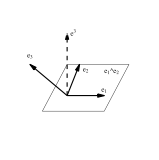
It is clear that in this case the frame  . The checked term  in the definition of reciprocal basis  indicates that this this term is missing in the product. The standard  and  constructed reciprocal vector  are perpendicular to all remaining vectors, . When  the normalization can be fixed in a standard way by requirement  (no summation). The squares and products of basis vectors satisfy (no summation),


.

The last properties may be combined into expressions ,  where  and  are the elements of the metric matrix . The number of basis elements with positive sign of  is denoted by  and that with the negative sign by  what echoes in the notation of Clifford algebra . The quantity  is called the signature of metric space. Sometimes the same name is carried over to quantity . Since , the quantity   is called the  signature of the basis.Note, that in two (standard and reciprocal) basis interpretation the primary and reciprocal basis are just the two different bases that belong to the same vector space 𝒱 :-Graphics-.

If the dual space 𝒱^* is introduced (instead of reciprocal frame in the same space 𝒱 ), the interpretation of relation   is different.  Indeed  the metric tensor and its inverse now “lives” in different spaces. Therefore the  relation can be understood in “numerical” sense only (since objects are in different spaces!). This point is often ignored in text books and leads to confusion. 

The upper/lower index notation in GA is used when we want to have the formula written in coordinates that at the same time is coordinate independent, like in the tensor calculus. The square of a vector  depends on GA signature,   where the signs at coordinates  are determined by signature of  via metric of a particular algebra. Vector  can be expended  in a form, where scalars have upper/lower indices in both basis

,
. 

⌊e stress that operation of rising/lowering of a coefficient index is meaningless since the coefficient is a scalar quantity and can’t depend on signature.  However if we want to use Einstein’s summation convention (which assumes that over repeated upper and lower index we understand summation), then it is convenient to use upper indices in primary space basis and lower indices for coefficients for expansion in reciprocal basis:    and  . Note, that when expansion coefficient index is in the same position (up or down) as in the basis vector, we are forced to write summation explicitly (Einstein’s summation convention don’t apply), whereas when they are in opposite positions, summation sign is (or can be) omitted (summation of course is assumed).  ⌊hen expression lacks a basis vector, for example, this happens after we compute square of vector (in orthonormal basis)

  ,
  , 

then rising/lowering of such an index in the final expression is forbidden (despite that both  and   are  scalars!). The reason is that in these cases we already assumed IMPLICITLY (before computation) that one of the expansion coefficient was taken from expansion in the primary basis and the other in the reciprocal basis (these coefficients can be completely different if computation is performed in arbitrary non orthogonal basis, i.e.   and  can differ  more than just by sign or factor as  previous example demonstrated). Therefore simple lowering or rising of any of them in the final answer will spoil  our assumption that we made before calculations were started. It would be like changing the game rules in the middle of game. Lowering  or rising index in such an expression, however, is possible and  is realised with the help of metric tensor , which takes into account basis vector index lowering/rising (since   and   ).

Computational verification

Choose algebra and compute pseudoscalar (aka volume element)

```mathematica
testAlgebra=Cl[2,3];
gaDefineOrthonormalBasis[testAlgebra]
```

Basis vectors are stored in   gaOrthonormalBasis[230,InvDeg[Lex]]

Running algebra is: gaRunningAlgebra=  230

{1,1230,2230,3230,4230,5230,12230,13230,14230,15230,23230,24230,25230,34230,35230,45230,123230,124230,125230,134230,135230,145230,234230,235230,245230,345230,1234230,1235230,1245230,1345230,2345230,12345230}

Pseudoscalar  in fact already computed when constructing orthonormal basis

```mathematica
gaI[testAlgebra]
```

12345230

Indeed

```mathematica
gaOrthonormalBasis[testAlgebra,"InvDeg[Lex]",{1}]
OuterProduct@@gaOrthonormalBasis[testAlgebra,"InvDeg[Lex]",{1}]
```

{1230,2230,3230,4230,5230}

12345230

We can verify that reciprocal vectors

```mathematica
gaOrthonormalBasis[testAlgebra,"InvDeg[Lex]",{1}]/.{mvDownUp[di_List,ui_List]:>mvDownUp[ui,di]}
gaIndexDown[%]
```

{1230,2230,3230,4230,5230}

{1230,2230,-3230,-4230,-5230}

are the same as given by formula  . First we implement the formula as

```mathematica
eRecip[j_]:=(-1)^(j-1)*(OuterProduct@@Drop[gaOrthonormalBasis[testAlgebra,"InvDeg[Lex]",{1}],{j}])\[GeometricProduct]gaInverse[gaI[testAlgebra]]
```

Using the definition compute reciprocals for all basis vectors

```mathematica
eRecip/@Range[gaDimensionOfVectorSpace[testAlgebra]]
```

{1230,2230,-3230,-4230,-5230}

Since orthonormality relation  was already checked before,  we check only the summation formula

```mathematica
gaDimensionOfVectorSpace[testAlgebra]
Sum[𝕖[{i}]\[InnerProduct]𝕖[{},{i}],{i,gaDimensionOfVectorSpace[testAlgebra]}]
```

5

5

```mathematica
ClearAll[{eRecip}];
```

Section.Item	The upper/lower index notation.  This section is duplication of already described subject and is omitted from electronic supplement. Only example is included.

Example of non-orthogonal reciprocal basis.  Let  be the standard orthonormal basis vectors and  be general non-orthonormal  vectors. The orthonormal basis satisfies .  Let the both basis vectors be connected by relations: [Cia Handbooke kazkas visai negerai: butent ten sumaisyta geometrine ir vidine sandaugos!!!]

.

The both basis must satisfy  and , where down and up index positions relate the primary and  reciprocal frames. The standard basis automatically satisfies . ⌊e look for how to express  in terms of .  First of all, note that the above system can be solved with respect to basis ,

.

Since  is orthonormal we have . ⌊hen  the reciprocal vector satisfy  (no summation in this particular case). Then after multiplication of both sides of  by  we have   (no summation over i). In general, for orthonormal basis we have  where the sign depends on GA signature. In the following we shall take the   algebra having the positive signature, so that . To find the relations between reciprocal basis in the primed system the condition  is used. Then the product of  by  basis vectors gives

,
,
.

 From this follows that . Similarly, one can find   and . So the relations between the reciprocal basis vectors are [paskutinese dviejose formulese klaidos TEX faile]

,	,
,		,
,		.

The equations on the right-hand side can be obtained by solving the left-hand side equations with respect to . One can check that in the primed frame . 
Similarly,  and . If indices are different the products are equal zero, for example, , etc. In a similar way one can check that,  , etc. Thus, we have constructed the primary and reciprocal (dashed) basis in terms of orthonormal basis . Note that the dashed basis is neither normalized nor orthogonal.

Computational verification

Choose algebra and verify computations of above example. The computations are very similar to what we did in previous example only in a slightly different fashion

```mathematica
testAlgebra=Cl[3,0];
gaDefineOrthonormalBasis[testAlgebra]
```

Running algebra is: gaRunningAlgebra=  300

{1,1300,2300,3300,12300,13300,23300,123300}

Define nonorthonormal primary basis: . To this end we name nonorthonormal basis vectors as p[1],p[2],p[3] and (important!) wrap them by generic noncommutative head MV[]. There are  rules defined how to dealt with this head, however, a number of package functions are instructed to handle this case much like the head of basis vector 𝕖[], i.𝕖. treats  the head as noncommutative quantity.

```mathematica
primaryNonorthonormalViaPrimaryOrthonormalRules=Thread[{MV[p[1]],MV[p[2]],MV[p[3]]}->{-𝕖[1]-𝕖[2]+𝕖[3],-𝕖[1]+𝕖[3],2𝕖[1]+𝕖[2]-𝕖[3]}]
```

{MV[p[1]]→-1300-2300+3300,MV[p[2]]→-1300+3300,MV[p[3]]→2 1300+2300-3300}

Solve for orthonormal vectors

```mathematica
Equal@@@primaryNonorthonormalViaPrimaryOrthonormalRules
primaryOrthonormalViaPrimaryNonorthonormalRules=Flatten[Solve[%,{𝕖[1],𝕖[2],𝕖[3]}]]
```

{MV[p[1]]==-1300-2300+3300,MV[p[2]]==-1300+3300,MV[p[3]]==2 1300+2300-3300}

{1300→MV[p[1]]+MV[p[3]],2300→-MV[p[1]]+MV[p[2]],3300→MV[p[1]]+MV[p[2]]+MV[p[3]]}

We will  follow direct manipulations described above,

First check projections , , .

```mathematica
MV[r[1]]\[InnerProduct]𝕖[1]/.primaryOrthonormalViaPrimaryNonorthonormalRules//gaPE
```

MV[r[1]]\[InnerProduct]MV[p[1]]+MV[r[1]]\[InnerProduct]MV[p[3]]

Since for unspecified multivector (head MV[]) there are no defined rules, add some. In particular add a rule which “teaches” that inner product of primary and reciprocal basis vectors are orthonormal, i.e. replace inner product of primary and reciprocal vectors by Kronecker delta

```mathematica
primaryAndReciprocalInnerProductRules={InnerProduct[MV[r[i_]],MV[p[j_]]]:>KroneckerDelta[i,j],InnerProduct[MV[p[i_]],MV[r[j_]]]:>KroneckerDelta[i,j]}
```

{MV[r[i_]]\[InnerProduct]MV[p[j_]]:>i,j,MV[p[i_]]\[InnerProduct]MV[r[j_]]:>i,j}

With these rules we obtain

```mathematica
(MV[r[1]]\[InnerProduct]𝕖[1]/.primaryOrthonormalViaPrimaryNonorthonormalRules//gaPE)/.primaryAndReciprocalInnerProductRules
```

1

```mathematica
(MV[r[1]]\[InnerProduct]𝕖[2]/.primaryOrthonormalViaPrimaryNonorthonormalRules//gaPE)/.primaryAndReciprocalInnerProductRules
```

-1

```mathematica
(MV[r[1]]\[InnerProduct]𝕖[3]/.primaryOrthonormalViaPrimaryNonorthonormalRules//gaPE)/.primaryAndReciprocalInnerProductRules
```

1

Or for entire expansion

```mathematica
Sum[MV[r[1]]\[InnerProduct]𝕖[i]\[GeometricProduct]𝕖[i],{i,gaDimensionOfVectorSpace[testAlgebra]}]
```

MV[r[1]]\[InnerProduct]1300\[GeometricProduct]1300+MV[r[1]]\[InnerProduct]2300\[GeometricProduct]2300+MV[r[1]]\[InnerProduct]3300\[GeometricProduct]3300

```mathematica
gaPE[Sum[(MV[r[1]]\[InnerProduct]𝕖[i]/.primaryOrthonormalViaPrimaryNonorthonormalRules)\[GeometricProduct]𝕖[i],{i,gaDimensionOfVectorSpace[testAlgebra]}]]/.primaryAndReciprocalInnerProductRules
er[1]=%//gaIndexUp
```

1300-2300+3300

1300-2300+3300

We can check the answer using computation method from previous example (without computing projections)

```mathematica
Last/@gaReciprocalVectorRules[Last/@primaryNonorthonormalViaPrimaryOrthonormalRules]
```

{1300-2300+3300,2300+3300,1300+3300}

Similar computation for second and third reciprocal gives

```mathematica
gaPE[Sum[(MV[r[2]]\[InnerProduct]𝕖[i]/.primaryOrthonormalViaPrimaryNonorthonormalRules)\[GeometricProduct]𝕖[i],{i,gaDimensionOfVectorSpace[testAlgebra]}]]/.primaryAndReciprocalInnerProductRules
er[2]=%//gaIndexUp
```

2300+3300

2300+3300

```mathematica
gaPE[Sum[(MV[r[3]]\[InnerProduct]𝕖[i]/.primaryOrthonormalViaPrimaryNonorthonormalRules)\[GeometricProduct]𝕖[i],{i,gaDimensionOfVectorSpace[testAlgebra]}]]/.primaryAndReciprocalInnerProductRules
er[3]=%//gaIndexUp
```

1300+3300

1300+3300

Now we can express reciprocal orthonormal basis vector in terms of nonorthonormal vectors

```mathematica
Flatten[Solve[{MV[r[1]]==er[1],MV[r[2]]==er[2],MV[r[3]]==er[3]},{𝕖[{},{1}],𝕖[{},{2}],𝕖[{},{3}]}]]
```

{1300→-MV[r[1]]-MV[r[2]]+2 MV[r[3]],2300→-MV[r[1]]+MV[r[3]],3300→MV[r[1]]+MV[r[2]]-MV[r[3]]}

In the end we test that inner product of reciprocal and primary vectors in nonorthogonal basis yields identity matrix

```mathematica
TableForm[gaPE[Outer[InnerProduct,{er[1],er[2],er[3]},({MV[p[1]],MV[p[2]],MV[p[3]]}/.primaryNonorthonormalViaPrimaryOrthonormalRules)]],TableHeadings->{{"","",""},{"","",""}}]
```

|  |  | 
 | 1 | 0 | 0
 | 0 | 1 | 0
 | 0 | 0 | 1

Note that geometric product of them is very different!

```mathematica
TableForm[gaPE[gaIndexDown[Outer[GeometricProduct,{er[1],er[2],er[3]},({MV[p[1]],MV[p[2]],MV[p[3]]}/.primaryNonorthonormalViaPrimaryOrthonormalRules)]]],TableHeadings->{{"","",""},{"","",""}}]
```

|  |  | 
 | 1-2 12300+2 13300 | -12300+2 13300-23300 | 3 12300-3 13300
 | 12300+13300+2 23300 | 1+12300+13300+23300 | -2 12300-2 13300-2 23300
 | -12300+2 13300+23300 | 2 13300 | 1+12300-3 13300-23300

Metric is indeed nonorthonormal

```mathematica
TableForm[gaPE[Outer[InnerProduct,{er[1],er[2],er[3]},{er[1],er[2],er[3]}]],TableHeadings->{{"","",""},{"","",""}}]
```

|  |  | 
 | 3 | 0 | 2
 | 0 | 2 | 1
 | 2 | 1 | 2

```mathematica
TableForm[gaPE[Outer[InnerProduct,
({MV[p[1]],MV[p[2]],MV[p[3]]}/.primaryNonorthonormalViaPrimaryOrthonormalRules),({MV[p[1]],MV[p[2]],MV[p[3]]}/.primaryNonorthonormalViaPrimaryOrthonormalRules)
]],TableHeadings->{{"","",""},{"","",""}}]
```

|  |  | 
 | 3 | 2 | -4
 | 2 | 2 | -3
 | -4 | -3 | 6

```mathematica
ClearAll[{p,r,er,primaryAndReciprocalInnerProductRules,primaryNonorthonormalViaPrimaryOrthonormalRules,primaryOrthonormalViaPrimaryNonorthonormalRules}];
```

Section.Item	Index raising and lowering rule.  In orthonormal basis, when , the metric matrix consists of ’s only. In this case the projections of vector  onto initial basis  and reciprocal basis  are
either equal or differ by sign only. This property allows to introduce a simple rule for alteration  between both orthonormal basis.

 if ,
, if .	(index raising/lowering rule)

The rule can be extended to blades by applying it to every individual basis vector in the blade. For example,  in   and , whereas   in  and .   in  . Using the index rule the vector in   can be written compactly in a form of  relativistic algebra, ,  where  and  are the scalars. By comparing expansion coefficients in different basis one see that    for  and     for .  The square of the vector (in orthonormal basis) then is
 or, alternatively, . 

In  algebras  whereas in  algebras  (the sign comes from rising of basis vectors). Therefore, the square of the vector in    is always a positive and in   negative number. Similarly to tensor calculus it is possible to raise the lower index, or vice versa, with a help of  metric matrix :  (where again matrix elements are computed by multiplying basis vectors) . Since in a case of orthonormal basis the metric matrix is diagonal and consists of ’s, ,  summation over repeated index provides the correct signs in front of respective coefficients. We stress once more, that rules like   for   algebras and      algebras are due rising/lowering  of indices of  basis vectors and Einstein summation convention, since index position for a scalar quantity (a coefficient) make no sense.

Computational verification

Here we repeat index index how index lowering/rising works. For Euclidean algebras  coefficients in primary and reciprocal basis are the same

```mathematica
testAlgebraEuclid=Cl[3,0];
gaDefineOrthonormalBasis[testAlgebraEuclid,Quiet->False]
```

Basis vectors are stored in   gaOrthonormalBasis[300,InvDeg[Lex]]

Running algebra is: gaRunningAlgebra=  300

{1,1300,2300,3300,12300,13300,23300,123300}

```mathematica
(#\[GeometricProduct]#)&/@gaOrthonormalBasis[testAlgebraEuclid,"InvDeg[Lex]",{1}]
```

{1,1,1}

Primary basis

```mathematica
anEuclideanVector=gaGeneralMultivector[a,testAlgebraEuclid,{1}]
```

a[1] 1300+a[2] 2300+a[3] 3300

```mathematica
gaReciprocalVectorRules[gaOrthonormalBasis[testAlgebraEuclid,"InvDeg[Lex]",{1}]]
```

{1300→1300,2300→2300,3300→3300}

```mathematica
gaIndexUp[anEuclideanVector]
```

a[1] 1300+a[2] 2300+a[3] 3300

```mathematica
gaIndexUp[gaGeneralMultivector[a,testAlgebraEuclid]]
```

a[0]+a[1] 1300+a[2] 2300+a[3] 3300+a[4] 12300+a[5] 13300+a[6] 23300+a[7] 123300

Comparing coefficients at both basis we see that they are exactly the same.  Reciprocal basis elements can be conveniently input by first entering an empty list and then a list with up indices, for example, typing   𝕖[{},{1,3}] in the input cell gives a basis bivector ( in x-z plane). Typing indices in both list, you will get mixed basis. In order to perform computations, however, you often will need to rise or lower all indices. That is implementation limitation, since we don’t want to dealt with so many different possibilities. In simple cases, however, this works without additional attempts

```mathematica
𝕖[{},{1,3}]
```

13300

```mathematica
(2𝕖[{1},{2}]+𝕖[1])\[GeometricProduct]𝕖[{},{2,3}]//gaPE
```

2 13300+123300

```mathematica
(2𝕖[{1},{2}]+𝕖[1])\[GeometricProduct]𝕖[{},{2,3}]//gaIndexDown//gaPE
```

2 13300+123300

```mathematica
(2𝕖[{1},{2}]+𝕖[1])\[GeometricProduct]𝕖[{},{2,3}]//gaIndexUp//gaPE
```

2 13300+123300

Also note, that we attempt to catch invalid input from the very beginning.  While the second (two down indices) should give zero, we prefer to stop calculations.

```mathematica
(2𝕖[{1},{2}]+𝕖[1])\[GeometricProduct]𝕖[{},{2,4}]
```

GeometricAlgebra`p`checkIndexConsistency::IndexTooLarge: Error. Index value in {{2,4}} that exceeds either Clifford vector space or coordinate chart manifold dimension is detected.

(1300+2 12300)\[GeometricProduct]𝕖[{},{2,4}]

```mathematica
(2𝕖[{1,1},{2}]+𝕖[1])\[GeometricProduct]𝕖[{},{2,3}]
```

GeometricAlgebra`p`checkIndexConsistency::SameIndices: Error. Index set {{1,1},{2}} contains repeated indices. All indices in base element should be different.

(2 𝕖[{1,1},{2}]+1300)\[GeometricProduct]23300

The case with same up and down index might be pretty valid in curved spaces, and behaviour might change in future.

```mathematica
(2𝕖[{1},{1}]+𝕖[1])\[GeometricProduct]𝕖[{},{2,3}]
```

GeometricAlgebra`p`checkIndexConsistency::SameIndices: Error. Index set {{1},{1}} contains repeated indices. All indices in base element should be different.

(2 𝕖[{1},{1}]+1300)\[GeometricProduct]23300

If we take (pure) anti-Euclidean algebra

```mathematica
testAlgebraAntiEuclid=Cl[0,3];
gaDefineOrthonormalBasis[testAlgebraAntiEuclid,Quiet->False]
```

Basis vectors are stored in   gaOrthonormalBasis[030,InvDeg[Lex]]

Running algebra is: gaRunningAlgebra=  030

{1,1030,2030,3030,12030,13030,23030,123030}

```mathematica
(#\[GeometricProduct]#)&/@gaOrthonormalBasis[testAlgebraAntiEuclid,"InvDeg[Lex]",{1}]
```

{-1,-1,-1}

we will have

```mathematica
gaReciprocalVectorRules[gaOrthonormalBasis[testAlgebraAntiEuclid,"InvDeg[Lex]",{1}]]
```

{1030→-1030,2030→-2030,3030→-3030}

```mathematica
anAntiEuclideanVector=gaGeneralMultivector[a,testAlgebraAntiEuclid,{1}]
```

a[1] 1030+a[2] 2030+a[3] 3030

```mathematica
gaIndexUp[anAntiEuclideanVector]
```

-a[1] 1030-a[2] 2030-a[3] 3030

By comparing we see that expansions coefficients in the reciprocal frame has opposite signs. Note that we can do computations in multiple algebras. When doing so we should be careful and always keep eye which algebra currently is set as default by looking at value of

```mathematica
gaRunningAlgebra
```

030

since in (rather rare) cases when there is no possibility from input to decide which algebra we dealt with, we use value provided by variable gaRunningAlgebra. For example, new input basis elements are assumed to belong to running algebra

```mathematica
𝕖[1]//FullForm
```

\[DoubleStruckE][mvDownUp[List[1],List[]],Cl[0,3,0]]

This however can be modified by issuing (which simply sets  gaRunningAlgebra value to the given algebra).

```mathematica
gaDefineInput[testAlgebraEuclid]
```

Running algebra is: gaRunningAlgebra=  300

```mathematica
gaRunningAlgebra
```

300

```mathematica
𝕖[1]//FullForm
```

\[DoubleStruckE][mvDownUp[List[1],List[]],Cl[3,0,0]]

```mathematica
𝕖[1]\[GeometricProduct]𝕖[1]
```

1

```mathematica
gaIndexUp[gaGeneralMultivector[a,testAlgebraAntiEuclid]]
```

a[0]-a[1] 1030-a[2] 2030-a[3] 3030+a[4] 12030+a[5] 13030+a[6] 23030-a[7] 123030

In general we don't recommend using many algebras at the same time (though sometimes this is inevitable, see unit about matrix representations and about idempotents) . There are at least few reasons for this. First, for algebra  can be have different basis orderings (we will explain  them in the end of this notebook).  This may lead to confusion even for a single algebra. Second, computation packages never are perfect, so probability that your encounter a bug increases.

```mathematica
ClearAll[{testAlgebraAntiEuclid,testAlgebraEuclid,anAntiEuclideanVector,anEuclideanVector}];
```

Section.Item	Properties of expansion in reciprocal frame.  In the space spanned by frame   one has the following expansions of  a general vector  and bivector ,

 for    
 for , 


These formulas can be generalized to any  blade  of grade-r and, due to linearity, to any homogeneous MV   ,  . The above formulas allow an expansion to MV:
. For general MV also the following expansion holds,  , where  represents multi-index and the summation is over full GA basis. The tilde mark over basis element denotes reversion operation.

Computational verification

Remind expansion into primary basis

```mathematica
testAlgebra=Cl[2,3];
gaDefineOrthonormalBasis[testAlgebra,Quiet->False]
```

Basis vectors are stored in   gaOrthonormalBasis[230,InvDeg[Lex]]

Running algebra is: gaRunningAlgebra=  230

{1,1230,2230,3230,4230,5230,12230,13230,14230,15230,23230,24230,25230,34230,35230,45230,123230,124230,125230,134230,135230,145230,234230,235230,245230,345230,1234230,1235230,1245230,1345230,2345230,12345230}

```mathematica
(#\[GeometricProduct]#)&/@gaOrthonormalBasis[testAlgebra,"InvDeg[Lex]",{1}]
```

{1,1,-1,-1,-1}

Expansion of vector (grade-1 element). Test of  for

```mathematica
initialVector=gaGeneralMultivector[a,testAlgebra,{1}]
```

a[1] 1230+a[2] 2230+a[3] 3230+a[4] 4230+a[5] 5230

```mathematica
reciprocalBasisVectors=gaOrthonormalBasis[testAlgebra,"InvDeg[Lex]",{1}]/.{mvDownUp[di_List,ui_List]:>mvDownUp[ui,di]}
```

{1230,2230,3230,4230,5230}

```mathematica
coefficientsOfExpansionOfVector=(#\[InnerProduct]initialVector)&/@reciprocalBasisVectors
gaPE[%]
```

{1230\[InnerProduct](a[1] 1230+a[2] 2230+a[3] 3230+a[4] 4230+a[5] 5230),2230\[InnerProduct](a[1] 1230+a[2] 2230+a[3] 3230+a[4] 4230+a[5] 5230),3230\[InnerProduct](a[1] 1230+a[2] 2230+a[3] 3230+a[4] 4230+a[5] 5230),4230\[InnerProduct](a[1] 1230+a[2] 2230+a[3] 3230+a[4] 4230+a[5] 5230),5230\[InnerProduct](a[1] 1230+a[2] 2230+a[3] 3230+a[4] 4230+a[5] 5230)}

{a[1],a[2],a[3],a[4],a[5]}

We see, that after performing all steps we recovered  the init vector, as it should be

```mathematica
vectorAfterExpansion=Inner[GeometricProduct,gaOrthonormalBasis[testAlgebra,"InvDeg[Lex]",{1}],coefficientsOfExpansionOfVector,Plus]
gaPE[%]
```

1230\[GeometricProduct]1230\[InnerProduct](a[1] 1230+a[2] 2230+a[3] 3230+a[4] 4230+a[5] 5230)+2230\[GeometricProduct]2230\[InnerProduct](a[1] 1230+a[2] 2230+a[3] 3230+a[4] 4230+a[5] 5230)+3230\[GeometricProduct]3230\[InnerProduct](a[1] 1230+a[2] 2230+a[3] 3230+a[4] 4230+a[5] 5230)+4230\[GeometricProduct]4230\[InnerProduct](a[1] 1230+a[2] 2230+a[3] 3230+a[4] 4230+a[5] 5230)+5230\[GeometricProduct]5230\[InnerProduct](a[1] 1230+a[2] 2230+a[3] 3230+a[4] 4230+a[5] 5230)

a[1] 1230+a[2] 2230+a[3] 3230+a[4] 4230+a[5] 5230

Do the same for bivector

```mathematica
initialBivector=gaGeneralMultivector[a,testAlgebra,{1}]\[OuterProduct]gaGeneralMultivector[b,testAlgebra,{1}]//gaPE
```

(-a[2] b[1]+a[1] b[2]) 12230+(-a[3] b[1]+a[1] b[3]) 13230+(-a[4] b[1]+a[1] b[4]) 14230+(-a[5] b[1]+a[1] b[5]) 15230+(-a[3] b[2]+a[2] b[3]) 23230+(-a[4] b[2]+a[2] b[4]) 24230+(-a[5] b[2]+a[2] b[5]) 25230+(-a[4] b[3]+a[3] b[4]) 34230+(-a[5] b[3]+a[3] b[5]) 35230+(-a[5] b[4]+a[4] b[5]) 45230

```mathematica
coefficientsOfExpansionOfBivector=(#\[InnerProduct]initialBivector)&/@reciprocalBasisVectors
gaPE[%]
```

{1230\[InnerProduct]((-a[2] b[1]+a[1] b[2]) 12230+(-a[3] b[1]+a[1] b[3]) 13230+(-a[4] b[1]+a[1] b[4]) 14230+(-a[5] b[1]+a[1] b[5]) 15230+(-a[3] b[2]+a[2] b[3]) 23230+(-a[4] b[2]+a[2] b[4]) 24230+(-a[5] b[2]+a[2] b[5]) 25230+(-a[4] b[3]+a[3] b[4]) 34230+(-a[5] b[3]+a[3] b[5]) 35230+(-a[5] b[4]+a[4] b[5]) 45230),2230\[InnerProduct]((-a[2] b[1]+a[1] b[2]) 12230+(-a[3] b[1]+a[1] b[3]) 13230+(-a[4] b[1]+a[1] b[4]) 14230+(-a[5] b[1]+a[1] b[5]) 15230+(-a[3] b[2]+a[2] b[3]) 23230+(-a[4] b[2]+a[2] b[4]) 24230+(-a[5] b[2]+a[2] b[5]) 25230+(-a[4] b[3]+a[3] b[4]) 34230+(-a[5] b[3]+a[3] b[5]) 35230+(-a[5] b[4]+a[4] b[5]) 45230),3230\[InnerProduct]((-a[2] b[1]+a[1] b[2]) 12230+(-a[3] b[1]+a[1] b[3]) 13230+(-a[4] b[1]+a[1] b[4]) 14230+(-a[5] b[1]+a[1] b[5]) 15230+(-a[3] b[2]+a[2] b[3]) 23230+(-a[4] b[2]+a[2] b[4]) 24230+(-a[5] b[2]+a[2] b[5]) 25230+(-a[4] b[3]+a[3] b[4]) 34230+(-a[5] b[3]+a[3] b[5]) 35230+(-a[5] b[4]+a[4] b[5]) 45230),4230\[InnerProduct]((-a[2] b[1]+a[1] b[2]) 12230+(-a[3] b[1]+a[1] b[3]) 13230+(-a[4] b[1]+a[1] b[4]) 14230+(-a[5] b[1]+a[1] b[5]) 15230+(-a[3] b[2]+a[2] b[3]) 23230+(-a[4] b[2]+a[2] b[4]) 24230+(-a[5] b[2]+a[2] b[5]) 25230+(-a[4] b[3]+a[3] b[4]) 34230+(-a[5] b[3]+a[3] b[5]) 35230+(-a[5] b[4]+a[4] b[5]) 45230),5230\[InnerProduct]((-a[2] b[1]+a[1] b[2]) 12230+(-a[3] b[1]+a[1] b[3]) 13230+(-a[4] b[1]+a[1] b[4]) 14230+(-a[5] b[1]+a[1] b[5]) 15230+(-a[3] b[2]+a[2] b[3]) 23230+(-a[4] b[2]+a[2] b[4]) 24230+(-a[5] b[2]+a[2] b[5]) 25230+(-a[4] b[3]+a[3] b[4]) 34230+(-a[5] b[3]+a[3] b[5]) 35230+(-a[5] b[4]+a[4] b[5]) 45230)}

{(-a[2] b[1]+a[1] b[2]) 2230+(-a[3] b[1]+a[1] b[3]) 3230+(-a[4] b[1]+a[1] b[4]) 4230+(-a[5] b[1]+a[1] b[5]) 5230,(a[2] b[1]-a[1] b[2]) 1230+(-a[3] b[2]+a[2] b[3]) 3230+(-a[4] b[2]+a[2] b[4]) 4230+(-a[5] b[2]+a[2] b[5]) 5230,(a[3] b[1]-a[1] b[3]) 1230+(a[3] b[2]-a[2] b[3]) 2230+(-a[4] b[3]+a[3] b[4]) 4230+(-a[5] b[3]+a[3] b[5]) 5230,(a[4] b[1]-a[1] b[4]) 1230+(a[4] b[2]-a[2] b[4]) 2230+(a[4] b[3]-a[3] b[4]) 3230+(-a[5] b[4]+a[4] b[5]) 5230,(a[5] b[1]-a[1] b[5]) 1230+(a[5] b[2]-a[2] b[5]) 2230+(a[5] b[3]-a[3] b[5]) 3230+(a[5] b[4]-a[4] b[5]) 4230}

```mathematica
bivectorAfterExpansion=Inner[GeometricProduct,gaOrthonormalBasis[testAlgebra,"InvDeg[Lex]",{1}],coefficientsOfExpansionOfBivector,Plus]
gaPE[%]
```

1230\[GeometricProduct]1230\[InnerProduct]((-a[2] b[1]+a[1] b[2]) 12230+(-a[3] b[1]+a[1] b[3]) 13230+(-a[4] b[1]+a[1] b[4]) 14230+(-a[5] b[1]+a[1] b[5]) 15230+(-a[3] b[2]+a[2] b[3]) 23230+(-a[4] b[2]+a[2] b[4]) 24230+(-a[5] b[2]+a[2] b[5]) 25230+(-a[4] b[3]+a[3] b[4]) 34230+(-a[5] b[3]+a[3] b[5]) 35230+(-a[5] b[4]+a[4] b[5]) 45230)+2230\[GeometricProduct]2230\[InnerProduct]((-a[2] b[1]+a[1] b[2]) 12230+(-a[3] b[1]+a[1] b[3]) 13230+(-a[4] b[1]+a[1] b[4]) 14230+(-a[5] b[1]+a[1] b[5]) 15230+(-a[3] b[2]+a[2] b[3]) 23230+(-a[4] b[2]+a[2] b[4]) 24230+(-a[5] b[2]+a[2] b[5]) 25230+(-a[4] b[3]+a[3] b[4]) 34230+(-a[5] b[3]+a[3] b[5]) 35230+(-a[5] b[4]+a[4] b[5]) 45230)+3230\[GeometricProduct]3230\[InnerProduct]((-a[2] b[1]+a[1] b[2]) 12230+(-a[3] b[1]+a[1] b[3]) 13230+(-a[4] b[1]+a[1] b[4]) 14230+(-a[5] b[1]+a[1] b[5]) 15230+(-a[3] b[2]+a[2] b[3]) 23230+(-a[4] b[2]+a[2] b[4]) 24230+(-a[5] b[2]+a[2] b[5]) 25230+(-a[4] b[3]+a[3] b[4]) 34230+(-a[5] b[3]+a[3] b[5]) 35230+(-a[5] b[4]+a[4] b[5]) 45230)+4230\[GeometricProduct]4230\[InnerProduct]((-a[2] b[1]+a[1] b[2]) 12230+(-a[3] b[1]+a[1] b[3]) 13230+(-a[4] b[1]+a[1] b[4]) 14230+(-a[5] b[1]+a[1] b[5]) 15230+(-a[3] b[2]+a[2] b[3]) 23230+(-a[4] b[2]+a[2] b[4]) 24230+(-a[5] b[2]+a[2] b[5]) 25230+(-a[4] b[3]+a[3] b[4]) 34230+(-a[5] b[3]+a[3] b[5]) 35230+(-a[5] b[4]+a[4] b[5]) 45230)+5230\[GeometricProduct]5230\[InnerProduct]((-a[2] b[1]+a[1] b[2]) 12230+(-a[3] b[1]+a[1] b[3]) 13230+(-a[4] b[1]+a[1] b[4]) 14230+(-a[5] b[1]+a[1] b[5]) 15230+(-a[3] b[2]+a[2] b[3]) 23230+(-a[4] b[2]+a[2] b[4]) 24230+(-a[5] b[2]+a[2] b[5]) 25230+(-a[4] b[3]+a[3] b[4]) 34230+(-a[5] b[3]+a[3] b[5]) 35230+(-a[5] b[4]+a[4] b[5]) 45230)

2 (-a[2] b[1]+a[1] b[2]) 12230+2 (-a[3] b[1]+a[1] b[3]) 13230+2 (-a[4] b[1]+a[1] b[4]) 14230+2 (-a[5] b[1]+a[1] b[5]) 15230+2 (-a[3] b[2]+a[2] b[3]) 23230+2 (-a[4] b[2]+a[2] b[4]) 24230+2 (-a[5] b[2]+a[2] b[5]) 25230+2 (-a[4] b[3]+a[3] b[4]) 34230+2 (-a[5] b[3]+a[3] b[5]) 35230+2 (-a[5] b[4]+a[4] b[5]) 45230

Comparing coefficients at both basis we see that they are differ by factor of two.

```mathematica
{(bivectorAfterExpansion//gaPE)[[1]],initialBivector[[1]]}
```

{2 (-a[2] b[1]+a[1] b[2]) 12230,(-a[2] b[1]+a[1] b[2]) 12230}

Check for any homogeneous grade-r multivector

```mathematica
testGrade=4;
initialMultivector=gaGeneralMultivector[d,testAlgebra,{testGrade}]//gaPE
```

d[26] 1234230+d[27] 1235230+d[28] 1245230+d[29] 1345230+d[30] 2345230

```mathematica
coefficientsOfExpansionOfMV=(#\[InnerProduct]initialMultivector)&/@reciprocalBasisVectors
gaPE[%]
```

{1230\[InnerProduct](d[26] 1234230+d[27] 1235230+d[28] 1245230+d[29] 1345230+d[30] 2345230),2230\[InnerProduct](d[26] 1234230+d[27] 1235230+d[28] 1245230+d[29] 1345230+d[30] 2345230),3230\[InnerProduct](d[26] 1234230+d[27] 1235230+d[28] 1245230+d[29] 1345230+d[30] 2345230),4230\[InnerProduct](d[26] 1234230+d[27] 1235230+d[28] 1245230+d[29] 1345230+d[30] 2345230),5230\[InnerProduct](d[26] 1234230+d[27] 1235230+d[28] 1245230+d[29] 1345230+d[30] 2345230)}

{d[26] 234230+d[27] 235230+d[28] 245230+d[29] 345230,-d[26] 134230-d[27] 135230-d[28] 145230+d[30] 345230,d[26] 124230+d[27] 125230-d[29] 145230-d[30] 245230,-d[26] 123230+d[28] 125230+d[29] 135230+d[30] 235230,-d[27] 123230-d[28] 124230-d[29] 134230-d[30] 234230}

```mathematica
multivectorAfterExpansion=Inner[GeometricProduct,gaOrthonormalBasis[testAlgebra,"InvDeg[Lex]",{1}],coefficientsOfExpansionOfMV,Plus]
gaPE[%]
```

1230\[GeometricProduct]1230\[InnerProduct](d[26] 1234230+d[27] 1235230+d[28] 1245230+d[29] 1345230+d[30] 2345230)+2230\[GeometricProduct]2230\[InnerProduct](d[26] 1234230+d[27] 1235230+d[28] 1245230+d[29] 1345230+d[30] 2345230)+3230\[GeometricProduct]3230\[InnerProduct](d[26] 1234230+d[27] 1235230+d[28] 1245230+d[29] 1345230+d[30] 2345230)+4230\[GeometricProduct]4230\[InnerProduct](d[26] 1234230+d[27] 1235230+d[28] 1245230+d[29] 1345230+d[30] 2345230)+5230\[GeometricProduct]5230\[InnerProduct](d[26] 1234230+d[27] 1235230+d[28] 1245230+d[29] 1345230+d[30] 2345230)

4 d[26] 1234230+4 d[27] 1235230+4 d[28] 1245230+4 d[29] 1345230+4 d[30] 2345230

Comparing coefficients at both basis we see that they are differ by factor of two.

```mathematica
{(multivectorAfterExpansion//gaPE)[[1]],initialMultivector[[1]]}
```

{4 d[26] 1234230,d[26] 1234230}

```mathematica
ClearAll[{testGrade,initialMultivector,coefficientsOfExpansionOfMV,multivectorAfterExpansion,initialBivector,coefficientsOfExpansionOfBivector,bivectorAfterExpansion,initialVector,coefficientsOfExpansionOfVector,vectorAfterExpansion,reciprocalBasisVectors}];
```

Section.Item	Tensor-like notation. Kronecker delta definition  . Alternating tensor definition . So that in the tensor notation  the cross product of basis vectors in   GA may be written as:

  		(cross product in   )

The cross product of two vectors  and  then is

Computational verification

Cross product is defined in Euclidean 3D algebra only (also something similar can be constructed in 7D, see Lounesto book)

```mathematica
testAlgebra=Cl[3,0];
gaDefineOrthonormalBasis[testAlgebra,Quiet->False]
```

Basis vectors are stored in   gaOrthonormalBasis[300,InvDeg[Lex]]

Running algebra is: gaRunningAlgebra=  300

{1,1300,2300,3300,12300,13300,23300,123300}

Kronecker delta   and completely antisymmetric tensor in Mathematica are named as

```mathematica
{KroneckerDelta[1,2],Signature[{1,2,3}],Signature[{2,1,3}],Signature[{1,1,3}]}
```

{0,1,-1,0}

There also is LeviCivitaTensor[]. Cross product of two vectors with components

```mathematica
vX={x[1],x[2],x[3]}
vY={y[1],y[2],y[3]}
```

{x[1],x[2],x[3]}

{y[1],y[2],y[3]}

Can be constructed as (note interchanged vector components)

```mathematica
LeviCivitaTensor[3].vY.vX
```

{-x[3] y[2]+x[2] y[3],x[3] y[1]-x[1] y[3],-x[2] y[1]+x[1] y[2]}

or traditionally as

```mathematica
traditionalVectorProduct=Cross[vX,vY]
```

{-x[3] y[2]+x[2] y[3],x[3] y[1]-x[1] y[3],-x[2] y[1]+x[1] y[2]}

In GA it can be written as

```mathematica
gaGeneralMultivector[x,testAlgebra,{1}]
gaGeneralMultivector[y,testAlgebra,{1}]
```

x[1] 1300+x[2] 2300+x[3] 3300

y[1] 1300+y[2] 2300+y[3] 3300

```mathematica
gaVectorProduct=-gaI[testAlgebra]\[GeometricProduct]gaGeneralMultivector[x,testAlgebra,{1}]\[OuterProduct]gaGeneralMultivector[y,testAlgebra,{1}]//gaPE
gaVectorProductComponents=gaComponentCoefficientList[gaVectorProduct,gaOrthonormalBasis[testAlgebra,"InvDeg[Lex]",{1}]]
```

-((x[3] y[2]-x[2] y[3]) 1300)-(-x[3] y[1]+x[1] y[3]) 2300-(x[2] y[1]-x[1] y[2]) 3300

{-x[3] y[2]+x[2] y[3],x[3] y[1]-x[1] y[3],-x[2] y[1]+x[1] y[2]}

```mathematica
gaVectorProductComponents-traditionalVectorProduct
```

{0,0,0}

```mathematica
ClearAll[{vX,vY,gaVectorProduct,gaVectorProductComponents,traditionalVectorProduct}];
```

Relations between standard  and reciprocal   frames in nD orthonormal vector space. Summation over identical upper-lower indices is meant.

Useful tensor-like formulas expressed in initial and reciprocal frames.  are the vectors.  is a linear vector-valued function of vector argument, .


In case of Euclidean space (  algebra) the initial and reciprocal frames are equivalent, therefore all upper indices can be lowered.

Computational verification

Many of formulas provided in two tables above were already checked. In particular, entire first table was verified (formulas with metric will be covered below), and a first six formulas of the second table.  Here we check the rest ones

```mathematica
testAlgebra=Cl[3,4];
gaDefineOrthonormalBasis[testAlgebra,Quiet->False]
```

Basis vectors are stored in   gaOrthonormalBasis[340,InvDeg[Lex]]

Running algebra is: gaRunningAlgebra=  340

{1,1340,2340,3340,4340,5340,6340,7340,12340,13340,14340,15340,16340,17340,23340,24340,25340,26340,27340,34340,35340,36340,37340,45340,46340,47340,56340,57340,67340,123340,124340,125340,126340,127340,134340,135340,136340,137340,145340,146340,147340,156340,157340,167340,234340,235340,236340,237340,245340,246340,247340,256340,257340,267340,345340,346340,347340,356340,357340,367340,456340,457340,467340,567340,1234340,1235340,1236340,1237340,1245340,1246340,1247340,1256340,1257340,1267340,1345340,1346340,1347340,1356340,1357340,1367340,1456340,1457340,1467340,1567340,2345340,2346340,2347340,2356340,2357340,2367340,2456340,2457340,2467340,2567340,3456340,3457340,3467340,3567340,4567340,12345340,12346340,12347340,12356340,12357340,12367340,12456340,12457340,12467340,12567340,13456340,13457340,13467340,13567340,14567340,23456340,23457340,23467340,23567340,24567340,34567340,123456340,123457340,123467340,123567340,124567340,134567340,234567340,1234567340}

7-th formula,

```mathematica
testGrade=5
mvAr=gaGeneralMultivector[a,testAlgebra,{testGrade}]
```

5

a[99] 12345340+a[100] 12346340+a[101] 12347340+a[102] 12356340+a[103] 12357340+a[104] 12367340+a[105] 12456340+a[106] 12457340+a[107] 12467340+a[108] 12567340+a[109] 13456340+a[110] 13457340+a[111] 13467340+a[112] 13567340+a[113] 14567340+a[114] 23456340+a[115] 23457340+a[116] 23467340+a[117] 23567340+a[118] 24567340+a[119] 34567340

```mathematica
(1/(gaDimensionOfVectorSpace[testAlgebra]-testGrade))Sum[𝕖[i]\[GeometricProduct]𝕖[{},{i}]\[OuterProduct]mvAr,{i,gaDimensionOfVectorSpace[testAlgebra]}]
Expand[gaPE[gaIndexDown[%]]]
```

1/2 (1340\[GeometricProduct]1340\[OuterProduct](a[99] 12345340+a[100] 12346340+a[101] 12347340+a[102] 12356340+a[103] 12357340+a[104] 12367340+a[105] 12456340+a[106] 12457340+a[107] 12467340+a[108] 12567340+a[109] 13456340+a[110] 13457340+a[111] 13467340+a[112] 13567340+a[113] 14567340+a[114] 23456340+a[115] 23457340+a[116] 23467340+a[117] 23567340+a[118] 24567340+a[119] 34567340)+2340\[GeometricProduct]2340\[OuterProduct](a[99] 12345340+a[100] 12346340+a[101] 12347340+a[102] 12356340+a[103] 12357340+a[104] 12367340+a[105] 12456340+a[106] 12457340+a[107] 12467340+a[108] 12567340+a[109] 13456340+a[110] 13457340+a[111] 13467340+a[112] 13567340+a[113] 14567340+a[114] 23456340+a[115] 23457340+a[116] 23467340+a[117] 23567340+a[118] 24567340+a[119] 34567340)+3340\[GeometricProduct]3340\[OuterProduct](a[99] 12345340+a[100] 12346340+a[101] 12347340+a[102] 12356340+a[103] 12357340+a[104] 12367340+a[105] 12456340+a[106] 12457340+a[107] 12467340+a[108] 12567340+a[109] 13456340+a[110] 13457340+a[111] 13467340+a[112] 13567340+a[113] 14567340+a[114] 23456340+a[115] 23457340+a[116] 23467340+a[117] 23567340+a[118] 24567340+a[119] 34567340)+4340\[GeometricProduct]4340\[OuterProduct](a[99] 12345340+a[100] 12346340+a[101] 12347340+a[102] 12356340+a[103] 12357340+a[104] 12367340+a[105] 12456340+a[106] 12457340+a[107] 12467340+a[108] 12567340+a[109] 13456340+a[110] 13457340+a[111] 13467340+a[112] 13567340+a[113] 14567340+a[114] 23456340+a[115] 23457340+a[116] 23467340+a[117] 23567340+a[118] 24567340+a[119] 34567340)+5340\[GeometricProduct]5340\[OuterProduct](a[99] 12345340+a[100] 12346340+a[101] 12347340+a[102] 12356340+a[103] 12357340+a[104] 12367340+a[105] 12456340+a[106] 12457340+a[107] 12467340+a[108] 12567340+a[109] 13456340+a[110] 13457340+a[111] 13467340+a[112] 13567340+a[113] 14567340+a[114] 23456340+a[115] 23457340+a[116] 23467340+a[117] 23567340+a[118] 24567340+a[119] 34567340)+6340\[GeometricProduct]6340\[OuterProduct](a[99] 12345340+a[100] 12346340+a[101] 12347340+a[102] 12356340+a[103] 12357340+a[104] 12367340+a[105] 12456340+a[106] 12457340+a[107] 12467340+a[108] 12567340+a[109] 13456340+a[110] 13457340+a[111] 13467340+a[112] 13567340+a[113] 14567340+a[114] 23456340+a[115] 23457340+a[116] 23467340+a[117] 23567340+a[118] 24567340+a[119] 34567340)+7340\[GeometricProduct]7340\[OuterProduct](a[99] 12345340+a[100] 12346340+a[101] 12347340+a[102] 12356340+a[103] 12357340+a[104] 12367340+a[105] 12456340+a[106] 12457340+a[107] 12467340+a[108] 12567340+a[109] 13456340+a[110] 13457340+a[111] 13467340+a[112] 13567340+a[113] 14567340+a[114] 23456340+a[115] 23457340+a[116] 23467340+a[117] 23567340+a[118] 24567340+a[119] 34567340))

a[99] 12345340+a[100] 12346340+a[101] 12347340+a[102] 12356340+a[103] 12357340+a[104] 12367340+a[105] 12456340+a[106] 12457340+a[107] 12467340+a[108] 12567340+a[109] 13456340+a[110] 13457340+a[111] 13467340+a[112] 13567340+a[113] 14567340+a[114] 23456340+a[115] 23457340+a[116] 23467340+a[117] 23567340+a[118] 24567340+a[119] 34567340

8-th formula,

```mathematica
lhs[testAlgebra]=Sum[𝕖[i]\[GeometricProduct]mvAr\[GeometricProduct]𝕖[{},{i}],{i,gaDimensionOfVectorSpace[testAlgebra]}]
```

1340\[GeometricProduct](a[99] 12345340+a[100] 12346340+a[101] 12347340+a[102] 12356340+a[103] 12357340+a[104] 12367340+a[105] 12456340+a[106] 12457340+a[107] 12467340+a[108] 12567340+a[109] 13456340+a[110] 13457340+a[111] 13467340+a[112] 13567340+a[113] 14567340+a[114] 23456340+a[115] 23457340+a[116] 23467340+a[117] 23567340+a[118] 24567340+a[119] 34567340)\[GeometricProduct]1340+2340\[GeometricProduct](a[99] 12345340+a[100] 12346340+a[101] 12347340+a[102] 12356340+a[103] 12357340+a[104] 12367340+a[105] 12456340+a[106] 12457340+a[107] 12467340+a[108] 12567340+a[109] 13456340+a[110] 13457340+a[111] 13467340+a[112] 13567340+a[113] 14567340+a[114] 23456340+a[115] 23457340+a[116] 23467340+a[117] 23567340+a[118] 24567340+a[119] 34567340)\[GeometricProduct]2340+3340\[GeometricProduct](a[99] 12345340+a[100] 12346340+a[101] 12347340+a[102] 12356340+a[103] 12357340+a[104] 12367340+a[105] 12456340+a[106] 12457340+a[107] 12467340+a[108] 12567340+a[109] 13456340+a[110] 13457340+a[111] 13467340+a[112] 13567340+a[113] 14567340+a[114] 23456340+a[115] 23457340+a[116] 23467340+a[117] 23567340+a[118] 24567340+a[119] 34567340)\[GeometricProduct]3340+4340\[GeometricProduct](a[99] 12345340+a[100] 12346340+a[101] 12347340+a[102] 12356340+a[103] 12357340+a[104] 12367340+a[105] 12456340+a[106] 12457340+a[107] 12467340+a[108] 12567340+a[109] 13456340+a[110] 13457340+a[111] 13467340+a[112] 13567340+a[113] 14567340+a[114] 23456340+a[115] 23457340+a[116] 23467340+a[117] 23567340+a[118] 24567340+a[119] 34567340)\[GeometricProduct]4340+5340\[GeometricProduct](a[99] 12345340+a[100] 12346340+a[101] 12347340+a[102] 12356340+a[103] 12357340+a[104] 12367340+a[105] 12456340+a[106] 12457340+a[107] 12467340+a[108] 12567340+a[109] 13456340+a[110] 13457340+a[111] 13467340+a[112] 13567340+a[113] 14567340+a[114] 23456340+a[115] 23457340+a[116] 23467340+a[117] 23567340+a[118] 24567340+a[119] 34567340)\[GeometricProduct]5340+6340\[GeometricProduct](a[99] 12345340+a[100] 12346340+a[101] 12347340+a[102] 12356340+a[103] 12357340+a[104] 12367340+a[105] 12456340+a[106] 12457340+a[107] 12467340+a[108] 12567340+a[109] 13456340+a[110] 13457340+a[111] 13467340+a[112] 13567340+a[113] 14567340+a[114] 23456340+a[115] 23457340+a[116] 23467340+a[117] 23567340+a[118] 24567340+a[119] 34567340)\[GeometricProduct]6340+7340\[GeometricProduct](a[99] 12345340+a[100] 12346340+a[101] 12347340+a[102] 12356340+a[103] 12357340+a[104] 12367340+a[105] 12456340+a[106] 12457340+a[107] 12467340+a[108] 12567340+a[109] 13456340+a[110] 13457340+a[111] 13467340+a[112] 13567340+a[113] 14567340+a[114] 23456340+a[115] 23457340+a[116] 23467340+a[117] 23567340+a[118] 24567340+a[119] 34567340)\[GeometricProduct]7340

```mathematica
rhs[testAlgebra]=(-1)^testGrade (gaDimensionOfVectorSpace[testAlgebra]-2testGrade)\[GeometricProduct]mvAr
```

3 (a[99] 12345340+a[100] 12346340+a[101] 12347340+a[102] 12356340+a[103] 12357340+a[104] 12367340+a[105] 12456340+a[106] 12457340+a[107] 12467340+a[108] 12567340+a[109] 13456340+a[110] 13457340+a[111] 13467340+a[112] 13567340+a[113] 14567340+a[114] 23456340+a[115] 23457340+a[116] 23467340+a[117] 23567340+a[118] 24567340+a[119] 34567340)

```mathematica
Expand[gaPE[gaIndexDown[lhs[testAlgebra]]]-rhs[testAlgebra]]
```

0

9-th, 10-th and 11-th  formulas, nothing to test, since they simply expands linear function into primary  basis or define adjoint function

12-th formula,   is a definition of vector derivative operator to be covered in details in calculus part. Explanation will be postponed. We only mention that to perform differentiation we have to define coordinate system (here “Euclidean3DCS”). To define coordinate system we first  define position vector (here in Euclidean 3D space). Then coordinate system parameters and other needed quantities  are computed.

```mathematica
testAlgebra=Cl[3,0];
gaDefineOrthonormalBasis[testAlgebra];
```

Running algebra is: gaRunningAlgebra=  300

```mathematica
gaDefinePositionVector["Euclidean3D",Piecewise[{{x*𝕖[1]+y*𝕖[2]+z*𝕖[3],Element[{x,y,z},Reals]}},$Failed],{x,y,z},{},Quiet->True]
```

<|ManifoldName→Euclidean3D,GA→300,Dimension→3,Patches→1,gaRunningPatch→Patch1,ParameterRangeAssumptions→{},Parameters→{},StandardCoordinateNames→{x,y,z},Patch1→<|PointVector→x 1300+y 2300+z 3300,CoordinateRangeAssumptions→(x|y|z)∈ℝ|>|>

```mathematica
gaDefineCoordinateChart["Euclidean3DCS",gaPositionVector["Euclidean3D"],Quiet->True]
```

<|ChartName→Euclidean3DCS,ManifoldName→Euclidean3D,GA→300,Dimension→3,Patches→1,gaRunningPatch→Patch1,ParameterRangeAssumptions→{},Parameters→{},StandardCoordinateNames→{x,y,z},Patch1→<|PointVector→x 1300+y 2300+z 3300,CoordinateRangeAssumptions→(x|y|z)∈ℝ,BasisVectors→{1300Euclidean3DCSxyz:>1300,2300Euclidean3DCSxyz:>2300,3300Euclidean3DCSxyz:>3300},Metric→{{1,0,0},{0,1,0},{0,0,1}},ScaleFactors→{1,1,1},VolumeFactor→123300,InverseMetric→{{1,0,0},{0,1,0},{0,0,1}},ReciprocalVectors→{1300→1300,2300→2300,3300→3300},FullBasis→{1300Euclidean3DCSxyz→1300,2300Euclidean3DCSxyz→2300,3300Euclidean3DCSxyz→3300,12300Euclidean3DCSxyz→12300,13300Euclidean3DCSxyz→13300,23300Euclidean3DCSxyz→23300,123300Euclidean3DCSxyz→123300},ToBasisElementRules→{1300→1300Euclidean3DCSxyz,2300→2300Euclidean3DCSxyz,3300→3300Euclidean3DCSxyz,12300→12300Euclidean3DCSxyz,13300→13300Euclidean3DCSxyz,23300→23300Euclidean3DCSxyz,123300→123300Euclidean3DCSxyz},NormalToSurface→$Failed,ChristoffelSymbolsOfSecondKind→SymmetrizedArray[…]|>|>

Once we have coordinate system

```mathematica
gaRunningCoordinateChart
```

Euclidean3DCS

we can compute vector derivative (in this case differentiation argument was not specified, therefore we have operator). gaDE[] (like gaPE[] for algebra) expands it in terms of directional derivative

```mathematica
gaMultivectorDerivative["D1a"][gaReciprocalVectors[gaRunningCoordinateChart]]\[GeometricProduct]gaDerivativeArgument["D1a"][]
%//gaDE
```

D1a{1300Euclidean3DCSxyz,2300Euclidean3DCSxyz,3300Euclidean3DCSxyz}{1300Euclidean3DCSxyz,2300Euclidean3DCSxyz,3300Euclidean3DCSxyz}\[GeometricProduct]D1a

{x} 1300Euclidean3DCSxyz+{y} 2300Euclidean3DCSxyz+{z} 3300Euclidean3DCSxyz

13-th formula,   divergence of vector function

```mathematica
vectorFunction=gaGeneralMultivector[f,gaRunningCoordinateChart,{1}]/.f[ind_][vars__]:>f[ind][vars]
```

f[1][x,y,z] 1300Euclidean3DCSxyz+f[2][x,y,z] 2300Euclidean3DCSxyz+f[3][x,y,z] 3300Euclidean3DCSxyz

```mathematica
gaMultivectorDerivative["D1a"][gaReciprocalVectors[gaRunningCoordinateChart]]\[InnerProduct]gaDerivativeArgument["D1a"][vectorFunction]
gaDE[%]//gaPE
```

D1a{1300Euclidean3DCSxyz,2300Euclidean3DCSxyz,3300Euclidean3DCSxyz}{1300Euclidean3DCSxyz,2300Euclidean3DCSxyz,3300Euclidean3DCSxyz}\[InnerProduct]D1af[1][x,y,z] 1300Euclidean3DCSxyz+f[2][x,y,z] 2300Euclidean3DCSxyz+f[3][x,y,z] 3300Euclidean3DCSxyz

f[3]^(0,0,1)[x,y,z]+f[2]^(0,1,0)[x,y,z]+f[1]^(1,0,0)[x,y,z]

14-th formula,   curl of vector function (explanation is postponed)

```mathematica
lhsInp[testAlgebra]=gaExteriorDerivative[vectorFunction]
```

D14{1300Euclidean3DCSxyz,2300Euclidean3DCSxyz,3300Euclidean3DCSxyz}{1300Euclidean3DCSxyz,2300Euclidean3DCSxyz,3300Euclidean3DCSxyz}\[OuterProduct]D14f[1][x,y,z] 1300Euclidean3DCSxyz+f[2][x,y,z] 2300Euclidean3DCSxyz+f[3][x,y,z] 3300Euclidean3DCSxyz

```mathematica
lhs[testAlgebra]=Collect[gaPE[gaDE[lhsInp[testAlgebra]]],_𝕖[_]]
```

23300Euclidean3DCSxyz (-f[2]^(0,0,1)[x,y,z]+f[3]^(0,1,0)[x,y,z])+12300Euclidean3DCSxyz (-f[1]^(0,1,0)[x,y,z]+f[2]^(1,0,0)[x,y,z])+13300Euclidean3DCSxyz (-f[1]^(0,0,1)[x,y,z]+f[3]^(1,0,0)[x,y,z])

```mathematica
componentsFunction=First/@DeleteCases[Transpose[
gaComponentCoefficientAndBasisList[vectorFunction,gaBasisVectors[gaRunningCoordinateChart]]
],{0,_}]
coords=gaCoordinateChart[gaRunningCoordinateChart]["StandardCoordinateNames"]
```

{f[1][x,y,z],f[2][x,y,z],f[3][x,y,z]}

{x,y,z}

```mathematica
rhs[testAlgebra]=Sum[𝕖[mvDownUp[{j},{i}],testAlgebra,gaRunningCoordinateChart][mvPoint[gaCoordinateChartVars[gaRunningCoordinateChart]]]\[GeometricProduct]mvD[componentsFunction[[j]],coords[[i]]],{j,Length[coords]},{i,j-1}]-Sum[𝕖[mvDownUp[{i},{j}],testAlgebra,gaRunningCoordinateChart][mvPoint[gaCoordinateChartVars[gaRunningCoordinateChart]]]\[GeometricProduct]mvD[componentsFunction[[i]],coords[[j]]],{j,Length[coords]},{i,j-1}]
```

-13300Euclidean3DCSxyz f[1]^(0,0,1)[x,y,z]-23300Euclidean3DCSxyz f[2]^(0,0,1)[x,y,z]-12300Euclidean3DCSxyz f[1]^(0,1,0)[x,y,z]+32300Euclidean3DCSxyz f[3]^(0,1,0)[x,y,z]+21300Euclidean3DCSxyz f[2]^(1,0,0)[x,y,z]+31300Euclidean3DCSxyz f[3]^(1,0,0)[x,y,z]

```mathematica
lhs[testAlgebra]-gaIndexDown[rhs[testAlgebra]]//Expand
```

0

15-th formula,   gradient of scalar function is simply

```mathematica
gaMultivectorDerivative["D1a"][gaReciprocalVectors[gaRunningCoordinateChart]]\[GeometricProduct]gaDerivativeArgument["D1a"][β@@coords]
%//gaDE
```

D1a{1300Euclidean3DCSxyz,2300Euclidean3DCSxyz,3300Euclidean3DCSxyz}{1300Euclidean3DCSxyz,2300Euclidean3DCSxyz,3300Euclidean3DCSxyz}\[GeometricProduct]D1aβ[x,y,z]

3300Euclidean3DCSxyz β^(0,0,1)[x,y,z]+2300Euclidean3DCSxyz β^(0,1,0)[x,y,z]+1300Euclidean3DCSxyz β^(1,0,0)[x,y,z]

```mathematica
ClearAll[{lhsInp,lhs,rhs,componentsFunction,coords,testGrade,mvAr}];
```

Manipulation with upper-lower indices. 𝒢_1^n

Expansion of homogeneous trivector. Let’s check the  MV expansion formula  for a homogeneous trivector  in  . The reciprocal basis vectors in this algebra are , . Computation of   when  then yields the standard elements  . After multiplication by  we have that the individual terms in  are . Then, summing up the last list we find , where .

Computational verification

Check calculations for this example

```mathematica
testAlgebra=Cl[2,3];
gaDefineOrthonormalBasis[testAlgebra,Quiet->False]
```

Basis vectors are stored in   gaOrthonormalBasis[230,InvDeg[Lex]]

Running algebra is: gaRunningAlgebra=  230

{1,1230,2230,3230,4230,5230,12230,13230,14230,15230,23230,24230,25230,34230,35230,45230,123230,124230,125230,134230,135230,145230,234230,235230,245230,345230,1234230,1235230,1245230,1345230,2345230,12345230}

```mathematica
reciprocalBasisVectors=gaOrthonormalBasis[testAlgebra,"InvDeg[Lex]",{1}]/.{mvDownUp[di_List,ui_List]:>mvDownUp[ui,di]}
%//gaIndexDown
```

{1230,2230,3230,4230,5230}

{1230,2230,-3230,-4230,-5230}

Check for any homogeneous grade-r multivector

```mathematica
testGrade=3;
initialMultivector=gaGeneralMultivector[d,testAlgebra,{testGrade}]/.{d[16]->a[1],d[23]->a[2],d[_]:>0}
```

a[1] 123230+a[2] 235230

```mathematica
coefficientsOfExpansionOfMV=(#\[InnerProduct]initialMultivector)&/@reciprocalBasisVectors
gaPE[%]
```

{1230\[InnerProduct](a[1] 123230+a[2] 235230),2230\[InnerProduct](a[1] 123230+a[2] 235230),3230\[InnerProduct](a[1] 123230+a[2] 235230),4230\[InnerProduct](a[1] 123230+a[2] 235230),5230\[InnerProduct](a[1] 123230+a[2] 235230)}

{a[1] 23230,-a[1] 13230+a[2] 35230,a[1] 12230-a[2] 25230,0,a[2] 23230}

```mathematica
multivectorAfterExpansion=Inner[GeometricProduct,gaOrthonormalBasis[testAlgebra,"InvDeg[Lex]",{1}],coefficientsOfExpansionOfMV,Plus]
gaPE[%]//FactorTerms
```

1230\[GeometricProduct]1230\[InnerProduct](a[1] 123230+a[2] 235230)+2230\[GeometricProduct]2230\[InnerProduct](a[1] 123230+a[2] 235230)+3230\[GeometricProduct]3230\[InnerProduct](a[1] 123230+a[2] 235230)+4230\[GeometricProduct]4230\[InnerProduct](a[1] 123230+a[2] 235230)+5230\[GeometricProduct]5230\[InnerProduct](a[1] 123230+a[2] 235230)

3 (a[1] 123230+a[2] 235230)

Comparing coefficients at both basis we see that they are differ by factor of two.

```mathematica
ClearAll[{testGrade,initialMultivector,coefficientsOfExpansionOfMV,multivectorAfterExpansion,reciprocalBasisVectors}];
```

Frame rotor. [Strictly speaking this example  misleading and should not be applied for n>3. To replace by correct version given by Shirokov] Suppose in 𝒱^n there are two orthonormal frames,  and . Find the rotor  (the rotor satisfies the condition ) that connects these two basis: . For simplicity let’s assume that the rotor may be expressed as a sum of scalar and   bivector  , i.e., , where the constants  and  depend on the sign of .  This is restriction, which means that we assume that a bivector is a blades. Therefore we could not hope it will work for n>3. Nonetheless, let’s see what we will get under this assumption.  From given  equations the bivector can be expressed as . Using the reversion  we have  and  . ⌊e shall assume that . This means that in 3D the raising or lowering of indices has no effect on sign or changes signs of all basis vectors. Then using formulas for scalar  and bivector  we obtain

 .


We now form ,  from which follows that . After normalization, the rotation operator is

. 

The formula is applicable to simple rotors  represented by a bivector blade, or sum of scalar and bivector. In case of 3D space,  , when all bivectors are the blades the frame rotor formula reads:

.
 
In  3D Euclidean space we have  and . If , the remaining basis vectors lie in the same plane and intersect at angle , then

 

where  is the angle between  and , . Since , we obtain the standard form of the rotor . Note that  is related with the trigonometric functions. More general case, when the rotor is represented by even grade elements, is described below.

Computational verification

Check calculations for this example

```mathematica
testAlgebra=Cl[2,3];
gaDefineOrthonormalBasis[testAlgebra,Quiet->False]
```

Basis vectors are stored in   gaOrthonormalBasis[230,InvDeg[Lex]]

Running algebra is: gaRunningAlgebra=  230

{1,1230,2230,3230,4230,5230,12230,13230,14230,15230,23230,24230,25230,34230,35230,45230,123230,124230,125230,134230,135230,145230,234230,235230,245230,345230,1234230,1235230,1245230,1345230,2345230,12345230}

Check rotor averaging formula   .

```mathematica
mvRotor=α+β\[GeometricProduct]gaGeneralMultivector[b,testAlgebra,{2}]
```

α+β (b[6] 12230+b[7] 13230+b[8] 14230+b[9] 15230+b[10] 23230+b[11] 24230+b[12] 25230+b[13] 34230+b[14] 35230+b[15] 45230)

```mathematica
Sum[𝕖[i]\[GeometricProduct]gaReverse[mvRotor]\[GeometricProduct] 𝕖[{},{i}],{i,gaDimensionOfVectorSpace[testAlgebra]}]
lhs[testAlgebra]=Expand[gaPE[gaIndexDown[%]]]
```

1230\[GeometricProduct](α+β (-b[6] 12230-b[7] 13230-b[8] 14230-b[9] 15230-b[10] 23230-b[11] 24230-b[12] 25230-b[13] 34230-b[14] 35230-b[15] 45230))\[GeometricProduct]1230+2230\[GeometricProduct](α+β (-b[6] 12230-b[7] 13230-b[8] 14230-b[9] 15230-b[10] 23230-b[11] 24230-b[12] 25230-b[13] 34230-b[14] 35230-b[15] 45230))\[GeometricProduct]2230+3230\[GeometricProduct](α+β (-b[6] 12230-b[7] 13230-b[8] 14230-b[9] 15230-b[10] 23230-b[11] 24230-b[12] 25230-b[13] 34230-b[14] 35230-b[15] 45230))\[GeometricProduct]3230+4230\[GeometricProduct](α+β (-b[6] 12230-b[7] 13230-b[8] 14230-b[9] 15230-b[10] 23230-b[11] 24230-b[12] 25230-b[13] 34230-b[14] 35230-b[15] 45230))\[GeometricProduct]4230+5230\[GeometricProduct](α+β (-b[6] 12230-b[7] 13230-b[8] 14230-b[9] 15230-b[10] 23230-b[11] 24230-b[12] 25230-b[13] 34230-b[14] 35230-b[15] 45230))\[GeometricProduct]5230

5 α-β b[6] 12230-β b[7] 13230-β b[8] 14230-β b[9] 15230-β b[10] 23230-β b[11] 24230-β b[12] 25230-β b[13] 34230-β b[14] 35230-β b[15] 45230

On the RHS we should  have . And indeed after subtraction we get zero

```mathematica
rhs[testAlgebra]=(gaDimensionOfVectorSpace[testAlgebra]-4)\[GeometricProduct]gaReverse[mvRotor]+4 α
```

5 α+β (-b[6] 12230-b[7] 13230-b[8] 14230-b[9] 15230-b[10] 23230-b[11] 24230-b[12] 25230-b[13] 34230-b[14] 35230-b[15] 45230)

```mathematica
lhs[testAlgebra]-rhs[testAlgebra]//Expand
```

0

Normalize .  Introduce  .

```mathematica
f[i_]:=mvRotor\[GeometricProduct]𝕖[i]\[GeometricProduct]gaReverse[mvRotor]
```

```mathematica
mvRotorNonNormalised=Collect[Expand[gaPE[gaIndexDown[((4-gaDimensionOfVectorSpace[testAlgebra])+Sum[f[i]\[GeometricProduct]𝕖[{},{i}],{i,gaDimensionOfVectorSpace[testAlgebra]}])/(4*α)]]],_𝕖,Simplify]
```

(-1+5 α^2+β^2 (b[6]^2-b[7]^2-b[8]^2-b[9]^2-b[10]^2-b[11]^2-b[12]^2+b[13]^2+b[14]^2+b[15]^2))/(4 α)+β b[6] 12230+β b[7] 13230+β b[8] 14230+β b[9] 15230+β b[10] 23230+β b[11] 24230+β b[12] 25230+β b[13] 34230+β b[14] 35230+β b[15] 45230-(β^2 (b[8] b[10]-b[7] b[11]+b[6] b[13]) 1234230)/(2 α)-(β^2 (b[9] b[10]-b[7] b[12]+b[6] b[14]) 1235230)/(2 α)-(β^2 (b[9] b[11]-b[8] b[12]+b[6] b[15]) 1245230)/(2 α)-(β^2 (b[9] b[13]-b[8] b[14]+b[7] b[15]) 1345230)/(2 α)-(β^2 (b[12] b[13]-b[11] b[14]+b[10] b[15]) 2345230)/(2 α)

From the answer above we clearly see that for higher algebras grade-4 element appears. Therefore we could not expect the general formula to be correct when bivector is not blade. Therefore we change algebra  to n=3, for example  and show that for this algebra we get correct answer

```mathematica
testAlgebra=Cl[3,0];
gaDefineOrthonormalBasis[testAlgebra,Quiet->False]
```

Basis vectors are stored in   gaOrthonormalBasis[300,InvDeg[Lex]]

Running algebra is: gaRunningAlgebra=  300

{1,1300,2300,3300,12300,13300,23300,123300}

```mathematica
mvRotor=α+β\[GeometricProduct]gaGeneralMultivector[b,testAlgebra,{2}]
```

α+β (b[4] 12300+b[5] 13300+b[6] 23300)

```mathematica
mvRotorNonNormalised=Collect[Expand[gaPE[gaIndexDown[((4-gaDimensionOfVectorSpace[testAlgebra])+Sum[f[i]\[GeometricProduct]𝕖[{},{i}],{i,gaDimensionOfVectorSpace[testAlgebra]}])/(4*α)]]],_𝕖,Simplify]
```

(1+3 α^2-β^2 (b[4]^2+b[5]^2+b[6]^2))/(4 α)+β b[4] 12300+β b[5] 13300+β b[6] 23300

Now we see that indeed we have sum of a scalar and bivector, which were our starting assumption. We can normalize and check

```mathematica
mvRotorNormalised=gaNormalize[mvRotorNonNormalised,Norm->"gaNormReverseAbs"]//FullSimplify
```

gaNormalize::symbolic: Warning. Symbolic answer. Will remove Abs[] from final rezult.

(1+3 α^2-β^2 (b[4]^2+b[5]^2+b[6]^2)+4 α β (b[4] 12300+b[5] 13300+b[6] 23300))/(α √(6+9 α^2+10 β^2 (b[4]^2+b[5]^2+b[6]^2)+((-1+β^2 (b[4]^2+b[5]^2+b[6]^2))^2)/α^2))

```mathematica
mvRotorNormalised\[GeometricProduct]gaReverse[mvRotorNormalised]//gaPE//Together
```

1

We can compare with .

```mathematica
finalFormula=FullSimplify[Collect[gaPE[gaIndexDown[(1+Sum[f[i]\[GeometricProduct]𝕖[{},{i}],{i,gaDimensionOfVectorSpace[testAlgebra]}])]],_𝕖]]/gaNormReverseAbs[gaPE[gaIndexDown[(1+Sum[f[i]\[GeometricProduct]𝕖[{},{i}],{i,gaDimensionOfVectorSpace[testAlgebra]}])]]]//Simplify
```

(1+3 α^2-β^2 b[4]^2-β^2 b[5]^2-β^2 b[6]^2+4 α β b[4] 12300+4 α β b[5] 13300+4 α β b[6] 23300)/(√Abs[9 α^4+(-1+β^2 (b[4]^2+b[5]^2+b[6]^2))^2+2 α^2 (3+5 β^2 (b[4]^2+b[5]^2+b[6]^2))])

We see that comparison might be problematic. Therefore we simply compute norm as above

```mathematica
finalFormula\[GeometricProduct]gaReverse[finalFormula]//gaPE//Together
%/.Abs->Identity//Simplify
```

(1+6 α^2+9 α^4-2 β^2 b[4]^2+10 α^2 β^2 b[4]^2+β^4 b[4]^4-2 β^2 b[5]^2+10 α^2 β^2 b[5]^2+2 β^4 b[4]^2 b[5]^2+β^4 b[5]^4-2 β^2 b[6]^2+10 α^2 β^2 b[6]^2+2 β^4 b[4]^2 b[6]^2+2 β^4 b[5]^2 b[6]^2+β^4 b[6]^4)/Abs[9 α^4+(-1+β^2 (b[4]^2+b[5]^2+b[6]^2))^2+2 α^2 (3+5 β^2 (b[4]^2+b[5]^2+b[6]^2))]

1

We see that normalization is correct.

```mathematica
ClearAll[{mvRotor,f,lhs,rhs,mvRotorNonNormalised,mvRotorNormalised,finalFormula}];
```

Boost. [From above calculations we see that that the formula might be applied only to blades. General considerations are wrong here. To replace by correct version of Shirokov, may leave as an example of incorrect logic?] In 4D space, , the next-to-last  rotor formula in above example simplifies to . Let us take the relativistic   algebra, where squares of the basis vectors are  and  for . Lowering of the indices then yields,  and  for . To simplify calculations let us assume that two of the axes of the new basis  remain parallel, i.e.,  and . Then 

. 

To proceed further we need a relation between  and . Since now  is positive, , the “rotation” from to  must be done with the hyperbolic functions,

   

The new basis remains orthogonal, . After insertion into rotor formula one finds 



After normalization this yields the rotor , which is called the relativistic boost in  time-space plane. After boost, i.e. “rotation”  in time-space plane by   the inertial system acquires the
velocity. In other words the Lorentz transformation in GA is related to the boost transformation in 4-vector Minkowski space.

Section.Item	Metric in GA.  The metric can be introduced either by defining the so-called quadratic form, or using the vector inner product.  The metric is encoded in GA symbol , where  and  indicate the number of basis vectors with the positive and negative signature, respectively. The GA signature  is an invariant quantity, i.e. independent of chosen basis. The metric matrix and its inverse expressed by inner product are 

	, 	

which satisfy  and .  In the tensor calculus,  is called the covariant metric tensor.  In orthonormalized frame the both matrices,  and , are diagonal and consist of . In the Euclidean space, the metric is positive since  for all basis vectors. In the anti-Euclidean space it is completely negative since . In the mixed metric space the sign of diagonal elements is positive and negative. Once again, we stress that when mathematicians dealt with two different spaces primary 𝒱 and dual 𝒱^*   the relation   between dual space metric    and primary space  metric tensor   can only be understood in numerical sense (numbers of matrix elements are equal). It does not mean that  and   tensors “live” in the same space. 

Alternatively, the metric  can be introduced by quadratic form defined on vectors. It determines a scalar function that maps the pairs of linearly independent vectors onto scalar function. This allows to construct  real symmetric matrix  the elements  of which determine quadratic form formula ℝ. If the  coordinates  are represented by a column vector , then the quadratic form can be rewritten compactly as , where  (transpose) turns a column  into row. The  real symmetric matrix  always can be transformed into diagonal form , where  is an orthogonal matrix. The matrix   can be normalized to elements  and on the diagonal. The number of plus and minus units,  and , correspond to positive and negative signatures, while the zeroes, , render the null basis vectors. The dimension of thus obtained  metric matrix is . The  GA in which  some of basis vectors square to zero is called degenerate and  denoted by symbol .

Computational verification

For illustration we will use nonorthonormal basis computed above

```mathematica
testAlgebra=Cl[3,0];
gaDefineOrthonormalBasis[testAlgebra]
```

Running algebra is: gaRunningAlgebra=  300

{1,1300,2300,3300,12300,13300,23300,123300}

Non orthonormal primary basis vectors

```mathematica
{en[1],en[2],en[3]}={𝕖[1],𝕖[1]+2 𝕖[3],𝕖[1]+𝕖[2]+𝕖[3]}
```

{1300,1300+2 3300,1300+2300+3300}

To compute reciprocal vectors we use

```mathematica
gaReciprocalVectorRules[{en[1],en[2],en[3]}]//Simplify;
{enr[1],enr[2],enr[3]}=Last/@gaReciprocalVectorRules[{en[1],en[2],en[3]}]
```

{1/2 (2 1300-2300-3300),1/2 (-2300+3300),2300}

To check that we  indeed produced reciprocal frame we check the defining relation  for new nonorthonormal basis

```mathematica
TableForm[gaPE[Outer[InnerProduct,{en[1],en[2],en[3]},{enr[1],enr[2],enr[3]}]],TableHeadings->{{"","",""},{"","",""}}]
```

|  |  | 
 | 1 | 0 | 0
 | 0 | 1 | 0
 | 0 | 0 | 1

Metric in primary basis is

```mathematica
TableForm[metricPrimary=gaPE[Outer[InnerProduct,{en[1],en[2],en[3]},{en[1],en[2],en[3]}]],TableHeadings->{{"","",""},{"","",""}}]
```

|  |  | 
 | 1 | 1 | 1
 | 1 | 5 | 3
 | 1 | 3 | 3

Whereas metric in new reciprocal basis is

```mathematica
TableForm[metricReciprocal=gaPE[Outer[InnerProduct,{enr[1],enr[2],enr[3]},{enr[1],enr[2],enr[3]}]],TableHeadings->{{"","",""},{"","",""}}]
```

|  |  | 
 | 3/2 | 0 | -1/2
 | 0 | 1/2 | -1/2
 | -1/2 | -1/2 | 1

One metric is inverse of the other

```mathematica
Inverse[metricPrimary]-metricReciprocal
```

{{0,0,0},{0,0,0},{0,0,0}}

Transformation which diagonalize a metric can be computed

```mathematica
{metricPrimaryTrasf,metricJF}=JordanDecomposition[metricPrimary]
```

{{{1,-1/(-1+√3),1/(1+√3)},{-1,(-2+√3)/(-1+√3),(2+√3)/(1+√3)},{1,1,1}},{{1,0,0},{0,4-2 √3,0},{0,0,2 (2+√3)}}}

```mathematica
Inverse[metricPrimaryTrasf].metricPrimary.metricPrimaryTrasf//Simplify
%//N
```

{{1,0,0},{0,4-2 √3,0},{0,0,2 (2+√3)}}

{{1.,0.,0.},{0.,0.535898,0.},{0.,0.,7.4641}}

We see that all diagonal metric are positive (signature of  is preserved).

```mathematica
ClearAll[{enr,en,metricPrimaryTrasf,metricJF}];
```

Index lowering/raising in the Minkowski spacetime. In the Minkowski spacetime ( algebra) the frame consists of orthonormalized Dirac vectors , the squares of which are , . The pseudoscalar of this space is , the inverse of which is . Using the formula for a reciprocal  frame vectors  one finds, 



The result is in accord with a simple lowering/raising  rule.  In the tensor calculus the basis  is called contravariant and  is called covariant. The metric matrix generated by basis vectors is  . In the considered case the initial and reciprocal metric matrices coincide. They may be used to lower  or raise  the index. In case of bivector,  is applied to every index: . However, in case of the orthonormal basis this is much simpler to do by raising-lowering sign rule: ,  but .

Computational verification

We already know how to rise indices

```mathematica
testAlgebra=Cl[1,3];
gaDefineOrthonormalBasis[testAlgebra,Quiet->False]
```

Basis vectors are stored in   gaOrthonormalBasis[130,InvDeg[Lex]]

Running algebra is: gaRunningAlgebra=  130

{1,1130,2130,3130,4130,12130,13130,14130,23130,24130,34130,123130,124130,134130,234130,1234130}

```mathematica
gaIndexUp/@gaOrthonormalBasis[testAlgebra,"InvDeg[Lex]"]
```

{1,1130,-2130,-3130,-4130,-12130,-13130,-14130,23130,24130,34130,123130,124130,134130,-234130,-1234130}

Section.Item	Minkowski spacetime .  Naujas Dargio, nera tex dar

## Grades and blades

Section.Item	Grade.  The elements of graded vector  space 𝒢^n𝒢_m^n are constructed from orthonormalized vectors in 𝒱^n. The gradings in GA are established only after the basis vectors in  𝒱^n have been fixed (declared). In space 𝒢^n the basis  is called standard if it allows to construct all possible outer products of all different orthonormalized basis vectors . For example, when   the space 𝒢_3^n consist of all possible products (blades) ,  where . To simplify notation the  combined indices are used, for example, the blade 𝒢_2^n is denoted as  and  as , etc. The number of all possible different basis vectors in such products is called a grade or MV homogeneous part, and the respective  space 𝒢_m^n is called a grade-m space. Since , the dimension of 𝒢_m^n, i.e. the number of elements in the subspace 𝒢_m^n is given by the binomial coefficient .The total number of graded elements (including the scalar and basis vectors) then is . Clifford algebra which contains exactly  basis elements is called universal.  In the Handbook we are interested in the universal Clifford algebras only.

Graded vector space . The standard basis of 4D algebra is 𝒢_1^n. It consists of  elements.

Computational verification

Choose algebra

```mathematica
testAlgebra=Cl[2,2];
gaDefineOrthonormalBasis[testAlgebra]
```

Running algebra is: gaRunningAlgebra=  220

{1,1220,2220,3220,4220,12220,13220,14220,23220,24220,34220,123220,124220,134220,234220,1234220}

Take corresponding grades, count number of independent coefficients them with Binomial[4,r]

```mathematica
gaOrthonormalBasis[testAlgebra,"InvDeg[Lex]"]
```

{1,1220,2220,3220,4220,12220,13220,14220,23220,24220,34220,123220,124220,134220,234220,1234220}

```mathematica
Table[gaOrthonormalBasis[testAlgebra,"InvDeg[Lex]",{theGrade}],{theGrade,0,gaDimensionOfVectorSpace[testAlgebra]}]
Length/@%
```

{{1},{1220,2220,3220,4220},{12220,13220,14220,23220,24220,34220},{123220,124220,134220,234220},{1234220}}

{1,4,6,4,1}

Binomial coefficients are

```mathematica
Binomial[gaDimensionOfVectorSpace[testAlgebra],#]&/@Range[0,gaDimensionOfVectorSpace[testAlgebra]]
```

{1,4,6,4,1}

```mathematica
ClearAll[{testAlgebra}];
```

Section.Item	Decomposition of MV in grades.  Multivector 𝒢^n can be decomposed uniquely into a sum of different grades,   , where 𝒢_k^n is a grade-k multivector. The bracket  is called grade selector (aka grade filter, grade projector).  is the scalar. The zero subscript frequently is omitted, .  is grade-1 MV (vector).  is grade-2 MV (bivector).  Then,  trivector, quadvector, pentavector, hexavector, septavector, octavector, etc follow. The largest grade element  is called a pseudoscalar, where  denotes the basis pseudoscalar and  is the scalar coefficient.

A grade-k element in MV  can be selected if the following property   is used. Then, the scalar coefficient   at  can be extracted from a resulting   by multiplying it by
, i.e. the coefficient  is selected by scalar filter, .

Homogeneous MV parts. The general grade-1 elements (vector) in  algebra are



where  real numbers (coordinates). The general grade-2 element (bivector) is a sum of elementary bivectors 

,

where  are again the real numbers. Similarly, the grade-3  multivector (trivector) is 

. 

The pseudoscalar always consist of a single member, 

.

The individual MV coefficients, for example,  can be selected from MV or in this case from  trivector  by , where it is understood that the  basis elements in  have lower indices.

Computational verification

Choose algebra

```mathematica
testAlgebra=Cl[3,1];
gaDefineOrthonormalBasis[testAlgebra]
```

Basis vectors are stored in   gaOrthonormalBasis[310,InvDeg[Lex]]

Running algebra is: gaRunningAlgebra=  310

{1,1310,2310,3310,4310,12310,13310,14310,23310,24310,34310,123310,124310,134310,234310,1234310}

```mathematica
mvGeneral=gaGeneralMultivector[a,testAlgebra]
```

a[0]+a[1] 1310+a[2] 2310+a[3] 3310+a[4] 4310+a[5] 12310+a[6] 13310+a[7] 14310+a[8] 23310+a[9] 24310+a[10] 34310+a[11] 123310+a[12] 124310+a[13] 134310+a[14] 234310+a[15] 1234310

Grade projection is implemented by gaGetMV[mv, {grades}] function. For example grade-3 part can be projected as

```mathematica
gaGetMV[mvGeneral,{3}]
```

a[11] 123310+a[12] 124310+a[13] 134310+a[14] 234310

Similarly, scalar part and bivector parts can be taken as

```mathematica
gaGetMV[mvGeneral,{0,2}]
```

a[0]+a[5] 12310+a[6] 13310+a[7] 14310+a[8] 23310+a[9] 24310+a[10] 34310

Individual coefficients projects as

```mathematica
gaGetMV[mvGeneral\[GeometricProduct]gaReverse[𝕖[{},{1,2,4}]],{0}]
```

a[12]

```mathematica
ClearAll[{mvGeneral}];
```

Section.Item	Blades (aka k-vectors or simple MVs). The general MV in n-dimensional space may consist of sums of scalars 𝒢_0^n , vectors 𝒢_1^n , bivectors 𝒢_2^n , trivectors
𝒢_3^n, etc, where each of the outer products is constructed from linearly independent vectors that span the respective subspace 𝒢_r^n . The outer product of  linearly independent vectors

𝒢_1^n ,

is called the Grassmann product, or r-blade.Thus, 1-blade is a vector, 2-blade  is a bivector (oriented plane), 3-blade is a trivector (oriented volume) and, generally, r-blade represents the oriented  hypervolume in r-dimensional (sub)space.  The largest outer product in nD vector space, namely , has  factors and is called the pseudoscalar. Up to scalar it is unique and always stands as a single geometric object. The specific non-oriented positive entities like vector length , bivector area , or trivector volume  etc., commonly are called the magnitudes of blades. In a short form the r-blade is written as . On the other hand the grade selector  may yield a more general object, i.e. may include a sum of blades, which can or cannot be reduced to a single r-blade by selecting an appropriate frame. The key property of a blade is that it always can be reduced and interpreted as a single hypervolume in the subspace 𝒢_r^n.

The bivector that is a blade. The bivectors  and represent two intersecting planes and, therefore, can be summed up to a single bivector-plane,. This means that the sum  can be represented as an outer product of vectors  and, therefore, is the blade. Thus, the sum , in fact, is  a single oriented plane and represents a homogeneous MV. In general bivectors (as well as higher grade homogeneous MV), which are not blades can’t be added. For example,  in  can’t be expressed as single plane.

The bivector that is not a blade. In 4-dimensional space the bivector  is a grade-2 element of selector . The elementary bivectors have no common indices and therefore their sun is not a blade. Indeed, the bivectors and  belong to two non-intersecting subspaces and, therefore, cannot be reduced to a single blade, i.e. to a single outer product of two basis vectors.

Computational verification

Choose algebra

```mathematica
testAlgebra=Cl[3,1];
gaDefineOrthonormalBasis[testAlgebra]
```

Running algebra is: gaRunningAlgebra=  310

{1,1310,2310,3310,4310,12310,13310,14310,23310,24310,34310,123310,124310,134310,234310,1234310}

```mathematica
bladeMV=𝕖[1]\[OuterProduct](𝕖[2]-𝕖[3])
bladeMVExpanded=gaPE[bladeMV]
```

1310\[OuterProduct](2310-3310)

12310-13310

```mathematica
gaBladeQ[bladeMVExpanded]
```

True

```mathematica
gaHomogeneusGradeQ[bladeMVExpanded]
```

True

Factoring algorithm is not well implemented.

```mathematica
gaBladeFactor[bladeMVExpanded]
OuterProduct@@%
```

{1,1310,2310-3310}

1310\[OuterProduct](2310-3310)

```mathematica
gaBladeToSumOfVersors[bladeMV]
```

1310\[GeometricProduct](2310-3310)

```mathematica
gaVersorToSumOfBlades[%]
```

1310\[OuterProduct](2310-3310)

Example of homogeneous MV that is not a blade

```mathematica
nonBladeMV=𝕖[1]\[OuterProduct]𝕖[2]+3*𝕖[3]\[GeometricProduct]𝕖[4]
nonBladeMVExpanded=gaPE[nonBladeMV]
```

12310+3 34310

12310+3 34310

```mathematica
gaHomogeneusGradeQ[nonBladeMVExpanded]
```

True

```mathematica
gaBladeQ[nonBladeMVExpanded]
```

False

```mathematica
ClearAll[{bladeMV,bladeMVExpanded,nonBladeMV,nonBladeMVExpanded}];
```

Section.Item	Homogeneous MV.  The multivector   consists of sum of members having the same grade. 

   𝒢_r^n.

The sum  may be or not homogeneous. The bivectors in both examples above are of this type. The sum of r-blades is a homogeneous grade-r MV if it is reducible to indivisible geometric object . 
For homogeneous bivector represented by a  sum of two bivectors. The class of homogeneous grade-r MVs is includes in the class of r-blades, .

The blade is said to be a isotropic blade (aka null blade) if its square is zero. The isotropic blade represents a degenerate hypervolume.

Section.Item	Blade decomposition and factorization.  The blade (aka simple multivector) can be expanded (decomposed) as a sum of totally antisymmetrized GPs of vectors. Inversely, the antisymmetrized sum of geometric products (GP) of  vectors can be factorized into a blade. For example, if  and  are linearly independent vectors then 2- and 3-blades expressed through GP sums are

 

In practice it is important to recognize whether homogeneous grade-r multivector represents an r-blade or not. The scalar and pseudoscalar are always blades, because they are the only single elements of that grade. The vector is a blade by definition. The same is true for pseudovector , since vector and pseudovector spaces  are Hodge dual. From this follows, for example, that individual trivectors and their sums are the blades in 4D space but not necessarily in a higher dimensional space. Similarly,  the sums of bivectors are blades only in 3D space. In 4D space the sum may not reduce to a blade. The square of a blade always yields a scalar. For example,  is always a scalar. However, the inverse statement is  valid only for bivectors.  For example,    trivector  is not a blade, despite of the fact that its square is a real number .

Computational verification

Choose algebra and define general vectors

```mathematica
testAlgebra=Cl[3,1];
gaDefineOrthonormalBasis[testAlgebra]
```

Running algebra is: gaRunningAlgebra=  310

{1,1310,2310,3310,4310,12310,13310,14310,23310,24310,34310,123310,124310,134310,234310,1234310}

```mathematica
mV[s_Symbol]:=gaGeneralMultivector[s,testAlgebra,{1}]
```

Multiply two general vector and convert them into sum of versors (versor definition is given below)

```mathematica
mV[a]\[OuterProduct]mV[b]
```

(a[1] 1310+a[2] 2310+a[3] 3310+a[4] 4310)\[OuterProduct](b[1] 1310+b[2] 2310+b[3] 3310+b[4] 4310)

Sum of versors is not what we want

```mathematica
gaBladeToSumOfVersors[mV[a]\[OuterProduct]mV[b]]
```

-a[1] b[1]-a[2] b[2]-a[3] b[3]+a[4] b[4]+(a[1] 1310+a[2] 2310+a[3] 3310+a[4] 4310)\[GeometricProduct](b[1] 1310+b[2] 2310+b[3] 3310+b[4] 4310)

Symmetrization in two arguments. In short, first we make all permutations of set of vectors. Then  each permutation is multiplied by signature and set is converted to geometric product. At last add all terms and multiply by proper factor.

```mathematica
setOfVectors={MV[a],MV[b]};
rhsRaw[testAlgebra]=(1/Factorial[Length[setOfVectors]])Plus@@((Signature[#]*(GeometricProduct@@#))&/@Permutations[setOfVectors])
```

1/2 (MV[a]\[GeometricProduct]MV[b]-MV[b]\[GeometricProduct]MV[a])

```mathematica
lhs[testAlgebra]=OuterProduct@@(setOfVectors/.{MV[s_]:>mV[s]})//gaPE
```

(-a[2] b[1]+a[1] b[2]) 12310+(-a[3] b[1]+a[1] b[3]) 13310+(-a[4] b[1]+a[1] b[4]) 14310+(-a[3] b[2]+a[2] b[3]) 23310+(-a[4] b[2]+a[2] b[4]) 24310+(-a[4] b[3]+a[3] b[4]) 34310

```mathematica
rhs[testAlgebra]=(rhsRaw[testAlgebra]/.{MV[s_]:>mV[s]})//gaPE//Expand
```

-a[2] b[1] 12310+a[1] b[2] 12310-a[3] b[1] 13310+a[1] b[3] 13310-a[4] b[1] 14310+a[1] b[4] 14310-a[3] b[2] 23310+a[2] b[3] 23310-a[4] b[2] 24310+a[2] b[4] 24310-a[4] b[3] 34310+a[3] b[4] 34310

```mathematica
lhs[testAlgebra]-rhs[testAlgebra]//Expand
```

0

Symmetrization in three arguments

```mathematica
setOfVectors={MV[a],MV[b],MV[c]};
rhsRaw[testAlgebra]=(1/Factorial[Length[setOfVectors]])Plus@@((Signature[#]*(GeometricProduct@@#))&/@Permutations[setOfVectors])
```

1/6 (MV[a]\[GeometricProduct]MV[b]\[GeometricProduct]MV[c]-MV[a]\[GeometricProduct]MV[c]\[GeometricProduct]MV[b]-MV[b]\[GeometricProduct]MV[a]\[GeometricProduct]MV[c]+MV[b]\[GeometricProduct]MV[c]\[GeometricProduct]MV[a]+MV[c]\[GeometricProduct]MV[a]\[GeometricProduct]MV[b]-MV[c]\[GeometricProduct]MV[b]\[GeometricProduct]MV[a])

```mathematica
lhs[testAlgebra]=OuterProduct@@(setOfVectors/.{MV[s_]:>mV[s]})//gaPE
```

(-a[3] b[2] c[1]+a[2] b[3] c[1]+a[3] b[1] c[2]-a[1] b[3] c[2]-a[2] b[1] c[3]+a[1] b[2] c[3]) 123310+(-a[4] b[2] c[1]+a[2] b[4] c[1]+a[4] b[1] c[2]-a[1] b[4] c[2]-a[2] b[1] c[4]+a[1] b[2] c[4]) 124310+(-a[4] b[3] c[1]+a[3] b[4] c[1]+a[4] b[1] c[3]-a[1] b[4] c[3]-a[3] b[1] c[4]+a[1] b[3] c[4]) 134310+(-a[4] b[3] c[2]+a[3] b[4] c[2]+a[4] b[2] c[3]-a[2] b[4] c[3]-a[3] b[2] c[4]+a[2] b[3] c[4]) 234310

```mathematica
rhs[testAlgebra]=(rhsRaw[testAlgebra]/.{MV[s_]:>mV[s]})//gaPE//Expand
```

-a[3] b[2] c[1] 123310+a[2] b[3] c[1] 123310+a[3] b[1] c[2] 123310-a[1] b[3] c[2] 123310-a[2] b[1] c[3] 123310+a[1] b[2] c[3] 123310-a[4] b[2] c[1] 124310+a[2] b[4] c[1] 124310+a[4] b[1] c[2] 124310-a[1] b[4] c[2] 124310-a[2] b[1] c[4] 124310+a[1] b[2] c[4] 124310-a[4] b[3] c[1] 134310+a[3] b[4] c[1] 134310+a[4] b[1] c[3] 134310-a[1] b[4] c[3] 134310-a[3] b[1] c[4] 134310+a[1] b[3] c[4] 134310-a[4] b[3] c[2] 234310+a[3] b[4] c[2] 234310+a[4] b[2] c[3] 234310-a[2] b[4] c[3] 234310-a[3] b[2] c[4] 234310+a[2] b[3] c[4] 234310

```mathematica
lhs[testAlgebra]-rhs[testAlgebra]//Expand
```

0

Symmetrization in four arguments

```mathematica
setOfVectors={MV[a],MV[b],MV[c],MV[d]};
rhsRaw[testAlgebra]=(1/Factorial[Length[setOfVectors]])Plus@@((Signature[#]*(GeometricProduct@@#))&/@Permutations[setOfVectors])
```

1/24 (MV[a]\[GeometricProduct]MV[b]\[GeometricProduct]MV[c]\[GeometricProduct]MV[d]-MV[a]\[GeometricProduct]MV[b]\[GeometricProduct]MV[d]\[GeometricProduct]MV[c]-MV[a]\[GeometricProduct]MV[c]\[GeometricProduct]MV[b]\[GeometricProduct]MV[d]+MV[a]\[GeometricProduct]MV[c]\[GeometricProduct]MV[d]\[GeometricProduct]MV[b]+MV[a]\[GeometricProduct]MV[d]\[GeometricProduct]MV[b]\[GeometricProduct]MV[c]-MV[a]\[GeometricProduct]MV[d]\[GeometricProduct]MV[c]\[GeometricProduct]MV[b]-MV[b]\[GeometricProduct]MV[a]\[GeometricProduct]MV[c]\[GeometricProduct]MV[d]+MV[b]\[GeometricProduct]MV[a]\[GeometricProduct]MV[d]\[GeometricProduct]MV[c]+MV[b]\[GeometricProduct]MV[c]\[GeometricProduct]MV[a]\[GeometricProduct]MV[d]-MV[b]\[GeometricProduct]MV[c]\[GeometricProduct]MV[d]\[GeometricProduct]MV[a]-MV[b]\[GeometricProduct]MV[d]\[GeometricProduct]MV[a]\[GeometricProduct]MV[c]+MV[b]\[GeometricProduct]MV[d]\[GeometricProduct]MV[c]\[GeometricProduct]MV[a]+MV[c]\[GeometricProduct]MV[a]\[GeometricProduct]MV[b]\[GeometricProduct]MV[d]-MV[c]\[GeometricProduct]MV[a]\[GeometricProduct]MV[d]\[GeometricProduct]MV[b]-MV[c]\[GeometricProduct]MV[b]\[GeometricProduct]MV[a]\[GeometricProduct]MV[d]+MV[c]\[GeometricProduct]MV[b]\[GeometricProduct]MV[d]\[GeometricProduct]MV[a]+MV[c]\[GeometricProduct]MV[d]\[GeometricProduct]MV[a]\[GeometricProduct]MV[b]-MV[c]\[GeometricProduct]MV[d]\[GeometricProduct]MV[b]\[GeometricProduct]MV[a]-MV[d]\[GeometricProduct]MV[a]\[GeometricProduct]MV[b]\[GeometricProduct]MV[c]+MV[d]\[GeometricProduct]MV[a]\[GeometricProduct]MV[c]\[GeometricProduct]MV[b]+MV[d]\[GeometricProduct]MV[b]\[GeometricProduct]MV[a]\[GeometricProduct]MV[c]-MV[d]\[GeometricProduct]MV[b]\[GeometricProduct]MV[c]\[GeometricProduct]MV[a]-MV[d]\[GeometricProduct]MV[c]\[GeometricProduct]MV[a]\[GeometricProduct]MV[b]+MV[d]\[GeometricProduct]MV[c]\[GeometricProduct]MV[b]\[GeometricProduct]MV[a])

```mathematica
lhs[testAlgebra]=OuterProduct@@(setOfVectors/.{MV[s_]:>mV[s]})//gaPE
```

(a[4] b[3] c[2] d[1]-a[3] b[4] c[2] d[1]-a[4] b[2] c[3] d[1]+a[2] b[4] c[3] d[1]+a[3] b[2] c[4] d[1]-a[2] b[3] c[4] d[1]-a[4] b[3] c[1] d[2]+a[3] b[4] c[1] d[2]+a[4] b[1] c[3] d[2]-a[1] b[4] c[3] d[2]-a[3] b[1] c[4] d[2]+a[1] b[3] c[4] d[2]+a[4] b[2] c[1] d[3]-a[2] b[4] c[1] d[3]-a[4] b[1] c[2] d[3]+a[1] b[4] c[2] d[3]+a[2] b[1] c[4] d[3]-a[1] b[2] c[4] d[3]-a[3] b[2] c[1] d[4]+a[2] b[3] c[1] d[4]+a[3] b[1] c[2] d[4]-a[1] b[3] c[2] d[4]-a[2] b[1] c[3] d[4]+a[1] b[2] c[3] d[4]) 1234310

```mathematica
rhs[testAlgebra]=(rhsRaw[testAlgebra]/.{MV[s_]:>mV[s]})//gaPE//Expand
```

a[4] b[3] c[2] d[1] 1234310-a[3] b[4] c[2] d[1] 1234310-a[4] b[2] c[3] d[1] 1234310+a[2] b[4] c[3] d[1] 1234310+a[3] b[2] c[4] d[1] 1234310-a[2] b[3] c[4] d[1] 1234310-a[4] b[3] c[1] d[2] 1234310+a[3] b[4] c[1] d[2] 1234310+a[4] b[1] c[3] d[2] 1234310-a[1] b[4] c[3] d[2] 1234310-a[3] b[1] c[4] d[2] 1234310+a[1] b[3] c[4] d[2] 1234310+a[4] b[2] c[1] d[3] 1234310-a[2] b[4] c[1] d[3] 1234310-a[4] b[1] c[2] d[3] 1234310+a[1] b[4] c[2] d[3] 1234310+a[2] b[1] c[4] d[3] 1234310-a[1] b[2] c[4] d[3] 1234310-a[3] b[2] c[1] d[4] 1234310+a[2] b[3] c[1] d[4] 1234310+a[3] b[1] c[2] d[4] 1234310-a[1] b[3] c[2] d[4] 1234310-a[2] b[1] c[3] d[4] 1234310+a[1] b[2] c[3] d[4] 1234310

```mathematica
lhs[testAlgebra]-rhs[testAlgebra]//Expand
```

0

Test that    trivector  is not a blade, despite of the fact that its square is a real number .

```mathematica
testAlgebra=Cl[6,0];
gaDefineOrthonormalBasis[testAlgebra]
```

Running algebra is: gaRunningAlgebra=  600

{1,1600,2600,3600,4600,5600,6600,12600,13600,14600,15600,16600,23600,24600,25600,26600,34600,35600,36600,45600,46600,56600,123600,124600,125600,126600,134600,135600,136600,145600,146600,156600,234600,235600,236600,245600,246600,256600,345600,346600,356600,456600,1234600,1235600,1236600,1245600,1246600,1256600,1345600,1346600,1356600,1456600,2345600,2346600,2356600,2456600,3456600,12345600,12346600,12356600,12456600,13456600,23456600,123456600}

```mathematica
nonBladeMV=𝕖[1,2,3]+𝕖[4,5,6]
nonBladeMV\[GeometricProduct]nonBladeMV//gaPE
```

123600+456600

-2

```mathematica
gaHomogeneusGradeQ[nonBladeMV]
```

True

```mathematica
gaBladeQ[nonBladeMV]
```

False

```mathematica
ClearAll[{mV,setOfVectors,rhsRaw,lhs,rhs,nonBladeMV}];
```

Section.Item	Plücker relation.  The given homogeneous r-grade MV  is a blade if and only if it satisfies the  Plücker relation, which in GA has the form:

.
 
The conditions for a grade-r MV  to be factorizable, i.e. expressed in a form of outer products, also can be written in a different way: 

 and 𝒢_1^n  is a vector for all   .

where the both conditions must be satisfied simultaneously. The algorithm for factorization of a blade in a form of outer product is presented later in the textbook.

Computational verification

Choose algebra and input non blade

```mathematica
testAlgebra=Cl[6,0];
gaDefineOrthonormalBasis[testAlgebra,Quiet->False]
```

Basis vectors are stored in   gaOrthonormalBasis[600,InvDeg[Lex]]

Running algebra is: gaRunningAlgebra=  600

{1,1600,2600,3600,4600,5600,6600,12600,13600,14600,15600,16600,23600,24600,25600,26600,34600,35600,36600,45600,46600,56600,123600,124600,125600,126600,134600,135600,136600,145600,146600,156600,234600,235600,236600,245600,246600,256600,345600,346600,356600,456600,1234600,1235600,1236600,1245600,1246600,1256600,1345600,1346600,1356600,1456600,2345600,2346600,2356600,2456600,3456600,12345600,12346600,12356600,12456600,13456600,23456600,123456600}

Test that    trivector  is not a blade, despite of the fact that its square is a real number . Also show, that above  and 𝒢_1^n  is a vector for all    is not satisfied.

```mathematica
nonBladeMV=𝕖[1,2,3]+𝕖[4,5,6]
nonBladeMV\[GeometricProduct]nonBladeMV//gaPE
nonBladeMV\[InnerProduct]nonBladeMV//gaPE
```

123600+456600

-2

-2

```mathematica
gaBladeQ[nonBladeMV]
```

False

The condition  and 𝒢_1^n however is not satisfied (grade-5 elements appear)

```mathematica
basisVectors=gaOrthonormalBasis[testAlgebra,"InvDeg[Lex]",{1}]
```

{1600,2600,3600,4600,5600,6600}

```mathematica
(nonBladeMV\[GeometricProduct]#\[GeometricProduct]nonBladeMV)&/@basisVectors
gaPE[%]
```

{(123600+456600)\[GeometricProduct]1600\[GeometricProduct](123600+456600),(123600+456600)\[GeometricProduct]2600\[GeometricProduct](123600+456600),(123600+456600)\[GeometricProduct]3600\[GeometricProduct](123600+456600),(123600+456600)\[GeometricProduct]4600\[GeometricProduct](123600+456600),(123600+456600)\[GeometricProduct]5600\[GeometricProduct](123600+456600),(123600+456600)\[GeometricProduct]6600\[GeometricProduct](123600+456600)}

{2 23456600,-2 13456600,2 12456600,2 12356600,-2 12346600,2 12345600}

```mathematica
ClearAll[{nonBladeMV,basisVectors}];
```

Homogeneous trivector. In , the trivector  satisfies the factorization conditions:  and . Thus,  can be factorized as an outer product of three vectors,

Computational verification

Choose algebra and define general vectors

```mathematica
testAlgebra=Cl[5,0];
gaDefineOrthonormalBasis[testAlgebra,Quiet->False]
```

Basis vectors are stored in   gaOrthonormalBasis[500,InvDeg[Lex]]

Running algebra is: gaRunningAlgebra=  500

{1,1500,2500,3500,4500,5500,12500,13500,14500,15500,23500,24500,25500,34500,35500,45500,123500,124500,125500,134500,135500,145500,234500,235500,245500,345500,1234500,1235500,1245500,1345500,2345500,12345500}

Test that    trivector   satisfies the factorization conditions  and 𝒢_1^n  is a vector for all    .

```mathematica
bladeMV=𝕖[1,2,3]+2𝕖[1,2,4]+𝕖[1,2,5]+𝕖[2,3,4]+𝕖[2,3,5]+𝕖[2,4,5]
bladeMV\[GeometricProduct]bladeMV//gaPE
bladeMV\[InnerProduct]bladeMV//gaPE
```

123500+2 124500+125500+234500+235500+245500

-9

-9

```mathematica
gaBladeQ[bladeMV]
```

True

```mathematica
(bladeMV\[GeometricProduct]#\[GeometricProduct]bladeMV)&/@gaOrthonormalBasis[testAlgebra,"InvDeg[Lex]",{1}]
gaPE[%]
gaVectorQ/@%
```

{(123500+2 124500+125500+234500+235500+245500)\[GeometricProduct]1500\[GeometricProduct](123500+2 124500+125500+234500+235500+245500),(123500+2 124500+125500+234500+235500+245500)\[GeometricProduct]2500\[GeometricProduct](123500+2 124500+125500+234500+235500+245500),(123500+2 124500+125500+234500+235500+245500)\[GeometricProduct]3500\[GeometricProduct](123500+2 124500+125500+234500+235500+245500),(123500+2 124500+125500+234500+235500+245500)\[GeometricProduct]4500\[GeometricProduct](123500+2 124500+125500+234500+235500+245500),(123500+2 124500+125500+234500+235500+245500)\[GeometricProduct]5500\[GeometricProduct](123500+2 124500+125500+234500+235500+245500)}

{-3 1500+6 3500-6 5500,-9 2500,6 1500+3 3500-6 4500,-6 3500-3 4500-6 5500,-6 1500-6 4500+3 5500}

{True,True,True,True,True}

Since results are vectors, this is a blade

```mathematica
bladefactors=gaBladeFactor[bladeMV]
```

{2,1500-3500/2+5500/2,2500,3500/2+4500+5500/2}

```mathematica
bladeMV-OuterProduct@@bladefactors//gaPE//Expand
```

0

```mathematica
ClearAll[{bladeMV,bladefactors}];
```

Isotropic blade.  In  the squares of  bivectors  are , . The square of a blade is the scalar , is  from which follows that  is the isotropic bivector (aka null bivector) if .  The vector  is isotropic too, since . Because , the inverse of the isotropic vector does not exist.

Section.Item	Duality of graded vector space  𝒢_r^n.  Figure  illustrates the duality property of graded vector space  𝒢_r^n, .  The scalar has a partner, or dual scalar which is called  the pseudoscalar.

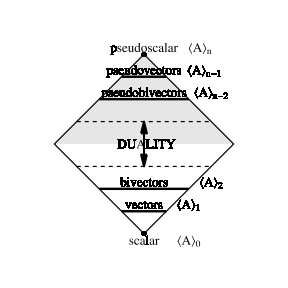
-Graphics-
Duality scheme in geometric algebra

The  vector  has a dual vector  called pseudovector etc. In general, any MV  has a dual MV (aka Hodge star) denoted as   

.

Equality of binomial coefficients  implies that the number of linearly independent elements in  and  is the same. From this follows that, in principle,  the description of GA requires only half of all grades. The other half can be recovered from the duality property. Double application of the Hodge star returns the initial MV either with  plus sign (when  is even), or with minus sign (when  is odd). This implies that Hodge star operation in general is not an involution (it may be written as involution in some of Clifford algebras). 
There are multiple definitions of the Hodge star in GA literature. For example, some authors defines it as  or . All of them differ by signs only.

Hodge star. In  the multivector dual to bivector  is a vector . Indeed, . Applying  the Hodge star twice we find . It means that  algebra elements can be written in the following more symmetric and agreeable manner, . Different ordering  and signs of basis elements in the new basis should be
noted (lexicographical ordering is routinely used in the Handbook).

Computational verification

Choose algebra

```mathematica
testAlgebra=Cl[3,0];
gaDefineOrthonormalBasis[testAlgebra,Quiet->False]
```

Basis vectors are stored in   gaOrthonormalBasis[300,InvDeg[Lex]]

Running algebra is: gaRunningAlgebra=  300

{1,1300,2300,3300,12300,13300,23300,123300}

Hodge dual

```mathematica
gaHodgeDual[𝕖[1,2],Method->"MVInverseI"]
```

3300

```mathematica
gaHodgeDual[gaHodgeDual[𝕖[1,2],Method->"MVInverseI"],Method->"MVInverseI"]
```

-12300

```mathematica
ClearAll[{testAlgebra}];
```

## Involutions and conjugation

Section.Item	Main GA involutions.  The (anti-)involution (aka (anti-)involutory function) , satisfies the equation , i.e.,  the operation applied twice returns the initial argument. In other words, operation  is its own   inverse. In GA there are four main or fundamental  (anti-)involutions: identity id,  reversion , grade inversion , and Clifford conjugation . The identity involution (id),  as the name implies, leaves the MV unchanged: . The properties of other involutions are discussed below.  The listed four main involutions constitute a group of four also called F. Klein group that is isomorphic to physical space (aka Galileo space) symmetry group , where  is the space inversion (aka parity),  is the time reversal and  is their combination. When the algebra dimension is not large the listed main involutions suffice to do all calculations. Actually, if needed, as the Table shows, the main involutions may be extended  to grade-7 including. The main involutions remain in higher dimensions too, however, for grades  new involutions appear (see the Table).

Computational verification

Choose algebra and generate general MV

```mathematica
testAlgebra=Cl[3,1];
gaDefineOrthonormalBasis[testAlgebra];
generalMV=gaGeneralMultivector[a,testAlgebra]
```

Running algebra is: gaRunningAlgebra=  310

a[0]+a[1] 1310+a[2] 2310+a[3] 3310+a[4] 4310+a[5] 12310+a[6] 13310+a[7] 14310+a[8] 23310+a[9] 24310+a[10] 34310+a[11] 123310+a[12] 124310+a[13] 134310+a[14] 234310+a[15] 1234310

Main involution or grade inversion  , changes signs of odd elements, for example

```mathematica
generalMV
gaGradeInverse[%]
```

a[0]+a[1] 1310+a[2] 2310+a[3] 3310+a[4] 4310+a[5] 12310+a[6] 13310+a[7] 14310+a[8] 23310+a[9] 24310+a[10] 34310+a[11] 123310+a[12] 124310+a[13] 134310+a[14] 234310+a[15] 1234310

a[0]-a[1] 1310-a[2] 2310-a[3] 3310-a[4] 4310+a[5] 12310+a[6] 13310+a[7] 14310+a[8] 23310+a[9] 24310+a[10] 34310-a[11] 123310-a[12] 124310-a[13] 134310-a[14] 234310+a[15] 1234310

Reverse of the multivector is obtained with gaReverse[ ]. It is an anti-involution, which reverses order of products in the  multivector

```mathematica
generalMV
gaReverse[%]
```

a[0]+a[1] 1310+a[2] 2310+a[3] 3310+a[4] 4310+a[5] 12310+a[6] 13310+a[7] 14310+a[8] 23310+a[9] 24310+a[10] 34310+a[11] 123310+a[12] 124310+a[13] 134310+a[14] 234310+a[15] 1234310

a[0]+a[1] 1310+a[2] 2310+a[3] 3310+a[4] 4310-a[5] 12310-a[6] 13310-a[7] 14310-a[8] 23310-a[9] 24310-a[10] 34310-a[11] 123310-a[12] 124310-a[13] 134310-a[14] 234310+a[15] 1234310

Clifford conjugation is an anti-involution, which is a product of grade inversion and reversion.

```mathematica
generalMV
gaCliffordConjugate[%]
```

a[0]+a[1] 1310+a[2] 2310+a[3] 3310+a[4] 4310+a[5] 12310+a[6] 13310+a[7] 14310+a[8] 23310+a[9] 24310+a[10] 34310+a[11] 123310+a[12] 124310+a[13] 134310+a[14] 234310+a[15] 1234310

a[0]-a[1] 1310-a[2] 2310-a[3] 3310-a[4] 4310-a[5] 12310-a[6] 13310-a[7] 14310-a[8] 23310-a[9] 24310-a[10] 34310+a[11] 123310+a[12] 124310+a[13] 134310+a[14] 234310+a[15] 1234310

Below is a check from Lounesto “Counter examples in Clifford algebras”, which demonstrates that in the geometric product of two multivectors  one cannot move Clifford conjugation from one factor to the other. He uses  algebra

```mathematica
gaDefineOrthonormalBasis[Cl[3,1]]
```

Running algebra is: gaRunningAlgebra=  310

{1,1310,2310,3310,4310,12310,13310,14310,23310,24310,34310,123310,124310,134310,234310,1234310}

2022-11-26, we removed gaCliffordConjugate[ ] rule for geometric product of MV.  This rule was not valid in curvilinear spaces.

```mathematica
aa1=( 1+𝕖[1])\[GeometricProduct]( 1+𝕖[2,3,4]);
counterExample={gaCliffordConjugate[aa1]\[GeometricProduct]aa1,aa1\[GeometricProduct]gaCliffordConjugate[aa1]}
```

{gaCliffordConjugate[(1+1310)\[GeometricProduct](1+234310)]\[GeometricProduct](1+1310)\[GeometricProduct](1+234310),(1+1310)\[GeometricProduct](1+234310)\[GeometricProduct]gaCliffordConjugate[(1+1310)\[GeometricProduct](1+234310)]}

After expansion we see that indeed both results differ

```mathematica
counterExample//gaPE
```

{0,4 234310+4 1234310}

```mathematica
ClearAll[{generalMV,aa1,counterExample}];
```

Section.Item	Reversion.  It reverses the order of vectors in GP, for example, , and, therefore, the reversion is an anti-involution. In the literature, instead of tilde the dagger symbol  is
used sometimes. In the Handbook, the dagger symbol is preserved for complex GAs.

Properties of reversion[pakeista blade-> homogeneus grade-r]



In real Euclidean  GA , the reversion is an analogue of a matrix transposition. In complex Euclidean GA it is analogue of Hermitian conjugation of a matrix. In non-Euclidean vector spaces the matrix transposition (and Hermitian conjugation) requires some additional GA conjugations (see explicit formulas below).

Computational verification

Choose algebra and generate general MV

```mathematica
testAlgebra=Cl[3,2];
gaDefineOrthonormalBasis[testAlgebra];
generalMV=gaGeneralMultivector[a,testAlgebra]
```

Running algebra is: gaRunningAlgebra=  320

a[0]+a[1] 1320+a[2] 2320+a[3] 3320+a[4] 4320+a[5] 5320+a[6] 12320+a[7] 13320+a[8] 14320+a[9] 15320+a[10] 23320+a[11] 24320+a[12] 25320+a[13] 34320+a[14] 35320+a[15] 45320+a[16] 123320+a[17] 124320+a[18] 125320+a[19] 134320+a[20] 135320+a[21] 145320+a[22] 234320+a[23] 235320+a[24] 245320+a[25] 345320+a[26] 1234320+a[27] 1235320+a[28] 1245320+a[29] 1345320+a[30] 2345320+a[31] 12345320

1)

```mathematica
gaGetMV[generalMV,{0}]
gaReverse[%]
```

a[0]

a[0]

```mathematica
gaGetMV[generalMV,{1}]
gaReverse[%]
```

a[1] 1320+a[2] 2320+a[3] 3320+a[4] 4320+a[5] 5320

a[1] 1320+a[2] 2320+a[3] 3320+a[4] 4320+a[5] 5320

2)

Define function to produce different vectors

```mathematica
mV[s_Symbol]:=gaGeneralMultivector[s,testAlgebra,{1}]
```

Make product of as many vectors as you wish, here 5

```mathematica
productOfVectors=GeometricProduct@@(mV/@ToExpression[Table[FromCharacterCode[i],{i,97,102}]])
```

(a[1] 1320+a[2] 2320+a[3] 3320+a[4] 4320+a[5] 5320)\[GeometricProduct](b[1] 1320+b[2] 2320+b[3] 3320+b[4] 4320+b[5] 5320)\[GeometricProduct](c[1] 1320+c[2] 2320+c[3] 3320+c[4] 4320+c[5] 5320)\[GeometricProduct](d[1] 1320+d[2] 2320+d[3] 3320+d[4] 4320+d[5] 5320)\[GeometricProduct](e[1] 1320+e[2] 2320+e[3] 3320+e[4] 4320+e[5] 5320)\[GeometricProduct](f[1] 1320+f[2] 2320+f[3] 3320+f[4] 4320+f[5] 5320)

```mathematica
lhs[testAlgebra]=gaReverse[productOfVectors]
```

gaReverse[(a[1] 1320+a[2] 2320+a[3] 3320+a[4] 4320+a[5] 5320)\[GeometricProduct](b[1] 1320+b[2] 2320+b[3] 3320+b[4] 4320+b[5] 5320)\[GeometricProduct](c[1] 1320+c[2] 2320+c[3] 3320+c[4] 4320+c[5] 5320)\[GeometricProduct](d[1] 1320+d[2] 2320+d[3] 3320+d[4] 4320+d[5] 5320)\[GeometricProduct](e[1] 1320+e[2] 2320+e[3] 3320+e[4] 4320+e[5] 5320)\[GeometricProduct](f[1] 1320+f[2] 2320+f[3] 3320+f[4] 4320+f[5] 5320)]

```mathematica
rhs[testAlgebra]=Reverse[productOfVectors]
```

(f[1] 1320+f[2] 2320+f[3] 3320+f[4] 4320+f[5] 5320)\[GeometricProduct](e[1] 1320+e[2] 2320+e[3] 3320+e[4] 4320+e[5] 5320)\[GeometricProduct](d[1] 1320+d[2] 2320+d[3] 3320+d[4] 4320+d[5] 5320)\[GeometricProduct](c[1] 1320+c[2] 2320+c[3] 3320+c[4] 4320+c[5] 5320)\[GeometricProduct](b[1] 1320+b[2] 2320+b[3] 3320+b[4] 4320+b[5] 5320)\[GeometricProduct](a[1] 1320+a[2] 2320+a[3] 3320+a[4] 4320+a[5] 5320)

```mathematica
lhs[testAlgebra]-rhs[testAlgebra]//gaPE//Expand//AbsoluteTiming
```

{1.43889,0}

If you will make more vectors, then geometric product expansion can take quite long time. You can make expansion much faster if you will convert it to Mathematica’s internal Association form (even taking into account  that conversion takes time):

```mathematica
gaAssociationRepresentation[lhs[testAlgebra]-rhs[testAlgebra]]//gaPE//Expand//AbsoluteTiming
```

gaAssociationRepresentation::notcompleted: Warning! Unable to check if conversion to Association was successfull. Your can avoid the check using option Check->False. The last step was ….

gaAssociationRepresentation::notcompleted: Warning! Unable to check if conversion to Association was successfull. Your can avoid the check using option Check->False. The last step was 0.

{0.465447,0}

3)   In fact this is an action on homogeneous MV

```mathematica
testGrade=3;
gaGetMV[generalMV,{testGrade}]
```

a[16] 123320+a[17] 124320+a[18] 125320+a[19] 134320+a[20] 135320+a[21] 145320+a[22] 234320+a[23] 235320+a[24] 245320+a[25] 345320

```mathematica
lhs[testAlgebra]=gaReverse[gaGetMV[generalMV,{testGrade}]]
```

-a[16] 123320-a[17] 124320-a[18] 125320-a[19] 134320-a[20] 135320-a[21] 145320-a[22] 234320-a[23] 235320-a[24] 245320-a[25] 345320

```mathematica
rhs[testAlgebra]=(-1)^(testGrade*(testGrade-1)/2)gaGetMV[generalMV,{testGrade}]
```

-a[16] 123320-a[17] 124320-a[18] 125320-a[19] 134320-a[20] 135320-a[21] 145320-a[22] 234320-a[23] 235320-a[24] 245320-a[25] 345320

```mathematica
lhs[testAlgebra]-rhs[testAlgebra]//gaPE//Expand
```

0

4) ,   5) is trivial, omitted

```mathematica
testGrade=3;
lhs[testAlgebra]=gaReverse[gaGetMV[generalMV,{testGrade}]]
```

-a[16] 123320-a[17] 124320-a[18] 125320-a[19] 134320-a[20] 135320-a[21] 145320-a[22] 234320-a[23] 235320-a[24] 245320-a[25] 345320

```mathematica
rhs[testAlgebra]=gaGetMV[gaReverse[generalMV],{testGrade}]
```

-a[16] 123320-a[17] 124320-a[18] 125320-a[19] 134320-a[20] 135320-a[21] 145320-a[22] 234320-a[23] 235320-a[24] 245320-a[25] 345320

```mathematica
lhs[testAlgebra]-rhs[testAlgebra]//gaPE//Expand
```

0

6 )   . This property is also true  in curved space (to check).

```mathematica
lhs[testAlgebra]=gaReverse[generalMV\[OuterProduct]gaGeneralMultivector[b,testAlgebra]]
```

(b[0]+b[1] 1320+b[2] 2320+b[3] 3320+b[4] 4320+b[5] 5320-b[6] 12320-b[7] 13320-b[8] 14320-b[9] 15320-b[10] 23320-b[11] 24320-b[12] 25320-b[13] 34320-b[14] 35320-b[15] 45320-b[16] 123320-b[17] 124320-b[18] 125320-b[19] 134320-b[20] 135320-b[21] 145320-b[22] 234320-b[23] 235320-b[24] 245320-b[25] 345320+b[26] 1234320+b[27] 1235320+b[28] 1245320+b[29] 1345320+b[30] 2345320+b[31] 12345320)\[OuterProduct](a[0]+a[1] 1320+a[2] 2320+a[3] 3320+a[4] 4320+a[5] 5320-a[6] 12320-a[7] 13320-a[8] 14320-a[9] 15320-a[10] 23320-a[11] 24320-a[12] 25320-a[13] 34320-a[14] 35320-a[15] 45320-a[16] 123320-a[17] 124320-a[18] 125320-a[19] 134320-a[20] 135320-a[21] 145320-a[22] 234320-a[23] 235320-a[24] 245320-a[25] 345320+a[26] 1234320+a[27] 1235320+a[28] 1245320+a[29] 1345320+a[30] 2345320+a[31] 12345320)

```mathematica
rhs[testAlgebra]=gaReverse[gaGeneralMultivector[b,testAlgebra]]\[OuterProduct]gaReverse[generalMV]
```

(b[0]+b[1] 1320+b[2] 2320+b[3] 3320+b[4] 4320+b[5] 5320-b[6] 12320-b[7] 13320-b[8] 14320-b[9] 15320-b[10] 23320-b[11] 24320-b[12] 25320-b[13] 34320-b[14] 35320-b[15] 45320-b[16] 123320-b[17] 124320-b[18] 125320-b[19] 134320-b[20] 135320-b[21] 145320-b[22] 234320-b[23] 235320-b[24] 245320-b[25] 345320+b[26] 1234320+b[27] 1235320+b[28] 1245320+b[29] 1345320+b[30] 2345320+b[31] 12345320)\[OuterProduct](a[0]+a[1] 1320+a[2] 2320+a[3] 3320+a[4] 4320+a[5] 5320-a[6] 12320-a[7] 13320-a[8] 14320-a[9] 15320-a[10] 23320-a[11] 24320-a[12] 25320-a[13] 34320-a[14] 35320-a[15] 45320-a[16] 123320-a[17] 124320-a[18] 125320-a[19] 134320-a[20] 135320-a[21] 145320-a[22] 234320-a[23] 235320-a[24] 245320-a[25] 345320+a[26] 1234320+a[27] 1235320+a[28] 1245320+a[29] 1345320+a[30] 2345320+a[31] 12345320)

```mathematica
lhs[testAlgebra]-rhs[testAlgebra]//gaPE//Expand
```

0

7 )   . This property is valid only in flat space, therefore expansion of gaReverse don’t happen automatically.

```mathematica
lhs[testAlgebra]=gaReverse[generalMV\[GeometricProduct]gaGeneralMultivector[b,testAlgebra]]
```

gaReverse[(a[0]+a[1] 1320+a[2] 2320+a[3] 3320+a[4] 4320+a[5] 5320+a[6] 12320+a[7] 13320+a[8] 14320+a[9] 15320+a[10] 23320+a[11] 24320+a[12] 25320+a[13] 34320+a[14] 35320+a[15] 45320+a[16] 123320+a[17] 124320+a[18] 125320+a[19] 134320+a[20] 135320+a[21] 145320+a[22] 234320+a[23] 235320+a[24] 245320+a[25] 345320+a[26] 1234320+a[27] 1235320+a[28] 1245320+a[29] 1345320+a[30] 2345320+a[31] 12345320)\[GeometricProduct](b[0]+b[1] 1320+b[2] 2320+b[3] 3320+b[4] 4320+b[5] 5320+b[6] 12320+b[7] 13320+b[8] 14320+b[9] 15320+b[10] 23320+b[11] 24320+b[12] 25320+b[13] 34320+b[14] 35320+b[15] 45320+b[16] 123320+b[17] 124320+b[18] 125320+b[19] 134320+b[20] 135320+b[21] 145320+b[22] 234320+b[23] 235320+b[24] 245320+b[25] 345320+b[26] 1234320+b[27] 1235320+b[28] 1245320+b[29] 1345320+b[30] 2345320+b[31] 12345320)]

```mathematica
rhs[testAlgebra]=gaReverse[gaGeneralMultivector[b,testAlgebra]]\[GeometricProduct]gaReverse[generalMV]
```

(b[0]+b[1] 1320+b[2] 2320+b[3] 3320+b[4] 4320+b[5] 5320-b[6] 12320-b[7] 13320-b[8] 14320-b[9] 15320-b[10] 23320-b[11] 24320-b[12] 25320-b[13] 34320-b[14] 35320-b[15] 45320-b[16] 123320-b[17] 124320-b[18] 125320-b[19] 134320-b[20] 135320-b[21] 145320-b[22] 234320-b[23] 235320-b[24] 245320-b[25] 345320+b[26] 1234320+b[27] 1235320+b[28] 1245320+b[29] 1345320+b[30] 2345320+b[31] 12345320)\[GeometricProduct](a[0]+a[1] 1320+a[2] 2320+a[3] 3320+a[4] 4320+a[5] 5320-a[6] 12320-a[7] 13320-a[8] 14320-a[9] 15320-a[10] 23320-a[11] 24320-a[12] 25320-a[13] 34320-a[14] 35320-a[15] 45320-a[16] 123320-a[17] 124320-a[18] 125320-a[19] 134320-a[20] 135320-a[21] 145320-a[22] 234320-a[23] 235320-a[24] 245320-a[25] 345320+a[26] 1234320+a[27] 1235320+a[28] 1245320+a[29] 1345320+a[30] 2345320+a[31] 12345320)

```mathematica
lhs[testAlgebra]-rhs[testAlgebra]//gaPE//Expand
```

0

8 )   .

```mathematica
lhs[testAlgebra]=gaGetMV[gaReverse[generalMV]\[GeometricProduct]gaReverse[gaGeneralMultivector[b,testAlgebra]],{0}]
```

a[0] b[0]+a[1] b[1]+a[2] b[2]+a[3] b[3]-a[4] b[4]-a[5] b[5]-a[6] b[6]-a[7] b[7]+a[8] b[8]+a[9] b[9]-a[10] b[10]+a[11] b[11]+a[12] b[12]+a[13] b[13]+a[14] b[14]-a[15] b[15]-a[16] b[16]+a[17] b[17]+a[18] b[18]+a[19] b[19]+a[20] b[20]-a[21] b[21]+a[22] b[22]+a[23] b[23]-a[24] b[24]-a[25] b[25]-a[26] b[26]-a[27] b[27]+a[28] b[28]+a[29] b[29]+a[30] b[30]+a[31] b[31]

```mathematica
rhs[testAlgebra]=gaGetMV[generalMV\[GeometricProduct]gaGeneralMultivector[b,testAlgebra],{0}]
```

a[0] b[0]+a[1] b[1]+a[2] b[2]+a[3] b[3]-a[4] b[4]-a[5] b[5]-a[6] b[6]-a[7] b[7]+a[8] b[8]+a[9] b[9]-a[10] b[10]+a[11] b[11]+a[12] b[12]+a[13] b[13]+a[14] b[14]-a[15] b[15]-a[16] b[16]+a[17] b[17]+a[18] b[18]+a[19] b[19]+a[20] b[20]-a[21] b[21]+a[22] b[22]+a[23] b[23]-a[24] b[24]-a[25] b[25]-a[26] b[26]-a[27] b[27]+a[28] b[28]+a[29] b[29]+a[30] b[30]+a[31] b[31]

```mathematica
lhs[testAlgebra]-rhs[testAlgebra]//gaPE//Expand
```

0

```mathematica
ClearAll[{generalMV,lhs,rhs,testGrade,productOfVectors}];
```

Reversion example. If applied to   and , where ℝ, the reversion may change or not the sign of the r-vector,

Computational verification

Choose algebra and generate general MV

```mathematica
testAlgebra=Cl[3,2];
gaDefineOrthonormalBasis[testAlgebra];
generalMV=gaGeneralMultivector[a,testAlgebra]
```

Running algebra is: gaRunningAlgebra=  320

a[0]+a[1] 1320+a[2] 2320+a[3] 3320+a[4] 4320+a[5] 5320+a[6] 12320+a[7] 13320+a[8] 14320+a[9] 15320+a[10] 23320+a[11] 24320+a[12] 25320+a[13] 34320+a[14] 35320+a[15] 45320+a[16] 123320+a[17] 124320+a[18] 125320+a[19] 134320+a[20] 135320+a[21] 145320+a[22] 234320+a[23] 235320+a[24] 245320+a[25] 345320+a[26] 1234320+a[27] 1235320+a[28] 1245320+a[29] 1345320+a[30] 2345320+a[31] 12345320

1)

```mathematica
gaGetMV[generalMV,{1}]
gaReverse[%]
```

a[1] 1320+a[2] 2320+a[3] 3320+a[4] 4320+a[5] 5320

a[1] 1320+a[2] 2320+a[3] 3320+a[4] 4320+a[5] 5320

2) . It is reverse of bivector

```mathematica
β*𝕖[1,3]
gaReverse[%]
```

β 13320

-β 13320

3)   It is reverse of bivector

```mathematica
γ*𝕖[1,2,3]
gaReverse[%]
```

γ 123320

-γ 123320

4) .

```mathematica
lhsInput[testAlgebra]=γ*𝕖[1,2,3]+gaGetMV[generalMV,{1}]\[GeometricProduct]β\[GeometricProduct]𝕖[1,3]
```

β ((a[1] 1320+a[2] 2320+a[3] 3320+a[4] 4320+a[5] 5320)\[GeometricProduct]13320)+γ 123320

```mathematica
lhs[testAlgebra]=gaReverse[lhsInput[testAlgebra]]//gaPE//Expand
```

-β a[3] 1320+β a[1] 3320-γ 123320+β a[2] 123320-β a[4] 134320-β a[5] 135320

```mathematica
rhs[testAlgebra]=-γ*𝕖[1,2,3]-β*𝕖[1,3]\[GeometricProduct]gaGetMV[generalMV,{1}]
```

-β (13320\[GeometricProduct](a[1] 1320+a[2] 2320+a[3] 3320+a[4] 4320+a[5] 5320))-γ 123320

```mathematica
lhs[testAlgebra]-rhs[testAlgebra]//gaPE//Expand
```

0

```mathematica
ClearAll[{generalMV,lhsInput,lhs,rhs}];
```

Section.Item	Grade inversion (aka parity involution).  It changes sign of all basis vectors to opposite, . The grade inversion does not change order of its arguments, for example, ,therefore, it is true involution (not anti-involution) with the properties: [pakeista blade-> homogeneus grade-r]



The grade inversion may be applied to eliminate the factors  in expressions that hold blades. For example,

Computational verification

Choose algebra and generate general MV

```mathematica
testAlgebra=Cl[3,2];
gaDefineOrthonormalBasis[testAlgebra];
generalMV=gaGeneralMultivector[a,testAlgebra]
```

Running algebra is: gaRunningAlgebra=  320

a[0]+a[1] 1320+a[2] 2320+a[3] 3320+a[4] 4320+a[5] 5320+a[6] 12320+a[7] 13320+a[8] 14320+a[9] 15320+a[10] 23320+a[11] 24320+a[12] 25320+a[13] 34320+a[14] 35320+a[15] 45320+a[16] 123320+a[17] 124320+a[18] 125320+a[19] 134320+a[20] 135320+a[21] 145320+a[22] 234320+a[23] 235320+a[24] 245320+a[25] 345320+a[26] 1234320+a[27] 1235320+a[28] 1245320+a[29] 1345320+a[30] 2345320+a[31] 12345320

1)

```mathematica
gaGetMV[generalMV,{1}]
gaGradeInverse[%]
```

a[1] 1320+a[2] 2320+a[3] 3320+a[4] 4320+a[5] 5320

-a[1] 1320-a[2] 2320-a[3] 3320-a[4] 4320-a[5] 5320

2)   In fact this is an action on homogeneous MV

```mathematica
testGrade=3;
gaGetMV[generalMV,{testGrade}]
```

a[16] 123320+a[17] 124320+a[18] 125320+a[19] 134320+a[20] 135320+a[21] 145320+a[22] 234320+a[23] 235320+a[24] 245320+a[25] 345320

```mathematica
lhs[testAlgebra]=gaGradeInverse[gaGetMV[generalMV,{testGrade}]]
```

-a[16] 123320-a[17] 124320-a[18] 125320-a[19] 134320-a[20] 135320-a[21] 145320-a[22] 234320-a[23] 235320-a[24] 245320-a[25] 345320

```mathematica
rhs[testAlgebra]=(-1)^(testGrade)gaGetMV[generalMV,{testGrade}]
```

-a[16] 123320-a[17] 124320-a[18] 125320-a[19] 134320-a[20] 135320-a[21] 145320-a[22] 234320-a[23] 235320-a[24] 245320-a[25] 345320

```mathematica
lhs[testAlgebra]-rhs[testAlgebra]//gaPE//Expand
```

0

4) ,   5) is trivial, omitted

```mathematica
testGrade=3;
lhs[testAlgebra]=gaGradeInverse[gaGetMV[generalMV,{testGrade}]]
```

-a[16] 123320-a[17] 124320-a[18] 125320-a[19] 134320-a[20] 135320-a[21] 145320-a[22] 234320-a[23] 235320-a[24] 245320-a[25] 345320

```mathematica
rhs[testAlgebra]=gaGetMV[gaGradeInverse[generalMV],{testGrade}]
```

-a[16] 123320-a[17] 124320-a[18] 125320-a[19] 134320-a[20] 135320-a[21] 145320-a[22] 234320-a[23] 235320-a[24] 245320-a[25] 345320

```mathematica
lhs[testAlgebra]-rhs[testAlgebra]//gaPE//Expand
```

0

6 )   . This means that grade inverse  is true involution

```mathematica
(lhs[testAlgebra]=gaGradeInverse[gaPE[generalMV\[GeometricProduct]gaGeneralMultivector[b,testAlgebra]]])//LeafCount
```

6007

```mathematica
rhs[testAlgebra]=gaGradeInverse[generalMV]\[GeometricProduct]gaGradeInverse[gaGeneralMultivector[b,testAlgebra]]
```

(a[0]-a[1] 1320-a[2] 2320-a[3] 3320-a[4] 4320-a[5] 5320+a[6] 12320+a[7] 13320+a[8] 14320+a[9] 15320+a[10] 23320+a[11] 24320+a[12] 25320+a[13] 34320+a[14] 35320+a[15] 45320-a[16] 123320-a[17] 124320-a[18] 125320-a[19] 134320-a[20] 135320-a[21] 145320-a[22] 234320-a[23] 235320-a[24] 245320-a[25] 345320+a[26] 1234320+a[27] 1235320+a[28] 1245320+a[29] 1345320+a[30] 2345320-a[31] 12345320)\[GeometricProduct](b[0]-b[1] 1320-b[2] 2320-b[3] 3320-b[4] 4320-b[5] 5320+b[6] 12320+b[7] 13320+b[8] 14320+b[9] 15320+b[10] 23320+b[11] 24320+b[12] 25320+b[13] 34320+b[14] 35320+b[15] 45320-b[16] 123320-b[17] 124320-b[18] 125320-b[19] 134320-b[20] 135320-b[21] 145320-b[22] 234320-b[23] 235320-b[24] 245320-b[25] 345320+b[26] 1234320+b[27] 1235320+b[28] 1245320+b[29] 1345320+b[30] 2345320-b[31] 12345320)

```mathematica
lhs[testAlgebra]-rhs[testAlgebra]//gaPE//Expand
```

0

```mathematica
ClearAll[{generalMV,lhs,rhs,testGrade}];
```

Grade inversions example.  I  If ,  and , where ℝ, then

Computational verification

Choose algebra and generate general MV

```mathematica
testAlgebra=Cl[3,2];
gaDefineOrthonormalBasis[testAlgebra];
generalMV=gaGeneralMultivector[a,testAlgebra]
```

Running algebra is: gaRunningAlgebra=  320

a[0]+a[1] 1320+a[2] 2320+a[3] 3320+a[4] 4320+a[5] 5320+a[6] 12320+a[7] 13320+a[8] 14320+a[9] 15320+a[10] 23320+a[11] 24320+a[12] 25320+a[13] 34320+a[14] 35320+a[15] 45320+a[16] 123320+a[17] 124320+a[18] 125320+a[19] 134320+a[20] 135320+a[21] 145320+a[22] 234320+a[23] 235320+a[24] 245320+a[25] 345320+a[26] 1234320+a[27] 1235320+a[28] 1245320+a[29] 1345320+a[30] 2345320+a[31] 12345320

1) and 2)

```mathematica
gaGetMV[generalMV,{1}]
gaGradeInverse[%]
```

a[1] 1320+a[2] 2320+a[3] 3320+a[4] 4320+a[5] 5320

-a[1] 1320-a[2] 2320-a[3] 3320-a[4] 4320-a[5] 5320

```mathematica
β*𝕖[1,3]
gaGradeInverse[%]
```

β 13320

β 13320

3)   It is a grade inverse  of bivector

```mathematica
γ*𝕖[1,2,3]
gaGradeInverse[%]
```

γ 123320

-γ 123320

4) .

```mathematica
lhsInput[testAlgebra]=γ*𝕖[1,2,3]+gaGetMV[generalMV,{1}]\[GeometricProduct]β\[GeometricProduct]𝕖[1,3]
```

β ((a[1] 1320+a[2] 2320+a[3] 3320+a[4] 4320+a[5] 5320)\[GeometricProduct]13320)+γ 123320

```mathematica
(lhs[testAlgebra]=gaGradeInverse[lhsInput[testAlgebra]//gaPE]//gaPE//Expand)
```

β a[3] 1320-β a[1] 3320-γ 123320+β a[2] 123320-β a[4] 134320-β a[5] 135320

```mathematica
rhs[testAlgebra]=-γ*𝕖[1,2,3]-gaGetMV[generalMV,{1}]\[GeometricProduct]β\[GeometricProduct]𝕖[1,3]
```

-β ((a[1] 1320+a[2] 2320+a[3] 3320+a[4] 4320+a[5] 5320)\[GeometricProduct]13320)-γ 123320

```mathematica
lhs[testAlgebra]-rhs[testAlgebra]//gaPE//Expand
```

0

```mathematica
ClearAll[{generalMV,lhsInput,lhs,rhs}];
```

Section.Item	Clifford conjugation.  It is a combination of the grade inversion and reversion. Because under grade inversion  the order of arguments  changes the operation is the anti-involution.

Properties of Clifford conjugation



For example, if  then the Clifford conjugation is calculated as .  In the future we will not distinguish the involution from anti-involution, and all of them will be called collectively the involutions.

Computational verification

Choose algebra and generate general MV

```mathematica
testAlgebra=Cl[3,2];
gaDefineOrthonormalBasis[testAlgebra];
generalMV=gaGeneralMultivector[a,testAlgebra]
```

Running algebra is: gaRunningAlgebra=  320

a[0]+a[1] 1320+a[2] 2320+a[3] 3320+a[4] 4320+a[5] 5320+a[6] 12320+a[7] 13320+a[8] 14320+a[9] 15320+a[10] 23320+a[11] 24320+a[12] 25320+a[13] 34320+a[14] 35320+a[15] 45320+a[16] 123320+a[17] 124320+a[18] 125320+a[19] 134320+a[20] 135320+a[21] 145320+a[22] 234320+a[23] 235320+a[24] 245320+a[25] 345320+a[26] 1234320+a[27] 1235320+a[28] 1245320+a[29] 1345320+a[30] 2345320+a[31] 12345320

1)

```mathematica
gaGetMV[generalMV,{0}]
gaCliffordConjugate[%]
```

a[0]

a[0]

```mathematica
gaGetMV[generalMV,{1}]
gaCliffordConjugate[%]
```

a[1] 1320+a[2] 2320+a[3] 3320+a[4] 4320+a[5] 5320

-a[1] 1320-a[2] 2320-a[3] 3320-a[4] 4320-a[5] 5320

2)   In fact this is an action on homogeneous MV

```mathematica
testGrade=3;
gaGetMV[generalMV,{testGrade}]
```

a[16] 123320+a[17] 124320+a[18] 125320+a[19] 134320+a[20] 135320+a[21] 145320+a[22] 234320+a[23] 235320+a[24] 245320+a[25] 345320

```mathematica
lhs[testAlgebra]=gaCliffordConjugate[gaGetMV[generalMV,{testGrade}]]
```

a[16] 123320+a[17] 124320+a[18] 125320+a[19] 134320+a[20] 135320+a[21] 145320+a[22] 234320+a[23] 235320+a[24] 245320+a[25] 345320

```mathematica
rhs[testAlgebra]=(-1)^(testGrade*(testGrade+1)/2)gaGetMV[generalMV,{testGrade}]
```

a[16] 123320+a[17] 124320+a[18] 125320+a[19] 134320+a[20] 135320+a[21] 145320+a[22] 234320+a[23] 235320+a[24] 245320+a[25] 345320

```mathematica
lhs[testAlgebra]-rhs[testAlgebra]//gaPE//Expand
```

0

3) ,   4) is trivial, omitted

```mathematica
testGrade=3;
lhs[testAlgebra]=gaCliffordConjugate[gaGetMV[generalMV,{testGrade}]]
```

a[16] 123320+a[17] 124320+a[18] 125320+a[19] 134320+a[20] 135320+a[21] 145320+a[22] 234320+a[23] 235320+a[24] 245320+a[25] 345320

```mathematica
rhs[testAlgebra]=gaGetMV[gaCliffordConjugate[generalMV],{testGrade}]
```

a[16] 123320+a[17] 124320+a[18] 125320+a[19] 134320+a[20] 135320+a[21] 145320+a[22] 234320+a[23] 235320+a[24] 245320+a[25] 345320

```mathematica
lhs[testAlgebra]-rhs[testAlgebra]//gaPE//Expand
```

0

5 )   .

```mathematica
lhs[testAlgebra]=gaCliffordConjugate[generalMV\[GeometricProduct]gaGeneralMultivector[b,testAlgebra]]
```

gaCliffordConjugate[(a[0]+a[1] 1320+a[2] 2320+a[3] 3320+a[4] 4320+a[5] 5320+a[6] 12320+a[7] 13320+a[8] 14320+a[9] 15320+a[10] 23320+a[11] 24320+a[12] 25320+a[13] 34320+a[14] 35320+a[15] 45320+a[16] 123320+a[17] 124320+a[18] 125320+a[19] 134320+a[20] 135320+a[21] 145320+a[22] 234320+a[23] 235320+a[24] 245320+a[25] 345320+a[26] 1234320+a[27] 1235320+a[28] 1245320+a[29] 1345320+a[30] 2345320+a[31] 12345320)\[GeometricProduct](b[0]+b[1] 1320+b[2] 2320+b[3] 3320+b[4] 4320+b[5] 5320+b[6] 12320+b[7] 13320+b[8] 14320+b[9] 15320+b[10] 23320+b[11] 24320+b[12] 25320+b[13] 34320+b[14] 35320+b[15] 45320+b[16] 123320+b[17] 124320+b[18] 125320+b[19] 134320+b[20] 135320+b[21] 145320+b[22] 234320+b[23] 235320+b[24] 245320+b[25] 345320+b[26] 1234320+b[27] 1235320+b[28] 1245320+b[29] 1345320+b[30] 2345320+b[31] 12345320)]

```mathematica
rhs[testAlgebra]=gaCliffordConjugate[gaGeneralMultivector[b,testAlgebra]]\[GeometricProduct]gaCliffordConjugate[generalMV]
```

(b[0]-b[1] 1320-b[2] 2320-b[3] 3320-b[4] 4320-b[5] 5320-b[6] 12320-b[7] 13320-b[8] 14320-b[9] 15320-b[10] 23320-b[11] 24320-b[12] 25320-b[13] 34320-b[14] 35320-b[15] 45320+b[16] 123320+b[17] 124320+b[18] 125320+b[19] 134320+b[20] 135320+b[21] 145320+b[22] 234320+b[23] 235320+b[24] 245320+b[25] 345320+b[26] 1234320+b[27] 1235320+b[28] 1245320+b[29] 1345320+b[30] 2345320-b[31] 12345320)\[GeometricProduct](a[0]-a[1] 1320-a[2] 2320-a[3] 3320-a[4] 4320-a[5] 5320-a[6] 12320-a[7] 13320-a[8] 14320-a[9] 15320-a[10] 23320-a[11] 24320-a[12] 25320-a[13] 34320-a[14] 35320-a[15] 45320+a[16] 123320+a[17] 124320+a[18] 125320+a[19] 134320+a[20] 135320+a[21] 145320+a[22] 234320+a[23] 235320+a[24] 245320+a[25] 345320+a[26] 1234320+a[27] 1235320+a[28] 1245320+a[29] 1345320+a[30] 2345320-a[31] 12345320)

```mathematica
lhs[testAlgebra]-rhs[testAlgebra]//gaPE//Expand
```

0

Example of Clifford conjugate for trivector

```mathematica
𝕖[1,2,3]
gaCliffordConjugate[%]
```

123320

123320

```mathematica
ClearAll[{generalMV,lhs,rhs,testGrade}];
```

Section.Item	Main involutions, periodicity of four.  The action of four standard involutions on a general MV exhibits a repetitive pattern. The periodicity is summarized in the following table which is a part of a more extensive  table below.



Main conjugations. The plus and minus signs indicate that the action of conjugation  on the blade has either  no effect or changes its sign to opposite, for example reverse acts on bivector as  .

Computational verification

Choose algebra and generate general MV. Since we test graded up to grade-7,  vector space dimension should be 7 or greater in order to show 2 or more periods (repetition).

```mathematica
testAlgebra=Cl[3,4];
gaDefineOrthonormalBasis[testAlgebra];
generalMV=gaGeneralMultivector[a,testAlgebra]
```

Running algebra is: gaRunningAlgebra=  340

a[0]+a[1] 1340+a[2] 2340+a[3] 3340+a[4] 4340+a[5] 5340+a[6] 6340+a[7] 7340+a[8] 12340+a[9] 13340+a[10] 14340+a[11] 15340+a[12] 16340+a[13] 17340+a[14] 23340+a[15] 24340+a[16] 25340+a[17] 26340+a[18] 27340+a[19] 34340+a[20] 35340+a[21] 36340+a[22] 37340+a[23] 45340+a[24] 46340+a[25] 47340+a[26] 56340+a[27] 57340+a[28] 67340+a[29] 123340+a[30] 124340+a[31] 125340+a[32] 126340+a[33] 127340+a[34] 134340+a[35] 135340+a[36] 136340+a[37] 137340+a[38] 145340+a[39] 146340+a[40] 147340+a[41] 156340+a[42] 157340+a[43] 167340+a[44] 234340+a[45] 235340+a[46] 236340+a[47] 237340+a[48] 245340+a[49] 246340+a[50] 247340+a[51] 256340+a[52] 257340+a[53] 267340+a[54] 345340+a[55] 346340+a[56] 347340+a[57] 356340+a[58] 357340+a[59] 367340+a[60] 456340+a[61] 457340+a[62] 467340+a[63] 567340+a[64] 1234340+a[65] 1235340+a[66] 1236340+a[67] 1237340+a[68] 1245340+a[69] 1246340+a[70] 1247340+a[71] 1256340+a[72] 1257340+a[73] 1267340+a[74] 1345340+a[75] 1346340+a[76] 1347340+a[77] 1356340+a[78] 1357340+a[79] 1367340+a[80] 1456340+a[81] 1457340+a[82] 1467340+a[83] 1567340+a[84] 2345340+a[85] 2346340+a[86] 2347340+a[87] 2356340+a[88] 2357340+a[89] 2367340+a[90] 2456340+a[91] 2457340+a[92] 2467340+a[93] 2567340+a[94] 3456340+a[95] 3457340+a[96] 3467340+a[97] 3567340+a[98] 4567340+a[99] 12345340+a[100] 12346340+a[101] 12347340+a[102] 12356340+a[103] 12357340+a[104] 12367340+a[105] 12456340+a[106] 12457340+a[107] 12467340+a[108] 12567340+a[109] 13456340+a[110] 13457340+a[111] 13467340+a[112] 13567340+a[113] 14567340+a[114] 23456340+a[115] 23457340+a[116] 23467340+a[117] 23567340+a[118] 24567340+a[119] 34567340+a[120] 123456340+a[121] 123457340+a[122] 123467340+a[123] 123567340+a[124] 124567340+a[125] 134567340+a[126] 234567340+a[127] 1234567340

Make the above table.

```mathematica
TableForm[{Simplify[FactorTerms[(Identity[#]/#)]]&/@Table[gaGetMV[generalMV,{theGrade}],{theGrade,0,7}],
Simplify[FactorTerms[(gaReverse[#]/#)]]&/@Table[gaGetMV[generalMV,{theGrade}],{theGrade,0,7}],
Simplify[FactorTerms[(gaGradeInverse[#]/#)]]&/@Table[gaGetMV[generalMV,{theGrade}],{theGrade,0,7}],
Simplify[FactorTerms[(gaCliffordConjugate[#]/#)]]&/@Table[gaGetMV[generalMV,{theGrade}],{theGrade,0,7}]
}/.{1->"+",-1->"-"},TableHeadings->{{"id","reverse","grade inverse","Clifford conjugate"},Table[theGrade,{theGrade,0,7}]}]
```

| 0 | 1 | 2 | 3 | 4 | 5 | 6 | 7
id | + | + | + | + | + | + | + | +
reverse | + | + | - | - | + | + | - | -
grade inverse | + | - | + | - | + | - | + | -
Clifford conjugate | + | - | - | + | + | - | - | +

Short comment on the above code.  First we take corresponding grades. Then perform one of transformation and immediately divide answer by argument before transformation and cancel numerator with denominator (with Simplify). This yields either +1 or -1, which we replace by + or - respectively.  Note that since we know that answer after involution can differ only by sign we don’t need to find inverse of homogeneous MV (that would be a rather complicated task). Trick is to use ordinary division and simplify.

```mathematica
ClearAll[{generalMV}];
```

Action of main conjugations on MV  in 3D algebras.

Computational verification

Choose algebra and generate general MV of 3D algebra

```mathematica
testAlgebra=Cl[2,1];
gaDefineOrthonormalBasis[testAlgebra];
generalMV=gaGeneralMultivector[a,testAlgebra]
```

Basis vectors are stored in   gaOrthonormalBasis[210,InvDeg[Lex]]

Running algebra is: gaRunningAlgebra=  210

a[0]+a[1] 1210+a[2] 2210+a[3] 3210+a[4] 12210+a[5] 13210+a[6] 23210+a[7] 123210

Find  how all main involutions acts on the general MV

```mathematica
TableForm[{{Identity[generalMV]},{gaReverse[generalMV]},{gaGradeInverse[generalMV]},{gaCliffordConjugate[generalMV]}
},TableHeadings->{{"id","reverse","grade inverse","Clifford conjugate"},{}}]
```

| 
id | a[0]+a[1] 1210+a[2] 2210+a[3] 3210+a[4] 12210+a[5] 13210+a[6] 23210+a[7] 123210
reverse | a[0]+a[1] 1210+a[2] 2210+a[3] 3210-a[4] 12210-a[5] 13210-a[6] 23210-a[7] 123210
grade inverse | a[0]-a[1] 1210-a[2] 2210-a[3] 3210+a[4] 12210+a[5] 13210+a[6] 23210-a[7] 123210
Clifford conjugate | a[0]-a[1] 1210-a[2] 2210-a[3] 3210-a[4] 12210-a[5] 13210-a[6] 23210+a[7] 123210

```mathematica
ClearAll[{generalMV}];
```

Group of four (aka Vierergruppe or Klein group).  The identity, reversion, grade involution, and Clifford conjugation make a group of four . In case  of spacetime algebra  this group is isomorphic to a discrete group of space and time reflections , where  and  denotes spatial  and time inversion, respectively.

Section.Item	  conjugation and table of generalized conjugations.  The action of four standard involutions on a general MV exhibits a repetitive pattern. The periodicity is summarized in the following table which is a part of a more extensive  table below. The operation denoted by index , which changes the signs of MV blades to opposite in some periodic way, will be called the generalized involution or conjugation,

.

In the Handbook,  will be referred to simply as a conjugate MV. An additional  subscript to  will indicate a concrete realization of signs of . For example, in the complex number algebra  we have a single conjugation called complex conjugation, ; ℝ. In the quaternion algebra, a quaternion conjugate (aka Clifford conjugate):
, where  now was supplemented by quaternion index.  

A very useful conjugation operation of a general MV   is defined by symbol  as

 ,

where  is the binomial coefficient (for , we have  by definition). Here the  coefficients  control signs of blades. The table below illustrates a typical pattern of the signs   for  and  .




Plus and minus  signs are abbreviations  of  and . The presented simple involution symbols  control signs of grades in some periodic manner. New, composite involution symbols  can be constructed if one multiplies two or more lines cell-by-cell. For example, the product of the first two lines gives new involution . Different cell-by-cell products
 will give different sign patterns. Using elementary conjugation symbols  one can construct a table of conjugation symbols,  which after application to a general MV will change the signs of blades in the MV  in a specific periodic pattern.
-Graphics-

Conjugation symbols (left column) and their action on blades   represented by numbers in the upper row. The plus and minus signs indicate that the action of conjugation symbol on the blade has either  no effect or changes its sign to.

The square blocks in the Table contain the identity ,  the involutions  and their products. The blocks consist of sets of involution  that are closed under multiplication of lines, or columns, i.e., in  block, the row   multiplied by row  gives . Thus, the  product can be written as . Similar multiplication rule holds for columns. The blocks may be interpreted as involution matrices since after normalization their squares  give} unit matrices. If needed,  the blocked structure may be continued in the horizontal and vertical directions. Note that the arrangement of signs in the table mimics the structure of Hadamard matrices. A Hadamard matrix is a square matrix containing only  and such that when any two columns or rows are placed side by side, half the adjacent cells have the same sign and half the opposite.

In the above  conjugation Table, the operators , reversion , grade inversion , and Clifford conjugation  represent the fundamental conjugations. It should be noted that contrary to four main involutions, in general, we have  , i.e., the conjugation symbols are not distributive if  .  The extended set of conjugations may be used to find the determinant of general MV and to solve Sylvester equation.

Computational verification

Choose algebra and generate general MV.  First we check that first two Shirokov’s triangle involutions (here named as gaBinomialConjugate[ ]) are the same as grade inverse and reverse, whereas Clifford conjugate is their combination

```mathematica
testAlgebra=Cl[2,1];
gaDefineOrthonormalBasis[testAlgebra];
generalMV=gaGeneralMultivector[a,testAlgebra]
```

Running algebra is: gaRunningAlgebra=  210

a[0]+a[1] 1210+a[2] 2210+a[3] 3210+a[4] 12210+a[5] 13210+a[6] 23210+a[7] 123210

Identity

```mathematica
gaBinomialConjugate[generalMV,{0}]
```

a[0]+a[1] 1210+a[2] 2210+a[3] 3210+a[4] 12210+a[5] 13210+a[6] 23210+a[7] 123210

Grade inverse

```mathematica
{gaBinomialConjugate[generalMV,{1}],gaGradeInverse[generalMV]}//Column
```

a[0]-a[1] 1210-a[2] 2210-a[3] 3210+a[4] 12210+a[5] 13210+a[6] 23210-a[7] 123210
a[0]-a[1] 1210-a[2] 2210-a[3] 3210+a[4] 12210+a[5] 13210+a[6] 23210-a[7] 123210

Reverse

```mathematica
{gaBinomialConjugate[generalMV,{2}],gaReverse[generalMV]}//Column
```

a[0]+a[1] 1210+a[2] 2210+a[3] 3210-a[4] 12210-a[5] 13210-a[6] 23210-a[7] 123210
a[0]+a[1] 1210+a[2] 2210+a[3] 3210-a[4] 12210-a[5] 13210-a[6] 23210-a[7] 123210

Clifford conjugate

```mathematica
{gaBinomialConjugate[generalMV,{1,2}],gaCliffordConjugate[generalMV]}//Column
```

a[0]-a[1] 1210-a[2] 2210-a[3] 3210-a[4] 12210-a[5] 13210-a[6] 23210+a[7] 123210
a[0]-a[1] 1210-a[2] 2210-a[3] 3210-a[4] 12210-a[5] 13210-a[6] 23210+a[7] 123210

Higher gaBinomialConjugate[ ] are required for algebras with n>=4. Since we test graded up to grade=15,  vector space dimension should be 15 or greater.

```mathematica
testAlgebra=Cl[9,6];
gaDefineOrthonormalBasis[testAlgebra,Quiet->False];
(generalMV=gaGeneralMultivector[a,testAlgebra])//Length
representativeBasisElements=First/@gaOrthonormalBasis[testAlgebra,"InvDeg[Lex]",GroupBy->"Grade"]
generalMVGradeRepresentatives=gaGetMV[generalMV,{0}]+gaGetMV[generalMV,Rest[representativeBasisElements]]
```

Basis vectors are stored in   gaOrthonormalBasis[960,InvDeg[Lex]]

Running algebra is: gaRunningAlgebra=  960

32768

{1,1960,12960,123960,1234960,12345960,123456960,1234567960,12345678960,123456789960,12345678910960,1234567891011960,123456789101112960,12345678910111213960,1234567891011121314960,123456789101112131415960}

a[0]+a[1] 1960+a[16] 12960+a[121] 123960+a[576] 1234960+a[1941] 12345960+a[4944] 123456960+a[9949] 1234567960+a[16384] 12345678960+a[22819] 123456789960+a[27824] 12345678910960+a[30827] 1234567891011960+a[32192] 123456789101112960+a[32647] 12345678910111213960+a[32752] 1234567891011121314960+a[32767] 123456789101112131415960

Since many functions are not optimized for large algebras like , for computation of table we simply select representatives of all grades. From the above code we see that in general there are 32768 basis elements, from which we select representatives at basis elements representativeBasisElements, (obtained by grouping basis by grades). Then construct general element using gaGetMV[generalMV, {𝕖[1,2,3...]}], which takes elements at listed basis elements.

Make the a table of first four pure  triangle involutions in exactly same way as was in short described above

```mathematica
TableForm[{Simplify[FactorTerms[(gaBinomialConjugate[#,{1}]/#)]]&/@Table[gaGetMV[generalMVGradeRepresentatives,{theGrade}],{theGrade,0,15}],
Simplify[FactorTerms[(gaBinomialConjugate[#,{2}]/#)]]&/@Table[gaGetMV[generalMVGradeRepresentatives,{theGrade}],{theGrade,0,15}],
Simplify[FactorTerms[(gaBinomialConjugate[#,{3}]/#)]]&/@Table[gaGetMV[generalMVGradeRepresentatives,{theGrade}],{theGrade,0,15}],
Simplify[FactorTerms[(gaBinomialConjugate[#,{4}]/#)]]&/@Table[gaGetMV[generalMVGradeRepresentatives,{theGrade}],{theGrade,0,15}]
}/.{1->"+",-1->"-"},TableHeadings->{{"","","",""},Table[theGrade,{theGrade,0,15}]}]
```

| 0 | 1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15
 | + | - | + | - | + | - | + | - | + | - | + | - | + | - | + | -
 | + | + | - | - | + | + | - | - | + | + | - | - | + | + | - | -
 | + | + | + | + | - | - | - | - | + | + | + | + | - | - | - | -
 | + | + | + | + | + | + | + | + | - | - | - | - | - | - | - | -

The code for full multiplication is very similar. We only need to make all partitions of binomial conjugate operations. To this end we simply first generated all subsets of triangle involution with index list {1,2,3,4}. Mathematica output of them, however,  not in the order provided in the table above. Fortunately package has sorting function of basis elements. Therefore we make at first basis elements with generated index set, then sort them in “RevLex” order (details about sorting is provided in the end of this notebook). Then, again, strip head of basis element and keep only down index set indices. In the last step we correct the first element of generated list that it will correspond gaBinomialConjugate[ ,{0}] (identity transformation).

```mathematica
allPartitionsOfFour=ReplacePart[gaSort[𝕖[mvDownUp[#,{}],testAlgebra]&/@(Subsets[{1,2,3,4},All]),"RevLex"]/.{𝕖[mvDownUp[idown_List,{}],testAlgebra]:>idown},{1->{0}}]
```

gaAssociationRepresentation::notcompleted: Warning! Unable to check if conversion to Association was successfull. Your can avoid the check using option Check->False. The last step was 1.

{{0},{1},{2},{1,2},{3},{1,3},{2,3},{1,2,3},{4},{1,4},{2,4},{1,2,4},{3,4},{1,3,4},{2,3,4},{1,2,3,4}}

Now we will generate all triangle conjugations and apply them to representative elements. The code would be more easy to grasp if we first separately define action of single transformation on some of basis element:

```mathematica
transformation[a_,b_]:=Simplify[FactorTerms[(gaBinomialConjugate[b,a]/b)]]
```

For example, Clifford conjugation on bivector

```mathematica
gaCliffordConjugate[𝕖[1,2]]
```

-12960

is encoded as (remind that we are only are interesting on signs)

```mathematica
transformation[{1,2},𝕖[1,2]]
```

-1

```mathematica
(triangleTransformationActionContent=Table[transformation[theTriangleId,#]&/@(List@@generalMVGradeRepresentatives),{theTriangleId,allPartitionsOfFour}]/.{1->"+",-1->"-"})//TableForm
```

+ | + | + | + | + | + | + | + | + | + | + | + | + | + | + | +
+ | - | + | - | + | - | + | - | + | - | + | - | + | - | + | -
+ | + | - | - | + | + | - | - | + | + | - | - | + | + | - | -
+ | - | - | + | + | - | - | + | + | - | - | + | + | - | - | +
+ | + | + | + | - | - | - | - | + | + | + | + | - | - | - | -
+ | - | + | - | - | + | - | + | + | - | + | - | - | + | - | +
+ | + | - | - | - | - | + | + | + | + | - | - | - | - | + | +
+ | - | - | + | - | + | + | - | + | - | - | + | - | + | + | -
+ | + | + | + | + | + | + | + | - | - | - | - | - | - | - | -
+ | - | + | - | + | - | + | - | - | + | - | + | - | + | - | +
+ | + | - | - | + | + | - | - | - | - | + | + | - | - | + | +
+ | - | - | + | + | - | - | + | - | + | + | - | - | + | + | -
+ | + | + | + | - | - | - | - | - | - | - | - | + | + | + | +
+ | - | + | - | - | + | - | + | - | + | - | + | + | - | + | -
+ | + | - | - | - | - | + | + | - | - | + | + | + | + | - | -
+ | - | - | + | - | + | + | - | - | + | + | - | + | - | - | +

The rest of code is just nice presentation of the above “raw” table data.

```mathematica
TableForm[triangleTransformationActionContent, TableHeadings->{DisplayForm/@(SubscriptBox["△",RowBox[#]]&/@allPartitionsOfFour),Table[theGrade,{theGrade,0,15}]}]
```

| 0 | 1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15
△_0 | + | + | + | + | + | + | + | + | + | + | + | + | + | + | + | +
△_1 | + | - | + | - | + | - | + | - | + | - | + | - | + | - | + | -
△_2 | + | + | - | - | + | + | - | - | + | + | - | - | + | + | - | -
△_12 | + | - | - | + | + | - | - | + | + | - | - | + | + | - | - | +
△_3 | + | + | + | + | - | - | - | - | + | + | + | + | - | - | - | -
△_13 | + | - | + | - | - | + | - | + | + | - | + | - | - | + | - | +
△_23 | + | + | - | - | - | - | + | + | + | + | - | - | - | - | + | +
△_123 | + | - | - | + | - | + | + | - | + | - | - | + | - | + | + | -
△_4 | + | + | + | + | + | + | + | + | - | - | - | - | - | - | - | -
△_14 | + | - | + | - | + | - | + | - | - | + | - | + | - | + | - | +
△_24 | + | + | - | - | + | + | - | - | - | - | + | + | - | - | + | +
△_124 | + | - | - | + | + | - | - | + | - | + | + | - | - | + | + | -
△_34 | + | + | + | + | - | - | - | - | - | - | - | - | + | + | + | +
△_134 | + | - | + | - | - | + | - | + | - | + | - | + | + | - | + | -
△_234 | + | + | - | - | - | - | + | + | - | - | + | + | + | + | - | -
△_1234 | + | - | - | + | - | + | + | - | - | + | + | - | + | - | - | +

Or even with more fashion using Grid[ ]

```mathematica
triangleTransformationActionContentWithLabels=Prepend[Flatten/@Transpose[{DisplayForm[SubscriptBox["△",RowBox[#]]]&/@allPartitionsOfFour,triangleTransformationActionContent}],Prepend[ToString/@Range[0,15],"△\\r"]]
```

{{△\r,0,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15},{△_0,+,+,+,+,+,+,+,+,+,+,+,+,+,+,+,+},{△_1,+,-,+,-,+,-,+,-,+,-,+,-,+,-,+,-},{△_2,+,+,-,-,+,+,-,-,+,+,-,-,+,+,-,-},{△_12,+,-,-,+,+,-,-,+,+,-,-,+,+,-,-,+},{△_3,+,+,+,+,-,-,-,-,+,+,+,+,-,-,-,-},{△_13,+,-,+,-,-,+,-,+,+,-,+,-,-,+,-,+},{△_23,+,+,-,-,-,-,+,+,+,+,-,-,-,-,+,+},{△_123,+,-,-,+,-,+,+,-,+,-,-,+,-,+,+,-},{△_4,+,+,+,+,+,+,+,+,-,-,-,-,-,-,-,-},{△_14,+,-,+,-,+,-,+,-,-,+,-,+,-,+,-,+},{△_24,+,+,-,-,+,+,-,-,-,-,+,+,-,-,+,+},{△_124,+,-,-,+,+,-,-,+,-,+,+,-,-,+,+,-},{△_34,+,+,+,+,-,-,-,-,-,-,-,-,+,+,+,+},{△_134,+,-,+,-,-,+,-,+,-,+,-,+,+,-,+,-},{△_234,+,+,-,-,-,-,+,+,-,-,+,+,+,+,-,-},{△_1234,+,-,-,+,-,+,+,-,-,+,+,-,+,-,-,+}}

```mathematica
Grid[triangleTransformationActionContentWithLabels,Background->{None,None,{{{2,17},{2,17}}->LightBlue,{{2,9},{2,9}}->LightGreen,{{2,5},{2,5}}->LightRed,{{2,3},{2,3}}->White}},Dividers->{{2->{Black,Thick}},{2->{Black,Thick}}},Frame->{None,None,{{{2,3},{2,3}}->True,{{2,5},{2,5}}->True,{{2,9},{2,9}}->True,{{2,17},{2,17}}->True}}]
```

△\r | 0 | 1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15
△_0 | + | + | + | + | + | + | + | + | + | + | + | + | + | + | + | +
△_1 | + | - | + | - | + | - | + | - | + | - | + | - | + | - | + | -
△_2 | + | + | - | - | + | + | - | - | + | + | - | - | + | + | - | -
△_12 | + | - | - | + | + | - | - | + | + | - | - | + | + | - | - | +
△_3 | + | + | + | + | - | - | - | - | + | + | + | + | - | - | - | -
△_13 | + | - | + | - | - | + | - | + | + | - | + | - | - | + | - | +
△_23 | + | + | - | - | - | - | + | + | + | + | - | - | - | - | + | +
△_123 | + | - | - | + | - | + | + | - | + | - | - | + | - | + | + | -
△_4 | + | + | + | + | + | + | + | + | - | - | - | - | - | - | - | -
△_14 | + | - | + | - | + | - | + | - | - | + | - | + | - | + | - | +
△_24 | + | + | - | - | + | + | - | - | - | - | + | + | - | - | + | +
△_124 | + | - | - | + | + | - | - | + | - | + | + | - | - | + | + | -
△_34 | + | + | + | + | - | - | - | - | - | - | - | - | + | + | + | +
△_134 | + | - | + | - | - | + | - | + | - | + | - | + | + | - | + | -
△_234 | + | + | - | - | - | - | + | + | - | - | + | + | + | + | - | -
△_1234 | + | - | - | + | - | + | + | - | - | + | + | - | + | - | - | +

```mathematica
ClearAll[{generalMV,representativeBasisElements,generalMVGradeRepresentatives,allPartitionsOfFour,transformation,triangleTransformationActionContent,triangleTransformationActionContentWithLabels}];
```

Scalar part or trace of MV via conjugation.  The conjugation Table  allows to express the scalar part  of MV  via elementary conjugations as

,

 where the square brackets over the logarithm  indicate the integer part   of , . In particular, the formula gives

 

The first three coincide with the main conjugations: . The scalar part  is related to MV trace by .

Computational verification

Choose algebra and generate general MV.

```mathematica
testAlgebra=Cl[9,0];
gaDefineOrthonormalBasis[testAlgebra,Quiet->False];
(generalMV=gaGeneralMultivector[a,testAlgebra])//Length
```

Basis vectors are stored in   gaOrthonormalBasis[900,InvDeg[Lex]]

Running algebra is: gaRunningAlgebra=  900

512

To test first three formulas of trace, let’s again generate partitions of four

```mathematica
allPartitionsOfFour=ReplacePart[gaSort[𝕖[mvDownUp[#,{}],testAlgebra]&/@(Subsets[{1,2,3,4},All]),"RevLex"]/.{𝕖[mvDownUp[idown_List,{}],testAlgebra]:>idown},{1->{0}}]
```

gaAssociationRepresentation::notcompleted: Warning! Unable to check if conversion to Association was successfull. Your can avoid the check using option Check->False. The last step was 1.

{{0},{1},{2},{1,2},{3},{1,3},{2,3},{1,2,3},{4},{1,4},{2,4},{1,2,4},{3,4},{1,3,4},{2,3,4},{1,2,3,4}}

For n=9 we have

```mathematica
mDim=IntegerPart[Log[2,gaDimensionOfVectorSpace[testAlgebra]]]+1
```

4

So, we need triangle involutions with index 4 at most, Indeed

```mathematica
lhs[testAlgebra]=gaGetMV[generalMV,{0}]
```

a[0]

```mathematica
rhs[testAlgebra]=(1/2^(IntegerPart[Log[2,gaDimensionOfVectorSpace[testAlgebra]]]+1))*Sum[gaBinomialConjugate[generalMV,inv],{inv,allPartitionsOfFour}]
```

a[0]

For n=4, for example,

```mathematica
testAlgebra=Cl[3,1];
gaDefineOrthonormalBasis[testAlgebra,Quiet->False];
generalMV=gaGeneralMultivector[a,testAlgebra]
```

Basis vectors are stored in   gaOrthonormalBasis[310,InvDeg[Lex]]

Running algebra is: gaRunningAlgebra=  310

a[0]+a[1] 1310+a[2] 2310+a[3] 3310+a[4] 4310+a[5] 12310+a[6] 13310+a[7] 14310+a[8] 23310+a[9] 24310+a[10] 34310+a[11] 123310+a[12] 124310+a[13] 134310+a[14] 234310+a[15] 1234310

only triangles with index 3 is enough

```mathematica
indexSetForn3=Take[allPartitionsOfFour,2^(IntegerPart[Log[2,gaDimensionOfVectorSpace[testAlgebra]]]+1)]
```

{{0},{1},{2},{1,2},{3},{1,3},{2,3},{1,2,3}}

```mathematica
(1/2^(IntegerPart[Log[2,gaDimensionOfVectorSpace[testAlgebra]]]+1))*Sum[gaBinomialConjugate[generalMV,inv],{inv,indexSetForn3}]
```

a[0]

```mathematica
ClearAll[{generalMV,mDim,lhs,rhs,allPartitionsOfFour,indexSetForn3}];
```

Section.Item	Barred (Clifford) conjugation.  It changes signs of all blades except that before the scalar. Marked by bar, the conjugation is defined by 

.

The barred  conjugation (or simply the conjugation)  has the following properties:



The last property demonstrates that multiple products of any number of given  MV  and its conjugated copies can be reordered at the same level. The above given properties ensure that canonical order can be defined for an arbitrary combination of MV  and its conjugate.  can be expressed in terms of , ,  in the following form: [konkrecios formules buvo  klaidingos, bendra irgi]

. 

In particular,  



In terms of main involutions, in 1D and 2D algebras the Clifford conjugation used in the Handbook  gives the same result as overbar, . However, in 3D algebras . Therefore, in 3D and higher algebras one must make clear distinction what is meant by term the Clifford conjugation.

Computational verification

Choose algebra and generate general MV.

```mathematica
testAlgebra=Cl[3,2];
gaDefineOrthonormalBasis[testAlgebra,Quiet->False];
generalMVu=gaGeneralMultivector[u,testAlgebra];
(generalMVv=gaGeneralMultivector[v,testAlgebra])//Length
```

Basis vectors are stored in   gaOrthonormalBasis[320,InvDeg[Lex]]

Running algebra is: gaRunningAlgebra=  320

32

Overbar conjugation can be computed using more general  gaGradeNegate[mv, gradesToNegate_List],  described below, which negates all grades given in the list  gradesToNegate. Therefore removing from the list zero we would implement overbar conjugation. In fact overbar conjugation is already  implemented as gaNonZeroGradeInverse[ ] command

```mathematica
gaGradeNegate[generalMVu,DeleteCases[gaGradeList[generalMVu],0]]
```

u[0]-u[1] 1320-u[2] 2320-u[3] 3320-u[4] 4320-u[5] 5320-u[6] 12320-u[7] 13320-u[8] 14320-u[9] 15320-u[10] 23320-u[11] 24320-u[12] 25320-u[13] 34320-u[14] 35320-u[15] 45320-u[16] 123320-u[17] 124320-u[18] 125320-u[19] 134320-u[20] 135320-u[21] 145320-u[22] 234320-u[23] 235320-u[24] 245320-u[25] 345320-u[26] 1234320-u[27] 1235320-u[28] 1245320-u[29] 1345320-u[30] 2345320-u[31] 12345320

```mathematica
gaNonZeroGradeInverse[generalMVu]
```

u[0]-u[1] 1320-u[2] 2320-u[3] 3320-u[4] 4320-u[5] 5320-u[6] 12320-u[7] 13320-u[8] 14320-u[9] 15320-u[10] 23320-u[11] 24320-u[12] 25320-u[13] 34320-u[14] 35320-u[15] 45320-u[16] 123320-u[17] 124320-u[18] 125320-u[19] 134320-u[20] 135320-u[21] 145320-u[22] 234320-u[23] 235320-u[24] 245320-u[25] 345320-u[26] 1234320-u[27] 1235320-u[28] 1245320-u[29] 1345320-u[30] 2345320-u[31] 12345320

Now let’s test some properties
1)  argument shifting

```mathematica
lhs[testAlgebra]=gaNonZeroGradeInverse[(generalMVu\[GeometricProduct]generalMVv)]\[GeometricProduct]generalMVu
```

gaNonZeroGradeInverse[(u[0]+u[1] 1320+u[2] 2320+u[3] 3320+u[4] 4320+u[5] 5320+u[6] 12320+u[7] 13320+u[8] 14320+u[9] 15320+u[10] 23320+u[11] 24320+u[12] 25320+u[13] 34320+u[14] 35320+u[15] 45320+u[16] 123320+u[17] 124320+u[18] 125320+u[19] 134320+u[20] 135320+u[21] 145320+u[22] 234320+u[23] 235320+u[24] 245320+u[25] 345320+u[26] 1234320+u[27] 1235320+u[28] 1245320+u[29] 1345320+u[30] 2345320+u[31] 12345320)\[GeometricProduct](v[0]+v[1] 1320+v[2] 2320+v[3] 3320+v[4] 4320+v[5] 5320+v[6] 12320+v[7] 13320+v[8] 14320+v[9] 15320+v[10] 23320+v[11] 24320+v[12] 25320+v[13] 34320+v[14] 35320+v[15] 45320+v[16] 123320+v[17] 124320+v[18] 125320+v[19] 134320+v[20] 135320+v[21] 145320+v[22] 234320+v[23] 235320+v[24] 245320+v[25] 345320+v[26] 1234320+v[27] 1235320+v[28] 1245320+v[29] 1345320+v[30] 2345320+v[31] 12345320)]\[GeometricProduct](u[0]+u[1] 1320+u[2] 2320+u[3] 3320+u[4] 4320+u[5] 5320+u[6] 12320+u[7] 13320+u[8] 14320+u[9] 15320+u[10] 23320+u[11] 24320+u[12] 25320+u[13] 34320+u[14] 35320+u[15] 45320+u[16] 123320+u[17] 124320+u[18] 125320+u[19] 134320+u[20] 135320+u[21] 145320+u[22] 234320+u[23] 235320+u[24] 245320+u[25] 345320+u[26] 1234320+u[27] 1235320+u[28] 1245320+u[29] 1345320+u[30] 2345320+u[31] 12345320)

```mathematica
rhs[testAlgebra]=generalMVu\[GeometricProduct]gaNonZeroGradeInverse[(generalMVv\[GeometricProduct]generalMVu)]
```

(u[0]+u[1] 1320+u[2] 2320+u[3] 3320+u[4] 4320+u[5] 5320+u[6] 12320+u[7] 13320+u[8] 14320+u[9] 15320+u[10] 23320+u[11] 24320+u[12] 25320+u[13] 34320+u[14] 35320+u[15] 45320+u[16] 123320+u[17] 124320+u[18] 125320+u[19] 134320+u[20] 135320+u[21] 145320+u[22] 234320+u[23] 235320+u[24] 245320+u[25] 345320+u[26] 1234320+u[27] 1235320+u[28] 1245320+u[29] 1345320+u[30] 2345320+u[31] 12345320)\[GeometricProduct]gaNonZeroGradeInverse[(v[0]+v[1] 1320+v[2] 2320+v[3] 3320+v[4] 4320+v[5] 5320+v[6] 12320+v[7] 13320+v[8] 14320+v[9] 15320+v[10] 23320+v[11] 24320+v[12] 25320+v[13] 34320+v[14] 35320+v[15] 45320+v[16] 123320+v[17] 124320+v[18] 125320+v[19] 134320+v[20] 135320+v[21] 145320+v[22] 234320+v[23] 235320+v[24] 245320+v[25] 345320+v[26] 1234320+v[27] 1235320+v[28] 1245320+v[29] 1345320+v[30] 2345320+v[31] 12345320)\[GeometricProduct](u[0]+u[1] 1320+u[2] 2320+u[3] 3320+u[4] 4320+u[5] 5320+u[6] 12320+u[7] 13320+u[8] 14320+u[9] 15320+u[10] 23320+u[11] 24320+u[12] 25320+u[13] 34320+u[14] 35320+u[15] 45320+u[16] 123320+u[17] 124320+u[18] 125320+u[19] 134320+u[20] 135320+u[21] 145320+u[22] 234320+u[23] 235320+u[24] 245320+u[25] 345320+u[26] 1234320+u[27] 1235320+u[28] 1245320+u[29] 1345320+u[30] 2345320+u[31] 12345320)]

```mathematica
lhs[testAlgebra]-rhs[testAlgebra]//gaPE//Expand
```

0

2)  , one level flattening

```mathematica
lhs[testAlgebra]=gaNonZeroGradeInverse[generalMVu\[GeometricProduct]gaNonZeroGradeInverse[generalMVv]]
```

gaNonZeroGradeInverse[(u[0]+u[1] 1320+u[2] 2320+u[3] 3320+u[4] 4320+u[5] 5320+u[6] 12320+u[7] 13320+u[8] 14320+u[9] 15320+u[10] 23320+u[11] 24320+u[12] 25320+u[13] 34320+u[14] 35320+u[15] 45320+u[16] 123320+u[17] 124320+u[18] 125320+u[19] 134320+u[20] 135320+u[21] 145320+u[22] 234320+u[23] 235320+u[24] 245320+u[25] 345320+u[26] 1234320+u[27] 1235320+u[28] 1245320+u[29] 1345320+u[30] 2345320+u[31] 12345320)\[GeometricProduct](v[0]-v[1] 1320-v[2] 2320-v[3] 3320-v[4] 4320-v[5] 5320-v[6] 12320-v[7] 13320-v[8] 14320-v[9] 15320-v[10] 23320-v[11] 24320-v[12] 25320-v[13] 34320-v[14] 35320-v[15] 45320-v[16] 123320-v[17] 124320-v[18] 125320-v[19] 134320-v[20] 135320-v[21] 145320-v[22] 234320-v[23] 235320-v[24] 245320-v[25] 345320-v[26] 1234320-v[27] 1235320-v[28] 1245320-v[29] 1345320-v[30] 2345320-v[31] 12345320)]

```mathematica
rhs[testAlgebra]=gaNonZeroGradeInverse[generalMVu]\[GeometricProduct](gaNonZeroGradeInverse[generalMVv]+generalMVv)-gaNonZeroGradeInverse[generalMVu\[GeometricProduct]generalMVv]
```

-gaNonZeroGradeInverse[(u[0]+u[1] 1320+u[2] 2320+u[3] 3320+u[4] 4320+u[5] 5320+u[6] 12320+u[7] 13320+u[8] 14320+u[9] 15320+u[10] 23320+u[11] 24320+u[12] 25320+u[13] 34320+u[14] 35320+u[15] 45320+u[16] 123320+u[17] 124320+u[18] 125320+u[19] 134320+u[20] 135320+u[21] 145320+u[22] 234320+u[23] 235320+u[24] 245320+u[25] 345320+u[26] 1234320+u[27] 1235320+u[28] 1245320+u[29] 1345320+u[30] 2345320+u[31] 12345320)\[GeometricProduct](v[0]+v[1] 1320+v[2] 2320+v[3] 3320+v[4] 4320+v[5] 5320+v[6] 12320+v[7] 13320+v[8] 14320+v[9] 15320+v[10] 23320+v[11] 24320+v[12] 25320+v[13] 34320+v[14] 35320+v[15] 45320+v[16] 123320+v[17] 124320+v[18] 125320+v[19] 134320+v[20] 135320+v[21] 145320+v[22] 234320+v[23] 235320+v[24] 245320+v[25] 345320+v[26] 1234320+v[27] 1235320+v[28] 1245320+v[29] 1345320+v[30] 2345320+v[31] 12345320)]+2 v[0] (u[0]-u[1] 1320-u[2] 2320-u[3] 3320-u[4] 4320-u[5] 5320-u[6] 12320-u[7] 13320-u[8] 14320-u[9] 15320-u[10] 23320-u[11] 24320-u[12] 25320-u[13] 34320-u[14] 35320-u[15] 45320-u[16] 123320-u[17] 124320-u[18] 125320-u[19] 134320-u[20] 135320-u[21] 145320-u[22] 234320-u[23] 235320-u[24] 245320-u[25] 345320-u[26] 1234320-u[27] 1235320-u[28] 1245320-u[29] 1345320-u[30] 2345320-u[31] 12345320)

```mathematica
lhs[testAlgebra]-rhs[testAlgebra]//gaPE//Expand
```

0

3)  , commutation. Since here we have product of many MVs we will save a lot of time if we will work with numerical MV. Lets generate one.

```mathematica
generalMVa=gaRandomMultivector[testAlgebra]
```

-5+8 1320+5 2320-10 3320+5 4320-3 5320-6 12320+2 13320+14320-10 15320+5 23320-6 24320+5 25320+10 34320-7 35320-7 45320-7 123320+124320+4 125320-5 135320-4 145320+9 234320+4 235320+7 245320+3 345320-1234320+9 1235320-10 1245320-9 1345320+9 2345320-12345320

```mathematica
lhs[testAlgebra]=gaNonZeroGradeInverse[generalMVa]\[GeometricProduct]generalMVa\[GeometricProduct]generalMVa\[GeometricProduct]generalMVa\[GeometricProduct]gaNonZeroGradeInverse[generalMVa\[GeometricProduct]generalMVa]
```

(-5-8 1320-5 2320+10 3320-5 4320+3 5320+6 12320-2 13320-14320+10 15320-5 23320+6 24320-5 25320-10 34320+7 35320+7 45320+7 123320-124320-4 125320+5 135320+4 145320-9 234320-4 235320-7 245320-3 345320+1234320-9 1235320+10 1245320+9 1345320-9 2345320+12345320)\[GeometricProduct](-5+8 1320+5 2320-10 3320+5 4320-3 5320-6 12320+2 13320+14320-10 15320+5 23320-6 24320+5 25320+10 34320-7 35320-7 45320-7 123320+124320+4 125320-5 135320-4 145320+9 234320+4 235320+7 245320+3 345320-1234320+9 1235320-10 1245320-9 1345320+9 2345320-12345320)\[GeometricProduct](-5+8 1320+5 2320-10 3320+5 4320-3 5320-6 12320+2 13320+14320-10 15320+5 23320-6 24320+5 25320+10 34320-7 35320-7 45320-7 123320+124320+4 125320-5 135320-4 145320+9 234320+4 235320+7 245320+3 345320-1234320+9 1235320-10 1245320-9 1345320+9 2345320-12345320)\[GeometricProduct](-5+8 1320+5 2320-10 3320+5 4320-3 5320-6 12320+2 13320+14320-10 15320+5 23320-6 24320+5 25320+10 34320-7 35320-7 45320-7 123320+124320+4 125320-5 135320-4 145320+9 234320+4 235320+7 245320+3 345320-1234320+9 1235320-10 1245320-9 1345320+9 2345320-12345320)\[GeometricProduct]gaNonZeroGradeInverse[(-5+8 1320+5 2320-10 3320+5 4320-3 5320-6 12320+2 13320+14320-10 15320+5 23320-6 24320+5 25320+10 34320-7 35320-7 45320-7 123320+124320+4 125320-5 135320-4 145320+9 234320+4 235320+7 245320+3 345320-1234320+9 1235320-10 1245320-9 1345320+9 2345320-12345320)\[GeometricProduct](-5+8 1320+5 2320-10 3320+5 4320-3 5320-6 12320+2 13320+14320-10 15320+5 23320-6 24320+5 25320+10 34320-7 35320-7 45320-7 123320+124320+4 125320-5 135320-4 145320+9 234320+4 235320+7 245320+3 345320-1234320+9 1235320-10 1245320-9 1345320+9 2345320-12345320)]

```mathematica
rhs[testAlgebra]=generalMVa\[GeometricProduct]generalMVa\[GeometricProduct]generalMVa\[GeometricProduct]gaNonZeroGradeInverse[generalMVa]\[GeometricProduct]gaNonZeroGradeInverse[generalMVa\[GeometricProduct]generalMVa]
```

(-5+8 1320+5 2320-10 3320+5 4320-3 5320-6 12320+2 13320+14320-10 15320+5 23320-6 24320+5 25320+10 34320-7 35320-7 45320-7 123320+124320+4 125320-5 135320-4 145320+9 234320+4 235320+7 245320+3 345320-1234320+9 1235320-10 1245320-9 1345320+9 2345320-12345320)\[GeometricProduct](-5+8 1320+5 2320-10 3320+5 4320-3 5320-6 12320+2 13320+14320-10 15320+5 23320-6 24320+5 25320+10 34320-7 35320-7 45320-7 123320+124320+4 125320-5 135320-4 145320+9 234320+4 235320+7 245320+3 345320-1234320+9 1235320-10 1245320-9 1345320+9 2345320-12345320)\[GeometricProduct](-5+8 1320+5 2320-10 3320+5 4320-3 5320-6 12320+2 13320+14320-10 15320+5 23320-6 24320+5 25320+10 34320-7 35320-7 45320-7 123320+124320+4 125320-5 135320-4 145320+9 234320+4 235320+7 245320+3 345320-1234320+9 1235320-10 1245320-9 1345320+9 2345320-12345320)\[GeometricProduct](-5-8 1320-5 2320+10 3320-5 4320+3 5320+6 12320-2 13320-14320+10 15320-5 23320+6 24320-5 25320-10 34320+7 35320+7 45320+7 123320-124320-4 125320+5 135320+4 145320-9 234320-4 235320-7 245320-3 345320+1234320-9 1235320+10 1245320+9 1345320-9 2345320+12345320)\[GeometricProduct]gaNonZeroGradeInverse[(-5+8 1320+5 2320-10 3320+5 4320-3 5320-6 12320+2 13320+14320-10 15320+5 23320-6 24320+5 25320+10 34320-7 35320-7 45320-7 123320+124320+4 125320-5 135320-4 145320+9 234320+4 235320+7 245320+3 345320-1234320+9 1235320-10 1245320-9 1345320+9 2345320-12345320)\[GeometricProduct](-5+8 1320+5 2320-10 3320+5 4320-3 5320-6 12320+2 13320+14320-10 15320+5 23320-6 24320+5 25320+10 34320-7 35320-7 45320-7 123320+124320+4 125320-5 135320-4 145320+9 234320+4 235320+7 245320+3 345320-1234320+9 1235320-10 1245320-9 1345320+9 2345320-12345320)]

```mathematica
lhs[testAlgebra]-rhs[testAlgebra]//gaPE//Expand
```

0

To test first bar expression in terms of binomial conjugations we will use the same method as described above for obtaining a scalar part (since these formulas are direct consequence)

```mathematica
allPartitionsOfFour=ReplacePart[gaSort[𝕖[mvDownUp[#,{}],testAlgebra]&/@(Subsets[{1,2,3,4},All]),"RevLex"]/.{𝕖[mvDownUp[idown_List,{}],testAlgebra]:>idown},{1->{0}}]
```

gaAssociationRepresentation::notcompleted: Warning! Unable to check if conversion to Association was successfull. Your can avoid the check using option Check->False. The last step was 1.

{{0},{1},{2},{1,2},{3},{1,3},{2,3},{1,2,3},{4},{1,4},{2,4},{1,2,4},{3,4},{1,3,4},{2,3,4},{1,2,3,4}}

For example test

```mathematica
mDim=IntegerPart[Log[2,gaDimensionOfVectorSpace[testAlgebra]]]+1
```

3

So, we need triangle involutions with index 3 at most, Indeed

```mathematica
lhs[testAlgebra]=gaNonZeroGradeInverse[generalMVu]
```

u[0]-u[1] 1320-u[2] 2320-u[3] 3320-u[4] 4320-u[5] 5320-u[6] 12320-u[7] 13320-u[8] 14320-u[9] 15320-u[10] 23320-u[11] 24320-u[12] 25320-u[13] 34320-u[14] 35320-u[15] 45320-u[16] 123320-u[17] 124320-u[18] 125320-u[19] 134320-u[20] 135320-u[21] 145320-u[22] 234320-u[23] 235320-u[24] 245320-u[25] 345320-u[26] 1234320-u[27] 1235320-u[28] 1245320-u[29] 1345320-u[30] 2345320-u[31] 12345320

```mathematica
rhs[testAlgebra]=(1/2^(mDim-1))*Sum[gaBinomialConjugate[generalMVu,inv],{inv,Take[allPartitionsOfFour,{1,2^(mDim)}]}]- generalMVu//Expand
```

u[0]-u[1] 1320-u[2] 2320-u[3] 3320-u[4] 4320-u[5] 5320-u[6] 12320-u[7] 13320-u[8] 14320-u[9] 15320-u[10] 23320-u[11] 24320-u[12] 25320-u[13] 34320-u[14] 35320-u[15] 45320-u[16] 123320-u[17] 124320-u[18] 125320-u[19] 134320-u[20] 135320-u[21] 145320-u[22] 234320-u[23] 235320-u[24] 245320-u[25] 345320-u[26] 1234320-u[27] 1235320-u[28] 1245320-u[29] 1345320-u[30] 2345320-u[31] 12345320

```mathematica
lhs[testAlgebra]-rhs[testAlgebra]//gaPE//Expand
```

0

For n=3, we need triangle involutions with index 2 at most

```mathematica
testAlgebra=Cl[3,0];
gaDefineOrthonormalBasis[testAlgebra,Quiet->False];
generalMVu=gaGeneralMultivector[u,testAlgebra]
mDim=IntegerPart[Log[2,gaDimensionOfVectorSpace[testAlgebra]]]+1
```

Basis vectors are stored in   gaOrthonormalBasis[300,InvDeg[Lex]]

Running algebra is: gaRunningAlgebra=  300

u[0]+u[1] 1300+u[2] 2300+u[3] 3300+u[4] 12300+u[5] 13300+u[6] 23300+u[7] 123300

2

```mathematica
lhs[testAlgebra]=gaNonZeroGradeInverse[generalMVu]
```

u[0]-u[1] 1300-u[2] 2300-u[3] 3300-u[4] 12300-u[5] 13300-u[6] 23300-u[7] 123300

```mathematica
rhs[testAlgebra]=(1/2^(mDim-1))*Sum[gaBinomialConjugate[generalMVu,inv],{inv,Take[allPartitionsOfFour,{1,2^(mDim)}]}]- generalMVu//Expand
```

u[0]-u[1] 1300-u[2] 2300-u[3] 3300-u[4] 12300-u[5] 13300-u[6] 23300-u[7] 123300

```mathematica
lhs[testAlgebra]-rhs[testAlgebra]//gaPE//Expand
```

0

```mathematica
ClearAll[{generalMVu,generalMVv,generalMVa,mDim,lhs,rhs,allPartitionsOfFour}];
```

Section.Item	Grade negation.  Formally the negated  grade can be expressed by , or in case of two negated indices (double negation) by , where  denotes grade-r projection (aka grade-r filter) of MV . It is similar to barred conjugation but with opposite sign. However, the grade negation is more general since it allows to control signs of individual grades. The following properties are evident from the definition of grade-negation operation:

 .

 However, . If  does not contain grade-r elements then negation returns the same MV.  The main involutions, i.e. reversion , grade inversion , and Clifford conjugation , in terms of negation can be written as ,  and , respectively. In general, the negation is more versatile conjugation operation.

Computational verification

Choose algebra and generate general MV.

```mathematica
testAlgebra=Cl[3,2];
gaDefineOrthonormalBasis[testAlgebra,Quiet->False];
generalMVu=gaGeneralMultivector[u,testAlgebra]
```

Basis vectors are stored in   gaOrthonormalBasis[320,InvDeg[Lex]]

Running algebra is: gaRunningAlgebra=  320

u[0]+u[1] 1320+u[2] 2320+u[3] 3320+u[4] 4320+u[5] 5320+u[6] 12320+u[7] 13320+u[8] 14320+u[9] 15320+u[10] 23320+u[11] 24320+u[12] 25320+u[13] 34320+u[14] 35320+u[15] 45320+u[16] 123320+u[17] 124320+u[18] 125320+u[19] 134320+u[20] 135320+u[21] 145320+u[22] 234320+u[23] 235320+u[24] 245320+u[25] 345320+u[26] 1234320+u[27] 1235320+u[28] 1245320+u[29] 1345320+u[30] 2345320+u[31] 12345320

Most general involutions can be computed with  gaGradeNegate[mv, gradesToNegate_List]. For example gaReverse[ ] is (grades that are absent are ignored, since they don’t present in the expression)

```mathematica
lhs[testAlgebra]=gaReverse[generalMVu]
```

u[0]+u[1] 1320+u[2] 2320+u[3] 3320+u[4] 4320+u[5] 5320-u[6] 12320-u[7] 13320-u[8] 14320-u[9] 15320-u[10] 23320-u[11] 24320-u[12] 25320-u[13] 34320-u[14] 35320-u[15] 45320-u[16] 123320-u[17] 124320-u[18] 125320-u[19] 134320-u[20] 135320-u[21] 145320-u[22] 234320-u[23] 235320-u[24] 245320-u[25] 345320+u[26] 1234320+u[27] 1235320+u[28] 1245320+u[29] 1345320+u[30] 2345320+u[31] 12345320

```mathematica
rhs[testAlgebra]=gaGradeNegate[generalMVu,{2,3,6,7}]
```

u[0]+u[1] 1320+u[2] 2320+u[3] 3320+u[4] 4320+u[5] 5320-u[6] 12320-u[7] 13320-u[8] 14320-u[9] 15320-u[10] 23320-u[11] 24320-u[12] 25320-u[13] 34320-u[14] 35320-u[15] 45320-u[16] 123320-u[17] 124320-u[18] 125320-u[19] 134320-u[20] 135320-u[21] 145320-u[22] 234320-u[23] 235320-u[24] 245320-u[25] 345320+u[26] 1234320+u[27] 1235320+u[28] 1245320+u[29] 1345320+u[30] 2345320+u[31] 12345320

```mathematica
lhs[testAlgebra]-rhs[testAlgebra]//gaPE//Expand
```

0

Grade inverse can be expressed as

```mathematica
lhs[testAlgebra]=gaGradeInverse[generalMVu]
```

u[0]-u[1] 1320-u[2] 2320-u[3] 3320-u[4] 4320-u[5] 5320+u[6] 12320+u[7] 13320+u[8] 14320+u[9] 15320+u[10] 23320+u[11] 24320+u[12] 25320+u[13] 34320+u[14] 35320+u[15] 45320-u[16] 123320-u[17] 124320-u[18] 125320-u[19] 134320-u[20] 135320-u[21] 145320-u[22] 234320-u[23] 235320-u[24] 245320-u[25] 345320+u[26] 1234320+u[27] 1235320+u[28] 1245320+u[29] 1345320+u[30] 2345320-u[31] 12345320

```mathematica
rhs[testAlgebra]=gaGradeNegate[generalMVu,{1,3,5,7}]
```

u[0]-u[1] 1320-u[2] 2320-u[3] 3320-u[4] 4320-u[5] 5320+u[6] 12320+u[7] 13320+u[8] 14320+u[9] 15320+u[10] 23320+u[11] 24320+u[12] 25320+u[13] 34320+u[14] 35320+u[15] 45320-u[16] 123320-u[17] 124320-u[18] 125320-u[19] 134320-u[20] 135320-u[21] 145320-u[22] 234320-u[23] 235320-u[24] 245320-u[25] 345320+u[26] 1234320+u[27] 1235320+u[28] 1245320+u[29] 1345320+u[30] 2345320-u[31] 12345320

```mathematica
lhs[testAlgebra]-rhs[testAlgebra]//gaPE//Expand
```

0

And Clifford conjugation as

```mathematica
lhs[testAlgebra]=gaCliffordConjugate[generalMVu]
```

u[0]-u[1] 1320-u[2] 2320-u[3] 3320-u[4] 4320-u[5] 5320-u[6] 12320-u[7] 13320-u[8] 14320-u[9] 15320-u[10] 23320-u[11] 24320-u[12] 25320-u[13] 34320-u[14] 35320-u[15] 45320+u[16] 123320+u[17] 124320+u[18] 125320+u[19] 134320+u[20] 135320+u[21] 145320+u[22] 234320+u[23] 235320+u[24] 245320+u[25] 345320+u[26] 1234320+u[27] 1235320+u[28] 1245320+u[29] 1345320+u[30] 2345320-u[31] 12345320

```mathematica
rhs[testAlgebra]=gaGradeNegate[generalMVu,{1,2,5,6}]
```

u[0]-u[1] 1320-u[2] 2320-u[3] 3320-u[4] 4320-u[5] 5320-u[6] 12320-u[7] 13320-u[8] 14320-u[9] 15320-u[10] 23320-u[11] 24320-u[12] 25320-u[13] 34320-u[14] 35320-u[15] 45320+u[16] 123320+u[17] 124320+u[18] 125320+u[19] 134320+u[20] 135320+u[21] 145320+u[22] 234320+u[23] 235320+u[24] 245320+u[25] 345320+u[26] 1234320+u[27] 1235320+u[28] 1245320+u[29] 1345320+u[30] 2345320-u[31] 12345320

```mathematica
lhs[testAlgebra]-rhs[testAlgebra]//gaPE//Expand
```

0

All listed properties are trivial and can be tested, for example the property  . Note, that syntax don’t allow two identical indices to be present in the grade list

```mathematica
gaGradeNegate[gaGradeNegate[generalMVu,{1}],{1}]
```

u[0]+u[1] 1320+u[2] 2320+u[3] 3320+u[4] 4320+u[5] 5320+u[6] 12320+u[7] 13320+u[8] 14320+u[9] 15320+u[10] 23320+u[11] 24320+u[12] 25320+u[13] 34320+u[14] 35320+u[15] 45320+u[16] 123320+u[17] 124320+u[18] 125320+u[19] 134320+u[20] 135320+u[21] 145320+u[22] 234320+u[23] 235320+u[24] 245320+u[25] 345320+u[26] 1234320+u[27] 1235320+u[28] 1245320+u[29] 1345320+u[30] 2345320+u[31] 12345320

```mathematica
gaGradeNegate[generalMVu,{1,1}]
```

gaGradeNegate[u[0]+u[1] 1320+u[2] 2320+u[3] 3320+u[4] 4320+u[5] 5320+u[6] 12320+u[7] 13320+u[8] 14320+u[9] 15320+u[10] 23320+u[11] 24320+u[12] 25320+u[13] 34320+u[14] 35320+u[15] 45320+u[16] 123320+u[17] 124320+u[18] 125320+u[19] 134320+u[20] 135320+u[21] 145320+u[22] 234320+u[23] 235320+u[24] 245320+u[25] 345320+u[26] 1234320+u[27] 1235320+u[28] 1245320+u[29] 1345320+u[30] 2345320+u[31] 12345320,{1,1}]

```mathematica
ClearAll[{generalMVu,lhs,rhs}];
```

Section.Item	Norm and semi-norm.  In the literature, a number of different definitions of norm (aka magnitude) are provided for seemingly the same purpose. Examples of norms are presented in the following units: vector norm, unit~\ref{magnvector}; outer product norm,  unit~\ref{outerproductvec}; bivector norm, unit~\ref{magnbivector}; MV norm, unit~\ref{MVmag}; Hermitian norm, unit~\ref{idemp+mli}; real spinor norm, unit~\ref{GArealIdempotentIdeal}; complex spinor norm, unit~\ref{complexspinornorm}; paravector norm~\ref{veccoord}. A more complex but more general norm is the determinant norm. It is related to inverse MV and described in the unit~\ref{Detnorm}.

In algebras with mixed signature the concept of a semi-norm is introduced. For example, for MV  in hyperbolic number algebras  one has , which may be positive, negative or zero. Therefore in this case a more general norm called a (determinant) semi-norm or pseudo-norm  is introduced. Note that the semi-norm  may be zero even if . In case of the norm  the equality sign would require the MV to be equal to zero too.

Computational verification

Here we will introduced norms/magnitudes defined in the package.

There are many quite confusing norms defined for  general Clifford algebras. There is a list which is currently implemented
1)Norm of coefficients,  
2) Norm of coefficients normalized (when coefficient norm is not zero)
3)gaNorm2ReverseSigned, where MV is multiplied by reversed MV and scalar part is taken 
4) gaNormReverseAbs, which is obtained from 3 by taking absolute value and then square root 
5) gaNorm2CliffordConjugateSigned, similar to 3, except that reverse is replaced by Clifford conjugate
6) gaNormCliffordConjugateAbs,  obtained from 5 in the same way as 4 (from 3)
7) gaNormHermitian

Norms which do not take into account signatures

```mathematica
testAlgebra=Cl[1,3];
gaDefineOrthonormalBasis[testAlgebra,FontColor->Red]
generalMultivectorOfCl13=gaGeneralMultivector[a,testAlgebra]
```

Running algebra is: gaRunningAlgebra=  130

{1,1130,2130,3130,4130,12130,13130,14130,23130,24130,34130,123130,124130,134130,234130,1234130}

a[0]+a[1] 1130+a[2] 2130+a[3] 3130+a[4] 4130+a[5] 12130+a[6] 13130+a[7] 14130+a[8] 23130+a[9] 24130+a[10] 34130+a[11] 123130+a[12] 124130+a[13] 134130+a[14] 234130+a[15] 1234130

They always return sum of coefficients raised in some power. Fore example

```mathematica
gaNormOfCoefficients[generalMultivectorOfCl13]
```

√(a[0]^2+a[1]^2+a[2]^2+a[3]^2+a[4]^2+a[5]^2+a[6]^2+a[7]^2+a[8]^2+a[9]^2+a[10]^2+a[11]^2+a[12]^2+a[13]^2+a[14]^2+a[15]^2)

```mathematica
gaNormOfCoefficients[generalMultivectorOfCl13,3]
```

(a[0]^3+a[1]^3+a[2]^3+a[3]^3+a[4]^3+a[5]^3+a[6]^3+a[7]^3+a[8]^3+a[9]^3+a[10]^3+a[11]^3+a[12]^3+a[13]^3+a[14]^3+a[15]^3)^(1/3)

They have rather limited application in GA.

```mathematica
nullVector1=(3𝕖[1]-3𝕖[3]);
gaNormReverseAbs[nullVector1]
```

0

The magnitude of null (isotropic) vector by definition is zero.

In order to be able to compare lengths of null vectors we define spinorial norm as sum of squares of coefficients of all coordinates of multivector by command gaNormOfCoefficients[ ]

```mathematica
{Sqrt[3^2+3^2],gaNormOfCoefficients[nullVector1]}
```

{3 √2,3 √2}

Then lengths of different null vectors can be compared as well

```mathematica
nullVector2=(7𝕖[1]-7𝕖[3]); gaNormOfCoefficients[nullVector2]
```

7 √2

Since Abs[ ] is implemented for numerical values,  It is better seen when coefficients are numbers.
In case of numerical multivector

```mathematica
generalMultivectorOfCl13N=gaRandomMultivector[testAlgebra,CoefficientFunction->(RandomInteger[{0,100}]&)]
```

75+22 1130+90 2130+58 3130+20 4130+71 12130+73 13130+14130+85 23130+16 24130+25 34130+52 123130+83 124130+59 134130+29 234130+74 1234130

the magnitude of the vectorial part (grade-1 element) is

```mathematica
a1N=gaGetMV[generalMultivectorOfCl13N,{1}]
```

22 1130+90 2130+58 3130+20 4130

The spinorial norm is not the same as gaNormReverseAbs, as one can see comparing norm of a1N

```mathematica
{gaNormOfCoefficients[a1N],gaNormReverseAbs[a1N]}
```

{42 √7,2 √2845}

```mathematica
{gaNormOfCoefficients[generalMultivectorOfCl13N],gaNormReverseAbs[generalMultivectorOfCl13N]}
```

gaNormReverseAbs::nonscalar: Warning. Nonscalar value was obtained when calculating geometric product of multivector and reversed multivector.

{√55841,√1263}

We see, that for general multivector norm and magnitude yields different signs of coefficients:

```mathematica
{gaNormOfCoefficients[generalMultivectorOfCl13],gaNormReverseAbs[generalMultivectorOfCl13]}
```

gaNormReverseAbs::nonscalar: Warning. Nonscalar value was obtained when calculating geometric product of multivector and reversed multivector.

{√(a[0]^2+a[1]^2+a[2]^2+a[3]^2+a[4]^2+a[5]^2+a[6]^2+a[7]^2+a[8]^2+a[9]^2+a[10]^2+a[11]^2+a[12]^2+a[13]^2+a[14]^2+a[15]^2),√Abs[a[0]^2+a[1]^2-a[2]^2-a[3]^2-a[4]^2-a[5]^2-a[6]^2-a[7]^2+a[8]^2+a[9]^2+a[10]^2+a[11]^2+a[12]^2+a[13]^2-a[14]^2-a[15]^2]}

Magnitude, or norm which is obtained by multiplying by reversed multivector and (in general) taking the scalar part

The magnitude is defined as a square root of absolute value of scalar part of geometric product of M̃ M, i.e. of multivector and reversed multivector. For example, for Cl_12vector we have

```mathematica
a1=gaGetMV[generalMultivectorOfCl13,{1}]
```

a[1] 1130+a[2] 2130+a[3] 3130+a[4] 4130

The magnitude can be calculated with the command gaNormReverseAbs[ ]

```mathematica
gaNormReverseAbs[a1]
```

√Abs[a[1]^2-a[2]^2-a[3]^2-a[4]^2]

where Abs[ ] is the command for absolute value. The same result can obtained with

```mathematica
Sqrt[Abs[gaGetMV[gaReverse[a1]\[GeometricProduct]a1,{0}]]]
```

√Abs[a[1]^2-a[2]^2-a[3]^2-a[4]^2]

```mathematica
{Sqrt[Abs[gaGetMV[gaReverse[a1N]\[GeometricProduct]a1N,{0}]]],gaNormReverseAbs[a1N]}
```

{2 √2845,2 √2845}

For  bivectors which are true blades, and which can be reduced to a single blade, for example, for 2𝕖[1,2]+3e[1,4] the magnitude geometric interpretation is the area of parallelepiped made of both vectors

```mathematica
𝒜1N=3𝕖[1,2]-2𝕖[1,4]
```

3 12130-2 14130

```mathematica
gaNormReverseAbs[𝒜1N]
```

√13

The result is easy to check. Indeed,  if with the standard determinant command Det[ ] is used to  calculate the area of 3𝕖[1,2]-2e[1,4] = 𝕖[1]\[OuterProduct](3e[2]-2e[4]) we get

```mathematica
(matrix={{1,0},{0,Sqrt[3^2+2^2]}})//MatrixForm
Det[matrix]
```

(1 | 0
0 | √13)

√13

For bivectors, which are not blades, for example for 2𝕖[1,2]+3e[3,4] the geometric interpretation is absent

```mathematica
𝒜2N=3𝕖[1,2]-2𝕖[3,4];
{Sqrt[Abs[gaGetMV[gaReverse[𝒜2N]\[GeometricProduct]𝒜2N,{0}]]],gaReverse[𝒜2N]\[GeometricProduct]𝒜2N//gaPE,gaNormReverseAbs[𝒜2N]}
```

gaNormReverseAbs::nonscalar: Warning. Nonscalar value was obtained when calculating geometric product of multivector and reversed multivector.

{√5,-5+12 1234130,√5}

The warning was printed by gaNormReverseAbs[ ],  because usually when calculating  gaReverse[𝒜2N]\[GeometricProduct]𝒜2N  one expects to get scalar. In this case, however, we get multivector. When calculating magnitude of  randomly chosen generalMultivectorOfCl13N multivector in most cases we also will get the warning about non scalar part, unless you were successful enough to generate multivector with scalar magnitude squared.

```mathematica
gaNormReverseAbs[generalMultivectorOfCl13N]
```

gaNormReverseAbs::nonscalar: Warning. Nonscalar value was obtained when calculating geometric product of multivector and reversed multivector.

√1263

The versor is the multivector that consists of  geometric product of vectors.  When calculating with versors, which  generally are nonhomogeneous blades and have interpretation as GA transformation, their magnitude always become real only for geometric product of M̃ M:

```mathematica
versor1=a1N\[GeometricProduct](3𝕖[1]-2𝕖[3])\[GeometricProduct](3𝕖[2]-5𝕖[3])
```

(22 1130+90 2130+58 3130+20 4130)\[GeometricProduct](3 1130-2 3130)\[GeometricProduct](3 2130-5 3130)

```mathematica
versor1//gaPE
```

-280 1130-354 2130-1450 3130-200 4130+2004 123130+180 124130-300 134130+120 234130

```mathematica
{gaNormReverseAbs[versor1],gaReverse[versor1]\[GeometricProduct]versor1//gaPE}
```

{10 √19346,1934600}

If we don’t want absolute value and square root, then  gaNorm2ReverseSigned[ ] can be used. Note, that in general gaNorm2ReverseSigned[ ] returns multivector, not scalar. So it is not norm in strict sense.

```mathematica
{gaNorm2ReverseSigned[versor1],gaReverse[versor1]\[GeometricProduct]versor1}//gaPE
```

{1934600,1934600}

Magnitude, or norm which is obtained by multiplying by Clifford conjugated multivector and (in general) taking the scalar part

The alternative norm definition gaNormCliffordConjugateAbs[ ] uses Clifford conjugate operation instead of Reverse. Otherwise all computation steps remain the same

```mathematica
gaNormCliffordConjugateAbs[a1]
```

√Abs[-a[1]^2+a[2]^2+a[3]^2+a[4]^2]

```mathematica
{gaNormCliffordConjugateAbs[generalMultivectorOfCl13N],gaNorm2CliffordConjugateSigned[generalMultivectorOfCl13N],gaGetMV[gaNorm2CliffordConjugateSigned[generalMultivectorOfCl13N],{0}]//Abs//Sqrt}//gaPE
```

gaNormCliffordConjugateAbs::nonscalar: Warning. Nonscalar value was obtained when calculating geometric product of multivector and Clifford conjugate multivector.

{√2969,-2969+8324 123130+20866 124130-16702 134130-8586 234130+11512 1234130,√2969}

gaNorm2CliffordConjugateSigned[ ] returns multivector, not scalar. So strictly speaking it is not a norm.  Often we need normalized multivector by specific norm. This can be done with gaNormalize[]

```mathematica
gaNormalize[generalMultivectorOfCl13N,Norm->"gaNormCliffordConjugateAbs"]
```

gaNormCliffordConjugateAbs::nonscalar: Warning. Nonscalar value was obtained when calculating geometric product of multivector and Clifford conjugate multivector.

(75+22 1130+90 2130+58 3130+20 4130+71 12130+73 13130+14130+85 23130+16 24130+25 34130+52 123130+83 124130+59 134130+29 234130+74 1234130)/(√2969)

```mathematica
gaNormCliffordConjugateAbs[%]
```

gaNormCliffordConjugateAbs::nonscalar: Warning. Nonscalar value was obtained when calculating geometric product of multivector and Clifford conjugate multivector.

1

```mathematica
gaNormalize[generalMultivectorOfCl13N,Norm->"gaNormReverseAbs"]
```

gaNormReverseAbs::nonscalar: Warning. Nonscalar value was obtained when calculating geometric product of multivector and reversed multivector.

(75+22 1130+90 2130+58 3130+20 4130+71 12130+73 13130+14130+85 23130+16 24130+25 34130+52 123130+83 124130+59 134130+29 234130+74 1234130)/(√1263)

```mathematica
gaNormReverseAbs[%]
```

gaNormReverseAbs::nonscalar: Warning. Nonscalar value was obtained when calculating geometric product of multivector and reversed multivector.

1

Determinant Norm

It is the only true norm for any MV. The norm can be understood as the determinant of matrix representation of MV (not to be confused with the determinant of transformation of vectors!)

```mathematica
gaDeterminantOfMV[generalMultivectorOfCl13N]
```

851257445

```mathematica
gaNormalize[generalMultivectorOfCl13N,Norm->"gaNormDeterminant"]
```

(75+22 1130+90 2130+58 3130+20 4130+71 12130+73 13130+14130+85 23130+16 24130+25 34130+52 123130+83 124130+59 134130+29 234130+74 1234130)/851257445^(1/4)

Computation without first expanding normalizes MV will take much longer and will result in far larger expression. This is due to some implementation details

```mathematica
gaDeterminantOfMV[Expand[%]]
```

1

```mathematica
gaDefineOrthonormalBasis[Cl[3,3]]
```

Running algebra is: gaRunningAlgebra=  330

{1,1330,2330,3330,4330,5330,6330,12330,13330,14330,15330,16330,23330,24330,25330,26330,34330,35330,36330,45330,46330,56330,123330,124330,125330,126330,134330,135330,136330,145330,146330,156330,234330,235330,236330,245330,246330,256330,345330,346330,356330,456330,1234330,1235330,1236330,1245330,1246330,1256330,1345330,1346330,1356330,1456330,2345330,2346330,2356330,2456330,3456330,12345330,12346330,12356330,12456330,13456330,23456330,123456330}

```mathematica
generalMultivectorOfCl33=gaRandomMultivector[Cl[3,3],CoefficientFunction->(RandomInteger[{-100,100}]&)]
```

-96+65 1330+45 2330-33 3330-86 4330-19 5330+9 6330-73 12330-13330-82 14330+11 15330-98 16330-9 23330+5 24330+69 25330+73 26330+51 34330+73 35330-49 36330+95 45330-20 46330+24 56330+96 123330+14 124330+18 125330-14 126330-10 134330+80 135330-41 136330-30 145330-70 146330+156330+62 234330-5 235330-5 236330+9 245330-32 246330-6 256330+60 345330+26 346330-39 356330+59 456330-1234330+14 1235330+2 1236330+84 1245330+93 1246330+4 1256330+13 1345330-27 1346330+79 1356330+89 1456330+24 2345330+48 2346330+63 2356330-7 2456330+65 3456330+46 12345330+64 12346330+18 12356330-9 12456330-64 13456330-55 23456330-16 123456330

```mathematica
gaDeterminantOfMV[generalMultivectorOfCl33]
```

32818811096962967760

```mathematica
gaNormalize[generalMultivectorOfCl33,Norm->"gaNormDeterminant"]
```

1/(√2 3^(1/4) 227908410395576165^(1/8))(-96+65 1330+45 2330-33 3330-86 4330-19 5330+9 6330-73 12330-13330-82 14330+11 15330-98 16330-9 23330+5 24330+69 25330+73 26330+51 34330+73 35330-49 36330+95 45330-20 46330+24 56330+96 123330+14 124330+18 125330-14 126330-10 134330+80 135330-41 136330-30 145330-70 146330+156330+62 234330-5 235330-5 236330+9 245330-32 246330-6 256330+60 345330+26 346330-39 356330+59 456330-1234330+14 1235330+2 1236330+84 1245330+93 1246330+4 1256330+13 1345330-27 1346330+79 1356330+89 1456330+24 2345330+48 2346330+63 2356330-7 2456330+65 3456330+46 12345330+64 12346330+18 12356330-9 12456330-64 13456330-55 23456330-16 123456330)

```mathematica
gaDeterminantOfMV[Expand[%]]
```

1

Hermitian Norm

```mathematica
gaDefineOrthonormalBasis[Cl[3,1]]
```

Running algebra is: gaRunningAlgebra=  310

{1,1310,2310,3310,4310,12310,13310,14310,23310,24310,34310,123310,124310,134310,234310,1234310}

```mathematica
sp31=gaSpinor[Cl[3,1],gaPrimitiveIdempotent->{"Automatic",Quiet->True},Quiet->True]
```

1/4 C[2] (2310+4310-12310-14310)+1/4 C[1] (1+1310+24310+124310)+1/4 C[4] (23310-34310+123310-134310)+1/4 C[3] (3310-13310-234310+1234310)

```mathematica
normSp=gaNormHermitian[sp31]//Simplify
```

1/4 (C[1]^2+C[2]^2+C[3]^2+C[4]^2) (1+1310+24310+124310)

```mathematica
MapAt[MatrixForm,gaDefineMatrixRepresentation[Cl[3,1],Method->{"IdealBasis",gaPrimitiveIdempotent->{"Automatic",Quiet->True}},Quiet->True],{All,2}]
```

{1310→(1 | 0 | 0 | 0
0 | -1 | 0 | 0
0 | 0 | -1 | 0
0 | 0 | 0 | 1),2310→(0 | 1 | 0 | 0
1 | 0 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | 1 | 0),3310→(0 | 0 | 1 | 0
0 | 0 | 0 | -1
1 | 0 | 0 | 0
0 | -1 | 0 | 0),4310→(0 | -1 | 0 | 0
1 | 0 | 0 | 0
0 | 0 | 0 | -1
0 | 0 | 1 | 0),12310→(0 | 1 | 0 | 0
-1 | 0 | 0 | 0
0 | 0 | 0 | -1
0 | 0 | 1 | 0),13310→(0 | 0 | 1 | 0
0 | 0 | 0 | 1
-1 | 0 | 0 | 0
0 | -1 | 0 | 0),14310→(0 | -1 | 0 | 0
-1 | 0 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | 1 | 0),23310→(0 | 0 | 0 | -1
0 | 0 | 1 | 0
0 | -1 | 0 | 0
1 | 0 | 0 | 0),24310→(1 | 0 | 0 | 0
0 | -1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | -1),34310→(0 | 0 | 0 | -1
0 | 0 | -1 | 0
0 | -1 | 0 | 0
-1 | 0 | 0 | 0),123310→(0 | 0 | 0 | -1
0 | 0 | -1 | 0
0 | 1 | 0 | 0
1 | 0 | 0 | 0),124310→(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | -1 | 0
0 | 0 | 0 | -1),134310→(0 | 0 | 0 | -1
0 | 0 | 1 | 0
0 | 1 | 0 | 0
-1 | 0 | 0 | 0),234310→(0 | 0 | -1 | 0
0 | 0 | 0 | -1
-1 | 0 | 0 | 0
0 | -1 | 0 | 0),1234310→(0 | 0 | -1 | 0
0 | 0 | 0 | 1
1 | 0 | 0 | 0
0 | -1 | 0 | 0)}

```mathematica
gaToMatrixRepresentation[normSp,Cl[3,1]]//Simplify//MatrixForm
```

(C[1]^2+C[2]^2+C[3]^2+C[4]^2 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

```mathematica
gaToMatrixRepresentation[1+1310+24310+124310,Cl[3,1]]//MatrixForm
```

(4 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

Useful when working with algebraic spinors.

```mathematica
ClearAll[{generalMultivectorOfCl13,nullVector1,nullVector2,a1N,𝒜1N,𝒜2N,versor1,matrix,a1,generalMultivectorOfCl13N,generalMultivectorOfCl33,sp31,normSp}];
```

Section.Item	Compound index (multiindex).  To have a compact notation one introduces a string of indices denoted  by a single capital letter , where numerical values of  are  or . For example, for grade- let be . If elements  are deleted one will recover a concrete index, in this case . Given a string , let  be defined by , and similarly for .  In the case when all  vanish (empty string) we define

iff the string  contains at least one index twice.

If multiindices  and  contain the same elements but in different order then  and similarly for , where  is a number of permutations.

If we have a frame  then the set  (or ), where  ranges over all increasing  sequence, generates 𝒢^n.   is an increasing sequences if .

The multiindex notation is also convenient in programming when different ordering of basis elements is required.

Multiindexed form of MV. In  the MV in the multiindex form can be written as 



where  and ℝ.

Multiindex delta. In the expression

  

 is zero if  and  have different lengths, or either  or  repeats the indices. Also  vanishes if  is not the permutation of , otherwise it equals the sign of the permutation that takes  to .

Multiindices for averaging. Let’s decipher the meaning of a multiindex in expression   . The condition  suggests to take all grade-2 MVs, i.e. the multiindex  should run over all basis bivectors. For
example, if we take  algebra, then the multiindex  takes the values from the list . The basis element  then is understood as the list . The inverse multiindex bivector then becomes . The whole sum in the explicit form, therefore is understood as



Of course, in general, the multi-index is not restricted to a fixed grade but also may include the sets of grades having different lengths.

Computational verification

Choose algebra and generate general MV.

```mathematica
testAlgebra=Cl[2,3];
gaDefineOrthonormalBasis[testAlgebra,Quiet->False];
testGrades=Range[0,gaDimensionOfVectorSpace[testAlgebra]]
averageOverGrades=Select[%,#===2&]
```

Basis vectors are stored in   gaOrthonormalBasis[230,InvDeg[Lex]]

Running algebra is: gaRunningAlgebra=  230

{0,1,2,3,4,5}

{2}

Grade-2 basis is (they will be used as multiindex)

```mathematica
averageBlades[testAlgebra]=DeleteCases[gaGetMV[gaOrthonormalBasis[testAlgebra,"InvDeg[Lex]"],averangeOverGrades],0]
```

{12230,13230,14230,15230,23230,24230,25230,34230,35230,45230}

Their inverses can be obtained in a few ways

```mathematica
gaIndexDown[gaHermitianConjugate/@averageBlades[testAlgebra]]
```

{-12230,13230,14230,15230,23230,24230,25230,-34230,-35230,-45230}

```mathematica
gaInverse/@averageBlades[testAlgebra]
```

{-12230,13230,14230,15230,23230,24230,25230,-34230,-35230,-45230}

Now we are ready to construct typical “averaging” summation using over multiindex representing  averageBlades[testAlgebra]

```mathematica
Sum[gaIndexDown[gaHermitianConjugate[i]]\[GeometricProduct]MV[U]\[GeometricProduct]i,{i,averageBlades[testAlgebra]}]
```

-(12230\[GeometricProduct]MV[U]\[GeometricProduct]12230)+13230\[GeometricProduct]MV[U]\[GeometricProduct]13230+14230\[GeometricProduct]MV[U]\[GeometricProduct]14230+15230\[GeometricProduct]MV[U]\[GeometricProduct]15230+23230\[GeometricProduct]MV[U]\[GeometricProduct]23230+24230\[GeometricProduct]MV[U]\[GeometricProduct]24230+25230\[GeometricProduct]MV[U]\[GeometricProduct]25230-34230\[GeometricProduct]MV[U]\[GeometricProduct]34230-35230\[GeometricProduct]MV[U]\[GeometricProduct]35230-45230\[GeometricProduct]MV[U]\[GeometricProduct]45230

```mathematica
ClearAll[{testGrades,averageOverGrades,averageBlades}];
```

## Idempotents and left ideals

Section.Item	Idempotent.  If the square of MV is equal to itself, , the MV is said to be idempotent. Two idempotents  and  are orthogonal if . An idempotent   is primitive, , if it cannot be expressed as a sum of two other idempotents   whose GP is zero. In the following  only the primitive idempotents are pursued.

Primitive idempotents of . In this algebra the primitive idempotents are . They satisfy. The sum  is the trivial idempotent. The idempotents   and  are orthogonal .

Computational verification

Choose algebra.

```mathematica
testAlgebra=Cl[3,0];
gaDefineOrthonormalBasis[testAlgebra,Quiet->False]
```

Basis vectors are stored in   gaOrthonormalBasis[300,InvDeg[Lex]]

Running algebra is: gaRunningAlgebra=  300

{1,1300,2300,3300,12300,13300,23300,123300}

If we choose to look for idempotents first basis element, we get

```mathematica
firstIdempotent=gaPrimitiveIdempotent[testAlgebra,StartingElement->1,gaNonCommutativeMonomialOrder->"InvDeg[Lex]","OutputForm"->"IdempotentFactors",Quiet->True]
```

1/2 (1+1300)

```mathematica
firstIdempotent\[GeometricProduct]firstIdempotent//gaPE//Expand//Factor
```

1/2 (1+1300)

If we choose from second one, we have

```mathematica
gaPrimitiveIdempotent[testAlgebra,StartingElement->2,gaNonCommutativeMonomialOrder->"InvDeg[Lex]","OutputForm"->"IdempotentFactors",Quiet->True]
```

1/2 (1+2300)

Soon they start to repeat, since there are only three basis elements which squares to +1:  and .

```mathematica
gaPrimitiveIdempotent[testAlgebra,StartingElement->3,gaNonCommutativeMonomialOrder->"InvDeg[Lex]","OutputForm"->"IdempotentFactors",Quiet->True]
```

1/2 (1+3300)

```mathematica
gaPrimitiveIdempotent[testAlgebra,StartingElement->4,gaNonCommutativeMonomialOrder->"InvDeg[Lex]","OutputForm"->"IdempotentFactors",Quiet->True]
```

1/2 (1+1300)

The idempotents with different sign in front of basis element sum to 1 and are orthogonal

```mathematica
firstIdempotent+(firstIdempotent/.{b_𝕖:>-b})
Expand[%]
```

1/2 (1-1300)+1/2 (1+1300)

1

```mathematica
firstIdempotent\[GeometricProduct](firstIdempotent/.{b_𝕖:>-b})
gaPE[%]
```

1/4 ((1+1300)\[GeometricProduct](1-1300))

0

```mathematica
ClearAll[{firstIdempotent}];
```

Matrix form of  idempotents.  The table of primitive idempotents below shows that for  the basis element  may be used to construct the idempotent (any of the remaining two vectors, either  or , may be used as well). If we take  then the primitive idempotent consists of a single () simple idempotent , so the group of idempotents (see below) has  elements, namely,  and . If  is represented by Pauli matrix  then the idempotent group in the matrix form will be  made up of two matrix projectors  and . If the primitive idempotent is constructed from  then
 and . If  is represented by Pauli matrix  then the idempotent group in the matrix form will be  made up of non-diagonal matrix projectors   and 
. If   the projectors are non-diagonal too,  and . The matrix having a single element in the diagonal such as  or  allows to project (for example the electron spin in quantum mechanics) onto non-intersecting up and down spin  subspaces. Since the subspaces come from , in physics, the respective direction has been named as a  quantization axis.

Computational verification

Choose algebra and generate matrix representation of  (that matches Pauli matrices). Generation of matrix representation will be described in more details later.

```mathematica
testAlgebra=Cl[3,0];
gaDefineOrthonormalBasis[testAlgebra,Quiet->False]
```

Basis vectors are stored in   gaOrthonormalBasis[300,InvDeg[Lex]]

Running algebra is: gaRunningAlgebra=  300

{1,1300,2300,3300,12300,13300,23300,123300}

```mathematica
matrixRepresentationRules[testAlgebra,1]=gaDefineMatrixRepresentation[testAlgebra,Method->{"TensorProduct"},gaGradesOnly->{1},BasisVectorsReordering->{1,3,2}]
MatrixForm/@(vectors[testAlgebra,1]=Last/@matrixRepresentationRules[testAlgebra,1])
```

{1300→{{0,ⅈ},{-ⅈ,0}},2300→{{0,1},{1,0}},3300→{{1,0},{0,-1}}}

{(0 | ⅈ
-ⅈ | 0),(0 | 1
1 | 0),(1 | 0
0 | -1)}

If we choose to look for idempotents  basis element, we get

```mathematica
idempotentE3Plus=gaPrimitiveIdempotent[testAlgebra,StartingElement->3,gaNonCommutativeMonomialOrder->"InvDeg[Lex]","OutputForm"->"IdempotentFactors",Quiet->True]
idempotentE3Minus=idempotentE3Plus/.{a_𝕖:>-a}
```

1/2 (1+3300)

1/2 (1-3300)

In order to use gaToMatrixRepresentation[] (which converts MV to matrix representation) we have to define full representation (the option above gaGradesOnly→{1} computed only representation of basis vectors, for details see \ref{matrixrepresentations}). If  we chose  , which is represented by Pauli matrix  then

```mathematica
MapAt[MatrixForm,(PauliSpinVectors=gaDefineMatrixRepresentation[Cl[3,0],Method->{"TensorProduct",ElementaryRepresentations->{Cl[0,1]->"Complex",Cl[2,0]->"IPauli[1,2]"}},BasisVectorsMultipliers->{{1},{-1,-1}},BasisVectorsReordering->{1,3,2},gaGradesOnly->{1}]),{All,2}]
```

{1300→(0 | 1
1 | 0),2300→(0 | -ⅈ
ⅈ | 0),3300→(1 | 0
0 | -1)}

```mathematica
idempotentE2Plus=gaPrimitiveIdempotent[testAlgebra,StartingElement->2,gaNonCommutativeMonomialOrder->"InvDeg[Lex]","OutputForm"->"IdempotentFactors",Quiet->True]
idempotentE2Minus=idempotentE2Plus/.{a_𝕖:>-a}
```

1/2 (1+2300)

1/2 (1-2300)

```mathematica
gaDefineMatrixRepresentation[PauliSpinVectors];
gaToMatrixRepresentation[idempotentE2Plus,testAlgebra]//MatrixForm
gaToMatrixRepresentation[idempotentE2Minus,testAlgebra]//MatrixForm
```

(1/2 | -ⅈ/2
ⅈ/2 | 1/2)

(1/2 | ⅈ/2
-ⅈ/2 | 1/2)

For projectors  matrices also are nondiagonal

```mathematica
idempotentE1Plus=gaPrimitiveIdempotent[testAlgebra,StartingElement->1,gaNonCommutativeMonomialOrder->"InvDeg[Lex]","OutputForm"->"IdempotentFactors",Quiet->True]
idempotentE1Minus=idempotentE1Plus/.{a_𝕖:>-a}
```

1/2 (1+1300)

1/2 (1-1300)

```mathematica
gaDefineMatrixRepresentation[PauliSpinVectors];
gaToMatrixRepresentation[idempotentE1Plus,testAlgebra]//MatrixForm
gaToMatrixRepresentation[idempotentE1Minus,testAlgebra]//MatrixForm
```

(1/2 | 1/2
1/2 | 1/2)

(1/2 | -1/2
-1/2 | 1/2)

```mathematica
ClearAll[{idempotentE1Plus,idempotentE2Plus,idempotentE3Plus,idempotentE1Minus,idempotentE2Minus,idempotentE3Minus,PauliSpinVectors,matrixRepresentationRules,vectors}];
```

Section.Item	Properties of primitive and orthogonal  idempotents.   Any primitive idempotent  can be expressed as a product of simple idempotents of the form   

  


 where  is a basis element of GA that squares to unity, , and  denotes a multi-index. Different ’s pairwise commute, . Two simple idempotents with opposite
signs of , namely,  and , are orthogonal, i.e., their GP is zero, . Since the sum , its terms  and  are complementary projectors. Then, the  sum of projections , where  is a MV, returns the initial MV, i.e., . Multiplication by idempotent from the left and right, in general, yields different projections, .

Primitive idempotent of . The multivector  is a primitive idempotent. It is a product of four simple idempotents, for example ,  etc. All  mutually commute. For example, the commutator of the 4-blades  and  is zero, . Any combination of simple idempotents constructed from  blades is idempotent too, for example, . [pataisyta indekso klaida]

Computational verification

Choose algebra.

```mathematica
testAlgebra=Cl[8,0];
gaDefineOrthonormalBasis[testAlgebra,Quiet->False]
```

Basis vectors are stored in   gaOrthonormalBasis[800,InvDeg[Lex]]

Running algebra is: gaRunningAlgebra=  800

{1,1800,2800,3800,4800,5800,6800,7800,8800,12800,13800,14800,15800,16800,17800,18800,23800,24800,25800,26800,27800,28800,34800,35800,36800,37800,38800,45800,46800,47800,48800,56800,57800,58800,67800,68800,78800,123800,124800,125800,126800,127800,128800,134800,135800,136800,137800,138800,145800,146800,147800,148800,156800,157800,158800,167800,168800,178800,234800,235800,236800,237800,238800,245800,246800,247800,248800,256800,257800,258800,267800,268800,278800,345800,346800,347800,348800,356800,357800,358800,367800,368800,378800,456800,457800,458800,467800,468800,478800,567800,568800,578800,678800,1234800,1235800,1236800,1237800,1238800,1245800,1246800,1247800,1248800,1256800,1257800,1258800,1267800,1268800,1278800,1345800,1346800,1347800,1348800,1356800,1357800,1358800,1367800,1368800,1378800,1456800,1457800,1458800,1467800,1468800,1478800,1567800,1568800,1578800,1678800,2345800,2346800,2347800,2348800,2356800,2357800,2358800,2367800,2368800,2378800,2456800,2457800,2458800,2467800,2468800,2478800,2567800,2568800,2578800,2678800,3456800,3457800,3458800,3467800,3468800,3478800,3567800,3568800,3578800,3678800,4567800,4568800,4578800,4678800,5678800,12345800,12346800,12347800,12348800,12356800,12357800,12358800,12367800,12368800,12378800,12456800,12457800,12458800,12467800,12468800,12478800,12567800,12568800,12578800,12678800,13456800,13457800,13458800,13467800,13468800,13478800,13567800,13568800,13578800,13678800,14567800,14568800,14578800,14678800,15678800,23456800,23457800,23458800,23467800,23468800,23478800,23567800,23568800,23578800,23678800,24567800,24568800,24578800,24678800,25678800,34567800,34568800,34578800,34678800,35678800,45678800,123456800,123457800,123458800,123467800,123468800,123478800,123567800,123568800,123578800,123678800,124567800,124568800,124578800,124678800,125678800,134567800,134568800,134578800,134678800,135678800,145678800,234567800,234568800,234578800,234678800,235678800,245678800,345678800,1234567800,1234568800,1234578800,1234678800,1235678800,1245678800,1345678800,2345678800,12345678800}

The idempotent  can be constructed by adjusting StartElement option step by step once basis elements that we want appear in the idempotent:

```mathematica
idempotent80=gaPrimitiveIdempotent[testAlgebra,StartingElement->{1,1,16,2},gaNonCommutativeMonomialOrder->"InvDeg[Lex]","OutputForm"->"IdempotentFactors",Quiet->True]
```

1/16 ((1+1800)\[GeometricProduct](1+2345800)\[GeometricProduct](1+4567800)\[GeometricProduct](1+2468800))

Make a list of products and test their square returns the same idempotent

```mathematica
listOfIdempotent80Factors=((1/2)\[GeometricProduct]#)&/@List@@idempotent80[[2]]
```

{1/2 (1+1800),1/2 (1+2345800),1/2 (1+4567800),1/2 (1+2468800)}

```mathematica
Table[i\[GeometricProduct]i,{i,listOfIdempotent80Factors}]
Factor[Expand[gaPE[%]]]
```

{1/4 ((1+1800)\[GeometricProduct](1+1800)),1/4 ((1+2345800)\[GeometricProduct](1+2345800)),1/4 ((1+4567800)\[GeometricProduct](1+4567800)),1/4 ((1+2468800)\[GeometricProduct](1+2468800))}

{1/2 (1+1800),1/2 (1+2345800),1/2 (1+4567800),1/2 (1+2468800)}

Check that all of them mutually commute

```mathematica
Flatten[Outer[gaCommutator,listOfIdempotent80Factors,listOfIdempotent80Factors]]
gaCommutatorExpand[1/2][#]&/@%
```

{0,1/4 ⟦1800,2345800⟧,1/4 ⟦1800,4567800⟧,1/4 ⟦1800,2468800⟧,1/4 ⟦2345800,1800⟧,0,1/4 ⟦2345800,4567800⟧,1/4 ⟦2345800,2468800⟧,1/4 ⟦4567800,1800⟧,1/4 ⟦4567800,2345800⟧,0,1/4 ⟦4567800,2468800⟧,1/4 ⟦2468800,1800⟧,1/4 ⟦2468800,2345800⟧,1/4 ⟦2468800,4567800⟧,0}

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

Check that combination of them is idempotent as well, for example the above listed combination

```mathematica
testCombinantion=listOfIdempotent80Factors[[1]]\[GeometricProduct]listOfIdempotent80Factors[[4]]
```

1/4 ((1+1800)\[GeometricProduct](1+2468800))

```mathematica
testCombinantion//gaPE
gaPE[testCombinantion\[GeometricProduct]testCombinantion]//Factor
```

1/4 (1+1800+2468800+12468800)

1/4 (1+1800+2468800+12468800)

```mathematica
ClearAll[{idempotent80,listOfIdempotent80Factors,testCombinantion}];
```

Full list of idempotents of . The Example shows that in Euclidean  algebra  three different idempotents appear. The choice of non-interacting subspaces  depends on additional assumptions. For example, in physics the spin quantization axis usually is assumed to be parallel to , then instead of , as given in the primitives idempotent  table, it is preferable to select . 
In general,  many primitive idempotents can be constructed in  a concrete GA. For example, for the relativistic  algebra we can make choice from the following list, [nepilnas, papildyti TEX!]

Computational verification

Choose algebra.

```mathematica
testAlgebra=Cl[3,1];
gaDefineOrthonormalBasis[testAlgebra,Quiet->False]
```

Basis vectors are stored in   gaOrthonormalBasis[310,InvDeg[Lex]]

Running algebra is: gaRunningAlgebra=  310

{1,1310,2310,3310,4310,12310,13310,14310,23310,24310,34310,123310,124310,134310,234310,1234310}

Lets construct all possible idempotents of  algebra. The construction here is extremely inefficient. The idea is to start construction from arbitrary element {i,j,k,l} and drop all which appear more that once. Only suits for small algebras like this

```mathematica
numberOfElementsThatSquareToOne=Length[Cases[GeometricProduct[#\[GeometricProduct]#]&/@DeleteCases[gaOrthonormalBasis[testAlgebra,"InvDeg[Lex]"],1],1]]
```

9

```mathematica
Union[Sort[#,gaOrderedQ["InvDeg[Lex]"][#1,#2]&]&/@Flatten[Table[gaPrimitiveIdempotent[testAlgebra,StartingElement->{i,j,k,l},OutputForm->"IdempotentFactors",gaNonCommutativeMonomialOrder->"InvDeg[Lex]",Quiet->True],{i,1,9},{j,1,9},{k,1,9},{l,1,9}],3]]
Length[%]
```

{1/4 ((1+1310)\[GeometricProduct](1+24310)),1/4 ((1+1310)\[GeometricProduct](1+34310)),1/4 ((1+1310)\[GeometricProduct](1+124310)),1/4 ((1+1310)\[GeometricProduct](1+134310)),1/4 ((1+2310)\[GeometricProduct](1+14310)),1/4 ((1+2310)\[GeometricProduct](1+34310)),1/4 ((1+2310)\[GeometricProduct](1+124310)),1/4 ((1+2310)\[GeometricProduct](1+234310)),1/4 ((1+3310)\[GeometricProduct](1+14310)),1/4 ((1+3310)\[GeometricProduct](1+24310)),1/4 ((1+3310)\[GeometricProduct](1+134310)),1/4 ((1+3310)\[GeometricProduct](1+234310)),1/4 ((1+14310)\[GeometricProduct](1+2310)),1/4 ((1+14310)\[GeometricProduct](1+3310)),1/4 ((1+14310)\[GeometricProduct](1+124310)),1/4 ((1+14310)\[GeometricProduct](1+134310)),1/4 ((1+24310)\[GeometricProduct](1+1310)),1/4 ((1+24310)\[GeometricProduct](1+3310)),1/4 ((1+24310)\[GeometricProduct](1+124310)),1/4 ((1+24310)\[GeometricProduct](1+234310)),1/4 ((1+34310)\[GeometricProduct](1+1310)),1/4 ((1+34310)\[GeometricProduct](1+2310)),1/4 ((1+34310)\[GeometricProduct](1+134310)),1/4 ((1+34310)\[GeometricProduct](1+234310)),1/4 ((1+124310)\[GeometricProduct](1+1310)),1/4 ((1+124310)\[GeometricProduct](1+2310)),1/4 ((1+124310)\[GeometricProduct](1+14310)),1/4 ((1+124310)\[GeometricProduct](1+24310)),1/4 ((1+134310)\[GeometricProduct](1+1310)),1/4 ((1+134310)\[GeometricProduct](1+3310)),1/4 ((1+134310)\[GeometricProduct](1+14310)),1/4 ((1+134310)\[GeometricProduct](1+34310)),1/4 ((1+234310)\[GeometricProduct](1+2310)),1/4 ((1+234310)\[GeometricProduct](1+3310)),1/4 ((1+234310)\[GeometricProduct](1+24310)),1/4 ((1+234310)\[GeometricProduct](1+34310))}

36

```mathematica
ClearAll[{testAlgebra}];
```

Section.Item	Group of idempotents.  If one includes  all possible  plus/minus signs and all elements  in the primitive idempotent  then one obtains a  group of idempotents of the order , where  is the number of factors in . The sum of all elements  in thus generated group always sum up to , i.e. makes a decomposition of unity. The MVs  in the group may serve as projectors that have split the MV   into  parts   . The coefficient  must accompany  every idempotent factor, , the number of which is . The elements with opposite signs in the idempotent group,  and , are mutually annihilating.

Primitive idempotent group of . The following primitive idempotent group can be   constructed, 



It is easy to check that the idempotents in the group sum up to unity,  , The idempotents are mutually annihilating, for example, .

Computational verification

Choose algebra.

```mathematica
testAlgebra=Cl[3,1];
gaDefineOrthonormalBasis[testAlgebra,Quiet->False]
```

Basis vectors are stored in   gaOrthonormalBasis[310,InvDeg[Lex]]

Running algebra is: gaRunningAlgebra=  310

{1,1310,2310,3310,4310,12310,13310,14310,23310,24310,34310,123310,124310,134310,234310,1234310}

Lets construct all possible idempotents of  algebra. The construction here is extremely inefficient. The idea is to start construction from arbitrary element {i,j,k,l} and drop all which appear more that once. Only suits for small algebras like this

```mathematica
theIdempotent=gaPrimitiveIdempotent[testAlgebra,StartingElement->1,OutputForm->"IdempotentFactors",gaNonCommutativeMonomialOrder->"InvDeg[Lex]",Quiet->True]
```

1/4 ((1+1310)\[GeometricProduct](1+24310))

```mathematica
theIdempotentGroupIdempotents=Flatten[Outer[GeometricProduct,(1/2)*#[[1]],(1/2)*#[[2]]]&[({#,#/.{a_𝕖:>-a}})&/@(List@@theIdempotent[[2]])]]
```

{1/4 ((1+1310)\[GeometricProduct](1+24310)),1/4 ((1+1310)\[GeometricProduct](1-24310)),1/4 ((1-1310)\[GeometricProduct](1+24310)),1/4 ((1-1310)\[GeometricProduct](1-24310))}

Their sum is equal to 1

```mathematica
Expand[gaPE[Plus@@theIdempotentGroupIdempotents]]
```

1

And are mutually annihilating

```mathematica
gaCommutatorExpand[1/2][#]&/@Flatten[Outer[gaCommutator,theIdempotentGroupIdempotents,theIdempotentGroupIdempotents]]//gaPE//Expand
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
ClearAll[{theIdempotent,theIdempotentGroupIdempotents}];
```

Decomposition of unity.  The theory of idempotents can be applied as a particular realization of the so-called decomposition of unity, which has interesting applications in various areas of mathematics, for example, in modular number systems, modular polynomials, spectral decomposition etc. In GA the unity (scalar) can be decomposed into a sum of primitive mutually annihilating idempotents which generate the spinor space (see Chap.~\ref{spinorsMVrepresentation} in Part~3). For example, it is easy to check that the decomposition of unity in   algebra can be written as , where 



Here, the  pair  of elements make the decomposition. Other sets of pairs of the same algebra can be used as well.

Computational verification

Choose algebra.

```mathematica
testAlgebra=Cl[2,2];
gaDefineOrthonormalBasis[testAlgebra,Quiet->False]
```

Basis vectors are stored in   gaOrthonormalBasis[220,InvDeg[Lex]]

Running algebra is: gaRunningAlgebra=  220

{1,1220,2220,3220,4220,12220,13220,14220,23220,24220,34220,123220,124220,134220,234220,1234220}

Lets construct all possible idempotents of  algebra. The construction here is extremely inefficient. The idea is to start construction from arbitrary element {i,j,k,l} and drop all which appear more that once. Only suits for small algebras like this

```mathematica
theIdempotent=gaPrimitiveIdempotent[testAlgebra,StartingElement->{3,2},OutputForm->"IdempotentFactors",gaNonCommutativeMonomialOrder->"InvDeg[Lex]",Quiet->True]
```

1/4 ((1+13220)\[GeometricProduct](1+24220))

```mathematica
theIdempotentGroupIdempotents=Flatten[Outer[GeometricProduct,(1/2)*#[[1]],(1/2)*#[[2]]]&[({#,#/.{a_𝕖:>-a}})&/@(List@@theIdempotent[[2]])]]
```

{1/4 ((1+13220)\[GeometricProduct](1+24220)),1/4 ((1+13220)\[GeometricProduct](1-24220)),1/4 ((1-13220)\[GeometricProduct](1+24220)),1/4 ((1-13220)\[GeometricProduct](1-24220))}

Decomposition of unity

```mathematica
Expand[gaPE[Plus@@theIdempotentGroupIdempotents]]
```

1

```mathematica
ClearAll[{theIdempotent,theIdempotentGroupIdempotents}];
```

Pairs of elements that generate primitive idempotents in . The primitive idempotent   in  is produced by two factors: . Thus, we can choose pairs  in  from the following list: [viena pora per daug, pataisyti]

Computational verification

Choose algebra.

```mathematica
testAlgebra=Cl[2,2];
gaDefineOrthonormalBasis[testAlgebra,Quiet->False]
```

Basis vectors are stored in   gaOrthonormalBasis[220,InvDeg[Lex]]

Running algebra is: gaRunningAlgebra=  220

{1,1220,2220,3220,4220,12220,13220,14220,23220,24220,34220,123220,124220,134220,234220,1234220}

Lets construct all possible idempotents of  algebra. The construction here is extremely inefficient. The idea is to start construction from arbitrary element {i,j,k,l} and drop all which appear more that once. Only suits for small algebras. In general range of each index should not exceed number of elements that square to one. Usually we have repetitions, therefore, for example in this case it is enough to limit range to 6 (you can verify, that we get the same answer if instead of 6 we put 9 as an upper range)

```mathematica
numberOfElementsThatSquareToOne=Length[Cases[GeometricProduct[#\[GeometricProduct]#]&/@DeleteCases[gaOrthonormalBasis[testAlgebra,"InvDeg[Lex]"],1],1]]
```

9

```mathematica
Union[Sort[#,gaOrderedQ["InvDeg[Lex]"][#1,#2]&]&/@Flatten[Table[gaPrimitiveIdempotent[testAlgebra,StartingElement->{i,j,k,l},OutputForm->"Blades",gaNonCommutativeMonomialOrder->"InvDeg[Lex]",Quiet->True],{i,1,9},{j,1,9},{k,1,9},{l,1,9}],3]]
%//Length
```

{{1220,23220},{1220,24220},{1220,123220},{1220,124220},{2220,13220},{2220,14220},{2220,123220},{2220,124220},{13220,24220},{13220,123220},{13220,1234220},{14220,23220},{14220,124220},{14220,1234220},{23220,123220},{23220,1234220},{24220,124220},{24220,1234220}}

18

```mathematica
ClearAll[{testAlgebra}];
```

Section.Item	Idempotents and ideals.  If  is a set of commuting GA elements that square to , i.e.  ( denotes a multi-index), then allowing the signs of the elements  in the product



to vary independently, i.e., 



one obtains  idempotents which are mutually annihilating and sum up to unity, . Then it is said that  algebra decomposes into a direct sum of  ideals. By construction used, each of the ideals has dimension . For real algebras the above maximal product of non-annihilating and commuting idempotents, which square to one, yields a set of minimal left ideals  at fixed  . More on ideal applications see sections \ref{realGAspinors} and \ref{complexGAspinors} in Chapt.~\ref{spinorsMVrepresentation}.

Idempotents of low dimensional algebras. Clifford algebras  and  are the division rings. Their idempotent therefore is trivial, i.e.    (there is no vector that squares to ).  For algebras (), (), () and () only single  element  appear in the product (see also respective Table). Then, the primitive mutually annihilating (orthogonal) idempotents are  and  which satisfy  and . The dimension of the spinor space (number of spinor projections) is, therefore, .

Computational verification

Choose algebra and test what number of primitive idempotents each algebra (till )  has with undocumented function

```mathematica
numberOfPrimitiveIdempotents=TableForm[Table[GeometricAlgebra`p`numberOfPrimitiveIdempotents[Cl[i,j]],{i,0,9},{j,0,9}],TableHeadings->{StringJoin["i=",ToString[#]]&/@Range[0,9],StringJoin["j=",ToString[#]]&/@Range[0,9]}]
```

| j=0 | j=1 | j=2 | j=3 | j=4 | j=5 | j=6 | j=7 | j=8 | j=9
i=0 | 0 | 0 | 0 | 1 | 1 | 2 | 3 | 4 | 4 | 4
i=1 | 1 | 1 | 1 | 1 | 2 | 2 | 3 | 4 | 5 | 5
i=2 | 1 | 2 | 2 | 2 | 2 | 3 | 3 | 4 | 5 | 6
i=3 | 1 | 2 | 3 | 3 | 3 | 3 | 4 | 4 | 5 | 6
i=4 | 1 | 2 | 3 | 4 | 4 | 4 | 4 | 5 | 5 | 6
i=5 | 2 | 2 | 3 | 4 | 5 | 5 | 5 | 5 | 6 | 6
i=6 | 2 | 3 | 3 | 4 | 5 | 6 | 6 | 6 | 6 | 7
i=7 | 3 | 3 | 4 | 4 | 5 | 6 | 7 | 7 | 7 | 7
i=8 | 4 | 4 | 4 | 5 | 5 | 6 | 7 | 8 | 8 | 8
i=9 | 5 | 5 | 5 | 5 | 6 | 6 | 7 | 8 | 9 | 9

```mathematica
ClearAll[{numberOfPrimitiveIdempotents}];
```

Section.Item	Radon-Hurwitz numbers.  In  real GAs (the case of complex  algebras is discussed in unit~\ref{GAcomplexIdempotentIdeal}) the construction of primitive idempotent requires  commuting blades which square to . Here  denotes the Radon-Hurwitz number. The latter can be computed as a series coefficients of generating function , with the first coefficients being . Higher numbers can be handled by recursive relation . The table of Radon-Hurwitz numbers including negative indices is given below. How these numbers are applied in  minimal left ideals  generated by idempotents are presented in examples below. The number of factors k in the idempotents  is given by the following theorem.

Theorem. In the canonical (standard) basis  there are always  commuting elements , with property  that generate the idempotents . Here  denotes the Radon-Hurwitz number. The products of k such idempotents is a primitive idempotent .

Radon-Hurwitz numbers r_i



Recursion formula: . Negative Radon-Hurwitz numbers are calculated by  where . The theorem does not apply to complex Clifford algebras (unit~\ref{complexification}).

Computational verification

Generate Hurwitz numbers in the range from -8 till 8.

```mathematica
TableForm[{Table[gaRadonHurwitzNumber[i],{i,-8,8}]},TableHeadings->{{DisplayForm[SubscriptBox["r","i"]]},Range[-8,8]}]
```

| -8 | -7 | -6 | -5 | -4 | -3 | -2 | -1 | 0 | 1 | 2 | 3 | 4 | 5 | 6 | 7 | 8
r_i | -4 | -3 | -2 | -2 | -1 | -1 | -1 | -1 | 0 | 1 | 2 | 2 | 3 | 3 | 3 | 3 | 4

Check that in the range [0,8] the mentioned series returns the same numbers

```mathematica
CoefficientList[Normal[Series[x*(1+x+x^3+x^7)/((1-x)*(1-x^8)),{x,0,8}]],x]
```

{0,1,2,2,3,3,3,3,4}

Primitive idempotents of  found from Radon-Hurwitz numbers. Also see Example. For this algebra  (see Table above), from which . Therefore, the primitive idempotent consists of a single multiplier , where  is any basis element that squares to , for example , or . Since  and the algebra is simple, there should be two minimal left ideal generators (for concrete spinor components see unit~\ref{realspinortables}).

Computational verification

Choose algebra.

```mathematica
testAlgebra=Cl[3,0];
gaDefineOrthonormalBasis[testAlgebra,Quiet->False]
```

Basis vectors are stored in   gaOrthonormalBasis[300,InvDeg[Lex]]

Running algebra is: gaRunningAlgebra=  300

{1,1300,2300,3300,12300,13300,23300,123300}

For this algebra we have  and  . Therefore number of primitive idempotents in this algebra is

```mathematica
0-gaRadonHurwitzNumber[(0-3)]
```

1

```mathematica
ClearAll[{testAlgebra}];
```

Primitive idempotents of .  Radon-Hurwitz number  for the  imply that the primitive idempotent of the algebra consists of  factors that are related with four blades  as described inTable. They may be  arranged in the inverse degree lexicographic order in the idempotent  Table, namely, in the order . The primitive idempotent constructed from these blades is .

Computational verification

Choose algebra.

```mathematica
testAlgebra=Cl[4,5];
gaDefineOrthonormalBasis[testAlgebra,Quiet->False]
```

Basis vectors are stored in   gaOrthonormalBasis[450,InvDeg[Lex]]

Running algebra is: gaRunningAlgebra=  450

{1,1450,2450,3450,4450,5450,6450,7450,8450,9450,12450,13450,14450,15450,16450,17450,18450,19450,23450,24450,25450,26450,27450,28450,29450,34450,35450,36450,37450,38450,39450,45450,46450,47450,48450,49450,56450,57450,58450,59450,67450,68450,69450,78450,79450,89450,123450,124450,125450,126450,127450,128450,129450,134450,135450,136450,137450,138450,139450,145450,146450,147450,148450,149450,156450,157450,158450,159450,167450,168450,169450,178450,179450,189450,234450,235450,236450,237450,238450,239450,245450,246450,247450,248450,249450,256450,257450,258450,259450,267450,268450,269450,278450,279450,289450,345450,346450,347450,348450,349450,356450,357450,358450,359450,367450,368450,369450,378450,379450,389450,456450,457450,458450,459450,467450,468450,469450,478450,479450,489450,567450,568450,569450,578450,579450,589450,678450,679450,689450,789450,1234450,1235450,1236450,1237450,1238450,1239450,1245450,1246450,1247450,1248450,1249450,1256450,1257450,1258450,1259450,1267450,1268450,1269450,1278450,1279450,1289450,1345450,1346450,1347450,1348450,1349450,1356450,1357450,1358450,1359450,1367450,1368450,1369450,1378450,1379450,1389450,1456450,1457450,1458450,1459450,1467450,1468450,1469450,1478450,1479450,1489450,1567450,1568450,1569450,1578450,1579450,1589450,1678450,1679450,1689450,1789450,2345450,2346450,2347450,2348450,2349450,2356450,2357450,2358450,2359450,2367450,2368450,2369450,2378450,2379450,2389450,2456450,2457450,2458450,2459450,2467450,2468450,2469450,2478450,2479450,2489450,2567450,2568450,2569450,2578450,2579450,2589450,2678450,2679450,2689450,2789450,3456450,3457450,3458450,3459450,3467450,3468450,3469450,3478450,3479450,3489450,3567450,3568450,3569450,3578450,3579450,3589450,3678450,3679450,3689450,3789450,4567450,4568450,4569450,4578450,4579450,4589450,4678450,4679450,4689450,4789450,5678450,5679450,5689450,5789450,6789450,12345450,12346450,12347450,12348450,12349450,12356450,12357450,12358450,12359450,12367450,12368450,12369450,12378450,12379450,12389450,12456450,12457450,12458450,12459450,12467450,12468450,12469450,12478450,12479450,12489450,12567450,12568450,12569450,12578450,12579450,12589450,12678450,12679450,12689450,12789450,13456450,13457450,13458450,13459450,13467450,13468450,13469450,13478450,13479450,13489450,13567450,13568450,13569450,13578450,13579450,13589450,13678450,13679450,13689450,13789450,14567450,14568450,14569450,14578450,14579450,14589450,14678450,14679450,14689450,14789450,15678450,15679450,15689450,15789450,16789450,23456450,23457450,23458450,23459450,23467450,23468450,23469450,23478450,23479450,23489450,23567450,23568450,23569450,23578450,23579450,23589450,23678450,23679450,23689450,23789450,24567450,24568450,24569450,24578450,24579450,24589450,24678450,24679450,24689450,24789450,25678450,25679450,25689450,25789450,26789450,34567450,34568450,34569450,34578450,34579450,34589450,34678450,34679450,34689450,34789450,35678450,35679450,35689450,35789450,36789450,45678450,45679450,45689450,45789450,46789450,56789450,123456450,123457450,123458450,123459450,123467450,123468450,123469450,123478450,123479450,123489450,123567450,123568450,123569450,123578450,123579450,123589450,123678450,123679450,123689450,123789450,124567450,124568450,124569450,124578450,124579450,124589450,124678450,124679450,124689450,124789450,125678450,125679450,125689450,125789450,126789450,134567450,134568450,134569450,134578450,134579450,134589450,134678450,134679450,134689450,134789450,135678450,135679450,135689450,135789450,136789450,145678450,145679450,145689450,145789450,146789450,156789450,234567450,234568450,234569450,234578450,234579450,234589450,234678450,234679450,234689450,234789450,235678450,235679450,235689450,235789450,236789450,245678450,245679450,245689450,245789450,246789450,256789450,345678450,345679450,345689450,345789450,346789450,356789450,456789450,1234567450,1234568450,1234569450,1234578450,1234579450,1234589450,1234678450,1234679450,1234689450,1234789450,1235678450,1235679450,1235689450,1235789450,1236789450,1245678450,1245679450,1245689450,1245789450,1246789450,1256789450,1345678450,1345679450,1345689450,1345789450,1346789450,1356789450,1456789450,2345678450,2345679450,2345689450,2345789450,2346789450,2356789450,2456789450,3456789450,12345678450,12345679450,12345689450,12345789450,12346789450,12356789450,12456789450,13456789450,23456789450,123456789450}

For this algebra we have  and  . Therefore number of primitive idempotents in this algebra is

```mathematica
5-gaRadonHurwitzNumber[(5-4)]
```

4

```mathematica
gaPrimitiveIdempotent[testAlgebra,StartingElement->1,OutputForm->"IdempotentFactors",gaNonCommutativeMonomialOrder->"InvDeg[Lex]",Quiet->True]
```

1/16 ((1+1450)\[GeometricProduct](1+25450)\[GeometricProduct](1+36450)\[GeometricProduct](1+47450))

```mathematica
ClearAll[{testAlgebra}];
```

Primitive idempotents of . In the case of  we have . Thus the primitive idempotent consists of 4 factors of type . Since all  must be mutually commuting, we can select, for example,  or  , etc. Since in this case the algebra is not simple, instead of  matrices  we obtain a direct sum of two  matrices, i.e. .

Computational verification

Choose algebra.

```mathematica
testAlgebra=Cl[0,7];
gaDefineOrthonormalBasis[testAlgebra,Quiet->False]
```

Basis vectors are stored in   gaOrthonormalBasis[070,InvDeg[Lex]]

Running algebra is: gaRunningAlgebra=  070

{1,1070,2070,3070,4070,5070,6070,7070,12070,13070,14070,15070,16070,17070,23070,24070,25070,26070,27070,34070,35070,36070,37070,45070,46070,47070,56070,57070,67070,123070,124070,125070,126070,127070,134070,135070,136070,137070,145070,146070,147070,156070,157070,167070,234070,235070,236070,237070,245070,246070,247070,256070,257070,267070,345070,346070,347070,356070,357070,367070,456070,457070,467070,567070,1234070,1235070,1236070,1237070,1245070,1246070,1247070,1256070,1257070,1267070,1345070,1346070,1347070,1356070,1357070,1367070,1456070,1457070,1467070,1567070,2345070,2346070,2347070,2356070,2357070,2367070,2456070,2457070,2467070,2567070,3456070,3457070,3467070,3567070,4567070,12345070,12346070,12347070,12356070,12357070,12367070,12456070,12457070,12467070,12567070,13456070,13457070,13467070,13567070,14567070,23456070,23457070,23467070,23567070,24567070,34567070,123456070,123457070,123467070,123567070,124567070,134567070,234567070,1234567070}

For this algebra we have  and  . Therefore number of primitive idempotents in this algebra is

```mathematica
7-gaRadonHurwitzNumber[(7-0)]
```

4

By adjusting option StartingElement→{2,7,6,4},  (start from first element and change its value until the first generator appears, then second, etc.) we obtain

```mathematica
gaPrimitiveIdempotent[testAlgebra,StartingElement->{2,7,6,4},OutputForm->"IdempotentFactors",gaNonCommutativeMonomialOrder->"InvDeg[Lex]",Quiet->True]
```

1/16 ((1+124070)\[GeometricProduct](1+235070)\[GeometricProduct](1+346070)\[GeometricProduct](1+457070))

or

```mathematica
gaPrimitiveIdempotent[testAlgebra,StartingElement->{1,13,1,4},OutputForm->"IdempotentFactors",gaNonCommutativeMonomialOrder->"InvDeg[Lex]",Quiet->True]
```

1/16 ((1+123070)\[GeometricProduct](1+345070)\[GeometricProduct](1+146070)\[GeometricProduct](1+367070))

```mathematica
ClearAll[{testAlgebra}];
```

Section.Item	Table of primitive idempotents in real  algebras. A system of commuting blades which square to unity allows a direct construction of GA primitive idempotents. Explicit representatives
  of  blades sorted in inverse degree lexicographic order are summarized in the table for . For convenience, the basis vectors that require  more than two-digit indices are separated by a small spacing. The blades in the table are not unique. The number of them, however, always remains the same, ensuring that the primitive idempotent in the table contains exactly  factors in accordance with the Hurwitz-Radon number  for  algebra.

-Graphics-

Computational verification

Any primitive idempotent P in GA can be expressed as a product of simple idempotents of the form p = (1/2) (1 + B), where B_i are basis elements of a particular GA that square to one, B_i^2 = 1, and different B_i all pairwise commute, B_i B_j - B_j B_i = 0.

Primitive idempotents are nonunique, so we can introduce some ordering. Lets calculate primitive idempotents for Clifford algebras up to p=q=9, with base elements ordered by inverse degree lexicographically,  “InvDeg[Lex]” , i.e. prefer lowest grade base elements and when grades are equal, prefer lexicographically ordered indices.  Wait a few minutes, until entire table is computed

```mathematica
primitiveIdempotents=Table[gaPrimitiveIdempotent[Cl[i,j],StartingElement->1,OutputForm->"Blades",gaNonCommutativeMonomialOrder->"InvDeg[Lex]",Quiet->True],{i,0,9},{j,0,9}]
```

GeometricAlgebra`p`pickNextColor::maxColorLimit: Predefined color list of length 16 was exhausted. Start picking colors randomly.

{{1,1,1,{123030},{123040},{123050,145050},{123060,145060,246060},{123070,145070,167070,246070},{123080,145080,167080,246080},{123090,145090,167090,189090}},{{1100},{1110},{1120},{1130},{1140,2345140},{1150,2345150},{1160,2345160,2367160},{1170,2345170,2367170,2468170},{1180,2345180,2367180,2389180,2468180},{1190,2345190,2367190,2389190,2468190}},{{1200},{1210,23210},{1220,23220},{1230,23230},{1240,23240},{1250,23250,4567250},{1260,23260,4567260},{1270,23270,4567270,4589270},{1280,23280,4567280,4589280,46810280},{1290,23290,4567290,4589290,451011290,46810290}},{{1300},{1310,24310},{1320,24320,35320},{1330,24330,35330},{1340,24340,35340},{1350,24350,35350},{1360,24360,35360,6789360},{1370,24370,35370,6789370},{1380,24380,35380,6789380,671011380},{1390,24390,35390,6789390,671011390,681012390}},{{1400},{1410,25410},{1420,25420,36420},{1430,25430,36430,47430},{1440,25440,36440,47440},{1450,25450,36450,47450},{1460,25460,36460,47460},{1470,25470,36470,47470,891011470},{1480,25480,36480,47480,891011480},{1490,25490,36490,47490,891011490,891213490}},{{1500,2345500},{1510,26510},{1520,26520,37520},{1530,26530,37530,48530},{1540,26540,37540,48540,59540},{1550,26550,37550,48550,59550},{1560,26560,37560,48560,59560},{1570,26570,37570,48570,59570},{1580,26580,37580,48580,59580,10111213580},{1590,26590,37590,48590,59590,10111213590}},{{1600,2345600},{1610,27610,3456610},{1620,27620,38620},{1630,27630,38630,49630},{1640,27640,38640,49640,510640},{1650,27650,38650,49650,510650,611650},{1660,27660,38660,49660,510660,611660},{1670,27670,38670,49670,510670,611670},{1680,27680,38680,49680,510680,611680},{1690,27690,38690,49690,510690,611690,12131415690}},{{1700,2345700,2367700},{1710,28710,3456710},{1720,28720,39720,4567720},{1730,28730,39730,410730},{1740,28740,39740,410740,511740},{1750,28750,39750,410750,511750,612750},{1760,28760,39760,410760,511760,612760,713760},{1770,28770,39770,410770,511770,612770,713770},{1780,28780,39780,410780,511780,612780,713780},{1790,28790,39790,410790,511790,612790,713790}},{{1800,2345800,2367800,2468800},{1810,29810,3456810,3478810},{1820,29820,310820,4567820},{1830,29830,310830,411830,5678830},{1840,29840,310840,411840,512840},{1850,29850,310850,411850,512850,613850},{1860,29860,310860,411860,512860,613860,714860},{1870,29870,310870,411870,512870,613870,714870,815870},{1880,29880,310880,411880,512880,613880,714880,815880},{1890,29890,310890,411890,512890,613890,714890,815890}},{{1900,2345900,2367900,2389900,2468900},{1910,210910,3456910,3478910,3579910},{1920,210920,311920,4567920,4589920},{1930,210930,311930,412930,5678930},{1940,210940,311940,412940,513940,6789940},{1950,210950,311950,412950,513950,614950},{1960,210960,311960,412960,513960,614960,715960},{1970,210970,311970,412970,513970,614970,715970,816970},{1980,210980,311980,412980,513980,614980,715980,816980,917980},{1990,210990,311990,412990,513990,614990,715990,816990,917990}}}

The properly formatted table for Cl_(p,q) looks more informative

```mathematica
TableForm[primitiveIdempotents, TableHeadings->{StringJoin["p=",#]&/@ToString/@Range[0,9], StringJoin["q=",#]&/@ToString/@Range[0,9]}]
```

| q=0 | q=1 | q=2 | q=3 | q=4 | q=5 | q=6 | q=7 | q=8 | q=9
p=0 | 1 | 1 | 1 | 123030 | 123040 | 123050
145050 | 123060
145060
246060 | 123070
145070
167070
246070 | 123080
145080
167080
246080 | 123090
145090
167090
189090
p=1 | 1100 | 1110 | 1120 | 1130 | 1140
2345140 | 1150
2345150 | 1160
2345160
2367160 | 1170
2345170
2367170
2468170 | 1180
2345180
2367180
2389180
2468180 | 1190
2345190
2367190
2389190
2468190
p=2 | 1200 | 1210
23210 | 1220
23220 | 1230
23230 | 1240
23240 | 1250
23250
4567250 | 1260
23260
4567260 | 1270
23270
4567270
4589270 | 1280
23280
4567280
4589280
46810280 | 1290
23290
4567290
4589290
451011290
46810290
p=3 | 1300 | 1310
24310 | 1320
24320
35320 | 1330
24330
35330 | 1340
24340
35340 | 1350
24350
35350 | 1360
24360
35360
6789360 | 1370
24370
35370
6789370 | 1380
24380
35380
6789380
671011380 | 1390
24390
35390
6789390
671011390
681012390
p=4 | 1400 | 1410
25410 | 1420
25420
36420 | 1430
25430
36430
47430 | 1440
25440
36440
47440 | 1450
25450
36450
47450 | 1460
25460
36460
47460 | 1470
25470
36470
47470
891011470 | 1480
25480
36480
47480
891011480 | 1490
25490
36490
47490
891011490
891213490
p=5 | 1500
2345500 | 1510
26510 | 1520
26520
37520 | 1530
26530
37530
48530 | 1540
26540
37540
48540
59540 | 1550
26550
37550
48550
59550 | 1560
26560
37560
48560
59560 | 1570
26570
37570
48570
59570 | 1580
26580
37580
48580
59580
10111213580 | 1590
26590
37590
48590
59590
10111213590
p=6 | 1600
2345600 | 1610
27610
3456610 | 1620
27620
38620 | 1630
27630
38630
49630 | 1640
27640
38640
49640
510640 | 1650
27650
38650
49650
510650
611650 | 1660
27660
38660
49660
510660
611660 | 1670
27670
38670
49670
510670
611670 | 1680
27680
38680
49680
510680
611680 | 1690
27690
38690
49690
510690
611690
12131415690
p=7 | 1700
2345700
2367700 | 1710
28710
3456710 | 1720
28720
39720
4567720 | 1730
28730
39730
410730 | 1740
28740
39740
410740
511740 | 1750
28750
39750
410750
511750
612750 | 1760
28760
39760
410760
511760
612760
713760 | 1770
28770
39770
410770
511770
612770
713770 | 1780
28780
39780
410780
511780
612780
713780 | 1790
28790
39790
410790
511790
612790
713790
p=8 | 1800
2345800
2367800
2468800 | 1810
29810
3456810
3478810 | 1820
29820
310820
4567820 | 1830
29830
310830
411830
5678830 | 1840
29840
310840
411840
512840 | 1850
29850
310850
411850
512850
613850 | 1860
29860
310860
411860
512860
613860
714860 | 1870
29870
310870
411870
512870
613870
714870
815870 | 1880
29880
310880
411880
512880
613880
714880
815880 | 1890
29890
310890
411890
512890
613890
714890
815890
p=9 | 1900
2345900
2367900
2389900
2468900 | 1910
210910
3456910
3478910
3579910 | 1920
210920
311920
4567920
4589920 | 1930
210930
311930
412930
5678930 | 1940
210940
311940
412940
513940
6789940 | 1950
210950
311950
412950
513950
614950 | 1960
210960
311960
412960
513960
614960
715960 | 1970
210970
311970
412970
513970
614970
715970
816970 | 1980
210980
311980
412980
513980
614980
715980
816980
917980 | 1990
210990
311990
412990
513990
614990
715990
816990
917990

Different ordering gives different result

```mathematica
gaPrimitiveIdempotent[Cl[6,7],StartingElement->1,OutputForm->"Blades",Quiet->True]
```

{1670,27670,38670,49670,510670,611670}

```mathematica
gaPrimitiveIdempotent[Cl[6,7],StartingElement->1,OutputForm->"Blades",gaNonCommutativeMonomialOrder->"Lex",Quiet->True]
```

{123456789101112670,1234567891013670,12345678111213670,123456910111213670,123478910111213670,125678910111213670}

```mathematica
primitiveIdempotentsLex=Table[gaPrimitiveIdempotent[Cl[i,j],StartingElement->1,OutputForm->"Blades",gaNonCommutativeMonomialOrder->"Lex",Quiet->True],{i,0,7},{j,0,7}]
```

{{1,1,1,{123030},{1234040},{1234050,125050},{1234060,1256060,135060},{1234567070,1234070,1256070,1357070}},{{1100},{12110},{12120},{12130},{12345140,12140},{123456150,12150},{123456160,12347160,12567160},{123456170,123478170,12357170,12458170}},{{1200},{123210,13210},{1234220,13220},{1234230,125230},{1234240,1256240},{1234567250,1234250,1256250},{12345678260,1234260,1256260},{12345678270,1234569270,1234789270,1256789270}},{{1300},{124310,14310},{12345320,1245320,134320},{123456330,1245330,1346330},{123456340,12347340,1256340},{123456350,123478350,12357350},{123456789360,123456360,123478360,123579360},{12345678910370,123456370,123478370,123579370}},{{1234400},{1234410,125410},{1234420,1256420,135420},{1234567430,1234430,1256430,1357430},{12345678440,1234440,1256440,1357440},{12345678450,1234569450,1234789450,1256789450},{12345678460,123456910460,1234579460,12346710460},{1234567891011470,12345678470,123456910470,123457911470,1234679470}},{{12345500,1234500},{123456510,1234510},{123456520,1234520,12567520},{123456530,1234530,125678530,13567530},{123456789540,123456540,1234789540,125678540,135679540},{12345678910550,123456550,123478910550,125678550,135679550},{12345678910560,1234567811560,12345691011560,123478910560,12567891011560},{12345678910570,123456781112570,1234567911570,1234568912570,123478910570}},{{12345600,1234600},{1234567610,123457610,12346610},{12345678620,123457620,123468620},{12345678630,1234569630,1234789630,1256789630},{12345678640,123456910640,123478910640,125678910640,13579640},{1234567891011650,12345678650,123456910650,123478910650,125678910650,1357911650},{123456789101112660,12345678660,123456910660,123478910660,125678910660,1357911660},{123456789101112670,1234567891013670,12345678111213670,123456910111213670,123478910111213670,125678910111213670}},{{12345700,1234700,12567700},{1234568710,123458710,12346710},{123456789720,12345689720,1234578720,1234679720},{12345678910730,12345689730,123457810730,123467910730},{12345678910740,1234567811740,123456910740,12347891011740,12567891011740},{12345678910750,123456781112750,1234567911750,12348912750,12568912750,13578912750},{12345678910111213760,12345678910760,123456781112760,123456791113760,12348911760,12568911760,13578911760},{1234567891011121314770,12345678910770,123456781112770,123456791113770,1234891114770,1256891114770,1357891114770}}}

```mathematica
TableForm[primitiveIdempotentsLex, TableHeadings->{StringJoin["p=",#]&/@ToString/@Range[0,7], StringJoin["q=",#]&/@ToString/@Range[0,7]}]
```

| q=0 | q=1 | q=2 | q=3 | q=4 | q=5 | q=6 | q=7
p=0 | 1 | 1 | 1 | 123030 | 1234040 | 1234050
125050 | 1234060
1256060
135060 | 1234567070
1234070
1256070
1357070
p=1 | 1100 | 12110 | 12120 | 12130 | 12345140
12140 | 123456150
12150 | 123456160
12347160
12567160 | 123456170
123478170
12357170
12458170
p=2 | 1200 | 123210
13210 | 1234220
13220 | 1234230
125230 | 1234240
1256240 | 1234567250
1234250
1256250 | 12345678260
1234260
1256260 | 12345678270
1234569270
1234789270
1256789270
p=3 | 1300 | 124310
14310 | 12345320
1245320
134320 | 123456330
1245330
1346330 | 123456340
12347340
1256340 | 123456350
123478350
12357350 | 123456789360
123456360
123478360
123579360 | 12345678910370
123456370
123478370
123579370
p=4 | 1234400 | 1234410
125410 | 1234420
1256420
135420 | 1234567430
1234430
1256430
1357430 | 12345678440
1234440
1256440
1357440 | 12345678450
1234569450
1234789450
1256789450 | 12345678460
123456910460
1234579460
12346710460 | 1234567891011470
12345678470
123456910470
123457911470
1234679470
p=5 | 12345500
1234500 | 123456510
1234510 | 123456520
1234520
12567520 | 123456530
1234530
125678530
13567530 | 123456789540
123456540
1234789540
125678540
135679540 | 12345678910550
123456550
123478910550
125678550
135679550 | 12345678910560
1234567811560
12345691011560
123478910560
12567891011560 | 12345678910570
123456781112570
1234567911570
1234568912570
123478910570
p=6 | 12345600
1234600 | 1234567610
123457610
12346610 | 12345678620
123457620
123468620 | 12345678630
1234569630
1234789630
1256789630 | 12345678640
123456910640
123478910640
125678910640
13579640 | 1234567891011650
12345678650
123456910650
123478910650
125678910650
1357911650 | 123456789101112660
12345678660
123456910660
123478910660
125678910660
1357911660 | 123456789101112670
1234567891013670
12345678111213670
123456910111213670
123478910111213670
125678910111213670
p=7 | 12345700
1234700
12567700 | 1234568710
123458710
12346710 | 123456789720
12345689720
1234578720
1234679720 | 12345678910730
12345689730
123457810730
123467910730 | 12345678910740
1234567811740
123456910740
12347891011740
12567891011740 | 12345678910750
123456781112750
1234567911750
12348912750
12568912750
13578912750 | 12345678910111213760
12345678910760
123456781112760
123456791113760
12348911760
12568911760
13578911760 | 1234567891011121314770
12345678910770
123456781112770
123456791113770
1234891114770
1256891114770
1357891114770

```mathematica
primitiveIdempotentsDegInvLex=Table[gaPrimitiveIdempotent[Cl[i,j],StartingElement->1,OutputForm->"Blades",gaNonCommutativeMonomialOrder->"Deg[InvLex]",Quiet->True],{i,0,7},{j,0,7}]
```

{{1,1,1,{123030},{1234040},{2345050,145050},{3456060,1256060,246060},{1234567070,4567070,2367070,1357070}},{{1100},{12110},{13120},{234130},{12345140,2345140},{123456150,3456150},{134567160,12567160,12347160},{2345678170,5678170,3478170,2468170}},{{2200},{123210,23210},{1234220,24220},{1245230,345230},{23456240,3456240},{1234567250,234567250,14567250},{12345678260,245678260,135678260},{12456789270,3456789270,1236789270,1234589270}},{{3300},{234310,34310},{12345320,2345320,135320},{123456330,2356330,1346330},{123567340,34567340,12347340},{2345678350,345678350,25678350},{123456789360,23456789360,1356789360,1246789360},{12345678910370,235678910370,134678910370,124578910370}},{{1234400},{1234410,345410},{23456420,3456420,246420},{1234567430,234567430,13467430,12457430},{12345678440,234678440,134578440,124568440},{12346789450,3456789450,1256789450,1234589450},{2345678910460,345678910460,24678910460,23578910460},{1234567891011470,234567891011470,13467891011470,12457891011470,12356891011470}},{{12345500,2345500},{123456510,2345510},{123457520,34567520,12567520},{2345678530,345678530,24578530,23568530},{123456789540,23456789540,1345789540,1245689540,1235679540},{12345678910550,234578910550,134568910550,124567910550,123567810550},{123457891011560,34567891011560,12567891011560,12345691011560,1234567811560},{23456789101112570,3456789101112570,245789101112570,235689101112570,234679101112570}},{{23456600,3456600},{1234567610,234567610,13456610},{12345678620,234568620,134567620},{12345689630,3456789630,1256789630,1234789630},{2345678910640,345678910640,24568910640,23567910640,23467810640},{1234567891011650,234567891011650,13456891011650,12456791011650,12356781011650,1234678911650},{123456789101112660,2345689101112660,1345679101112660,1245678101112660,123567891112660,123467891012660},{1234568910111213670,345678910111213670,125678910111213670,123478910111213670,123456710111213670,1234567891213670}},{{34567700,12567700,12347700},{2345678710,345678710,24567710},{123456789720,23456789720,1345679720,1245678720},{12345678910730,234567910730,134567810730,12456789730},{123456791011740,34567891011740,12567891011740,12347891011740,1234567811740},{23456789101112750,3456789101112750,245679101112750,235678101112750,23467891112750,23457891012750},{12345678910111213760,2345678910111213760,134567910111213760,124567810111213760,12356789111213760,12346789101213760,12345789101113760},{1234567891011121314770,23456791011121314770,13456781011121314770,1245678911121314770,1235678910121314770,1234678910111314770,1234578910111214770}}}

```mathematica
TableForm[primitiveIdempotentsDegInvLex, TableHeadings->{StringJoin["p=",#]&/@ToString/@Range[0,7], StringJoin["q=",#]&/@ToString/@Range[0,7]}]
```

| q=0 | q=1 | q=2 | q=3 | q=4 | q=5 | q=6 | q=7
p=0 | 1 | 1 | 1 | 123030 | 1234040 | 2345050
145050 | 3456060
1256060
246060 | 1234567070
4567070
2367070
1357070
p=1 | 1100 | 12110 | 13120 | 234130 | 12345140
2345140 | 123456150
3456150 | 134567160
12567160
12347160 | 2345678170
5678170
3478170
2468170
p=2 | 2200 | 123210
23210 | 1234220
24220 | 1245230
345230 | 23456240
3456240 | 1234567250
234567250
14567250 | 12345678260
245678260
135678260 | 12456789270
3456789270
1236789270
1234589270
p=3 | 3300 | 234310
34310 | 12345320
2345320
135320 | 123456330
2356330
1346330 | 123567340
34567340
12347340 | 2345678350
345678350
25678350 | 123456789360
23456789360
1356789360
1246789360 | 12345678910370
235678910370
134678910370
124578910370
p=4 | 1234400 | 1234410
345410 | 23456420
3456420
246420 | 1234567430
234567430
13467430
12457430 | 12345678440
234678440
134578440
124568440 | 12346789450
3456789450
1256789450
1234589450 | 2345678910460
345678910460
24678910460
23578910460 | 1234567891011470
234567891011470
13467891011470
12457891011470
12356891011470
p=5 | 12345500
2345500 | 123456510
2345510 | 123457520
34567520
12567520 | 2345678530
345678530
24578530
23568530 | 123456789540
23456789540
1345789540
1245689540
1235679540 | 12345678910550
234578910550
134568910550
124567910550
123567810550 | 123457891011560
34567891011560
12567891011560
12345691011560
1234567811560 | 23456789101112570
3456789101112570
245789101112570
235689101112570
234679101112570
p=6 | 23456600
3456600 | 1234567610
234567610
13456610 | 12345678620
234568620
134567620 | 12345689630
3456789630
1256789630
1234789630 | 2345678910640
345678910640
24568910640
23567910640
23467810640 | 1234567891011650
234567891011650
13456891011650
12456791011650
12356781011650
1234678911650 | 123456789101112660
2345689101112660
1345679101112660
1245678101112660
123567891112660
123467891012660 | 1234568910111213670
345678910111213670
125678910111213670
123478910111213670
123456710111213670
1234567891213670
p=7 | 34567700
12567700
12347700 | 2345678710
345678710
24567710 | 123456789720
23456789720
1345679720
1245678720 | 12345678910730
234567910730
134567810730
12456789730 | 123456791011740
34567891011740
12567891011740
12347891011740
1234567811740 | 23456789101112750
3456789101112750
245679101112750
235678101112750
23467891112750
23457891012750 | 12345678910111213760
2345678910111213760
134567910111213760
124567810111213760
12356789111213760
12346789101213760
12345789101113760 | 1234567891011121314770
23456791011121314770
13456781011121314770
1245678911121314770
1235678910121314770
1234678910111314770
1234578910111214770

```mathematica
ClearAll[{primitiveIdempotents,primitiveIdempotentsLex,primitiveIdempotentsDegInvLex}];
```

Section.Item	Minimal ideal.  In GA the notion of idempotent is one of tools  in   paving the way for a concept of spinor, an object that is very important in physics. The construction of spinor space, in turn, is based on the concept of ideal.

Let  be an algebra. A subset   is said to be left ideal in  if, for all MVs  and for all , the relation  holds. Simply, any element of the algebra multiplied from left by any element of the ideal again yields an element belonging to the ideal. Similarly,  is said to be a right ideal for all MVs  and for all , if the relation  holds. For example, the subset  of all even numbers is the ideal in the ring (see Chap.~\ref{spinorsMVrepresentation} of Part~3)  of integers, since multiplication of any integer by even number always return even number . If a multiplication from any side yields the same ideal, the ideal is called bilateral. Since multiplication of integers is commutative, the ideal of even numbers is bilateral by construction. In GA the left and right ideals generally differ. The ideal is called minimal if it does not contain any other ideals except itself and trivial ideal. Minimal ideals are generated by primitive idempotents. More details can be found in Chap.~\ref{spinorsMVrepresentation} of Part~3, where applications of minimal ideals in construction of spinors in GA and their matrix representation is discussed.

Matrix representation of  ideal. Take primitive idempotent  and substitute unit  and  Pauli  matrices to obtain  matrix representation of the idempotent, . A general  element can be written as a complex  matrix . Multiplication of this matrix by primitive idempotent matrix  yields .  It is evident that multiplication of arbitrary matrix from the left by idempotent matrix  returns a new matrix with a single left-most nonzero column only, i.e., the left column matrices represent left ideals of GA. In unit \ref{GArealIdempotentIdeal} we will see that the minimal left ideal then can be identified with a respective column spinor.

Computational verification

Choose algebra.

```mathematica
testAlgebra=Cl[3,0];
gaDefineOrthonormalBasis[testAlgebra]
```

Running algebra is: gaRunningAlgebra=  300

{1,1300,2300,3300,12300,13300,23300,123300}

We want to use  as a primitive idempotent, therefore

```mathematica
theIdempotent=gaPrimitiveIdempotent[testAlgebra,StartingElement->{3}]
```

Expected number of idempotents is   1

Blades, which square to 1 are   {1300,2300,3300}

Full system of commuting blades are  {3300}

1/2 (1+3300)

The example call could be as follows (we postpone explanation till the chapter devoted to spinors as was mentioned above)

```mathematica
Map[MatrixForm,#]&/@(allElements[testAlgebra,1]=gaDefineMatrixRepresentation[testAlgebra,Method->{"IdealBasis",gaPrimitiveIdempotent->{Automatic,StartingElement->{3},CoefficientDomain->Reals,Quiet->True,OutputForm->"IdempotentFactors"}}])
```

The primitive idempotent is   1/2 (1+3300)

The sort order is   RevLex

The sorted bilateral ideal is   {1/2+3300/2,12300/2+1/2 123300}

The sort order is   RevLex

The sorted left minimal ideal is   {1/2+3300/2,1300/2+13300/2}

{1300→(0 | 1
1 | 0),2300→(0 | -ⅈ
ⅈ | 0),3300→(1 | 0
0 | -1),12300→(ⅈ | 0
0 | -ⅈ),13300→(0 | -1
1 | 0),23300→(0 | ⅈ
ⅈ | 0),123300→(ⅈ | 0
0 | ⅈ)}

The idempotent is of the form as was promised

```mathematica
gaToMatrixRepresentation[theIdempotent,testAlgebra]//MatrixForm
```

(1 | 0
0 | 0)

```mathematica
ClearAll[{theIdempotent,allElements}];
```

Section.Item	Zero divisor.  If the product of two MV’s  and  is equal to zero, , and neither  nor  is zero then  and  are said to be zero divisors. Zero divisor has no inverse.  Simple idempotents  are zero divisors, since they satisfy .

Zero divisors of .   In  algebra the MVs  and  are zero divisors, since their product is zero, . These elements also are idempotents:  and .

Computational verification

Choose algebra.

```mathematica
testAlgebra=Cl[3,0];
gaDefineOrthonormalBasis[testAlgebra]
```

Running algebra is: gaRunningAlgebra=  300

{1,1300,2300,3300,12300,13300,23300,123300}

We want to use  as a primitive idempotent, therefore

```mathematica
theIdempotentPlus=gaPrimitiveIdempotent[testAlgebra,StartingElement->{3},Quiet->True]
theIdempotentMinus=theIdempotentPlus/.{a_𝕖:>-a}
```

1/2 (1+3300)

1/2 (1-3300)

Since product of the above idempotents is zero, they are zero divisors (since obviously neither of them is zero)

```mathematica
theIdempotentPlus\[GeometricProduct]theIdempotentMinus//gaPE
```

0

```mathematica
ClearAll[{theIdempotent}];
```

## Left-right GA product. Ordering of basis elements

Section.Item	Left and right GA product.  The contraction is an alternative to the inner (dot) product, where  the inner product is replaced by two contraction operators (left and right contractions) that do
not require exceptional rules in the MV-scalar product. 



In the last line  the fat dot product was defined too. It can be used to link  the left and right contractions to the scalar product defined refereed above,

.

The summation in above first two definitions take place for positive or zero grade differences only. If the difference is negative then the contraction is set to zero. The inner product with the fat dot is similar to small dot inner product, but allows zero differences, i.e., no exceptions in   are required (compare with the Hestenes product).

Additional and very important property which makes the contractions different from the dot product is 




In essence the above formula  says that the contraction as a scalar multiplication  can be done with parts  and   individually, or as a whole  (due to linearity). Unfortunately, the Hestenes product inner product does not possess similar property. For example,. The lack of linearity renders an extension of the vector inner product  to arbitrary multivectors  less useful.

Computational verification

First two formulas are definitions of implemented left and right contractions. Fat dot (Dorst product) operation currently is not implemented (only symbol \[DorstProduct]  and name \ [DorstProduct] for this operation  is reserved), since at the moment we don’t know useful application.

Define short notations for general multivectors. In future we will define similar in the beginning of every notebook in order to save space. Since name C in Mathematica is reserved for free constants, we will use a letter F instead.

```mathematica
A1:=gaGeneralMultivector[A,testAlgebra];
B1:=gaGeneralMultivector[B,testAlgebra];
F1:=gaGeneralMultivector[F,testAlgebra];
```

Choose algebra and generate basis.

```mathematica
testAlgebra=Cl[3,4];
gaDefineOrthonormalBasis[testAlgebra,Quiet->True]
```

{1,1340,2340,3340,4340,5340,6340,7340,12340,13340,14340,15340,16340,17340,23340,24340,25340,26340,27340,34340,35340,36340,37340,45340,46340,47340,56340,57340,67340,123340,124340,125340,126340,127340,134340,135340,136340,137340,145340,146340,147340,156340,157340,167340,234340,235340,236340,237340,245340,246340,247340,256340,257340,267340,345340,346340,347340,356340,357340,367340,456340,457340,467340,567340,1234340,1235340,1236340,1237340,1245340,1246340,1247340,1256340,1257340,1267340,1345340,1346340,1347340,1356340,1357340,1367340,1456340,1457340,1467340,1567340,2345340,2346340,2347340,2356340,2357340,2367340,2456340,2457340,2467340,2567340,3456340,3457340,3467340,3567340,4567340,12345340,12346340,12347340,12356340,12357340,12367340,12456340,12457340,12467340,12567340,13456340,13457340,13467340,13567340,14567340,23456340,23457340,23467340,23567340,24567340,34567340,123456340,123457340,123467340,123567340,124567340,134567340,234567340,1234567340}

Construct sum  . To this end first determine all grades of both multivectors using command gaGradeList[MV], which returns all grades of multivector MV.

```mathematica
gradesOfA=gaGradeList[A1];
gradesOfB=gaGradeList[B1]
```

{0,1,2,3,4,5,6,7}

Then  construct the sum. Note that projectors with negative grades, for example, gaGetMV[any ,{-2}] we replace to zero (we intentionally don’t not add  automatic rule for negative grades, since appearance of negative grades may reveal possible bugs in the code)

```mathematica
Sum[gaGetMV[gaGetMV[A1,{grA}]\[GeometricProduct]gaGetMV[B1,{grB}],{grB-grA}],{grA,gradesOfA},{grB,gradesOfB}]/.{gaGetMV[_,{_?Negative}]:>0};
(answerOfLeftContractDefinitionBySum=gaPE[%])//LeafCount
```

18512

And compare it with implementation

```mathematica
gaPE[A1\[LeftContract]B1 -answerOfLeftContractDefinitionBySum]//Expand
```

0

Right contraction implementation can be tested in a similar way.

Test formula  A\[LeftContract](B\[LeftContract]C)=(A\[OuterProduct]B)\[LeftContract]C.

LHS. When output is large, we will always will show leaf count of expression.

```mathematica
(lhs[testAlgebra]=gaPE[A1\[LeftContract](B1\[LeftContract]F1)])//LeafCount
```

124605

RHS

```mathematica
(rhs[testAlgebra]=(A1\[OuterProduct]B1)\[LeftContract]F1//gaPE)//LeafCount
```

124605

```mathematica
(lhs[testAlgebra]-rhs[testAlgebra])//Expand
```

0

```mathematica
ClearAll[{gradesOfA,gradesOfB,answerOfLeftContractDefinitionBySum,lhs,rhs}];
```

Left and right contraction in!.   Let  and  be basis vectors of . Then, calculation of the same product using the dot product and the left and  right contractions give different results



We see that neither  left nor  right contraction. nor their sum coincide with the Hestenes dot product.

Computational verification

Define algebra and generate basis of .

```mathematica
testAlgebra=Cl[2,0];
gaDefineOrthonormalBasis[testAlgebra,Quiet->True]
```

{1,1200,2200,12200}

First line (Hestenes inner product) :

```mathematica
(𝕖[1]-𝕖[1]\[OuterProduct]𝕖[2])\[InnerProduct](𝕖[2]+𝕖[1]\[OuterProduct]𝕖[2])//gaPE
```

1-1200+2200

Second line (left contract):

```mathematica
(𝕖[1]-𝕖[1]\[OuterProduct]𝕖[2])\[LeftContract](𝕖[2]+𝕖[1]\[OuterProduct]𝕖[2])//gaPE
```

1+2200

Third line (right contract):

```mathematica
(𝕖[1]-𝕖[1]\[OuterProduct]𝕖[2])\[RightContract](𝕖[2]+𝕖[1]\[OuterProduct]𝕖[2])//gaPE
```

1-1200

```mathematica
ClearAll[{testAlgebra}];
```

Section.Item	Relations between contraction and dot products.  

Relations between contraction and dot product for scalars,vectors, and bivectors.



All expressions are non-zero if  the contraction ‘leg’ is pointing to a lower grade element. Otherwise the result nullifies, i.e.  when .

Relations between contraction and the dot product for homogeneous MV [blades->homegeneous pakeista]



 In this table the next-to-last line shows that the left and right contractions are related and, therefore, in principle it is enough to define only one of them. Formulas with contractions avoid some implicit assumptions, which are otherwise necessary when the equations are rewritten in terms of symmetric dot product. In general, however, as the Example shows the dot product is not the same as the contraction.

Computational verification

Choose algebra and generate basis.

```mathematica
testAlgebra=Cl[3,5];
gaDefineOrthonormalBasis[testAlgebra,Quiet->True]
```

{1,1350,2350,3350,4350,5350,6350,7350,8350,12350,13350,14350,15350,16350,17350,18350,23350,24350,25350,26350,27350,28350,34350,35350,36350,37350,38350,45350,46350,47350,48350,56350,57350,58350,67350,68350,78350,123350,124350,125350,126350,127350,128350,134350,135350,136350,137350,138350,145350,146350,147350,148350,156350,157350,158350,167350,168350,178350,234350,235350,236350,237350,238350,245350,246350,247350,248350,256350,257350,258350,267350,268350,278350,345350,346350,347350,348350,356350,357350,358350,367350,368350,378350,456350,457350,458350,467350,468350,478350,567350,568350,578350,678350,1234350,1235350,1236350,1237350,1238350,1245350,1246350,1247350,1248350,1256350,1257350,1258350,1267350,1268350,1278350,1345350,1346350,1347350,1348350,1356350,1357350,1358350,1367350,1368350,1378350,1456350,1457350,1458350,1467350,1468350,1478350,1567350,1568350,1578350,1678350,2345350,2346350,2347350,2348350,2356350,2357350,2358350,2367350,2368350,2378350,2456350,2457350,2458350,2467350,2468350,2478350,2567350,2568350,2578350,2678350,3456350,3457350,3458350,3467350,3468350,3478350,3567350,3568350,3578350,3678350,4567350,4568350,4578350,4678350,5678350,12345350,12346350,12347350,12348350,12356350,12357350,12358350,12367350,12368350,12378350,12456350,12457350,12458350,12467350,12468350,12478350,12567350,12568350,12578350,12678350,13456350,13457350,13458350,13467350,13468350,13478350,13567350,13568350,13578350,13678350,14567350,14568350,14578350,14678350,15678350,23456350,23457350,23458350,23467350,23468350,23478350,23567350,23568350,23578350,23678350,24567350,24568350,24578350,24678350,25678350,34567350,34568350,34578350,34678350,35678350,45678350,123456350,123457350,123458350,123467350,123468350,123478350,123567350,123568350,123578350,123678350,124567350,124568350,124578350,124678350,125678350,134567350,134568350,134578350,134678350,135678350,145678350,234567350,234568350,234578350,234678350,235678350,245678350,345678350,1234567350,1234568350,1234578350,1234678350,1235678350,1245678350,1345678350,2345678350,12345678350}

We only will test  properties of left and right contractions, since similar properties for inner, outer and geometric  products were already verified. First define short notations for a vector and bivector.

```mathematica
a1:=gaGetMV[gaGeneralMultivector[a,testAlgebra],{1}];
b1:=gaGetMV[gaGeneralMultivector[b,testAlgebra],{1}];
B1:=gaGetMV[gaGeneralMultivector[b,testAlgebra],{2}];
```

Property:

```mathematica
a1\[GeometricProduct]λ -λ\[LeftContract] a1//gaPE
```

0

Property:

```mathematica
a1\[LeftContract]λ//gaPE
```

0

```mathematica
λ\[RightContract]a1//gaPE
```

0

Property:

```mathematica
a1\[LeftContract]b1//gaPE
a1\[LeftContract]b1 -b1\[RightContract] a1//gaPE
```

a[1] b[1]+a[2] b[2]+a[3] b[3]-a[4] b[4]-a[5] b[5]-a[6] b[6]-a[7] b[7]-a[8] b[8]

0

Property:

```mathematica
B1\[RightContract]λ
B1\[RightContract]λ -λ\[LeftContract] B1//gaPE
```

λ (b[9] 12350+b[10] 13350+b[11] 14350+b[12] 15350+b[13] 16350+b[14] 17350+b[15] 18350+b[16] 23350+b[17] 24350+b[18] 25350+b[19] 26350+b[20] 27350+b[21] 28350+b[22] 34350+b[23] 35350+b[24] 36350+b[25] 37350+b[26] 38350+b[27] 45350+b[28] 46350+b[29] 47350+b[30] 48350+b[31] 56350+b[32] 57350+b[33] 58350+b[34] 67350+b[35] 68350+b[36] 78350)

0

Property:

```mathematica
B1\[LeftContract]λ
λ\[RightContract] B1
```

0

0

Property:

```mathematica
a1\[InnerProduct]B1-a1\[LeftContract] B1//gaPE
```

0

Property:

```mathematica
B1\[RightContract]a1+a1\[LeftContract] B1//gaPE//Expand
```

0

Property:

```mathematica
B1\[LeftContract]a1
a1\[RightContract] B1
```

0

0

Define short notations for general homogeneous multivectors.

```mathematica
rGrade=5;
Ar:=gaGetMV[gaGeneralMultivector[A,testAlgebra],{rGrade}];
sGrade=4;
Bs:=gaGetMV[gaGeneralMultivector[B,testAlgebra],{sGrade}];
```

Property

```mathematica
lhs[testAlgebra]=a1\[GeometricProduct]Ar
```

(a[1] 1350+a[2] 2350+a[3] 3350+a[4] 4350+a[5] 5350+a[6] 6350+a[7] 7350+a[8] 8350)\[GeometricProduct](A[163] 12345350+A[164] 12346350+A[165] 12347350+A[166] 12348350+A[167] 12356350+A[168] 12357350+A[169] 12358350+A[170] 12367350+A[171] 12368350+A[172] 12378350+A[173] 12456350+A[174] 12457350+A[175] 12458350+A[176] 12467350+A[177] 12468350+A[178] 12478350+A[179] 12567350+A[180] 12568350+A[181] 12578350+A[182] 12678350+A[183] 13456350+A[184] 13457350+A[185] 13458350+A[186] 13467350+A[187] 13468350+A[188] 13478350+A[189] 13567350+A[190] 13568350+A[191] 13578350+A[192] 13678350+A[193] 14567350+A[194] 14568350+A[195] 14578350+A[196] 14678350+A[197] 15678350+A[198] 23456350+A[199] 23457350+A[200] 23458350+A[201] 23467350+A[202] 23468350+A[203] 23478350+A[204] 23567350+A[205] 23568350+A[206] 23578350+A[207] 23678350+A[208] 24567350+A[209] 24568350+A[210] 24578350+A[211] 24678350+A[212] 25678350+A[213] 34567350+A[214] 34568350+A[215] 34578350+A[216] 34678350+A[217] 35678350+A[218] 45678350)

```mathematica
rhs[testAlgebra]=a1\[LeftContract]Ar+a1\[OuterProduct]Ar
```

(a[1] 1350+a[2] 2350+a[3] 3350+a[4] 4350+a[5] 5350+a[6] 6350+a[7] 7350+a[8] 8350)\[LeftContract](A[163] 12345350+A[164] 12346350+A[165] 12347350+A[166] 12348350+A[167] 12356350+A[168] 12357350+A[169] 12358350+A[170] 12367350+A[171] 12368350+A[172] 12378350+A[173] 12456350+A[174] 12457350+A[175] 12458350+A[176] 12467350+A[177] 12468350+A[178] 12478350+A[179] 12567350+A[180] 12568350+A[181] 12578350+A[182] 12678350+A[183] 13456350+A[184] 13457350+A[185] 13458350+A[186] 13467350+A[187] 13468350+A[188] 13478350+A[189] 13567350+A[190] 13568350+A[191] 13578350+A[192] 13678350+A[193] 14567350+A[194] 14568350+A[195] 14578350+A[196] 14678350+A[197] 15678350+A[198] 23456350+A[199] 23457350+A[200] 23458350+A[201] 23467350+A[202] 23468350+A[203] 23478350+A[204] 23567350+A[205] 23568350+A[206] 23578350+A[207] 23678350+A[208] 24567350+A[209] 24568350+A[210] 24578350+A[211] 24678350+A[212] 25678350+A[213] 34567350+A[214] 34568350+A[215] 34578350+A[216] 34678350+A[217] 35678350+A[218] 45678350)+(a[1] 1350+a[2] 2350+a[3] 3350+a[4] 4350+a[5] 5350+a[6] 6350+a[7] 7350+a[8] 8350)\[OuterProduct](A[163] 12345350+A[164] 12346350+A[165] 12347350+A[166] 12348350+A[167] 12356350+A[168] 12357350+A[169] 12358350+A[170] 12367350+A[171] 12368350+A[172] 12378350+A[173] 12456350+A[174] 12457350+A[175] 12458350+A[176] 12467350+A[177] 12468350+A[178] 12478350+A[179] 12567350+A[180] 12568350+A[181] 12578350+A[182] 12678350+A[183] 13456350+A[184] 13457350+A[185] 13458350+A[186] 13467350+A[187] 13468350+A[188] 13478350+A[189] 13567350+A[190] 13568350+A[191] 13578350+A[192] 13678350+A[193] 14567350+A[194] 14568350+A[195] 14578350+A[196] 14678350+A[197] 15678350+A[198] 23456350+A[199] 23457350+A[200] 23458350+A[201] 23467350+A[202] 23468350+A[203] 23478350+A[204] 23567350+A[205] 23568350+A[206] 23578350+A[207] 23678350+A[208] 24567350+A[209] 24568350+A[210] 24578350+A[211] 24678350+A[212] 25678350+A[213] 34567350+A[214] 34568350+A[215] 34578350+A[216] 34678350+A[217] 35678350+A[218] 45678350)

```mathematica
lhs[testAlgebra]-rhs[testAlgebra]//gaPE//Expand
```

0

Property

```mathematica
lhs[testAlgebra]=Ar\[GeometricProduct]a1
```

(A[163] 12345350+A[164] 12346350+A[165] 12347350+A[166] 12348350+A[167] 12356350+A[168] 12357350+A[169] 12358350+A[170] 12367350+A[171] 12368350+A[172] 12378350+A[173] 12456350+A[174] 12457350+A[175] 12458350+A[176] 12467350+A[177] 12468350+A[178] 12478350+A[179] 12567350+A[180] 12568350+A[181] 12578350+A[182] 12678350+A[183] 13456350+A[184] 13457350+A[185] 13458350+A[186] 13467350+A[187] 13468350+A[188] 13478350+A[189] 13567350+A[190] 13568350+A[191] 13578350+A[192] 13678350+A[193] 14567350+A[194] 14568350+A[195] 14578350+A[196] 14678350+A[197] 15678350+A[198] 23456350+A[199] 23457350+A[200] 23458350+A[201] 23467350+A[202] 23468350+A[203] 23478350+A[204] 23567350+A[205] 23568350+A[206] 23578350+A[207] 23678350+A[208] 24567350+A[209] 24568350+A[210] 24578350+A[211] 24678350+A[212] 25678350+A[213] 34567350+A[214] 34568350+A[215] 34578350+A[216] 34678350+A[217] 35678350+A[218] 45678350)\[GeometricProduct](a[1] 1350+a[2] 2350+a[3] 3350+a[4] 4350+a[5] 5350+a[6] 6350+a[7] 7350+a[8] 8350)

```mathematica
rhs[testAlgebra]=Ar\[RightContract] a1+Ar\[OuterProduct]a1
```

(A[163] 12345350+A[164] 12346350+A[165] 12347350+A[166] 12348350+A[167] 12356350+A[168] 12357350+A[169] 12358350+A[170] 12367350+A[171] 12368350+A[172] 12378350+A[173] 12456350+A[174] 12457350+A[175] 12458350+A[176] 12467350+A[177] 12468350+A[178] 12478350+A[179] 12567350+A[180] 12568350+A[181] 12578350+A[182] 12678350+A[183] 13456350+A[184] 13457350+A[185] 13458350+A[186] 13467350+A[187] 13468350+A[188] 13478350+A[189] 13567350+A[190] 13568350+A[191] 13578350+A[192] 13678350+A[193] 14567350+A[194] 14568350+A[195] 14578350+A[196] 14678350+A[197] 15678350+A[198] 23456350+A[199] 23457350+A[200] 23458350+A[201] 23467350+A[202] 23468350+A[203] 23478350+A[204] 23567350+A[205] 23568350+A[206] 23578350+A[207] 23678350+A[208] 24567350+A[209] 24568350+A[210] 24578350+A[211] 24678350+A[212] 25678350+A[213] 34567350+A[214] 34568350+A[215] 34578350+A[216] 34678350+A[217] 35678350+A[218] 45678350)\[OuterProduct](a[1] 1350+a[2] 2350+a[3] 3350+a[4] 4350+a[5] 5350+a[6] 6350+a[7] 7350+a[8] 8350)+(A[163] 12345350+A[164] 12346350+A[165] 12347350+A[166] 12348350+A[167] 12356350+A[168] 12357350+A[169] 12358350+A[170] 12367350+A[171] 12368350+A[172] 12378350+A[173] 12456350+A[174] 12457350+A[175] 12458350+A[176] 12467350+A[177] 12468350+A[178] 12478350+A[179] 12567350+A[180] 12568350+A[181] 12578350+A[182] 12678350+A[183] 13456350+A[184] 13457350+A[185] 13458350+A[186] 13467350+A[187] 13468350+A[188] 13478350+A[189] 13567350+A[190] 13568350+A[191] 13578350+A[192] 13678350+A[193] 14567350+A[194] 14568350+A[195] 14578350+A[196] 14678350+A[197] 15678350+A[198] 23456350+A[199] 23457350+A[200] 23458350+A[201] 23467350+A[202] 23468350+A[203] 23478350+A[204] 23567350+A[205] 23568350+A[206] 23578350+A[207] 23678350+A[208] 24567350+A[209] 24568350+A[210] 24578350+A[211] 24678350+A[212] 25678350+A[213] 34567350+A[214] 34568350+A[215] 34578350+A[216] 34678350+A[217] 35678350+A[218] 45678350)\[RightContract](a[1] 1350+a[2] 2350+a[3] 3350+a[4] 4350+a[5] 5350+a[6] 6350+a[7] 7350+a[8] 8350)

```mathematica
lhs[testAlgebra]-rhs[testAlgebra]//gaPE//Expand
```

0

Property

```mathematica
lhs[testAlgebra]=a1\[LeftContract]Ar
```

(a[1] 1350+a[2] 2350+a[3] 3350+a[4] 4350+a[5] 5350+a[6] 6350+a[7] 7350+a[8] 8350)\[LeftContract](A[163] 12345350+A[164] 12346350+A[165] 12347350+A[166] 12348350+A[167] 12356350+A[168] 12357350+A[169] 12358350+A[170] 12367350+A[171] 12368350+A[172] 12378350+A[173] 12456350+A[174] 12457350+A[175] 12458350+A[176] 12467350+A[177] 12468350+A[178] 12478350+A[179] 12567350+A[180] 12568350+A[181] 12578350+A[182] 12678350+A[183] 13456350+A[184] 13457350+A[185] 13458350+A[186] 13467350+A[187] 13468350+A[188] 13478350+A[189] 13567350+A[190] 13568350+A[191] 13578350+A[192] 13678350+A[193] 14567350+A[194] 14568350+A[195] 14578350+A[196] 14678350+A[197] 15678350+A[198] 23456350+A[199] 23457350+A[200] 23458350+A[201] 23467350+A[202] 23468350+A[203] 23478350+A[204] 23567350+A[205] 23568350+A[206] 23578350+A[207] 23678350+A[208] 24567350+A[209] 24568350+A[210] 24578350+A[211] 24678350+A[212] 25678350+A[213] 34567350+A[214] 34568350+A[215] 34578350+A[216] 34678350+A[217] 35678350+A[218] 45678350)

```mathematica
rhs[testAlgebra]=(1/2)(a1\[GeometricProduct]Ar-(-1)^rGrade Ar\[GeometricProduct]a1)
```

1/2 ((a[1] 1350+a[2] 2350+a[3] 3350+a[4] 4350+a[5] 5350+a[6] 6350+a[7] 7350+a[8] 8350)\[GeometricProduct](A[163] 12345350+A[164] 12346350+A[165] 12347350+A[166] 12348350+A[167] 12356350+A[168] 12357350+A[169] 12358350+A[170] 12367350+A[171] 12368350+A[172] 12378350+A[173] 12456350+A[174] 12457350+A[175] 12458350+A[176] 12467350+A[177] 12468350+A[178] 12478350+A[179] 12567350+A[180] 12568350+A[181] 12578350+A[182] 12678350+A[183] 13456350+A[184] 13457350+A[185] 13458350+A[186] 13467350+A[187] 13468350+A[188] 13478350+A[189] 13567350+A[190] 13568350+A[191] 13578350+A[192] 13678350+A[193] 14567350+A[194] 14568350+A[195] 14578350+A[196] 14678350+A[197] 15678350+A[198] 23456350+A[199] 23457350+A[200] 23458350+A[201] 23467350+A[202] 23468350+A[203] 23478350+A[204] 23567350+A[205] 23568350+A[206] 23578350+A[207] 23678350+A[208] 24567350+A[209] 24568350+A[210] 24578350+A[211] 24678350+A[212] 25678350+A[213] 34567350+A[214] 34568350+A[215] 34578350+A[216] 34678350+A[217] 35678350+A[218] 45678350)-(-A[163] 12345350-A[164] 12346350-A[165] 12347350-A[166] 12348350-A[167] 12356350-A[168] 12357350-A[169] 12358350-A[170] 12367350-A[171] 12368350-A[172] 12378350-A[173] 12456350-A[174] 12457350-A[175] 12458350-A[176] 12467350-A[177] 12468350-A[178] 12478350-A[179] 12567350-A[180] 12568350-A[181] 12578350-A[182] 12678350-A[183] 13456350-A[184] 13457350-A[185] 13458350-A[186] 13467350-A[187] 13468350-A[188] 13478350-A[189] 13567350-A[190] 13568350-A[191] 13578350-A[192] 13678350-A[193] 14567350-A[194] 14568350-A[195] 14578350-A[196] 14678350-A[197] 15678350-A[198] 23456350-A[199] 23457350-A[200] 23458350-A[201] 23467350-A[202] 23468350-A[203] 23478350-A[204] 23567350-A[205] 23568350-A[206] 23578350-A[207] 23678350-A[208] 24567350-A[209] 24568350-A[210] 24578350-A[211] 24678350-A[212] 25678350-A[213] 34567350-A[214] 34568350-A[215] 34578350-A[216] 34678350-A[217] 35678350-A[218] 45678350)\[GeometricProduct](a[1] 1350+a[2] 2350+a[3] 3350+a[4] 4350+a[5] 5350+a[6] 6350+a[7] 7350+a[8] 8350))

```mathematica
lhs[testAlgebra]-rhs[testAlgebra]//gaPE//Expand
```

0

Property

```mathematica
lhs[testAlgebra]=Ar\[RightContract]a1
```

(A[163] 12345350+A[164] 12346350+A[165] 12347350+A[166] 12348350+A[167] 12356350+A[168] 12357350+A[169] 12358350+A[170] 12367350+A[171] 12368350+A[172] 12378350+A[173] 12456350+A[174] 12457350+A[175] 12458350+A[176] 12467350+A[177] 12468350+A[178] 12478350+A[179] 12567350+A[180] 12568350+A[181] 12578350+A[182] 12678350+A[183] 13456350+A[184] 13457350+A[185] 13458350+A[186] 13467350+A[187] 13468350+A[188] 13478350+A[189] 13567350+A[190] 13568350+A[191] 13578350+A[192] 13678350+A[193] 14567350+A[194] 14568350+A[195] 14578350+A[196] 14678350+A[197] 15678350+A[198] 23456350+A[199] 23457350+A[200] 23458350+A[201] 23467350+A[202] 23468350+A[203] 23478350+A[204] 23567350+A[205] 23568350+A[206] 23578350+A[207] 23678350+A[208] 24567350+A[209] 24568350+A[210] 24578350+A[211] 24678350+A[212] 25678350+A[213] 34567350+A[214] 34568350+A[215] 34578350+A[216] 34678350+A[217] 35678350+A[218] 45678350)\[RightContract](a[1] 1350+a[2] 2350+a[3] 3350+a[4] 4350+a[5] 5350+a[6] 6350+a[7] 7350+a[8] 8350)

```mathematica
rhs[testAlgebra]=(-1)^(rGrade-1)a1\[LeftContract]Ar
```

(a[1] 1350+a[2] 2350+a[3] 3350+a[4] 4350+a[5] 5350+a[6] 6350+a[7] 7350+a[8] 8350)\[LeftContract](A[163] 12345350+A[164] 12346350+A[165] 12347350+A[166] 12348350+A[167] 12356350+A[168] 12357350+A[169] 12358350+A[170] 12367350+A[171] 12368350+A[172] 12378350+A[173] 12456350+A[174] 12457350+A[175] 12458350+A[176] 12467350+A[177] 12468350+A[178] 12478350+A[179] 12567350+A[180] 12568350+A[181] 12578350+A[182] 12678350+A[183] 13456350+A[184] 13457350+A[185] 13458350+A[186] 13467350+A[187] 13468350+A[188] 13478350+A[189] 13567350+A[190] 13568350+A[191] 13578350+A[192] 13678350+A[193] 14567350+A[194] 14568350+A[195] 14578350+A[196] 14678350+A[197] 15678350+A[198] 23456350+A[199] 23457350+A[200] 23458350+A[201] 23467350+A[202] 23468350+A[203] 23478350+A[204] 23567350+A[205] 23568350+A[206] 23578350+A[207] 23678350+A[208] 24567350+A[209] 24568350+A[210] 24578350+A[211] 24678350+A[212] 25678350+A[213] 34567350+A[214] 34568350+A[215] 34578350+A[216] 34678350+A[217] 35678350+A[218] 45678350)

```mathematica
lhs[testAlgebra]-rhs[testAlgebra]//gaPE//Expand
```

0

Property

```mathematica
{rGrade,sGrade,rGrade>=sGrade}
```

{5,4,True}

```mathematica
lhs[testAlgebra]=Ar\[RightContract]Bs
```

(A[163] 12345350+A[164] 12346350+A[165] 12347350+A[166] 12348350+A[167] 12356350+A[168] 12357350+A[169] 12358350+A[170] 12367350+A[171] 12368350+A[172] 12378350+A[173] 12456350+A[174] 12457350+A[175] 12458350+A[176] 12467350+A[177] 12468350+A[178] 12478350+A[179] 12567350+A[180] 12568350+A[181] 12578350+A[182] 12678350+A[183] 13456350+A[184] 13457350+A[185] 13458350+A[186] 13467350+A[187] 13468350+A[188] 13478350+A[189] 13567350+A[190] 13568350+A[191] 13578350+A[192] 13678350+A[193] 14567350+A[194] 14568350+A[195] 14578350+A[196] 14678350+A[197] 15678350+A[198] 23456350+A[199] 23457350+A[200] 23458350+A[201] 23467350+A[202] 23468350+A[203] 23478350+A[204] 23567350+A[205] 23568350+A[206] 23578350+A[207] 23678350+A[208] 24567350+A[209] 24568350+A[210] 24578350+A[211] 24678350+A[212] 25678350+A[213] 34567350+A[214] 34568350+A[215] 34578350+A[216] 34678350+A[217] 35678350+A[218] 45678350)\[RightContract](B[93] 1234350+B[94] 1235350+B[95] 1236350+B[96] 1237350+B[97] 1238350+B[98] 1245350+B[99] 1246350+B[100] 1247350+B[101] 1248350+B[102] 1256350+B[103] 1257350+B[104] 1258350+B[105] 1267350+B[106] 1268350+B[107] 1278350+B[108] 1345350+B[109] 1346350+B[110] 1347350+B[111] 1348350+B[112] 1356350+B[113] 1357350+B[114] 1358350+B[115] 1367350+B[116] 1368350+B[117] 1378350+B[118] 1456350+B[119] 1457350+B[120] 1458350+B[121] 1467350+B[122] 1468350+B[123] 1478350+B[124] 1567350+B[125] 1568350+B[126] 1578350+B[127] 1678350+B[128] 2345350+B[129] 2346350+B[130] 2347350+B[131] 2348350+B[132] 2356350+B[133] 2357350+B[134] 2358350+B[135] 2367350+B[136] 2368350+B[137] 2378350+B[138] 2456350+B[139] 2457350+B[140] 2458350+B[141] 2467350+B[142] 2468350+B[143] 2478350+B[144] 2567350+B[145] 2568350+B[146] 2578350+B[147] 2678350+B[148] 3456350+B[149] 3457350+B[150] 3458350+B[151] 3467350+B[152] 3468350+B[153] 3478350+B[154] 3567350+B[155] 3568350+B[156] 3578350+B[157] 3678350+B[158] 4567350+B[159] 4568350+B[160] 4578350+B[161] 4678350+B[162] 5678350)

```mathematica
rhs[testAlgebra]=Ar\[InnerProduct]Bs
```

(A[163] 12345350+A[164] 12346350+A[165] 12347350+A[166] 12348350+A[167] 12356350+A[168] 12357350+A[169] 12358350+A[170] 12367350+A[171] 12368350+A[172] 12378350+A[173] 12456350+A[174] 12457350+A[175] 12458350+A[176] 12467350+A[177] 12468350+A[178] 12478350+A[179] 12567350+A[180] 12568350+A[181] 12578350+A[182] 12678350+A[183] 13456350+A[184] 13457350+A[185] 13458350+A[186] 13467350+A[187] 13468350+A[188] 13478350+A[189] 13567350+A[190] 13568350+A[191] 13578350+A[192] 13678350+A[193] 14567350+A[194] 14568350+A[195] 14578350+A[196] 14678350+A[197] 15678350+A[198] 23456350+A[199] 23457350+A[200] 23458350+A[201] 23467350+A[202] 23468350+A[203] 23478350+A[204] 23567350+A[205] 23568350+A[206] 23578350+A[207] 23678350+A[208] 24567350+A[209] 24568350+A[210] 24578350+A[211] 24678350+A[212] 25678350+A[213] 34567350+A[214] 34568350+A[215] 34578350+A[216] 34678350+A[217] 35678350+A[218] 45678350)\[InnerProduct](B[93] 1234350+B[94] 1235350+B[95] 1236350+B[96] 1237350+B[97] 1238350+B[98] 1245350+B[99] 1246350+B[100] 1247350+B[101] 1248350+B[102] 1256350+B[103] 1257350+B[104] 1258350+B[105] 1267350+B[106] 1268350+B[107] 1278350+B[108] 1345350+B[109] 1346350+B[110] 1347350+B[111] 1348350+B[112] 1356350+B[113] 1357350+B[114] 1358350+B[115] 1367350+B[116] 1368350+B[117] 1378350+B[118] 1456350+B[119] 1457350+B[120] 1458350+B[121] 1467350+B[122] 1468350+B[123] 1478350+B[124] 1567350+B[125] 1568350+B[126] 1578350+B[127] 1678350+B[128] 2345350+B[129] 2346350+B[130] 2347350+B[131] 2348350+B[132] 2356350+B[133] 2357350+B[134] 2358350+B[135] 2367350+B[136] 2368350+B[137] 2378350+B[138] 2456350+B[139] 2457350+B[140] 2458350+B[141] 2467350+B[142] 2468350+B[143] 2478350+B[144] 2567350+B[145] 2568350+B[146] 2578350+B[147] 2678350+B[148] 3456350+B[149] 3457350+B[150] 3458350+B[151] 3467350+B[152] 3468350+B[153] 3478350+B[154] 3567350+B[155] 3568350+B[156] 3578350+B[157] 3678350+B[158] 4567350+B[159] 4568350+B[160] 4578350+B[161] 4678350+B[162] 5678350)

```mathematica
lhs[testAlgebra]-rhs[testAlgebra]//gaPE//Expand
```

0

Property

```mathematica
{rGrade,sGrade,rGrade>sGrade}
```

{5,4,True}

```mathematica
lhs[testAlgebra]=Ar\[LeftContract]Bs
```

0

Property

```mathematica
{rGrade,sGrade,rGrade>=sGrade}
```

{5,4,True}

```mathematica
lhs[testAlgebra]=Ar\[RightContract]Bs
```

(A[163] 12345350+A[164] 12346350+A[165] 12347350+A[166] 12348350+A[167] 12356350+A[168] 12357350+A[169] 12358350+A[170] 12367350+A[171] 12368350+A[172] 12378350+A[173] 12456350+A[174] 12457350+A[175] 12458350+A[176] 12467350+A[177] 12468350+A[178] 12478350+A[179] 12567350+A[180] 12568350+A[181] 12578350+A[182] 12678350+A[183] 13456350+A[184] 13457350+A[185] 13458350+A[186] 13467350+A[187] 13468350+A[188] 13478350+A[189] 13567350+A[190] 13568350+A[191] 13578350+A[192] 13678350+A[193] 14567350+A[194] 14568350+A[195] 14578350+A[196] 14678350+A[197] 15678350+A[198] 23456350+A[199] 23457350+A[200] 23458350+A[201] 23467350+A[202] 23468350+A[203] 23478350+A[204] 23567350+A[205] 23568350+A[206] 23578350+A[207] 23678350+A[208] 24567350+A[209] 24568350+A[210] 24578350+A[211] 24678350+A[212] 25678350+A[213] 34567350+A[214] 34568350+A[215] 34578350+A[216] 34678350+A[217] 35678350+A[218] 45678350)\[RightContract](B[93] 1234350+B[94] 1235350+B[95] 1236350+B[96] 1237350+B[97] 1238350+B[98] 1245350+B[99] 1246350+B[100] 1247350+B[101] 1248350+B[102] 1256350+B[103] 1257350+B[104] 1258350+B[105] 1267350+B[106] 1268350+B[107] 1278350+B[108] 1345350+B[109] 1346350+B[110] 1347350+B[111] 1348350+B[112] 1356350+B[113] 1357350+B[114] 1358350+B[115] 1367350+B[116] 1368350+B[117] 1378350+B[118] 1456350+B[119] 1457350+B[120] 1458350+B[121] 1467350+B[122] 1468350+B[123] 1478350+B[124] 1567350+B[125] 1568350+B[126] 1578350+B[127] 1678350+B[128] 2345350+B[129] 2346350+B[130] 2347350+B[131] 2348350+B[132] 2356350+B[133] 2357350+B[134] 2358350+B[135] 2367350+B[136] 2368350+B[137] 2378350+B[138] 2456350+B[139] 2457350+B[140] 2458350+B[141] 2467350+B[142] 2468350+B[143] 2478350+B[144] 2567350+B[145] 2568350+B[146] 2578350+B[147] 2678350+B[148] 3456350+B[149] 3457350+B[150] 3458350+B[151] 3467350+B[152] 3468350+B[153] 3478350+B[154] 3567350+B[155] 3568350+B[156] 3578350+B[157] 3678350+B[158] 4567350+B[159] 4568350+B[160] 4578350+B[161] 4678350+B[162] 5678350)

```mathematica
rhs[testAlgebra]=(-1)^((rGrade+1)*sGrade)Bs\[LeftContract]Ar
```

(B[93] 1234350+B[94] 1235350+B[95] 1236350+B[96] 1237350+B[97] 1238350+B[98] 1245350+B[99] 1246350+B[100] 1247350+B[101] 1248350+B[102] 1256350+B[103] 1257350+B[104] 1258350+B[105] 1267350+B[106] 1268350+B[107] 1278350+B[108] 1345350+B[109] 1346350+B[110] 1347350+B[111] 1348350+B[112] 1356350+B[113] 1357350+B[114] 1358350+B[115] 1367350+B[116] 1368350+B[117] 1378350+B[118] 1456350+B[119] 1457350+B[120] 1458350+B[121] 1467350+B[122] 1468350+B[123] 1478350+B[124] 1567350+B[125] 1568350+B[126] 1578350+B[127] 1678350+B[128] 2345350+B[129] 2346350+B[130] 2347350+B[131] 2348350+B[132] 2356350+B[133] 2357350+B[134] 2358350+B[135] 2367350+B[136] 2368350+B[137] 2378350+B[138] 2456350+B[139] 2457350+B[140] 2458350+B[141] 2467350+B[142] 2468350+B[143] 2478350+B[144] 2567350+B[145] 2568350+B[146] 2578350+B[147] 2678350+B[148] 3456350+B[149] 3457350+B[150] 3458350+B[151] 3467350+B[152] 3468350+B[153] 3478350+B[154] 3567350+B[155] 3568350+B[156] 3578350+B[157] 3678350+B[158] 4567350+B[159] 4568350+B[160] 4578350+B[161] 4678350+B[162] 5678350)\[LeftContract](A[163] 12345350+A[164] 12346350+A[165] 12347350+A[166] 12348350+A[167] 12356350+A[168] 12357350+A[169] 12358350+A[170] 12367350+A[171] 12368350+A[172] 12378350+A[173] 12456350+A[174] 12457350+A[175] 12458350+A[176] 12467350+A[177] 12468350+A[178] 12478350+A[179] 12567350+A[180] 12568350+A[181] 12578350+A[182] 12678350+A[183] 13456350+A[184] 13457350+A[185] 13458350+A[186] 13467350+A[187] 13468350+A[188] 13478350+A[189] 13567350+A[190] 13568350+A[191] 13578350+A[192] 13678350+A[193] 14567350+A[194] 14568350+A[195] 14578350+A[196] 14678350+A[197] 15678350+A[198] 23456350+A[199] 23457350+A[200] 23458350+A[201] 23467350+A[202] 23468350+A[203] 23478350+A[204] 23567350+A[205] 23568350+A[206] 23578350+A[207] 23678350+A[208] 24567350+A[209] 24568350+A[210] 24578350+A[211] 24678350+A[212] 25678350+A[213] 34567350+A[214] 34568350+A[215] 34578350+A[216] 34678350+A[217] 35678350+A[218] 45678350)

```mathematica
lhs[testAlgebra]-rhs[testAlgebra]//gaPE//Expand
```

0

Property

```mathematica
sGrade=5
```

5

```mathematica
lhs[testAlgebra]=Ar\[RightContract]Bs
```

(A[163] 12345350+A[164] 12346350+A[165] 12347350+A[166] 12348350+A[167] 12356350+A[168] 12357350+A[169] 12358350+A[170] 12367350+A[171] 12368350+A[172] 12378350+A[173] 12456350+A[174] 12457350+A[175] 12458350+A[176] 12467350+A[177] 12468350+A[178] 12478350+A[179] 12567350+A[180] 12568350+A[181] 12578350+A[182] 12678350+A[183] 13456350+A[184] 13457350+A[185] 13458350+A[186] 13467350+A[187] 13468350+A[188] 13478350+A[189] 13567350+A[190] 13568350+A[191] 13578350+A[192] 13678350+A[193] 14567350+A[194] 14568350+A[195] 14578350+A[196] 14678350+A[197] 15678350+A[198] 23456350+A[199] 23457350+A[200] 23458350+A[201] 23467350+A[202] 23468350+A[203] 23478350+A[204] 23567350+A[205] 23568350+A[206] 23578350+A[207] 23678350+A[208] 24567350+A[209] 24568350+A[210] 24578350+A[211] 24678350+A[212] 25678350+A[213] 34567350+A[214] 34568350+A[215] 34578350+A[216] 34678350+A[217] 35678350+A[218] 45678350)\[RightContract](B[163] 12345350+B[164] 12346350+B[165] 12347350+B[166] 12348350+B[167] 12356350+B[168] 12357350+B[169] 12358350+B[170] 12367350+B[171] 12368350+B[172] 12378350+B[173] 12456350+B[174] 12457350+B[175] 12458350+B[176] 12467350+B[177] 12468350+B[178] 12478350+B[179] 12567350+B[180] 12568350+B[181] 12578350+B[182] 12678350+B[183] 13456350+B[184] 13457350+B[185] 13458350+B[186] 13467350+B[187] 13468350+B[188] 13478350+B[189] 13567350+B[190] 13568350+B[191] 13578350+B[192] 13678350+B[193] 14567350+B[194] 14568350+B[195] 14578350+B[196] 14678350+B[197] 15678350+B[198] 23456350+B[199] 23457350+B[200] 23458350+B[201] 23467350+B[202] 23468350+B[203] 23478350+B[204] 23567350+B[205] 23568350+B[206] 23578350+B[207] 23678350+B[208] 24567350+B[209] 24568350+B[210] 24578350+B[211] 24678350+B[212] 25678350+B[213] 34567350+B[214] 34568350+B[215] 34578350+B[216] 34678350+B[217] 35678350+B[218] 45678350)

```mathematica
rhs[testAlgebra]=Ar\[LeftContract] Bs
```

(A[163] 12345350+A[164] 12346350+A[165] 12347350+A[166] 12348350+A[167] 12356350+A[168] 12357350+A[169] 12358350+A[170] 12367350+A[171] 12368350+A[172] 12378350+A[173] 12456350+A[174] 12457350+A[175] 12458350+A[176] 12467350+A[177] 12468350+A[178] 12478350+A[179] 12567350+A[180] 12568350+A[181] 12578350+A[182] 12678350+A[183] 13456350+A[184] 13457350+A[185] 13458350+A[186] 13467350+A[187] 13468350+A[188] 13478350+A[189] 13567350+A[190] 13568350+A[191] 13578350+A[192] 13678350+A[193] 14567350+A[194] 14568350+A[195] 14578350+A[196] 14678350+A[197] 15678350+A[198] 23456350+A[199] 23457350+A[200] 23458350+A[201] 23467350+A[202] 23468350+A[203] 23478350+A[204] 23567350+A[205] 23568350+A[206] 23578350+A[207] 23678350+A[208] 24567350+A[209] 24568350+A[210] 24578350+A[211] 24678350+A[212] 25678350+A[213] 34567350+A[214] 34568350+A[215] 34578350+A[216] 34678350+A[217] 35678350+A[218] 45678350)\[LeftContract](B[163] 12345350+B[164] 12346350+B[165] 12347350+B[166] 12348350+B[167] 12356350+B[168] 12357350+B[169] 12358350+B[170] 12367350+B[171] 12368350+B[172] 12378350+B[173] 12456350+B[174] 12457350+B[175] 12458350+B[176] 12467350+B[177] 12468350+B[178] 12478350+B[179] 12567350+B[180] 12568350+B[181] 12578350+B[182] 12678350+B[183] 13456350+B[184] 13457350+B[185] 13458350+B[186] 13467350+B[187] 13468350+B[188] 13478350+B[189] 13567350+B[190] 13568350+B[191] 13578350+B[192] 13678350+B[193] 14567350+B[194] 14568350+B[195] 14578350+B[196] 14678350+B[197] 15678350+B[198] 23456350+B[199] 23457350+B[200] 23458350+B[201] 23467350+B[202] 23468350+B[203] 23478350+B[204] 23567350+B[205] 23568350+B[206] 23578350+B[207] 23678350+B[208] 24567350+B[209] 24568350+B[210] 24578350+B[211] 24678350+B[212] 25678350+B[213] 34567350+B[214] 34568350+B[215] 34578350+B[216] 34678350+B[217] 35678350+B[218] 45678350)

```mathematica
lhs[testAlgebra]-rhs[testAlgebra]//gaPE//Expand
```

0

```mathematica
rhs1[testAlgebra]=gaGetMV[Ar\[GeometricProduct] Bs,{0}]
```

A[163] B[163]+A[164] B[164]+A[165] B[165]+A[166] B[166]+A[167] B[167]+A[168] B[168]+A[169] B[169]+A[170] B[170]+A[171] B[171]+A[172] B[172]-A[173] B[173]-A[174] B[174]-A[175] B[175]-A[176] B[176]-A[177] B[177]-A[178] B[178]-A[179] B[179]-A[180] B[180]-A[181] B[181]-A[182] B[182]-A[183] B[183]-A[184] B[184]-A[185] B[185]-A[186] B[186]-A[187] B[187]-A[188] B[188]-A[189] B[189]-A[190] B[190]-A[191] B[191]-A[192] B[192]+A[193] B[193]+A[194] B[194]+A[195] B[195]+A[196] B[196]+A[197] B[197]-A[198] B[198]-A[199] B[199]-A[200] B[200]-A[201] B[201]-A[202] B[202]-A[203] B[203]-A[204] B[204]-A[205] B[205]-A[206] B[206]-A[207] B[207]+A[208] B[208]+A[209] B[209]+A[210] B[210]+A[211] B[211]+A[212] B[212]+A[213] B[213]+A[214] B[214]+A[215] B[215]+A[216] B[216]+A[217] B[217]-A[218] B[218]

```mathematica
lhs[testAlgebra]-rhs1[testAlgebra]//gaPE//Expand
```

0

```mathematica
rhs2[testAlgebra]=Ar\[InnerProduct] Bs
```

(A[163] 12345350+A[164] 12346350+A[165] 12347350+A[166] 12348350+A[167] 12356350+A[168] 12357350+A[169] 12358350+A[170] 12367350+A[171] 12368350+A[172] 12378350+A[173] 12456350+A[174] 12457350+A[175] 12458350+A[176] 12467350+A[177] 12468350+A[178] 12478350+A[179] 12567350+A[180] 12568350+A[181] 12578350+A[182] 12678350+A[183] 13456350+A[184] 13457350+A[185] 13458350+A[186] 13467350+A[187] 13468350+A[188] 13478350+A[189] 13567350+A[190] 13568350+A[191] 13578350+A[192] 13678350+A[193] 14567350+A[194] 14568350+A[195] 14578350+A[196] 14678350+A[197] 15678350+A[198] 23456350+A[199] 23457350+A[200] 23458350+A[201] 23467350+A[202] 23468350+A[203] 23478350+A[204] 23567350+A[205] 23568350+A[206] 23578350+A[207] 23678350+A[208] 24567350+A[209] 24568350+A[210] 24578350+A[211] 24678350+A[212] 25678350+A[213] 34567350+A[214] 34568350+A[215] 34578350+A[216] 34678350+A[217] 35678350+A[218] 45678350)\[InnerProduct](B[163] 12345350+B[164] 12346350+B[165] 12347350+B[166] 12348350+B[167] 12356350+B[168] 12357350+B[169] 12358350+B[170] 12367350+B[171] 12368350+B[172] 12378350+B[173] 12456350+B[174] 12457350+B[175] 12458350+B[176] 12467350+B[177] 12468350+B[178] 12478350+B[179] 12567350+B[180] 12568350+B[181] 12578350+B[182] 12678350+B[183] 13456350+B[184] 13457350+B[185] 13458350+B[186] 13467350+B[187] 13468350+B[188] 13478350+B[189] 13567350+B[190] 13568350+B[191] 13578350+B[192] 13678350+B[193] 14567350+B[194] 14568350+B[195] 14578350+B[196] 14678350+B[197] 15678350+B[198] 23456350+B[199] 23457350+B[200] 23458350+B[201] 23467350+B[202] 23468350+B[203] 23478350+B[204] 23567350+B[205] 23568350+B[206] 23578350+B[207] 23678350+B[208] 24567350+B[209] 24568350+B[210] 24578350+B[211] 24678350+B[212] 25678350+B[213] 34567350+B[214] 34568350+B[215] 34578350+B[216] 34678350+B[217] 35678350+B[218] 45678350)

```mathematica
lhs[testAlgebra]-rhs2[testAlgebra]//gaPE//Expand
```

0

```mathematica
ClearAll[{a1,b1,B1,rGrade,sGrade,Ar,Bs,lhs,rhs,rhs1,rhs2}];
```

Section.Item	General formulae for contractions.  The introduction of two inner products ( and ) requires additional rules if used along with the involutions. For example, the reversion  flips the contraction symbol to opposite in order to keep the correct account of grade ordering, . Otherwise the result may nullify.

Examples of general MV formulas with contraction  [problems with tex box convertion to Mma boxes]



 are general MVs and a is the vector.

Computational verification

Define short notations for general multivectors. Since name C in Mathematica is reserved for free constants, we will use a letter F instead.

```mathematica
a1:=gaGeneralMultivector[a,testAlgebra,{1}];
A1:=gaGeneralMultivector[A,testAlgebra];
B1:=gaGeneralMultivector[B,testAlgebra];
F1:=gaGeneralMultivector[F,testAlgebra];
```

```mathematica
testAlgebra=Cl[4,3];
gaDefineOrthonormalBasis[testAlgebra,Quiet->True]
```

{1,1430,2430,3430,4430,5430,6430,7430,12430,13430,14430,15430,16430,17430,23430,24430,25430,26430,27430,34430,35430,36430,37430,45430,46430,47430,56430,57430,67430,123430,124430,125430,126430,127430,134430,135430,136430,137430,145430,146430,147430,156430,157430,167430,234430,235430,236430,237430,245430,246430,247430,256430,257430,267430,345430,346430,347430,356430,357430,367430,456430,457430,467430,567430,1234430,1235430,1236430,1237430,1245430,1246430,1247430,1256430,1257430,1267430,1345430,1346430,1347430,1356430,1357430,1367430,1456430,1457430,1467430,1567430,2345430,2346430,2347430,2356430,2357430,2367430,2456430,2457430,2467430,2567430,3456430,3457430,3467430,3567430,4567430,12345430,12346430,12347430,12356430,12357430,12367430,12456430,12457430,12467430,12567430,13456430,13457430,13467430,13567430,14567430,23456430,23457430,23467430,23567430,24567430,34567430,123456430,123457430,123467430,123567430,124567430,134567430,234567430,1234567430}

Properties    [problems with tex box convertion to Mma boxes]

```mathematica
lhs[testAlgebra]=gaGradeInverse[A1\[LeftContract] B1];
```

```mathematica
rhs[testAlgebra]=gaGradeInverse[A1]\[LeftContract] gaGradeInverse[B1];
```

```mathematica
lhs[testAlgebra]-rhs[testAlgebra]//gaPE//Expand
```

0

```mathematica
lhs[testAlgebra]=gaGradeInverse[A1\[RightContract]B1];
```

```mathematica
rhs[testAlgebra]=gaGradeInverse[A1]\[RightContract] gaGradeInverse[B1];
```

```mathematica
lhs[testAlgebra]-rhs[testAlgebra]//gaPE//Expand
```

0

Properties    [problems with tex box convertion to Mma boxes]

```mathematica
lhs[testAlgebra]=gaReverse[A1\[LeftContract] B1];
```

```mathematica
rhs[testAlgebra]=gaReverse[B1]\[RightContract] gaReverse[A1];
```

```mathematica
lhs[testAlgebra]-rhs[testAlgebra]//gaPE//Expand
```

0

```mathematica
lhs[testAlgebra]=gaReverse[A1\[RightContract]B1];
```

```mathematica
rhs[testAlgebra]=gaReverse[B1]\[LeftContract] gaReverse[A1];
```

```mathematica
lhs[testAlgebra]-rhs[testAlgebra]//gaPE//Expand
```

0

Properties    [problems with tex box convertion to Mma boxes]

```mathematica
lhs[testAlgebra]=gaCliffordConjugate[A1\[LeftContract] B1];
```

```mathematica
rhs[testAlgebra]=gaCliffordConjugate[B1]\[RightContract] gaCliffordConjugate[A1];
```

```mathematica
lhs[testAlgebra]-rhs[testAlgebra]//gaPE//Expand
```

0

```mathematica
lhs[testAlgebra]=gaCliffordConjugate[A1\[RightContract]B1];
```

```mathematica
rhs[testAlgebra]=gaCliffordConjugate[B1]\[LeftContract] gaCliffordConjugate[A1];
```

```mathematica
lhs[testAlgebra]-rhs[testAlgebra]//gaPE//Expand
```

0

Property A\[LeftContract](B\[LeftContract]C)=(A\[OuterProduct]B)\[LeftContract]C . Often we will wrap intermediate expressions with LeafCount[], to save space. If you want to see that expression, simply remove the wrapper.

```mathematica
(lhs[testAlgebra]=gaPE[A1\[LeftContract](B1\[LeftContract]F1)])//LeafCount
```

124589

```mathematica
(rhs[testAlgebra]=(A1\[OuterProduct]B1)\[LeftContract]F1//gaPE)//LeafCount
```

124589

```mathematica
(lhs[testAlgebra]-rhs[testAlgebra])//Expand
```

0

Property A\[LeftContract](B\[RightContract]C)=(A\[LeftContract]B)\[RightContract]C

```mathematica
(lhs[testAlgebra]=gaPE[A1\[LeftContract](B1\[RightContract]F1)])//LeafCount
```

124589

```mathematica
(rhs[testAlgebra]=(A1\[LeftContract]B1)\[RightContract]F1//gaPE)//LeafCount
```

124589

```mathematica
(lhs[testAlgebra]-rhs[testAlgebra])//Expand
```

0

Property a\[LeftContract](A\[OuterProduct]B)=(a\[LeftContract]A)\[OuterProduct]B+gaGradeInverse[A]\[OuterProduct](a\[LeftContract]B)

```mathematica
(lhs[testAlgebra]=gaPE[a1\[LeftContract](A1\[OuterProduct]B1)])//LeafCount
```

78128

```mathematica
(rhs[testAlgebra]=((a1\[LeftContract]A1)\[OuterProduct]B1+gaGradeInverse[A1]\[OuterProduct]a1\[LeftContract]B1)//gaPE)//LeafCount
```

156408

```mathematica
(lhs[testAlgebra]-rhs[testAlgebra])//Expand
```

0

Property  a\[LeftContract]A=(1/2)(a\[GeometricProduct]A-gaGradeInverse[A]\[GeometricProduct]a)

```mathematica
(lhs[testAlgebra]=gaPE[a1\[LeftContract]A1])//LeafCount
```

4120

```mathematica
(rhs[testAlgebra]=((1/2)(a1\[GeometricProduct]A1-gaGradeInverse[A1]\[GeometricProduct]a1))//gaPE)//LeafCount
```

13214

```mathematica
(lhs[testAlgebra]-rhs[testAlgebra])//Expand
```

0

Property  A\[RightContract]a=-a\[LeftContract]gaGradeInverse[A]

```mathematica
(lhs[testAlgebra]=gaPE[A1\[RightContract]a1])//LeafCount
```

4184

```mathematica
(rhs[testAlgebra]=-a1\[LeftContract]gaGradeInverse[A1]//gaPE)//LeafCount
```

4184

```mathematica
(lhs[testAlgebra]-rhs[testAlgebra])//Expand
```

0

```mathematica
ClearAll[{lhs,rhs}];
```

Left and right contractions in 3D algebras.   Let’s  imitate the action of left and right contractions for general MVs



using grade selectors. For this purpose it is enough to expand formulas provided above. Introducing  and  we have





The presented contraction patterns can be easily extended to higher order algebras.

Computational verification

Define algebra and generate basis for any 3D algebra, say  .

```mathematica
testAlgebra=Cl[2,1];
gaDefineOrthonormalBasis[testAlgebra,Quiet->True]
```

{1,1210,2210,3210,12210,13210,23210,123210}

Name abbreviations for general MV

```mathematica
A1:=gaGeneralMultivector[A,testAlgebra];
B1:=gaGeneralMultivector[B,testAlgebra];
```

```mathematica
A1
```

A[0]+A[1] 1210+A[2] 2210+A[3] 3210+A[4] 12210+A[5] 13210+A[6] 23210+A[7] 123210

```mathematica
B1
```

B[0]+B[1] 1210+B[2] 2210+B[3] 3210+B[4] 12210+B[5] 13210+B[6] 23210+B[7] 123210

Left contract:

```mathematica
lhs[testAlgebra]=A1\[LeftContract]B1//gaPE
```

A[0] B[0]+A[1] B[1]+A[2] B[2]-A[3] B[3]-A[4] B[4]+A[5] B[5]+A[6] B[6]+A[7] B[7]+(A[0] B[1]-A[2] B[4]+A[3] B[5]+A[6] B[7]) 1210+(A[0] B[2]+A[1] B[4]+A[3] B[6]-A[5] B[7]) 2210+(A[0] B[3]+A[1] B[5]+A[2] B[6]-A[4] B[7]) 3210+(A[0] B[4]-A[3] B[7]) 12210+(A[0] B[5]-A[2] B[7]) 13210+(A[0] B[6]+A[1] B[7]) 23210+A[0] B[7] 123210

Construct each of terms in RHS, for example the fist term can be written as

```mathematica
gaGetMV[gaGeneralMultivector[A,testAlgebra,{0}]\[GeometricProduct]gaGeneralMultivector[B,testAlgebra,{0}],{0}]
```

A[0] B[0]

Use Table to make all terms without computing. To see if we generated the input we want we locally inactivated GeometricProduct[ ].

```mathematica
With[{GeometricProduct=Inactive[GeometricProduct]},
termsOfRHS=Flatten[Table[gaGetMV[gaGeneralMultivector[A,testAlgebra,{i}]\[GeometricProduct]gaGeneralMultivector[B,testAlgebra,{j}],{j-i}],{i,0,gaDimensionOfVectorSpace[testAlgebra]},{j,i,gaDimensionOfVectorSpace[testAlgebra]}]]
]
```

{GeometricProduct[A[0],B[0]],gaGetMV[GeometricProduct[A[0],B[1] 1210+B[2] 2210+B[3] 3210],{1}],gaGetMV[GeometricProduct[A[0],B[4] 12210+B[5] 13210+B[6] 23210],{2}],gaGetMV[GeometricProduct[A[0],B[7] 123210],{3}],gaGetMV[GeometricProduct[A[1] 1210+A[2] 2210+A[3] 3210,B[1] 1210+B[2] 2210+B[3] 3210],{0}],gaGetMV[GeometricProduct[A[1] 1210+A[2] 2210+A[3] 3210,B[4] 12210+B[5] 13210+B[6] 23210],{1}],gaGetMV[GeometricProduct[A[1] 1210+A[2] 2210+A[3] 3210,B[7] 123210],{2}],gaGetMV[GeometricProduct[A[4] 12210+A[5] 13210+A[6] 23210,B[4] 12210+B[5] 13210+B[6] 23210],{0}],gaGetMV[GeometricProduct[A[4] 12210+A[5] 13210+A[6] 23210,B[7] 123210],{1}],gaGetMV[GeometricProduct[A[7] 123210,B[7] 123210],{0}]}

Now sum, activate geometric product and compare to LHS

```mathematica
Activate[Plus@@termsOfRHS]-lhs[testAlgebra]//gaPE//Expand
```

0

Do the same expansion with right contract:

```mathematica
lhs[testAlgebra]=A1\[RightContract]B1//gaPE
```

A[0] B[0]+A[1] B[1]+A[2] B[2]-A[3] B[3]-A[4] B[4]+A[5] B[5]+A[6] B[6]+A[7] B[7]+(A[1] B[0]+A[4] B[2]-A[5] B[3]+A[7] B[6]) 1210+(A[2] B[0]-A[4] B[1]-A[6] B[3]-A[7] B[5]) 2210+(A[3] B[0]-A[5] B[1]-A[6] B[2]-A[7] B[4]) 3210+(A[4] B[0]-A[7] B[3]) 12210+(A[5] B[0]-A[7] B[2]) 13210+(A[6] B[0]+A[7] B[1]) 23210+A[7] B[0] 123210

Use Table to make all terms without computing. To see if we generated the input we want we locally inactivated GeometricProduct[ ].

```mathematica
With[{GeometricProduct=Inactive[GeometricProduct]},
termsOfRHS=Flatten[Table[gaGetMV[gaGeneralMultivector[A,testAlgebra,{i}]\[GeometricProduct]gaGeneralMultivector[B,testAlgebra,{j}],{i-j}],{j,0,gaDimensionOfVectorSpace[testAlgebra]},{i,j,gaDimensionOfVectorSpace[testAlgebra]}]]
]
```

{GeometricProduct[A[0],B[0]],gaGetMV[GeometricProduct[A[1] 1210+A[2] 2210+A[3] 3210,B[0]],{1}],gaGetMV[GeometricProduct[A[4] 12210+A[5] 13210+A[6] 23210,B[0]],{2}],gaGetMV[GeometricProduct[A[7] 123210,B[0]],{3}],gaGetMV[GeometricProduct[A[1] 1210+A[2] 2210+A[3] 3210,B[1] 1210+B[2] 2210+B[3] 3210],{0}],gaGetMV[GeometricProduct[A[4] 12210+A[5] 13210+A[6] 23210,B[1] 1210+B[2] 2210+B[3] 3210],{1}],gaGetMV[GeometricProduct[A[7] 123210,B[1] 1210+B[2] 2210+B[3] 3210],{2}],gaGetMV[GeometricProduct[A[4] 12210+A[5] 13210+A[6] 23210,B[4] 12210+B[5] 13210+B[6] 23210],{0}],gaGetMV[GeometricProduct[A[7] 123210,B[4] 12210+B[5] 13210+B[6] 23210],{1}],gaGetMV[GeometricProduct[A[7] 123210,B[7] 123210],{0}]}

Now sum, activate geometric product and compare to LHS

```mathematica
Activate[Plus@@termsOfRHS]-lhs[testAlgebra]//gaPE//Expand
```

0

```mathematica
ClearAll[{termsOfRHS,lhs,A1,B1}];
```

Section.Item	Ordering of basis elements in GA. The table of primitive idempotents lists the basis elements in the order of growing numbers in a blade index, exactly  as letters are listed in the alphabet. Sometimes different ordering of basis elements is needed.  In GA four main orderings of basis elements are defined: lexicographic (“Lex”), inverse lexicographic (“InvLex”), reverse lexicographic (“RevLex”), inverse reverse
lexicographic (“InvRevLex”). These orderings may be preceded by two possible corrections “Deg” (higher degree blades first) or “InvDeg” (higher degree blades last), so all in all we have   possible orderings of GA basis elements. We will denote the additional orderings as “Deg[InvLex], “Deg[RevLex]”, “Deg[InvRevLex]”, “InvDeg[Lex]”, “InvDeg[InvLex]”, “InvDeg[RevLex]” and “InvDeg[InvRevLex]”. To illustrate all listed orderings, the  algebra of dimension n\ge4 is required. Given two sets of indices (treated as components of abstract vector in the index space)  and  with their lengths (which encode the grade of the element) denoted as  and  the mentioned orderings are defined in the following way: 
Lex  ordering, , if in the vector difference α-β∈ℤ^n the  left most nonzero entry is  positive (for index set with less elements zeroes are inserted in the place of absent index, see
Example below). An example  of Lex ordering is .

InvLex ordering, , if in  α-β∈ℤ^n  the t right most nonzero entry is  positive.  An example  of Lex ordering is  .

RevLex ordering, , if in   α-β∈ℤ^n  the right most nonzero entry is   negative. An example  of Lex ordering is .

InvRevLex ordering,  ,  if in    α-β∈ℤ^n  the left most nonzero entry is  negative. An example  of Lex ordering is .

Deg[..]

Lex ordering, ,   if  and Lex when.  An example  of Lex ordering is  .

InvLex  ordering, ,   if  and InvLex when .  An example  of Lex ordering is .

RevLex  ordering, ,   if  and RevLex when .   An example  of Lex ordering is .

InvRevLex  ordering, , if   and InvRevLex when .   An example  of Lex ordering is .


 InvDeg[..]

Lex  ordering, , if   and Lex when .  An example  of Lex ordering is .

InvLex  ordering, , if  and InvLex when .  An example  of Lex ordering is .

RevLex  ordering, , if  and RevLex when .   An example  of Lex ordering is .

InvRevLex  ordering, ,   if  and InvRevLex when. An example  of Lex ordering is  . 


Orders RevLex, InvRevLex and the default order InvDeg[Lex] are not admissible as Gröbner base monomial order.

Computational verification

Define algebra and generate basis. To see differences between all orderings vector space dimension have to be , otherwise answer of some orderings will become indistinguishable.

```mathematica
testAlgebra=Cl[4,0];
gaDefineOrthonormalBasis[testAlgebra,Quiet->False]
```

Basis vectors are stored in   gaOrthonormalBasis[400,InvDeg[Lex]]

Running algebra is: gaRunningAlgebra=  400

{1,1400,2400,3400,4400,12400,13400,14400,23400,24400,34400,123400,124400,134400,234400,1234400}

The following orderings are defined for geometric algebras

```mathematica
listOfDefinedOrderings={"Lex","InvLex","RevLex","InvRevLex","Deg[Lex]","Deg[InvLex]","Deg[RevLex]","Deg[InvRevLex]","InvDeg[Lex]","InvDeg[InvLex]","InvDeg[RevLex]","InvDeg[InvRevLex]"}
```

{Lex,InvLex,RevLex,InvRevLex,Deg[Lex],Deg[InvLex],Deg[RevLex],Deg[InvRevLex],InvDeg[Lex],InvDeg[InvLex],InvDeg[RevLex],InvDeg[InvRevLex]}

Sort basis according to each ordering and make a nice table

```mathematica
orderedTableOfBasis=gaSort[gaOrthonormalBasis[testAlgebra,"InvDeg[Lex]"],#]&/@listOfDefinedOrderings
```

gaAssociationRepresentation::notcompleted: Warning! Unable to check if conversion to Association was successfull. Your can avoid the check using option Check->False. The last step was 1.

General::stop: Further output of gaAssociationRepresentation::notcompleted will be suppressed during this calculation.

{{1234400,123400,124400,12400,134400,13400,14400,1400,234400,23400,24400,2400,34400,3400,4400,1},{1234400,234400,134400,34400,124400,24400,14400,4400,123400,23400,13400,3400,12400,2400,1400,1},{1,1400,2400,12400,3400,13400,23400,123400,4400,14400,24400,124400,34400,134400,234400,1234400},{1,4400,3400,34400,2400,24400,23400,234400,1400,14400,13400,134400,12400,124400,123400,1234400},{1234400,123400,124400,134400,234400,12400,13400,14400,23400,24400,34400,1400,2400,3400,4400,1},{1234400,234400,134400,124400,123400,34400,24400,14400,23400,13400,12400,4400,3400,2400,1400,1},{1234400,123400,124400,134400,234400,12400,13400,23400,14400,24400,34400,1400,2400,3400,4400,1},{1234400,234400,134400,124400,123400,34400,24400,23400,14400,13400,12400,4400,3400,2400,1400,1},{1,1400,2400,3400,4400,12400,13400,14400,23400,24400,34400,123400,124400,134400,234400,1234400},{1,4400,3400,2400,1400,34400,24400,14400,23400,13400,12400,234400,134400,124400,123400,1234400},{1,1400,2400,3400,4400,12400,13400,23400,14400,24400,34400,123400,124400,134400,234400,1234400},{1,4400,3400,2400,1400,34400,24400,23400,14400,13400,12400,234400,134400,124400,123400,1234400}}

```mathematica
TableForm[orderedTableOfBasis,TableHeadings->{listOfDefinedOrderings,None}]
```

Lex | 1234400 | 123400 | 124400 | 12400 | 134400 | 13400 | 14400 | 1400 | 234400 | 23400 | 24400 | 2400 | 34400 | 3400 | 4400 | 1
InvLex | 1234400 | 234400 | 134400 | 34400 | 124400 | 24400 | 14400 | 4400 | 123400 | 23400 | 13400 | 3400 | 12400 | 2400 | 1400 | 1
RevLex | 1 | 1400 | 2400 | 12400 | 3400 | 13400 | 23400 | 123400 | 4400 | 14400 | 24400 | 124400 | 34400 | 134400 | 234400 | 1234400
InvRevLex | 1 | 4400 | 3400 | 34400 | 2400 | 24400 | 23400 | 234400 | 1400 | 14400 | 13400 | 134400 | 12400 | 124400 | 123400 | 1234400
Deg[Lex] | 1234400 | 123400 | 124400 | 134400 | 234400 | 12400 | 13400 | 14400 | 23400 | 24400 | 34400 | 1400 | 2400 | 3400 | 4400 | 1
Deg[InvLex] | 1234400 | 234400 | 134400 | 124400 | 123400 | 34400 | 24400 | 14400 | 23400 | 13400 | 12400 | 4400 | 3400 | 2400 | 1400 | 1
Deg[RevLex] | 1234400 | 123400 | 124400 | 134400 | 234400 | 12400 | 13400 | 23400 | 14400 | 24400 | 34400 | 1400 | 2400 | 3400 | 4400 | 1
Deg[InvRevLex] | 1234400 | 234400 | 134400 | 124400 | 123400 | 34400 | 24400 | 23400 | 14400 | 13400 | 12400 | 4400 | 3400 | 2400 | 1400 | 1
InvDeg[Lex] | 1 | 1400 | 2400 | 3400 | 4400 | 12400 | 13400 | 14400 | 23400 | 24400 | 34400 | 123400 | 124400 | 134400 | 234400 | 1234400
InvDeg[InvLex] | 1 | 4400 | 3400 | 2400 | 1400 | 34400 | 24400 | 14400 | 23400 | 13400 | 12400 | 234400 | 134400 | 124400 | 123400 | 1234400
InvDeg[RevLex] | 1 | 1400 | 2400 | 3400 | 4400 | 12400 | 13400 | 23400 | 14400 | 24400 | 34400 | 123400 | 124400 | 134400 | 234400 | 1234400
InvDeg[InvRevLex] | 1 | 4400 | 3400 | 2400 | 1400 | 34400 | 24400 | 23400 | 14400 | 13400 | 12400 | 234400 | 134400 | 124400 | 123400 | 1234400

```mathematica
ClearAll[{listOfDefinedOrderings,orderedTableOfBasis}];
```

Basis elements  and  in various orderings.   Given two basis elements  and  let’s  determine their position in all orderings. After insertion of zeroes we have . The first nonzero element in the left most position is . It is positive, therefore in Lex . Similarly, for the same reason in InvLex order , because the  right most element  is negative. For the same reason in RevLex
. Finally, for InvRevLex the left most nonzero element is , therefore . It can be checked that in the above given ordered basis the elements appear in the correct relative positions. Of course, in Deg[Lex], Deg[InvLex], Deg[RevLex] and Deg[InvRevLex] one has  and in InvDeg[Lex], InvDeg[InvLex], InvDeg[RevLex] and InvDeg[InvRevLex] one has .